# GitHub

```mathematica
Quit[]
```

```mathematica
$Path=Prepend[$Path,NotebookDirectory[]];
<<GitHub`
```

## Search for repositories matching with Mathematica as a language

```mathematica
githubResults=SearchRepositories["Mathematica"];
```

8586 public repositories with language(s): Mathematica

86 requests must be made with a 40 second delay.

Total request will take 57 minute(s).

Getting page 1 of 86

Getting page 2 of 86

Getting page 3 of 86

Getting page 4 of 86

Getting page 5 of 86

Getting page 6 of 86

Getting page 7 of 86

Getting page 8 of 86

Getting page 9 of 86

Getting page 10 of 86

Getting page 11 of 86

Getting page 12 of 86

Getting page 13 of 86

Getting page 14 of 86

Getting page 15 of 86

Getting page 16 of 86

Getting page 17 of 86

Getting page 18 of 86

Getting page 19 of 86

Getting page 20 of 86

Getting page 21 of 86

Getting page 22 of 86

Getting page 23 of 86

Getting page 24 of 86

Getting page 25 of 86

Getting page 26 of 86

Getting page 27 of 86

Getting page 28 of 86

Getting page 29 of 86

Getting page 30 of 86

Getting page 31 of 86

Getting page 32 of 86

Getting page 33 of 86

Getting page 34 of 86

Getting page 35 of 86

Getting page 36 of 86

Getting page 37 of 86

Getting page 38 of 86

Getting page 39 of 86

Getting page 40 of 86

Getting page 41 of 86

Getting page 42 of 86

Getting page 43 of 86

Getting page 44 of 86

Getting page 45 of 86

Getting page 46 of 86

Getting page 47 of 86

Getting page 48 of 86

Getting page 49 of 86

Getting page 50 of 86

Getting page 51 of 86

Getting page 52 of 86

Getting page 53 of 86

Getting page 54 of 86

Getting page 55 of 86

Getting page 56 of 86

Getting page 57 of 86

Getting page 58 of 86

Getting page 59 of 86

Getting page 60 of 86

Getting page 61 of 86

Getting page 62 of 86

Getting page 63 of 86

Getting page 64 of 86

Getting page 65 of 86

Getting page 66 of 86

Getting page 67 of 86

Getting page 68 of 86

Getting page 69 of 86

Getting page 70 of 86

Getting page 71 of 86

Getting page 72 of 86

Getting page 73 of 86

Getting page 74 of 86

Getting page 75 of 86

Getting page 76 of 86

Getting page 77 of 86

Getting page 78 of 86

Getting page 79 of 86

Getting page 80 of 86

Getting page 81 of 86

Getting page 82 of 86

Getting page 83 of 86

Getting page 84 of 86

Getting page 85 of 86

Getting page 86 of 86

#### Store raw results

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"data","github_repository_search_raw.m"}],githubResults];
```

#### Store non-missing results

```mathematica
missingResponsesRemoved=((#["items"]&/@githubResults)//DeleteMissing);
repoDS=Dataset[Flatten[missingResponsesRemoved]];
Export[FileNameJoin[{NotebookDirectory[],"data","github_repository_search.m"}],repoDS]
```

## Import Repository Dataset

```mathematica
repositoryDataset=Import[FileNameJoin[{NotebookDirectory[],"data","github_repository_search.m"}]];
```

#### Extract repository names

```mathematica
repositoriesWithMathematica=Normal[repositoryDataset[All,"full_name"]];
```

```mathematica
notebookResults=SearchNotebooks[repositoriesWithMathematica];
```

1000 requests must be made with a 40 second delay.

Total request will take 667 minute(s).

Searching repository nasa/NASA-3D-Resources 1 of 1000

Searching repository correll/Introduction-to-Autonomous-Robots 2 of 1000

Searching repository WolframResearch/Arrival-Movie-Live-Coding 3 of 1000

Searching repository WebGLSamples/WebGLSamples.github.io 4 of 1000

Searching repository corywalker/expreduce 5 of 1000

Searching repository antononcube/MathematicaForPrediction 6 of 1000

Searching repository cyrillef/FBX-glTF 7 of 1000

Searching repository szhorvat/MaTeX 8 of 1000

Searching repository zicher3d-org/domemaster-stereo-shader 9 of 1000

Searching repository bartwronski/BlueNoiseGenerator 10 of 1000

Searching repository greenfrvr/rubber-loader 11 of 1000

Searching repository thelonious/kld-intersections 12 of 1000

Searching repository MirageYM/3DModels 13 of 1000

Searching repository FeynCalc/feyncalc 14 of 1000

Searching repository mmacklin/sandbox 15 of 1000

Searching repository eth-sri/psi 16 of 1000

Searching repository BabylonJS/Exporters 17 of 1000

Searching repository XXIIVV/Nataniev 18 of 1000

Searching repository algal/TouchVisualizer 19 of 1000

Searching repository emptymalei/WhyMathematica 20 of 1000

Searching repository WonderMediaProductions/Maya2glTF 21 of 1000

Searching repository PlamenStilyianov/FinMathematics 22 of 1000

Searching repository AndrewHazelden/Panoramic_Geometry_Collection 23 of 1000

Searching repository haggi/OpenMaya 24 of 1000

Searching repository EmbraceLife/shendusuipian 25 of 1000

Searching repository rsmenon/MATLink 26 of 1000

Searching repository ericjang/svd3 27 of 1000

Searching repository windsteiger/Theorema 28 of 1000

Searching repository jeremynewlin/Accel 29 of 1000

Searching repository NathanKell/RealSolarSystem 30 of 1000

Searching repository adamtuliper/ZombiePumpkinSlayer 31 of 1000

Searching repository kattkieru/grim_IK 32 of 1000

Searching repository halirutan/Mathematica-Source-Highlighting 33 of 1000

Searching repository monte-language/typhon 34 of 1000

Searching repository erocarrera/pythonika 35 of 1000

Searching repository mooculus/calculus 36 of 1000

Searching repository klavinslab/gro 37 of 1000

Searching repository NCAlgebra/NC 38 of 1000

Searching repository stackmma/stylesheets 39 of 1000

Searching repository hcrypt-project/libScarab 40 of 1000

Searching repository QuantumUtils/quantum-utils-mathematica 41 of 1000

Searching repository romeric/fastapprox 42 of 1000

Searching repository XXIIVV/vessel.oscean 43 of 1000

Searching repository correlllab/cu-droplet 44 of 1000

Searching repository muigaiunaka/AR-Game 45 of 1000

Searching repository bvds/andes 46 of 1000

Searching repository paulknysh/sym 47 of 1000

Searching repository jpmaus/running-man 48 of 1000

Searching repository Hexlet/QF101 49 of 1000

Searching repository Patapom/GodComplex 50 of 1000

Searching repository n1ckfg/ITP_OpenSourceAnimation 51 of 1000

Searching repository bitcraftlab/Principia-Textilica-Course 52 of 1000

Searching repository jmlopez-rod/ApplicationMaker 53 of 1000

Searching repository szhorvat/IGraphM 54 of 1000

Searching repository b3m2a1/mathematica-BTools 55 of 1000

Searching repository Seilim/CaffeLink 56 of 1000

Searching repository mjmvisser/studiolibrary 57 of 1000

Searching repository SilangQuan/Illustrative-Rendering-with-Unity 58 of 1000

Searching repository Nevensky/plotly-mathematica 59 of 1000

Searching repository GalAster/CV_List 60 of 1000

Searching repository evangelism/DevCon-School 61 of 1000

Searching repository arkulo56/thought 62 of 1000

Searching repository miketon/Maya_Tools 63 of 1000

Searching repository LePtC/AlphaChord 64 of 1000

Searching repository yxlllc/SMSP-Compiler-For-Mathematica 65 of 1000

Searching repository kmisiunas/ffmpeg-mathematica 66 of 1000

Searching repository likangning93/HRBF-Skin 67 of 1000

Searching repository zbjornson/MongoDBLink 68 of 1000

Searching repository zhuwenzhen/instance-segmentation 69 of 1000

Searching repository ianhinder/Kranc 70 of 1000

Searching repository abduld/WebGPU 71 of 1000

Searching repository benelot/minemonics 72 of 1000

Searching repository bazhenov/twitter-spam-detector 73 of 1000

Searching repository GoldenArmor/HostileKingdom 74 of 1000

Searching repository kattkieru/medium_def_layers 75 of 1000

Searching repository faysou/MTools 76 of 1000

Searching repository InterImm/exoplanets 77 of 1000

Searching repository hogjonny/Maya-PBR-BRDF-VP2 78 of 1000

Searching repository arnoudbuzing/webtools 79 of 1000

Searching repository relationbuilder/books 80 of 1000

Searching repository ViktorQvarfordt/Sublime-WolframLanguage 81 of 1000

Searching repository WolframResearch/GitLink-Talk 82 of 1000

Searching repository jkuczm/MathematicaCellsToTeX 83 of 1000

Searching repository rat-pac/rat-pac 84 of 1000

Searching repository jasongrout/linear-algebra 85 of 1000

Searching repository stan-dev/MathematicaStan 86 of 1000

Searching repository mcmtroffaes/cddlib_old 87 of 1000

Searching repository paclets/PacletServer 88 of 1000

Searching repository LePtC/MaticaGuokr 89 of 1000

Searching repository BU-EC-HPC-S16/EC500-High-Performance-Computing 90 of 1000

Searching repository elrond79/pmHeatWeight 91 of 1000

Searching repository halirutan/Mathematica-SE-Tools 92 of 1000

Searching repository WolframResearch/DistMesh 93 of 1000

Searching repository hpd/DigitalEmily 94 of 1000

Searching repository eugenedeon/hitchhikersscatter 95 of 1000

Searching repository cekdahl/jSoupLink 96 of 1000

Searching repository kokichi88/ShaderLab 97 of 1000

Searching repository blab/global-migration 98 of 1000

Searching repository hpfem/hermes-examples 99 of 1000

Searching repository episodeyang/deep_learning_papers_TLDR 100 of 1000

Searching repository mjsottile/hsgep 101 of 1000

Searching repository SimonWoods/MathMF 102 of 1000

Searching repository RobertFont/AlphaProject 103 of 1000

Searching repository halirutan/MathematicaAutocompletionTweaker 104 of 1000

Searching repository xslittlegrass/POVRayRender-For-Mathematica 105 of 1000

Searching repository divyekapoor/wifilocator 106 of 1000

Searching repository joshburkart/mathematica-autobackup 107 of 1000

Searching repository ChenYangyao/computationalphysics_N2013301020169 108 of 1000

Searching repository jfrancis71/CognitoNet 109 of 1000

Searching repository tririver/MathGR 110 of 1000

Searching repository web-archive-group/WAHR 111 of 1000

Searching repository b3m2a1/mathematica-tools 112 of 1000

Searching repository tdhopper/smo-svm 113 of 1000

Searching repository kattkieru/littlewitch 114 of 1000

Searching repository obstudio/ThuliumMusic-WL 115 of 1000

Searching repository MikhailTodes/ModernRobotics 116 of 1000

Searching repository arnoudbuzing/prototypes 117 of 1000

Searching repository mfpaulos/JuliBoots 118 of 1000

Searching repository kenrube/Esopoly 119 of 1000

Searching repository Hopsan/hopsan 120 of 1000

Searching repository dlfivefifty/RHPackage 121 of 1000

Searching repository RuleBasedIntegration/Rubi 122 of 1000

Searching repository cmendl/LBM-classic 123 of 1000

Searching repository williamjturkel/Digital-Research-Methods 124 of 1000

Searching repository wspr/magcode 125 of 1000

Searching repository jkuczm/WWBCommon 126 of 1000

Searching repository ranzhaocgu/CQF 127 of 1000

Searching repository Viktor286/FMCR 128 of 1000

Searching repository yxlllc/Mathematica-Voice-Kernel-Codes 129 of 1000

Searching repository MostAwesomeDude/klesi 130 of 1000

Searching repository stared/qubism 131 of 1000

Searching repository trvrb/antigen 132 of 1000

Searching repository GalAster/ZhihuLink 133 of 1000

Searching repository hpd/PBRTForMaya 134 of 1000

Searching repository radiatoryang/nyu_studio_spring2015 135 of 1000

Searching repository noahbenson/Neurotica 136 of 1000

Searching repository CloudCoders/AdventOfCode2017 137 of 1000

Searching repository radiatoryang/spring2017_intermediate 138 of 1000

Searching repository szhorvat/IGraphR 139 of 1000

Searching repository level1807/collatz 140 of 1000

Searching repository rebcabin/kalman-folding 141 of 1000

Searching repository yantor3d/mechCatRig 142 of 1000

Searching repository opencobra/MASS-Toolbox 143 of 1000

Searching repository KMDaily/FlappyBird_WolframLanguage 144 of 1000

Searching repository ADN-DevTech/Maya-Net-Wpf-DarkScheme 145 of 1000

Searching repository fornoni/MathematicaSVM 146 of 1000

Searching repository masteranza/MathematicaAnki 147 of 1000

Searching repository GalAster/Geis 148 of 1000

Searching repository mpoulshock/HammurabiProject 149 of 1000

Searching repository XXIIVV/vessel.paradise 150 of 1000

Searching repository shdlbwr/draw 151 of 1000

Searching repository catrasca/RadarChart 152 of 1000

Searching repository jmalonzo/tl-wordlist 153 of 1000

Searching repository GriffinLab/BIFs 154 of 1000

Searching repository squibbylinux/LibreGreek 155 of 1000

Searching repository VictorYudin/switch 156 of 1000

Searching repository Diderot-Language/examples 157 of 1000

Searching repository spectrafox/spectrafox 158 of 1000

Searching repository Riebart/EmpyrionGSTools 159 of 1000

Searching repository philngo/ble-mathematica 160 of 1000

Searching repository chaoticbob/Cinder-3DTools 161 of 1000

Searching repository hadoge/ArnoldHarold 162 of 1000

Searching repository paul-jean/blog-this 163 of 1000

Searching repository demiurghg/FusionFramework 164 of 1000

Searching repository aqlaboratory/sh2-cancer 165 of 1000

Searching repository bajracha71/Quandl-Mathematica-QuandlLink 166 of 1000

Searching repository adendek/DeepLaetitia 167 of 1000

Searching repository bburky/mathematica-ctf-writeups 168 of 1000

Searching repository GalAster/BiGridGenerator 169 of 1000

Searching repository jfrancis71/Machine-Vision 170 of 1000

Searching repository jonathanSS/ClassImbalanceStudies 171 of 1000

Searching repository marcusps/GraphSim 172 of 1000

Searching repository Dih5/TgBot 173 of 1000

Searching repository sovicak/AnonymniAnalytici 174 of 1000

Searching repository twdb/sonde 175 of 1000

Searching repository SamDehaeck/GigaViewer 176 of 1000

Searching repository RhysU/suzerain 177 of 1000

Searching repository Kenjor97/KriticGamesProject 178 of 1000

Searching repository mincongzhang/3D_Retrieval_scan2search 179 of 1000

Searching repository xuhao1/dSim 180 of 1000

Searching repository MMA-ForScience/ForScience 181 of 1000

Searching repository kubaPod/DevTools 182 of 1000

Searching repository christophmeyer/CANONICA 183 of 1000

Searching repository FeynCalc/feynhelpers 184 of 1000

Searching repository Pomax/pomax.github.io 185 of 1000

Searching repository solaAnt/SolaEngine 186 of 1000

Searching repository WolframResearch/FEMAddOns 187 of 1000

Searching repository SEULinuxClub/DaLaoZiLiao 188 of 1000

Searching repository trvrb/PACT 189 of 1000

Searching repository rebcabin/RecurrentLeastSquares 190 of 1000

Searching repository ustc-zzzz/Mathematica-Uncertainty 191 of 1000

Searching repository sgravel/tracts 192 of 1000

Searching repository AlexeyPopkov/PolygonPlotMarkers 193 of 1000

Searching repository skalarproduktraum/UnitTest 194 of 1000

Searching repository GalAster/Deus 195 of 1000

Searching repository joshburkart/mathematica-mcmc 196 of 1000

Searching repository phantomas1234/BICBpy 197 of 1000

Searching repository cedricB/Mayanomicon 198 of 1000

Searching repository bastovd/DMDFinalProject 199 of 1000

Searching repository marcduque/AnimationProject 200 of 1000

Searching repository BlackHolePerturbationToolkit/SpinWeightedSpheroidalHarmonics 201 of 1000

Searching repository t3kt/experiments 202 of 1000

Searching repository bartwronski/BlogPostsExtraMaterial 203 of 1000

Searching repository league1991/MpmMaya 204 of 1000

Searching repository JaviSaba7/SilentGames 205 of 1000

Searching repository xAct-contrib/examples 206 of 1000

Searching repository mpoulshock/DataPrivacyComplianceAPI 207 of 1000

Searching repository shanghai-machine-learning-meetup/presentations 208 of 1000

Searching repository AndrewHazelden/Z360-6DOF-Stereo-VR-Tools 209 of 1000

Searching repository Swaddle/nnQcompiler 210 of 1000

Searching repository simchunyou/TubxFace 211 of 1000

Searching repository ValdemarOrn/SharpSoundPlugins 212 of 1000

Searching repository cekdahl/wl-wordpress-xmlrpc-client 213 of 1000

Searching repository xAct-contrib/xTras 214 of 1000

Searching repository pawREP/CSGO_hexbin_weapon_fire 215 of 1000

Searching repository wmfschneider/CHE30324 216 of 1000

Searching repository manojo/lamp-dp-mt 217 of 1000

Searching repository SipRadius/Qemu-USB-Tablet-Driver 218 of 1000

Searching repository jlaragonvera/Geometric-Algebra 219 of 1000

Searching repository NetLogo/Mathematica-Link 220 of 1000

Searching repository shuichih/oreoren 221 of 1000

Searching repository jamireh/FruitNinja 222 of 1000

Searching repository rsmenon/ColorBar 223 of 1000

Searching repository oleksandrr/NelderMeadMinimize 224 of 1000

Searching repository keshavsaharia/Swahili-Translator 225 of 1000

Searching repository jasondbiggs/DivergentColorMaps 226 of 1000

Searching repository DsixTools/DsixTools 227 of 1000

Searching repository BlackHolePerturbationToolkit/KerrGeodesics 228 of 1000

Searching repository billderose-zz/DropConnect 229 of 1000

Searching repository c3m-labs/ImportMesh 230 of 1000

Searching repository gerac83/clifford_toolbox 231 of 1000

Searching repository kubaPod/MVue 232 of 1000

Searching repository dbridges/mea-tools 233 of 1000

Searching repository ValeevGroup/SeQuant 234 of 1000

Searching repository kubaPod/MPM 235 of 1000

Searching repository alexisakov/Economica 236 of 1000

Searching repository drfuzzyness/Simple-City 237 of 1000

Searching repository DanMillerDev/UnityInteraction_VR 238 of 1000

Searching repository PorktoberRevolution/ReStocked 239 of 1000

Searching repository KratosMultiphysics/Documentation 240 of 1000

Searching repository radiatoryang/spring2016_vrstudio 241 of 1000

Searching repository kubaPod/MoreCalculus 242 of 1000

Searching repository mottosso/docker-deadline 243 of 1000

Searching repository InterImm/marsCalendar 244 of 1000

Searching repository GaragemHacker/senseiot 245 of 1000

Searching repository akamaus/Spike 246 of 1000

Searching repository seweissman/wikiduper 247 of 1000

Searching repository carlwoll/MatrixD 248 of 1000

Searching repository zhuwenzhen/InstanceSegmentation 249 of 1000

Searching repository jasongrout/webwork-national-problem-library 250 of 1000

Searching repository freedoom/attic 251 of 1000

Searching repository lennrt/Interstellar-Wormhole-Ray-Tracing 252 of 1000

Searching repository RiggingDojo/Python_101_S1_2016 253 of 1000

Searching repository wzzhang-HIT/xenmm 254 of 1000

Searching repository jkominek/scicasting 255 of 1000

Searching repository ihincks/nv-meas-code 256 of 1000

Searching repository jgwright1986/DiracQ 257 of 1000

Searching repository AndrewWalker/project-euler 258 of 1000

Searching repository Borf/VrEnvironment 259 of 1000

Searching repository Miladiouss/LensFlow 260 of 1000

Searching repository amoraglio/GSGP 261 of 1000

Searching repository radiatoryang/nyu_studio_fall2015 262 of 1000

Searching repository zsc/Misc 263 of 1000

Searching repository F-Feng/APart 264 of 1000

Searching repository pyblish/pyblish-napoleon 265 of 1000

Searching repository eigengo/reactive-architecture-cookbook-code 266 of 1000

Searching repository McSaks/wl-init 267 of 1000

Searching repository Nigh/fastapprox 268 of 1000

Searching repository johannesgerer/jburkardt-math 269 of 1000

Searching repository MichaelSternNYC/bloomberg-to-mathematica 270 of 1000

Searching repository jdechalendar/pnm-generation 271 of 1000

Searching repository sdao/gammaray 272 of 1000

Searching repository aabecker/RoboticSwarmControlLab 273 of 1000

Searching repository WolframSummerSchool/Summer2018Starter 274 of 1000

Searching repository youngmp/park_and_ermentrout_2017 275 of 1000

Searching repository carlwoll/Stack-Exchange-Stylesheet 276 of 1000

Searching repository lpantano/mypubs 277 of 1000

Searching repository danposch/itec-ndn 278 of 1000

Searching repository SimonWoods/shadow 279 of 1000

Searching repository hhentschke/measures-of-effect-size-toolbox 280 of 1000

Searching repository jamesofey/computationalphysics_N2013301020164 281 of 1000

Searching repository mverardo/CATemplates 282 of 1000

Searching repository NeuPhysics/neutrino 283 of 1000

Searching repository Trundle/sandbox 284 of 1000

Searching repository RiggingDojo/Python_101 285 of 1000

Searching repository mtholder/TreeTopoTestingTalks 286 of 1000

Searching repository 0xBADCA7/timing-attacks 287 of 1000

Searching repository fruityvince/curveDeformer 288 of 1000

Searching repository arnoudbuzing/blockchain 289 of 1000

Searching repository alihashmiii/UNet-Segmentation-Wolfram 290 of 1000

Searching repository superman-t/SoftRasterization 291 of 1000

Searching repository gragusa/Divergences.jl 292 of 1000

Searching repository osu-uwrt/riptide_hardware 293 of 1000

Searching repository Rexam14/DiceRoll 294 of 1000

Searching repository NCCA/Renderman 295 of 1000

Searching repository cs327/WordSnack 296 of 1000

Searching repository paul-jean/wolfdown 297 of 1000

Searching repository arnoudbuzing/neuralnetworks 298 of 1000

Searching repository scorza/pluginsRepo 299 of 1000

Searching repository RoboticSwarmControl/robotica 300 of 1000

Searching repository ktakagaki/FFmpegM 301 of 1000

Searching repository nThanksForAllTheFish/gloudsim 302 of 1000

Searching repository gotg/pod 303 of 1000

Searching repository HyperGroups/MathematicaMachineLearning 304 of 1000

Searching repository codeminders/isentry 305 of 1000

Searching repository djukanovic/qct 306 of 1000

Searching repository phreeza/ml-music 307 of 1000

Searching repository giordi91/python_misc 308 of 1000

Searching repository xAct-contrib/xPand 309 of 1000

Searching repository dlfivefifty/Ultraspherical 310 of 1000

Searching repository Videonauth/passgen 311 of 1000

Searching repository jkuczm/MathematicaOptionsValidation 312 of 1000

Searching repository Harry-Chen/CUMCM-2017 313 of 1000

Searching repository ORNL-Fusion/kineticj 314 of 1000

Searching repository azokal/GGJ2016 315 of 1000

Searching repository EvanKurylllo/BushidoBear 316 of 1000

Searching repository radiatoryang/nyu_studio_summer2015 317 of 1000

Searching repository ColoradoSchoolOfMines/parking_sensor 318 of 1000

Searching repository JQIamo/eagle-config 319 of 1000

Searching repository dhidas/WSTPExample 320 of 1000

Searching repository qpwo/space-sim 321 of 1000

Searching repository FlashTek/mathematica-error-propagation 322 of 1000

Searching repository pacojain/VennDiagram 323 of 1000

Searching repository xAct-contrib/Spinors 324 of 1000

Searching repository Dih5/ErrorPlot 325 of 1000

Searching repository JoshuaStrunk/FlexAR 326 of 1000

Searching repository Okomikeruko/UVU_CyberDino 327 of 1000

Searching repository akerbos/sesketches 328 of 1000

Searching repository hortont424/scripts 329 of 1000

Searching repository Christina-Giar/quantum-causal-discovery-algo 330 of 1000

Searching repository n1ckfg/RTA_InteractiveStorytelling 331 of 1000

Searching repository c3m-labs/MeshTools 332 of 1000

Searching repository junlong-gao/recreations 333 of 1000

Searching repository IanOlin/github-research 334 of 1000

Searching repository arnoudbuzing/neural-network-experiments 335 of 1000

Searching repository rainoftime/SomeTools 336 of 1000

Searching repository whackashoe/fastapprox 337 of 1000

Searching repository anshu4321/Building-Identification 338 of 1000

Searching repository HyperGroups/Mathematica 339 of 1000

Searching repository sinobitorg/software 340 of 1000

Searching repository shlax/callie 341 of 1000

Searching repository lucainnocenti/QM 342 of 1000

Searching repository valerio-marra/mBayes 343 of 1000

Searching repository Patapom/webgl 344 of 1000

Searching repository durul/iCarStation 345 of 1000

Searching repository jimhalverson/string_data17 346 of 1000

Searching repository Schraiber/continuity 347 of 1000

Searching repository j2kun/johnson-lindenstrauss 348 of 1000

Searching repository andrewgotow/Distortion 349 of 1000

Searching repository justincfeng/PoMiN 350 of 1000

Searching repository APSDetectors/RoachFirmPy 351 of 1000

Searching repository mark-caprio/CustomTicks 352 of 1000

Searching repository WolframResearch/BioFormatsLink 353 of 1000

Searching repository RSE-Sheffield/Code_cafe 354 of 1000

Searching repository atkirtland/mathematica-pacman 355 of 1000

Searching repository bitcraftlab/Principia-Textilica 356 of 1000

Searching repository stevestavropoulos/elspell 357 of 1000

Searching repository Jazmann/ColorSpaceConversion 358 of 1000

Searching repository gmiaslab/mathiomica 359 of 1000

Searching repository phillipstanleymarbell/android-fuel-gauge-uevent-analysis 360 of 1000

Searching repository VU-Cog-Sci/PRF_experiment 361 of 1000

Searching repository PanSours/LcssAlgorithm 362 of 1000

Searching repository shattered/kronos 363 of 1000

Searching repository naa/Affine 364 of 1000

Searching repository memoiry/math_road 365 of 1000

Searching repository ShawnHillJ/ShojiNight 366 of 1000

Searching repository KMDaily/ColorBlender_WolframLanguage 367 of 1000

Searching repository xAct-contrib/xTerior 368 of 1000

Searching repository BenjaminJurke/cohomCalg 369 of 1000

Searching repository 299299/NagaGame 370 of 1000

Searching repository tjohnson31415/Mathematica-Fun-Projects 371 of 1000

Searching repository arnoudbuzing/hue 372 of 1000

Searching repository jfultz/WolframDocViewer 373 of 1000

Searching repository jbcm627/RNSE 374 of 1000

Searching repository ORNL-Fusion/aorsa2d 375 of 1000

Searching repository hortont424/orbitals 376 of 1000

Searching repository bbrh/celegans_neuron_spatial_coordinates 377 of 1000

Searching repository caffeinatedguy/Limbs 378 of 1000

Searching repository zbjornson/MYaml 379 of 1000

Searching repository NationalSecurityAgency/fractalrabbit 380 of 1000

Searching repository huvers/reservoir_computing 381 of 1000

Searching repository davidluz/muziKO 382 of 1000

Searching repository numerical-mathematics/nonlinear-waves-course 383 of 1000

Searching repository pbenner/tfbayes 384 of 1000

Searching repository saxenarohan97/WolframResearch 385 of 1000

Searching repository GuidoPollini/MuTools 386 of 1000

Searching repository ypleong/SeALS 387 of 1000

Searching repository jnez71/CartPole 388 of 1000

Searching repository episanty/RB-SFA 389 of 1000

Searching repository EverettYou/everettyou.github.io 390 of 1000

Searching repository jkuczm/MathematicaBootstrapInstaller 391 of 1000

Searching repository jkulesza/Civ_V_Map_Plotter 392 of 1000

Searching repository YerevaNN/Kaggle-diabetic-retinopathy-detection 393 of 1000

Searching repository johanrhodin/AITPWMMA 394 of 1000

Searching repository yaroslavvb/whitening 395 of 1000

Searching repository MichaelSternNYC/fit2Mathematica 396 of 1000

Searching repository xAct-contrib/xPrint 397 of 1000

Searching repository tchronis/Mathematica 398 of 1000

Searching repository rolfmertig/Shortcuts 399 of 1000

Searching repository arnoudbuzing/evaluationtools 400 of 1000

Searching repository ruebenko/IMS 401 of 1000

Searching repository JonyEpsilon/flow 402 of 1000

Searching repository coder3462/KleanGums 403 of 1000

Searching repository HyperGroups/MathematicaMovieEditor 404 of 1000

Searching repository spatrickdoyle/physics-research 405 of 1000

Searching repository halirutan/HeyexImport 406 of 1000

Searching repository kubaPod/DynamicObjects 407 of 1000

Searching repository wjxway/Small_Projects_With_Mathematica 408 of 1000

Searching repository b3m2a1/mathematica-PyTools 409 of 1000

Searching repository KirillBelovTest/CustomImportExport 410 of 1000

Searching repository Tyilo/Mathematica-init.m 411 of 1000

Searching repository marcusps/Mathematica-QIP 412 of 1000

Searching repository joerivanleeuwen/PSR-Anim 413 of 1000

Searching repository JihwanMyung/ImagingAnalysis 414 of 1000

Searching repository anamewing/ProjectEulerMathematica 415 of 1000

Searching repository HEPcodes/FeynRules 416 of 1000

Searching repository jkuczm/MathematicaClasslessObjects 417 of 1000

Searching repository jherd23/Weatherman 418 of 1000

Searching repository darklordabc/overmemed 419 of 1000

Searching repository clfrenchgit/gdax-bot 420 of 1000

Searching repository misho104/FeynLecture 421 of 1000

Searching repository Kouchya/WizardSolver 422 of 1000

Searching repository MarekMatejak/dissertation 423 of 1000

Searching repository deathglitch/metarigging 424 of 1000

Searching repository NotCamelCase/Arcade-Racing 425 of 1000

Searching repository PMOG/PMOG 426 of 1000

Searching repository debsankha/generalized-cycle 427 of 1000

Searching repository tpfto/MoleculeViewer 428 of 1000

Searching repository Wind-River/vxworks7-client-for-aws 429 of 1000

Searching repository episanty/PhD-Thesis 430 of 1000

Searching repository snoopz24/41XX-Scene-Finder-GUI 431 of 1000

Searching repository rgspro/MinetestWorldRgspro 432 of 1000

Searching repository lonegather/Barbarian 433 of 1000

Searching repository ihincks/nvham 434 of 1000

Searching repository getavalon/examples 435 of 1000

Searching repository nohle/master-functions 436 of 1000

Searching repository josefdolezal/fit-cvut 437 of 1000

Searching repository RichyZ99/Insultator 438 of 1000

Searching repository darvin/WiktionaryData 439 of 1000

Searching repository GlowLimeGames/DefendersLight 440 of 1000

Searching repository johntfoster/numerical_methods_book 441 of 1000

Searching repository ianmilligan1/Exploring-Wide-Scrape 442 of 1000

Searching repository episanty/QuODD 443 of 1000

Searching repository scorza/jsQuatSpine 444 of 1000

Searching repository radiatoryang/fall2017_intermediate001 445 of 1000

Searching repository jphacks/TK_1616 446 of 1000

Searching repository ank99/Orthos 447 of 1000

Searching repository WolframStarterKit/WebAppTemplate 448 of 1000

Searching repository exabounds/IBM-ExaBounds 449 of 1000

Searching repository dpapp-github/certificates 450 of 1000

Searching repository mfroeling/DTITools 451 of 1000

Searching repository faldah/selfconsistent-schordinger-poisson 452 of 1000

Searching repository uupers/ACSpider 453 of 1000

Searching repository mathifold/mathifold_first_version 454 of 1000

Searching repository radiatoryang/buildingworlds_fall2014 455 of 1000

Searching repository nachocarballeda/gclass_amplifier 456 of 1000

Searching repository DomCristaldi/MagesOfBlight 457 of 1000

Searching repository alexander-stolz/limioptic 458 of 1000

Searching repository callinSwitzer/S110 459 of 1000

Searching repository dzhang314/YouTubeDrive 460 of 1000

Searching repository 6AWesome16/Super_Mario_64_Clone 461 of 1000

Searching repository CSFive/MATLAB_Kauffman_NK_Random_Boolean_Network 462 of 1000

Searching repository bniehoff/tensor-canonicalizer 463 of 1000

Searching repository orome/qr-puzzles-ma 464 of 1000

Searching repository martinjhnhadley/RecipeVisualisations 465 of 1000

Searching repository EverettYou/MatsubaraSum 466 of 1000

Searching repository Kif11/rr-texture-manager 467 of 1000

Searching repository Sbozzolo/MagicMathematicaSquare 468 of 1000

Searching repository izgzhen/Modeling-USTC-China-iGEM-2014 469 of 1000

Searching repository CosmologyTaskForce/CoChiSquare 470 of 1000

Searching repository divipp/kmn-programming 471 of 1000

Searching repository radiatoryang/fall2016_buildingworlds 472 of 1000

Searching repository tsaoyu/PlanetOS-Mathematica-Examples 473 of 1000

Searching repository felixbuettner/SkyrmionEnergy 474 of 1000

Searching repository arnoudbuzing/paclet-template 475 of 1000

Searching repository jamesconrad/Phantasm 476 of 1000

Searching repository ndattani/AI_ENERGIES 477 of 1000

Searching repository bradkav/runDM 478 of 1000

Searching repository suweis/Towards-a-unified-descriptive-theory-for-spatial-ecology 479 of 1000

Searching repository NASCENCE/alg 480 of 1000

Searching repository rpriyadarshi/Dual_ADNS9800 481 of 1000

Searching repository keshavsaharia/FirebaseLink 482 of 1000

Searching repository latkin/personal 483 of 1000

Searching repository pentix/maturaarbeit 484 of 1000

Searching repository CosmologyTaskForce/ModiGraviDoc 485 of 1000

Searching repository DrewDouglas/SkeletonCapture 486 of 1000

Searching repository BeauMarwaha/AnimalStackers 487 of 1000

Searching repository tchronis/MSE-Mathematica 488 of 1000

Searching repository IstvanZachar/Phylogenetics 489 of 1000

Searching repository CATSPDEs/CATSPDEs 490 of 1000

Searching repository jebej/Mathieu.jl 491 of 1000

Searching repository wangchit/Data-Analysis-Visualization 492 of 1000

Searching repository erelsgl/ariel-algorithms2m-5778 493 of 1000

Searching repository jenkins-infra/backend-confluence-spam-remover 494 of 1000

Searching repository ganyx/ThermalDEM-TBM 495 of 1000

Searching repository UTAustinSPS/data-analysis 496 of 1000

Searching repository meganeroppy/Joyfulower 497 of 1000

Searching repository jkuczm/MathematicaOptionsUtilities 498 of 1000

Searching repository davnils/thesis 499 of 1000

Searching repository bobthechemist/goiolink 500 of 1000

Searching repository AliEsaAssadi/JungleGame-Unity3D 501 of 1000

Searching repository robertnavarrete7/SilentGames 502 of 1000

Searching repository michaeltangelo/vr-drone-simulator 503 of 1000

Searching repository david-biron/pycelegans-2.0 504 of 1000

Searching repository davidkipping/LDC3 505 of 1000

Searching repository dacb/lidlab 506 of 1000

Searching repository JoshVorick/VisualizingComplexFunctions 507 of 1000

Searching repository hugadams/PAME 508 of 1000

Searching repository chengjun/Research 509 of 1000

Searching repository hollisneel/swath 510 of 1000

Searching repository DalilaR/Occupancy-Prediction 511 of 1000

Searching repository anatomecha/blue_flowers_unity 512 of 1000

Searching repository dingyi567/CSCI-544 513 of 1000

Searching repository RodericGuigoCorominas/Topological-Recursion 514 of 1000

Searching repository hcarter333/alcubierre 515 of 1000

Searching repository ThomasLoke/image-processing 516 of 1000

Searching repository sequencer/phyex 517 of 1000

Searching repository purmonen/stockForecasting 518 of 1000

Searching repository KristianHolsheimer/import.io_mathematica_package 519 of 1000

Searching repository shkeletor/ML-Co-learning-team 520 of 1000

Searching repository bradengammon/heavy-hands 521 of 1000

Searching repository xAct-contrib/xIST 522 of 1000

Searching repository HEPcodes/FeynArts 523 of 1000

Searching repository arnoudbuzing/coinmarketcap 524 of 1000

Searching repository wjxway/PKUShuaKeJi-Mathematica 525 of 1000

Searching repository skiware/VCOM 526 of 1000

Searching repository carlwoll/GraphicsInformation 527 of 1000

Searching repository michaeljklein/hackage-stats 528 of 1000

Searching repository kmisiunas/mathematica-customticks 529 of 1000

Searching repository kubaPod/M2MD 530 of 1000

Searching repository giusdp/matcomp-integrali 531 of 1000

Searching repository mikelei8291/IMMC2016 532 of 1000

Searching repository SethGibson/Circumstellar 533 of 1000

Searching repository radiatoryang/spring2016_intermediategamedev 534 of 1000

Searching repository rich-nguyen/bamboo-workshop 535 of 1000

Searching repository pointofnoreturn/spin_glass_model 536 of 1000

Searching repository FranzMohr/Hotelling 537 of 1000

Searching repository mcnees/GRUMPS 538 of 1000

Searching repository miche-levi/pncbc-eftofpng 539 of 1000

Searching repository kstanski/asci 540 of 1000

Searching repository andrescorrada/ground-truth-problems-in-business 541 of 1000

Searching repository kevinl95/RandomImageExplorer 542 of 1000

Searching repository digitaldox/spliner 543 of 1000

Searching repository APJansen/QNMspectral 544 of 1000

Searching repository 20juanpls/DJB-Game 545 of 1000

Searching repository daneshtarapore/gazebo-asv 546 of 1000

Searching repository thomasblanchet/gpinter-mathematica 547 of 1000

Searching repository itsvismay/ElasticBodies 548 of 1000

Searching repository InterImm/spaceElevator 549 of 1000

Searching repository NeuroBinds/a 550 of 1000

Searching repository RaewynD/IsingModel 551 of 1000

Searching repository sjtrny/curveLRR 552 of 1000

Searching repository bleslie1/fractals- 553 of 1000

Searching repository guillochon/fit-21cm 554 of 1000

Searching repository xAct-contrib/TexAct 555 of 1000

Searching repository lookbothways/vfxTools 556 of 1000

Searching repository flipdazed/Hybrid-Monte-Carlo 557 of 1000

Searching repository nsharp3/OptimalAlphaShapes 558 of 1000

Searching repository MmaQA/Autostereogram 559 of 1000

Searching repository zhiyb/CORDIC 560 of 1000

Searching repository UH-ECE6397/Assignments 561 of 1000

Searching repository utsdab/usr 562 of 1000

Searching repository KeithSloan/SDSS_Mathematica 563 of 1000

Searching repository semdinsp/wolfram-fsm-graphs 564 of 1000

Searching repository jkuczm/SpinorsExtras 565 of 1000

Searching repository bobthechemist/molviewer 566 of 1000

Searching repository parthraghav/Augmenting-Datasets-using-Flow-Filters-and-Bilinear-Interpolation 567 of 1000

Searching repository skidvision/MacRib 568 of 1000

Searching repository radiatoryang/fall2016_intermediategamedev 569 of 1000

Searching repository italic-r/maya-prefs 570 of 1000

Searching repository zielesny/CIP 571 of 1000

Searching repository TSGut/BProbeM 572 of 1000

Searching repository HEPcodes/FormCalc 573 of 1000

Searching repository ArturasAcus/GeometricAlgebra 574 of 1000

Searching repository lbf-ijs/DiffusiveDynamics 575 of 1000

Searching repository kmisiunas/mathematica-comsol 576 of 1000

Searching repository Kzinoven/TerraScape 577 of 1000

Searching repository jonntd/deltaMush-1 578 of 1000

Searching repository aakagi/beta_data 579 of 1000

Searching repository johanrhodin/bitcointipping 580 of 1000

Searching repository halirutan/SEUploaderApplication 581 of 1000

Searching repository sropelato/Ligretto 582 of 1000

Searching repository maxlevesque/laboetie 583 of 1000

Searching repository thejensemann/TopoID 584 of 1000

Searching repository teedr/mathematica-debugger 585 of 1000

Searching repository lalxyy/CUMCM-2017 586 of 1000

Searching repository WenchaoDing/kinodynamic_replanning 587 of 1000

Searching repository cmg7063/Space 588 of 1000

Searching repository Garoe/bath-vfx 589 of 1000

Searching repository econtoolkit/mathematica 590 of 1000

Searching repository CobaltWolf/BREXIT 591 of 1000

Searching repository msollami/mutils 592 of 1000

Searching repository sanfo3855/CM2018-Newton-s-Method 593 of 1000

Searching repository UofSSpaceTeam/rover-hardware 594 of 1000

Searching repository njculpin/agisoft_photogrametry 595 of 1000

Searching repository LaGauffre/Manuscrit-These 596 of 1000

Searching repository YosefMac/MinesweeperAgent 597 of 1000

Searching repository VladimirReshetnikov/FunctionTransformations 598 of 1000

Searching repository andreykurenkov/nlp-review-helpfulness 599 of 1000

Searching repository danrdanny/2016_CO_NCO_Paper 600 of 1000

Searching repository katesuzannah/IntermediateGameDevFinal 601 of 1000

Searching repository DoDuy/Hitori-Solver 602 of 1000

Searching repository rljacobson/Complex-Analysis-with-Computer-Algebra 603 of 1000

Searching repository DalilaR/RecipeReviews 604 of 1000

Searching repository we-taper/Draft 605 of 1000

Searching repository F-Feng/TIR 606 of 1000

Searching repository MmaQA/Klotski 607 of 1000

Searching repository ibdimock/Dota2-Worm-War 608 of 1000

Searching repository CarlosManuelRodr/Fisica-Python 609 of 1000

Searching repository Vespa314/ProjectEuler 610 of 1000

Searching repository User0815/cosmomathica 611 of 1000

Searching repository colour-science/colour-branding 612 of 1000

Searching repository kharvd/optimization_labs 613 of 1000

Searching repository vrichmond499/Mathematica 614 of 1000

Searching repository yuany-pku/2017_math6380 615 of 1000

Searching repository ianpaulwright/from-here-to-there 616 of 1000

Searching repository JingMatrix/university-programming 617 of 1000

Searching repository LKTPD/StocktaSolva 618 of 1000

Searching repository remigastaldi/Indie-Studio 619 of 1000

Searching repository skidvision/Feelies 620 of 1000

Searching repository albertofavaro/Emphasis 621 of 1000

Searching repository mhcardoso/IOTTRACS 622 of 1000

Searching repository imanolperez/Portfolio-selection-Laplace-equation-and-Random-Walk 623 of 1000

Searching repository SPPearce/CompoundMatrixMethod 624 of 1000

Searching repository sapaczb/Fusionpunks 625 of 1000

Searching repository semdinsp/aws 626 of 1000

Searching repository fangfufu/IPEG 627 of 1000

Searching repository unchartedworks/MathematicaREPL 628 of 1000

Searching repository CosmologyTaskForce/CoMaPack 629 of 1000

Searching repository avv236/TEAMAJAR 630 of 1000

Searching repository extremecoders-re/hackerrank 631 of 1000

Searching repository MilkyJoeCoconut/ProjectDino 632 of 1000

Searching repository radiatoryang/buildingworlds_fall2015 633 of 1000

Searching repository szhorvat/RLinkX 634 of 1000

Searching repository andykitchen/mathematica-notebooks 635 of 1000

Searching repository keskival/FAS-Simulator 636 of 1000

Searching repository IshanRanade/ProBuilder 637 of 1000

Searching repository andandandand/MILS 638 of 1000

Searching repository DenizSt/TriCats 639 of 1000

Searching repository yuluyan/SQQW 640 of 1000

Searching repository unamfi/Spatial-Filtering 641 of 1000

Searching repository fullmetalfelix/pyvafm 642 of 1000

Searching repository andreabedini/experimental-mathematics 643 of 1000

Searching repository samplesizeofone/mathMutable 644 of 1000

Searching repository Amarang/market 645 of 1000

Searching repository IndicoDataSolutions/indicoio-mathematica 646 of 1000

Searching repository HumMod/adam 647 of 1000

Searching repository cpickler/mGW 648 of 1000

Searching repository LWforCGArtists/lwmaya 649 of 1000

Searching repository IceBlockers/Carepal 650 of 1000

Searching repository triazo/meshblend 651 of 1000

Searching repository CoolWorlds/exoinformatics 652 of 1000

Searching repository djvaanan/WSS17 653 of 1000

Searching repository dan7geo/WolframSS2017 654 of 1000

Searching repository cornell-ssw/cornell-ssw.github.io 655 of 1000

Searching repository pw359/membrane 656 of 1000

Searching repository lynchcb/ssupond 657 of 1000

Searching repository sergentd/IMA 658 of 1000

Searching repository maghili/McVittie 659 of 1000

Searching repository nacheteam/Grupo-de-Galois 660 of 1000

Searching repository nilsleiffischer/msc-thesis 661 of 1000

Searching repository SunnyRx/Zettaihoukoukan 662 of 1000

Searching repository agdelma/visualization 663 of 1000

Searching repository vsht/formcalc-mirror 664 of 1000

Searching repository brentorama/basicRope 665 of 1000

Searching repository n3a9/mvc 666 of 1000

Searching repository katrinalythgoe/RakaiHIV 667 of 1000

Searching repository Nekhaevalex/Labs 668 of 1000

Searching repository dlahoti/files 669 of 1000

Searching repository HenryFBP/HenryFBP.github.io 670 of 1000

Searching repository VoxelsKeep/Texture-Pack-Template 671 of 1000

Searching repository ssmit1986/BayesianInference 672 of 1000

Searching repository Kraghan/You-ve-got-a-mail-graphe 673 of 1000

Searching repository kouamano/Lecture_chishikikouzouka 674 of 1000

Searching repository MarcoGabiccini/iDynTreeDevel 675 of 1000

Searching repository elegios/kex-impl 676 of 1000

Searching repository s0ph1e/license-plate-recognizer 677 of 1000

Searching repository cekdahl/polyhedronwalk 678 of 1000

Searching repository jonathanSS/SemisupervisedMultiClass 679 of 1000

Searching repository cmcsun/csc427project2ios 680 of 1000

Searching repository wanglongqi/ColorBrewer 681 of 1000

Searching repository ajagtian/bayes-classifier 682 of 1000

Searching repository ipsee/rigging-class 683 of 1000

Searching repository chaozhi/TetraOrigin 684 of 1000

Searching repository JuliaPolyhedra/cddlib 685 of 1000

Searching repository kostdiek/Activity-Analysis 686 of 1000

Searching repository saurabhmitra/ucbugg 687 of 1000

Searching repository weery/Homework-3 688 of 1000

Searching repository fredhohman/3d-printed-trefoil 689 of 1000

Searching repository dream3d/DREAM3DMatlab 690 of 1000

Searching repository michaeltangelo/uavr 691 of 1000

Searching repository infotranecon/informationequilibrium 692 of 1000

Searching repository modlfo/endiran 693 of 1000

Searching repository franciszekjuras/fir 694 of 1000

Searching repository znicolaou/pseudospectral_cgl 695 of 1000

Searching repository topological-ragnar/ads-cft 696 of 1000

Searching repository keqhe/phd_thesis 697 of 1000

Searching repository SyntaxVoid/Plasma-Diagnostics 698 of 1000

Searching repository insite-vision/PST 699 of 1000

Searching repository arnoudbuzing/partybirds 700 of 1000

Searching repository delfigamer/boris-simulator-2018 701 of 1000

Searching repository RSchade/Maya-Easifier 702 of 1000

Searching repository sjcomeau43543/MayaPlugins 703 of 1000

Searching repository qpit/ObliviousTransfer 704 of 1000

Searching repository bryangingechen/RigidityPackage 705 of 1000

Searching repository quchunguang/test 706 of 1000

Searching repository aixp/obc-Coco 707 of 1000

Searching repository ranchop/therpy 708 of 1000

Searching repository Ad115/ICGC-data-parser 709 of 1000

Searching repository connormbrooks/Magic-Chopstick 710 of 1000

Searching repository imadmali/avc 711 of 1000

Searching repository vormar/Wulff 712 of 1000

Searching repository GiliG/NetStruct 713 of 1000

Searching repository aficnar/MMFPA-Project 714 of 1000

Searching repository AhmedAlsabag/Selfie-Automaton-Generator 715 of 1000

Searching repository slek120/param_fit 716 of 1000

Searching repository anatomecha/arise_unity 717 of 1000

Searching repository mrome007/TowerOfPower 718 of 1000

Searching repository Zholistic/Lithium6 719 of 1000

Searching repository agural/Photuris-X0 720 of 1000

Searching repository hansihe/ChemicalElements 721 of 1000

Searching repository NSEE/BLDC-Simulador 722 of 1000

Searching repository geonmo/CK2015 723 of 1000

Searching repository rub-a-dub-dub/influxdb-mathematica 724 of 1000

Searching repository AnnaPhillips/GradStudentsRock_TDSE 725 of 1000

Searching repository jphillpot/MatroidResearch 726 of 1000

Searching repository eigendreams/esferico 727 of 1000

Searching repository samplesizeofone/collapse 728 of 1000

Searching repository benvchurch/project-eva 729 of 1000

Searching repository lucasphbs/Auto-Dictionary-MMA 730 of 1000

Searching repository jaheemalien/Oxygen 731 of 1000

Searching repository Alexuan/Mosaics 732 of 1000

Searching repository sbourgoing/omtk_lumberyard 733 of 1000

Searching repository ramiromagno/rdml 734 of 1000

Searching repository 2deviant/Mathematica-Trees 735 of 1000

Searching repository CamDHall/GameDev_Midterm_PumpPuzzle 736 of 1000

Searching repository jparkhill/Symbolic-Many-Fermion-Codes 737 of 1000

Searching repository yhirano55-playground/SpaceShooterTutorial 738 of 1000

Searching repository id-bioinfo/GWTCLR 739 of 1000

Searching repository HollyBarker/papers_etc 740 of 1000

Searching repository vkorchagova/RKDG1D 741 of 1000

Searching repository urticazoku/habranalysis 742 of 1000

Searching repository Kokenishii/Mario64Final 743 of 1000

Searching repository MysticTempest/Simple-Texture-Pack-Test-Map 744 of 1000

Searching repository bendringoli/CEOphase 745 of 1000

Searching repository janm399/papers 746 of 1000

Searching repository BlackHolePerturbationToolkit/QuasiNormalModes 747 of 1000

Searching repository QhelDIV/MusicSynthesizer 748 of 1000

Searching repository Phy-David-Zhang/Compton-Scattering 749 of 1000

Searching repository t-cool/lispalien 750 of 1000

Searching repository bostdiek/IntroToMachineLearning 751 of 1000

Searching repository ThomasRouvinez/Hydraulics-Assets 752 of 1000

Searching repository restrepo/SARAH 753 of 1000

Searching repository jeinarsson/matte 754 of 1000

Searching repository SaulDiazInfante/PhdThesisGit 755 of 1000

Searching repository ahrvoje/numerics 756 of 1000

Searching repository sanjitsbatra/Wolfram-Summer-School 757 of 1000

Searching repository Itanq/openglDemo 758 of 1000

Searching repository jkuczm/MathematicaTeXUtilities 759 of 1000

Searching repository rolfmertig/Unzip 760 of 1000

Searching repository NeuPhysics/oscillations 761 of 1000

Searching repository hnxiao/mppl 762 of 1000

Searching repository johnarban/Mathematica 763 of 1000

Searching repository kalew/MMAExportSHP 764 of 1000

Searching repository jdavis36/Dilaton 765 of 1000

Searching repository MichaelSternNYC/msBBGlink 766 of 1000

Searching repository shrekshao/AnimationSketcher 767 of 1000

Searching repository cmendl/hubbard-dqmc 768 of 1000

Searching repository HumMod/small-stoch-model 769 of 1000

Searching repository ghorn/hfoil 770 of 1000

Searching repository OutlineEntertainment/MayaASCIIImporter 771 of 1000

Searching repository josephelliston/SplitExpression 772 of 1000

Searching repository hawkw/breadplan 773 of 1000

Searching repository JoseGuzman/CA3-network 774 of 1000

Searching repository FabioBis/University 775 of 1000

Searching repository adeka/survivo 776 of 1000

Searching repository Ulysseus/Bernstein-Polynomials 777 of 1000

Searching repository gmiaslab/MathematicaBioinformatics 778 of 1000

Searching repository marcvdijk/spot-assay-processor 779 of 1000

Searching repository sefffal/fluffy-eureka 780 of 1000

Searching repository abagde93/character_recognition_images 781 of 1000

Searching repository F-Praktikum-Bros/Praktikum_LUM 782 of 1000

Searching repository itsxiaoxiaoxiaoxiaoyu/Astronomy-Education-website-development 783 of 1000

Searching repository cdiezm/PrototiposMecanicas 784 of 1000

Searching repository chaozhi/RABBIT 785 of 1000

Searching repository andreitsy/skyrmions 786 of 1000

Searching repository VGDUNICA-2017/vgd-project-schwarzenerdder-inc 787 of 1000

Searching repository markusqh/DoFun 788 of 1000

Searching repository HiggstonRainbird/TrackML-Particle-Tracking 789 of 1000

Searching repository ConnorAustin/GD3 790 of 1000

Searching repository lab10-coop/ContoFlow 791 of 1000

Searching repository OmarDuran/iMRS 792 of 1000

Searching repository SqRoots/mma-package-lix 793 of 1000

Searching repository andandandand/ImageAnalysisWithAlgorithmicInformation 794 of 1000

Searching repository minamom/quant-macro 795 of 1000

Searching repository mit-plv/reification-by-parametricity 796 of 1000

Searching repository ritwik1993/roboticslib_449 797 of 1000

Searching repository euler314/mgraph 798 of 1000

Searching repository abrahimladha/Shading-N-Queens-problem 799 of 1000

Searching repository SecUSo/t-n-threshold-verification 800 of 1000

Searching repository HEPcodes/Susyno 801 of 1000

Searching repository Macaulay2/Workshop-2015-Boise 802 of 1000

Searching repository TomMinor/RSL-IceShader 803 of 1000

Searching repository szhorvat/MmaCliquer 804 of 1000

Searching repository Scinawa/CCNOT-Feynman 805 of 1000

Searching repository loading99pct/computationalphysics_N2013301020062 806 of 1000

Searching repository Feetsalot/Migration 807 of 1000

Searching repository MatteoDome/Ising-Model 808 of 1000

Searching repository mvinod7/mayaplugins 809 of 1000

Searching repository Pontigre/TDSE 810 of 1000

Searching repository junipertcy/tetramer_light-harvesting 811 of 1000

Searching repository jiangjinfeng/mathematica 812 of 1000

Searching repository omega-hub/sceneTools 813 of 1000

Searching repository shuiruge/Tensor-calculator 814 of 1000

Searching repository yantor3d/maya_examples 815 of 1000

Searching repository carlwoll/TracePrintEvaluateSource 816 of 1000

Searching repository leorockway/Skyblock-MCL2 817 of 1000

Searching repository dourouc05/OptimisationTeachingKit 818 of 1000

Searching repository imixguy/monopoly 819 of 1000

Searching repository cfoale/ILOCI 820 of 1000

Searching repository sam-marsh/wave-equation 821 of 1000

Searching repository berquist/TensorMol 822 of 1000

Searching repository Nore5515/Post_First_Playable 823 of 1000

Searching repository seanmdick/turtle_rush 824 of 1000

Searching repository pyericz/EaseCurve 825 of 1000

Searching repository empter/DMRGwithMPSandMPO 826 of 1000

Searching repository hash88/cell-DEVS_RainFall_Simulator 827 of 1000

Searching repository m-ender/PHASM201 828 of 1000

Searching repository zhou13/arcsim 829 of 1000

Searching repository wjxway/InteractiveOptics-Mathematica 830 of 1000

Searching repository planetarymike/chaffin_natgeo_mars_photochemistry 831 of 1000

Searching repository atridave/Automatic-Rigging-for-3D-Characters-ARC- 832 of 1000

Searching repository AdrienTaylor/Composite-Performance-Estimation-Problems-first-order-methods 833 of 1000

Searching repository wfschneidergroup/CC_Fall_2017 834 of 1000

Searching repository carlospgmat03/libs 835 of 1000

Searching repository miRoox/MEMS-oriented-image-testing-technology 836 of 1000

Searching repository vallis/lisatools 837 of 1000

Searching repository rai-project/microbench 838 of 1000

Searching repository hallelujahylefay/mapap 839 of 1000

Searching repository smitdave/MASH-Main 840 of 1000

Searching repository Spacemanchuck/Imagination 841 of 1000

Searching repository alexeygolyshev/MathematicaForTrading 842 of 1000

Searching repository creuter23/fs-tech-artist 843 of 1000

Searching repository reinholtz/hershey-fonts-with-unicode 844 of 1000

Searching repository egrath/kronos 845 of 1000

Searching repository rolfmertig/MathematicaPackageInstall 846 of 1000

Searching repository metxchris/SpinSystems 847 of 1000

Searching repository illinois-cse/mathematica-fa14 848 of 1000

Searching repository eaott/weather-prediction 849 of 1000

Searching repository cmendl/fluct-hydro-chains 850 of 1000

Searching repository yoshiscienceguy/Space-Game 851 of 1000

Searching repository KyushuUniversityMathematics/FuzzyRelationalDatabase 852 of 1000

Searching repository RiggingDojo/AnomaliaRigging 853 of 1000

Searching repository Haub100/MechVR 854 of 1000

Searching repository arnoudbuzing/postcode 855 of 1000

Searching repository MartinGBalch/GhostHunt 856 of 1000

Searching repository andandandand/search-of-complex-binary-ca 857 of 1000

Searching repository campbellwmorgan/charactercrowd 858 of 1000

Searching repository datazar/datazar-mathematica 859 of 1000

Searching repository redavids/IBTCDA 860 of 1000

Searching repository CQUBinbinHu/BoringLifeMovie 861 of 1000

Searching repository mikejbrown/thesis 862 of 1000

Searching repository Perceptus/Fiasp-IOB-Analysis 863 of 1000

Searching repository cathyue/SHG2 864 of 1000

Searching repository jhc65/TrialsOfTheRift_Q2 865 of 1000

Searching repository Diman1992/M.Sc-Thesis 866 of 1000

Searching repository KOVIXE/hacketsv1 867 of 1000

Searching repository Chipdelmal/SoNA3BS 868 of 1000

Searching repository b3m2a1/mathematica-ObjectFramework 869 of 1000

Searching repository dkirkby/quantum-demo 870 of 1000

Searching repository fr-fu/experiment_report 871 of 1000

Searching repository jamieinfinity/movie_map 872 of 1000

Searching repository wkusner/3DPrinter 873 of 1000

Searching repository davi-rodrigues/MAGMA 874 of 1000

Searching repository sergiy-nazarenko/odroid-c1plus 875 of 1000

Searching repository mzguimaraes/InterDev_Final 876 of 1000

Searching repository rbliu/jedisim 877 of 1000

Searching repository yvesgit/fast.ai 878 of 1000

Searching repository hasemar/SMU_catcherBot 879 of 1000

Searching repository CamDHall/GameDev_ProcGen_Demo 880 of 1000

Searching repository image357/BoundedFromBelow 881 of 1000

Searching repository mzguimaraes/Skeleton_Closet 882 of 1000

Searching repository gwiederhecker/ToPython 883 of 1000

Searching repository MartinGBalch/Raid 884 of 1000

Searching repository Igneel/ForGame 885 of 1000

Searching repository OlgaBelitskaya/large-repo 886 of 1000

Searching repository andandandand/visibility-graphs-of-brain-tumor-interfaces 887 of 1000

Searching repository buhrmann/dynmx 888 of 1000

Searching repository dlg0/rsfwc_1D 889 of 1000

Searching repository Teslos/Mathematica 890 of 1000

Searching repository almorel/lab 891 of 1000

Searching repository nakrule/Second-year 892 of 1000

Searching repository Wickerman2/Labyrint 893 of 1000

Searching repository denocris/Introduction-to-Computer-Architectures-for-HPC 894 of 1000

Searching repository blab/ebola-dates 895 of 1000

Searching repository semorrison/KhBraids 896 of 1000

Searching repository asparko/ProducerScrounger 897 of 1000

Searching repository mcuquet/QITools-mathematica 898 of 1000

Searching repository tdlnerd/Mind-Tricks-Prototype 899 of 1000

Searching repository akhillies/Bandits 900 of 1000

Searching repository yixinyi/PilchWarner 901 of 1000

Searching repository AlephAlpha/ProjectEulerMathematica 902 of 1000

Searching repository Allium/KineticProofreading 903 of 1000

Searching repository rjmercier1/CyclesForMaya 904 of 1000

Searching repository blimasouza/DavyFeyn 905 of 1000

Searching repository dgrisham/aqc_research 906 of 1000

Searching repository xavidp/bpmmirna 907 of 1000

Searching repository drfuzzyness/NYUMars2020 908 of 1000

Searching repository borntoleave/BoarderFor3DPrinter 909 of 1000

Searching repository sean-yuan/Java 910 of 1000

Searching repository weldlabucsb/optotune-code 911 of 1000

Searching repository maxitg/GammaRays 912 of 1000

Searching repository linshiu/projects 913 of 1000

Searching repository cjlux/Poppy-ENSAM-Talence 914 of 1000

Searching repository banjoben/cubeknots 915 of 1000

Searching repository joeromero/gurbanapp 916 of 1000

Searching repository jdittrich/StatistikFalschGemacht 917 of 1000

Searching repository Orbifold/Mathematica 918 of 1000

Searching repository sellitforcache/annals-results 919 of 1000

Searching repository sfatehi/Virtual-Mechanics-Lab 920 of 1000

Searching repository prabhbhambra13/Linear-Accelerator-Project 921 of 1000

Searching repository HEPcodes/SARAH 922 of 1000

Searching repository image357/PerturbativeUnitarityCheck 923 of 1000

Searching repository eja4296/TeamEveryoneElse_GDD2_Project3 924 of 1000

Searching repository ethansinjin/Fingerprint 925 of 1000

Searching repository GammaCascade/GCascade 926 of 1000

Searching repository GiovanniBordiga/BeamLatticeWaves 927 of 1000

Searching repository fitzsi28/mda_force_cart 928 of 1000

Searching repository drfuzzyness/Birds-in-a-Park 929 of 1000

Searching repository mortcanty/bimatrix 930 of 1000

Searching repository unamfi/DFT-Convolution 931 of 1000

Searching repository abduld/sgemm_bench 932 of 1000

Searching repository mens-et-manus/class-materials 933 of 1000

Searching repository Shredderroy/decision-tree-m 934 of 1000

Searching repository F-Feng/Tools 935 of 1000

Searching repository SilviaHyde/CompileNotingTools 936 of 1000

Searching repository oligb/IridescentConfiguration 937 of 1000

Searching repository aaronfang/personal_scripts 938 of 1000

Searching repository utensil/mathematica-notebooks 939 of 1000

Searching repository rhennigan/code 940 of 1000

Searching repository jkuczm/MathematicaProtectionUtilities 941 of 1000

Searching repository jkuczm/MUnitExtras 942 of 1000

Searching repository zmwangx/Project-Euler 943 of 1000

Searching repository nscherf/quantitative-ex-vivo-histology 944 of 1000

Searching repository ChloeTrappedRabbit/GrumpyC4t 945 of 1000

Searching repository mprausa/mmaFermat 946 of 1000

Searching repository davidm97/Thin-Wall-Project 947 of 1000

Searching repository ickmol/NickMolnar_Catapult_Game_tvet 948 of 1000

Searching repository AllenGlan/Topology-Compatibility-Helper 949 of 1000

Searching repository memoiry/miscellaneous 950 of 1000

Searching repository zhuwenzhen/VesselSegmentation 951 of 1000

Searching repository bitcraftlab/math-animations 952 of 1000

Searching repository frrad/optimization-368 953 of 1000

Searching repository HALtheWise/QEA-BB8 954 of 1000

Searching repository mktranstrum/ICTSSloppyModels2017 955 of 1000

Searching repository taliesinb/basinet 956 of 1000

Searching repository MostafaKhezri/nonRWA 957 of 1000

Searching repository ejtejada/MacREU2017ImageProcessing 958 of 1000

Searching repository tririver/ChainStat 959 of 1000

Searching repository lixu19950414/ShaderGraphs 960 of 1000

Searching repository lizy14/network-data-analysis 961 of 1000

Searching repository yuttai/Erratum-Geometry-of-discrete-quantum-computing 962 of 1000

Searching repository zhangyifei-chelsea/VP141-Lab4 963 of 1000

Searching repository fredrikaverpil/fredrikaverpil.github.io 964 of 1000

Searching repository nerdsscoremore/Crumpling 965 of 1000

Searching repository BlackHolePerturbationToolkit/MathematicaToolkitExamples 966 of 1000

Searching repository Chun-Ge/documents 967 of 1000

Searching repository MostAwesomeDude/playpen 968 of 1000

Searching repository kaznatcheev/MathOnco 969 of 1000

Searching repository episanty/HearingTheShapeOfADrum 970 of 1000

Searching repository borntoleave/borntoleave.github.io 971 of 1000

Searching repository renayo/KeplerQuiz 972 of 1000

Searching repository LeMinhThong/Speedup-Matrix-Chain-Multiplication 973 of 1000

Searching repository patim/Poly 974 of 1000

Searching repository shusenl/proceduralshatter 975 of 1000

Searching repository anonymouse64/arduino-nks-driver 976 of 1000

Searching repository MostAwesomeDude/airbrus 977 of 1000

Searching repository buckstar0301/AerolithStudios 978 of 1000

Searching repository maxattack/KawaiiKaiju 979 of 1000

Searching repository ZhengRui/physicsthings 980 of 1000

Searching repository ivankp/Wqq 981 of 1000

Searching repository bmazoure/University-Projects 982 of 1000

Searching repository rBatt/DarkenedLake 983 of 1000

Searching repository ashcat2005/AccretionDisks 984 of 1000

Searching repository alphatsai/AlignmentTool 985 of 1000

Searching repository LeMinhThong/Phylogenetics 986 of 1000

Searching repository cmendl/hardpoint-systems 987 of 1000

Searching repository beckettm/superhot-clone 988 of 1000

Searching repository fvnts/squeezing 989 of 1000

Searching repository DavidMStraub/feynrules-ufo-python3 990 of 1000

Searching repository B362/P3 991 of 1000

Searching repository m0ar/evolving-volunteers 992 of 1000

Searching repository kimsung9k/public 993 of 1000

Searching repository Voyager-One/MMA-Demo 994 of 1000

Searching repository Scobalula/IW7-T5-Rig 995 of 1000

Searching repository KyushuUniversityMathematics/MathematicaCGA 996 of 1000

Searching repository danylo-dubinin/formal_language_tools 997 of 1000

Searching repository RobertBoganKang/piano_tuning 998 of 1000

Searching repository antononcube/ConversationalAgents 999 of 1000

Searching repository berndthaller/vqm 1000 of 1000

#### Store raw results

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"data","github_notebook_search_raw.m"}],notebookResults];
```

#### Store non missing results

```mathematica
missingResponsesRemoved=((#["items"]&/@notebookResults)//DeleteMissing);
noteDS=Dataset[Flatten[missingResponsesRemoved]];
Export[FileNameJoin[{NotebookDirectory[],"data","github_notebook_search.m"}],noteDS];
```

## Import Notebook Dataset

```mathematica
notebookDataset=Import[FileNameJoin[{NotebookDirectory[],"data","github_notebook_search.m"}]];
```

#### Download raw URLs

```mathematica
dumpLocation=FileNameJoin[{NotebookDirectory[],"data","nbs"}];
```

```mathematica
files=DownloadRawURLs[notebookDataset, dumpLocation]
```

3524 requests must be made.

Downloading file at https://github.com/correll/Introduction-to-Autonomous-Robots/raw/6f9ed5ea767f76efbbf3cc5db325068b4c26b654/mathematica/inversekinematics.nb 1 of 3524

Downloading file at https://github.com/correll/Introduction-to-Autonomous-Robots/raw/6f9ed5ea767f76efbbf3cc5db325068b4c26b654/figs/iss_closeupmatrix.nb 2 of 3524

Downloading file at https://github.com/WolframResearch/Arrival-Movie-Live-Coding/raw/ca4ea7649d48f308aa947172a867b55ccc761fdb/3d-01.nb 3 of 3524

Downloading file at https://github.com/WolframResearch/Arrival-Movie-Live-Coding/raw/ca4ea7649d48f308aa947172a867b55ccc761fdb/arrivalLiveCoding.nb 4 of 3524

Downloading file at https://github.com/WolframResearch/Arrival-Movie-Live-Coding/raw/ca4ea7649d48f308aa947172a867b55ccc761fdb/ca-01.nb 5 of 3524

Downloading file at https://github.com/WolframResearch/Arrival-Movie-Live-Coding/raw/ca4ea7649d48f308aa947172a867b55ccc761fdb/featureDetection-01.nb 6 of 3524

Downloading file at https://github.com/WolframResearch/Arrival-Movie-Live-Coding/raw/ca4ea7649d48f308aa947172a867b55ccc761fdb/maps-01.nb 7 of 3524

Downloading file at https://github.com/WolframResearch/Arrival-Movie-Live-Coding/raw/ca4ea7649d48f308aa947172a867b55ccc761fdb/sectionBreaking-01.nb 8 of 3524

Downloading file at https://github.com/WolframResearch/Arrival-Movie-Live-Coding/raw/ca4ea7649d48f308aa947172a867b55ccc761fdb/shipChristopher.nb 9 of 3524

Downloading file at https://github.com/WolframResearch/Arrival-Movie-Live-Coding/raw/ca4ea7649d48f308aa947172a867b55ccc761fdb/unwrapping-01.nb 10 of 3524

Downloading file at https://github.com/corywalker/expreduce/raw/cee9bcbf7ea52f02307b4a13ce24d2760ca88cb2/expreduce/resources/rubi/Rubi4.12.nb 11 of 3524

Downloading file at https://github.com/szhorvat/MaTeX/raw/37a26b338b2ed53e6ffb1e060330d5dde1d7af3f/MaTeX/Documentation/English/ReferencePages/Messages/MaTeX/invopt.nb 12 of 3524

Downloading file at https://github.com/szhorvat/MaTeX/raw/37a26b338b2ed53e6ffb1e060330d5dde1d7af3f/MaTeX/Documentation/English/ReferencePages/Messages/MaTeX/stderr.nb 13 of 3524

Downloading file at https://github.com/szhorvat/MaTeX/raw/37a26b338b2ed53e6ffb1e060330d5dde1d7af3f/MaTeX/Documentation/English/ReferencePages/Messages/MaTeX/texerr.nb 14 of 3524

Downloading file at https://github.com/szhorvat/MaTeX/raw/54e6da21180c6408040ebe8adf20156f969f6159/MaTeX/Documentation/English/ReferencePages/Symbols/BlackFrame.nb 15 of 3524

Downloading file at https://github.com/szhorvat/MaTeX/raw/54e6da21180c6408040ebe8adf20156f969f6159/MaTeX/Documentation/English/ReferencePages/Symbols/ClearMaTeXCache.nb 16 of 3524

Downloading file at https://github.com/szhorvat/MaTeX/raw/a58c1187befb7785ef661f013d4d8389ba408e3d/MaTeX/Documentation/English/License/MIT.nb 17 of 3524

Downloading file at https://github.com/szhorvat/MaTeX/raw/4717a354cea4f99a40ec5000660a5f4a084c0521/MaTeX/Documentation/English/ReferencePages/Messages/MaTeX/gserr.nb 18 of 3524

Downloading file at https://github.com/szhorvat/MaTeX/raw/4717a354cea4f99a40ec5000660a5f4a084c0521/MaTeX/Documentation/English/ReferencePages/Messages/MaTeX/nopdf.nb 19 of 3524

Downloading file at https://github.com/szhorvat/MaTeX/raw/4717a354cea4f99a40ec5000660a5f4a084c0521/MaTeX/Documentation/English/ReferencePages/Symbols/ConfigureMaTeX.nb 20 of 3524

Downloading file at https://github.com/szhorvat/MaTeX/raw/4717a354cea4f99a40ec5000660a5f4a084c0521/MaTeX/Documentation/English/Tutorials/PreparingFiguresToSize.nb 21 of 3524

Downloading file at https://github.com/szhorvat/MaTeX/raw/4717a354cea4f99a40ec5000660a5f4a084c0521/MaTeX/Documentation/English/Tutorials/TypesettingWithMaTeX.nb 22 of 3524

Downloading file at https://github.com/szhorvat/MaTeX/raw/0e7dfcdfdc1f401a5f4d2b89aac3d36f6fc09584/MaTeX/Documentation/English/Guides/MaTeX.nb 23 of 3524

Downloading file at https://github.com/szhorvat/MaTeX/raw/0e7dfcdfdc1f401a5f4d2b89aac3d36f6fc09584/MaTeX/Documentation/English/Tutorials/ConfiguringMaTeX.nb 24 of 3524

Downloading file at https://github.com/szhorvat/MaTeX/raw/c48cfd58ca8228fde2b3b4db98beae662a66729c/MaTeX/Documentation/English/ReferencePages/Symbols/MaTeX.nb 25 of 3524

Downloading file at https://github.com/bartwronski/BlueNoiseGenerator/raw/105f1f9180ca934ece2e4ce595a1e61dfeffe426/blue_noise.nb 26 of 3524

Downloading file at https://github.com/greenfrvr/rubber-loader/raw/c950fb72a8393a8403f5f14e5f216138269dd86b/interpolators.nb 27 of 3524

Downloading file at https://github.com/greenfrvr/rubber-loader/raw/c950fb72a8393a8403f5f14e5f216138269dd86b/math.nb 28 of 3524

Downloading file at https://github.com/thelonious/kld-intersections/raw/6cd0a68a9cc2e4b40c1a0b6986efb290e67044b2/reference/Cubic-Cubic%20Intersection.nb 29 of 3524

Downloading file at https://github.com/thelonious/kld-intersections/raw/6cd0a68a9cc2e4b40c1a0b6986efb290e67044b2/reference/Quad-Quad%20Intersection.nb 30 of 3524

Downloading file at https://github.com/thelonious/kld-intersections/raw/0f0aecea6923c0042c72f514fa914cac95a72686/reference/Cubic-Cubic%20Failure%20Case.nb 31 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/Guides/FeynCalc.nb 32 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$AL.nb 33 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$Abbreviations.nb 34 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$BreitMaison.nb 35 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$Covariant.nb 36 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$FCS.nb 37 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$FCT.nb 38 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$FeynCalcStuff.nb 39 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$FeynCalcVersion.nb 40 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$FortranContinuationCharacter.nb 41 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$Gauge.nb 42 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$Larin.nb 43 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$LeviCivitaSign.nb 44 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$LimitTo4.nb 45 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$LorentzIndices.nb 46 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$MIntegrate.nb 47 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$MU.nb 48 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$MemoryAvailable.nb 49 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$NonComm.nb 50 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$PairBrackets.nb 51 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$SpinorMinimal.nb 52 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/$VeryVerbose.nb 53 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/A0.nb 54 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/A0ToB0.nb 55 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/Abbreviation.nb 56 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/Amplitude.nb 57 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/Amputate.nb 58 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/AnomalousDimension.nb 59 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/Anti5.nb 60 of 3524

Downloading file at https://github.com/FeynCalc/feyncalc/raw/5a1c91c2e8a78cb5492cd5d0f462987a4f03b538/FeynCalc/DocOutput/English/ReferencePages/Symbols/AntiCommutator.nb 61 of 3524

Downloading file at https://github.com/mmacklin/sandbox/raw/f73d2902bfce3972b889c71f076c724063c180dd/projects/fem/fem.nb 62 of 3524

Downloading file at https://github.com/mmacklin/sandbox/raw/f73d2902bfce3972b889c71f076c724063c180dd/projects/fem/integrators.nb 63 of 3524

Downloading file at https://github.com/mmacklin/sandbox/raw/f73d2902bfce3972b889c71f076c724063c180dd/projects/mathematica/capsulecollision.nb 64 of 3524

Downloading file at https://github.com/mmacklin/sandbox/raw/f73d2902bfce3972b889c71f076c724063c180dd/projects/sh/sh.nb 65 of 3524

Downloading file at https://github.com/algal/TouchVisualizer/raw/f18068a485d895c85d08f8216135d6cf4766ad52/data%20and%20analysis/data-60secondsVariedForce/DataAndCharts.nb 66 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/Udacity.nb 67 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/Web/WebExtraction/AcademyGuokr/Udacity.nb 68 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/Web/WebExtraction/AcademyGuokr/edX.nb 69 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/Web/WebExtraction/GuokrArticle/GuokrArticle.nb 70 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/Web/WebExtraction/GuokrArticle/GuokrArticleAndPhysics.nb 71 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/WhyMathematica.nb 72 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/exoplanets/benfoldsLaw.nb 73 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/misc/personal.nb 74 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/AdvancedMathematics/SeriesAndTransformCH.nb 75 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/Data/PrimeNumbers.nb 76 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/DataVisualization/Guokr/UnAnsweredQ48/UnAnsweredQ48-Renew.nb 77 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/DataVisualization/Guokr/UnAnsweredQ48/UnAnsweredQ48.nb 78 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/DataVisualization/Guokr/WeekLog/WeekLog.nb 79 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/DataVisualization/Other/Exoplanet/ExoplanetVis.nb 80 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/DataVisualization/Other/MarriageableAge/WebpageElementExtraction.nb 81 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/DataVisualization/Other/PrimeNumbers/PrimeNumbers.nb 82 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/DataVisualization/Other/WebpageElementExtraction.nb 83 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/Physics/AttackOnTitan/PropulsionUsingGas_CH.nb 84 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/Physics/DipoleInElectricalFields.nb 85 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/Physics/FlyingWithABedSheet.nb 86 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/Physics/Gravitation_FreshmanLabPresentation.nb 87 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/Web/WebExtraction/UserAnswersGuokr/UserAnswersGuokr-Base.nb 88 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/Web/WebExtraction/UserAnswersGuokr/UserAnswersGuokr-Rewirte.nb 89 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/WebpageElementExtraction.nb 90 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/graphics/buttocks.nb 91 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/AdvancedMathematics/AInterestingIdentityForEvenFunction.nb 92 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/AdvancedMathematics/Integrate.nb 93 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/AdvancedMathematics/MathematicaAndAdvancedMathCH.nb 94 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/WhyMathematicaCH.nb 95 of 3524

Downloading file at https://github.com/emptymalei/WhyMathematica/raw/2dc149281734ff763e142f81039b401c3f436dc8/AdvancedMathematics/UsefulFunctionsCH.nb 96 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/PC/BOOK/CHAP01.NB 97 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/UNIX/BOOK/CHAP01.NB 98 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/PC/BOOK/CHAP03.NB 99 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/UNIX/BOOK/CHAP03.NB 100 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/PC/BOOK/CHAP04.NB 101 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/UNIX/BOOK/CHAP04.NB 102 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/PC/BOOK/CHAP05.NB 103 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/UNIX/BOOK/CHAP05.NB 104 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/PC/BOOK/CHAP09.NB 105 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/UNIX/BOOK/CHAP09.NB 106 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/PC/BOOK/CHAP10.NB 107 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/UNIX/BOOK/CHAP10.NB 108 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/PC/BOOK/CHAP11.NB 109 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/UNIX/BOOK/CHAP11.NB 110 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/PC/BOOK/CHAP13.NB 111 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/UNIX/BOOK/CHAP13.NB 112 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/PC/BOOK/CHAP14.NB 113 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/UNIX/BOOK/CHAP14.NB 114 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/PC/BOOK/CHAP16.NB 115 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/UNIX/BOOK/CHAP16.NB 116 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/PC/BOOK/CHAP17.NB 117 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/UNIX/BOOK/CHAP17.NB 118 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/PC/BOOK/CHAP18.NB 119 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/UNIX/BOOK/CHAP18.NB 120 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/PC/BOOK/CHAP20.NB 121 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/UNIX/BOOK/CHAP20.NB 122 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/PC/BOOK/CHAP21.NB 123 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/UNIX/BOOK/CHAP21.NB 124 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/PC/BOOK/CHAP22.NB 125 of 3524

Downloading file at https://github.com/PlamenStilyianov/FinMathematics/raw/c9bffd9b7795790e1ed23361ad393579658d6bd5/Modelling%20Financial%20Derivatives%20with%20Mathematica/Modelling%20Financial%20Derivatives%20with%20Mathematica%20CDROM/UNIX/BOOK/CHAP22.NB 126 of 3524

Downloading file at https://github.com/EmbraceLife/shendusuipian/raw/a4728a98cf726e1df2dcf3798da26fe7341fd533/%E9%87%8F%E5%8C%96%E5%B9%B3%E5%8F%B0notebooks/%E5%A6%82%E4%BD%95%E4%BD%BF%E7%94%A8Uqer/%E5%A6%82%E4%BD%95%E4%BD%BF%E7%94%A8StockScreener%E6%9D%A5%E7%AD%9B%E9%80%89%E6%A0%87%E7%9A%84.nb 127 of 3524

Downloading file at https://github.com/EmbraceLife/shendusuipian/raw/a4728a98cf726e1df2dcf3798da26fe7341fd533/%E9%87%8F%E5%8C%96%E5%B9%B3%E5%8F%B0notebooks/%E5%A6%82%E4%BD%95%E4%BD%BF%E7%94%A8Uqer/%E5%A6%82%E4%BD%95%E4%BD%BF%E7%94%A8benchmark.nb 128 of 3524

Downloading file at https://github.com/EmbraceLife/shendusuipian/raw/a4728a98cf726e1df2dcf3798da26fe7341fd533/%E9%87%8F%E5%8C%96%E5%B9%B3%E5%8F%B0notebooks/%E5%A6%82%E4%BD%95%E4%BD%BF%E7%94%A8Uqer/%E5%A6%82%E4%BD%95%E4%BD%BF%E7%94%A8context.history%E8%B0%83%E5%8F%96%E6%95%B0%E6%8D%AE.nb 129 of 3524

Downloading file at https://github.com/EmbraceLife/shendusuipian/raw/a4728a98cf726e1df2dcf3798da26fe7341fd533/%E9%87%8F%E5%8C%96%E5%B9%B3%E5%8F%B0notebooks/%E5%A6%82%E4%BD%95%E4%BD%BF%E7%94%A8Uqer/%E5%A6%82%E4%BD%95%E5%B0%86%E5%9B%A0%E5%AD%90%E6%95%B0%E6%8D%AE%E5%8A%A0%E5%85%A5%E6%A0%87%E7%9A%84%E6%95%B0%E6%8D%AE%E4%B8%AD.nb 130 of 3524

Downloading file at https://github.com/EmbraceLife/shendusuipian/raw/a4728a98cf726e1df2dcf3798da26fe7341fd533/%E9%87%8F%E5%8C%96%E5%B9%B3%E5%8F%B0notebooks/%E5%A6%82%E4%BD%95%E4%BD%BF%E7%94%A8Uqer/%E5%A6%82%E4%BD%95%E6%9F%A5%E9%98%85%E6%8C%87%E6%95%B0%E6%95%B0%E6%8D%AE.nb 131 of 3524

Downloading file at https://github.com/EmbraceLife/shendusuipian/raw/a4728a98cf726e1df2dcf3798da26fe7341fd533/%E9%87%8F%E5%8C%96%E5%B9%B3%E5%8F%B0notebooks/%E5%A6%82%E4%BD%95%E4%BD%BF%E7%94%A8Uqer/%E5%A6%82%E4%BD%95%E6%9F%A5%E9%98%85%E8%82%A1%E7%A5%A8%E6%95%B0%E6%8D%AE.nb 132 of 3524

Downloading file at https://github.com/EmbraceLife/shendusuipian/raw/a4728a98cf726e1df2dcf3798da26fe7341fd533/%E9%87%8F%E5%8C%96%E5%B9%B3%E5%8F%B0notebooks/%E5%A6%82%E4%BD%95%E4%BD%BF%E7%94%A8Uqer/%E5%A6%82%E4%BD%95%E8%AE%BE%E7%BD%AE%E6%97%B6%E9%97%B4%E5%91%A8%E6%9C%9F%E5%92%8C%E4%BA%A4%E6%98%93%E9%A2%91%E7%8E%87.nb 133 of 3524

Downloading file at https://github.com/EmbraceLife/shendusuipian/raw/a4728a98cf726e1df2dcf3798da26fe7341fd533/%E9%87%8F%E5%8C%96%E5%B9%B3%E5%8F%B0notebooks/%E5%A6%82%E4%BD%95%E4%BD%BF%E7%94%A8Uqer/%E5%A6%82%E4%BD%95%E8%AE%BE%E7%BD%AE%E8%B5%84%E4%BA%A7%E6%B1%A0universe.nb 134 of 3524

Downloading file at https://github.com/EmbraceLife/shendusuipian/raw/a4728a98cf726e1df2dcf3798da26fe7341fd533/%E9%87%8F%E5%8C%96%E5%B9%B3%E5%8F%B0notebooks/%E7%AE%80%E5%8D%95%E7%AD%96%E7%95%A5/%E4%B8%AD%E8%88%AA%E8%B5%84%E6%9C%ACVS%E5%88%B8%E5%95%86%E6%8C%87%E6%95%B0.nb 135 of 3524

Downloading file at https://github.com/EmbraceLife/shendusuipian/raw/a4728a98cf726e1df2dcf3798da26fe7341fd533/%E9%87%8F%E5%8C%96%E5%B9%B3%E5%8F%B0notebooks/%E7%AE%80%E5%8D%95%E7%AD%96%E7%95%A5/%E4%B8%AD%E8%88%AA%E8%B5%84%E6%9C%ACVS%E7%BE%8E%E7%9A%84%E9%9B%86%E5%9B%A2.nb 136 of 3524

Downloading file at https://github.com/EmbraceLife/shendusuipian/raw/a4728a98cf726e1df2dcf3798da26fe7341fd533/%E9%87%8F%E5%8C%96%E5%B9%B3%E5%8F%B0notebooks/%E7%AE%80%E5%8D%95%E7%AD%96%E7%95%A5/%E5%A6%82%E4%BD%95%E4%B8%8B%E8%BD%BD%E5%92%8C%E5%A4%84%E7%90%86%E6%8C%87%E6%95%B0%E6%95%B0%E6%8D%AE%E4%B8%AD%E7%9A%84NaN%E5%92%8C0%E5%80%BC.nb 137 of 3524

Downloading file at https://github.com/EmbraceLife/shendusuipian/raw/a4728a98cf726e1df2dcf3798da26fe7341fd533/%E9%87%8F%E5%8C%96%E5%B9%B3%E5%8F%B0notebooks/%E7%AE%80%E5%8D%95%E7%AD%96%E7%95%A5/%E5%A6%82%E4%BD%95%E4%BD%BF%E7%94%A8%E6%A8%A1%E5%9E%8B%E9%A2%84%E6%B5%8B%E5%80%BC%E9%AA%8C%E8%AF%81%E6%A8%A1%E5%9E%8B.nb 138 of 3524

Downloading file at https://github.com/EmbraceLife/shendusuipian/raw/8d8b654e2e796caf70e5c232eb463d4911afa68e/%E9%87%8F%E5%8C%96%E5%B9%B3%E5%8F%B0notebooks/%E7%AE%80%E5%8D%95%E7%AD%96%E7%95%A5/%E5%AE%98%E6%96%B9tutorial1.nb 139 of 3524

Downloading file at https://github.com/EmbraceLife/shendusuipian/raw/8d8b654e2e796caf70e5c232eb463d4911afa68e/%E9%87%8F%E5%8C%96%E5%B9%B3%E5%8F%B0notebooks/%E7%AE%80%E5%8D%95%E7%AD%96%E7%95%A5/%E5%AE%98%E6%96%B9tutorial2%E7%AE%80%E5%8D%95%E7%9A%84%E5%8F%8C%E5%9D%87%E7%BA%BF%E7%AD%96%E7%95%A5.nb 140 of 3524

Downloading file at https://github.com/ericjang/svd3/raw/dbe244189d0495d3a5ea8ed1e317711026499bcb/svd_math.nb 141 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Guides/Parser.nb 142 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Guides/TheoremaDeveloper.nb 143 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Guides/TheoremaLanguage.nb 144 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/ReferencePages/Symbols/$TmaLanguage.nb 145 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/ReferencePages/Symbols/ReferencePagesReport/ReferencePagesReport.nb 146 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/ReferencePages/Symbols/Translate.nb 147 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/TheoremaNotebooks/Domains.nb 148 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/build/Theorema/Documentation/English/TheoremaNotebooks/Domains.nb 149 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/TheoremaNotebooks/FirstTour.nb 150 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/build/Theorema/Documentation/English/TheoremaNotebooks/FirstTour.nb 151 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/TheoremaNotebooks/Sequence.nb 152 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/build/Theorema/Documentation/English/TheoremaNotebooks/Sequence.nb 153 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/TheoremaNotebooks/Session.nb 154 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/build/Theorema/Documentation/English/TheoremaNotebooks/Session.nb 155 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/Archives.nb 156 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/BuiltinBrowser.nb 157 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/ComputationInformation.nb 158 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/HierarchicalFormulaInput.nb 159 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/InferenceRuleBrowser.nb 160 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/InteractiveProving.nb 161 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/KnowledgeBrowser.nb 162 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/Parser.nb 163 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/ProgrammersGuidelines.nb 164 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/ProofDisplay.nb 165 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/ProofInformation.nb 166 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/ProofOutput.nb 167 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/ProofSearchTree.nb 168 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/ProvingAndComputing.nb 169 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/ProvingComputing.nb 170 of 3524

Downloading file at https://github.com/windsteiger/Theorema/raw/109eb585a9c53423a4e3e67dd22ab7671ced6677/Theorema/Documentation/English/Tutorials/SystemArchitecture.nb 171 of 3524

Downloading file at https://github.com/NathanKell/RealSolarSystem/raw/b0e773642c9dac47e9c7b68577904c6164037b2e/Technical%20Notes/Splines.nb 172 of 3524

Downloading file at https://github.com/erocarrera/pythonika/raw/bb805c92504a8b88865f40aca03d29b27846f5a4/Pythonika.nb 173 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/6c91fe6d26aa1dd5e93cec279f55f9e6a3c0c253/greensTheorem/computations.nb 174 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/1398f1d75d0b97599e55d6d924a59e1c5239714c/appliedOptimization/canVolumes.nb 175 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/1398f1d75d0b97599e55d6d924a59e1c5239714c/commonCoordinates/computations.nb 176 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/1398f1d75d0b97599e55d6d924a59e1c5239714c/shapeOfThingsToCome/computations.nb 177 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/1398f1d75d0b97599e55d6d924a59e1c5239714c/taylorPolynomialsOfSeveralVariables/taylorComputations.nb 178 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/1398f1d75d0b97599e55d6d924a59e1c5239714c/vectorFields/computations.nb 179 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/438b7f69a12119a98bdcbfc116759e0a5d3ba37d/separableDifferentialEquations/examples.nb 180 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/1f7cb2bbf60a8d8409156ac784dd2a23977a62c7/coverArt/calculusECover/SinIntegral.nb 181 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/c4492ebd0742a14fc915e16e2fe1e08a07e161fc/coverArt/calculusECover/taylor.nb 182 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/a33bbf7f72f182be5ae78b2eacbb279fd31f9af1/multipleIntegrals/exercisesNontrivialRegions/RegionPlotter.nb 183 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/f2da615369a12a6b427a41c4eaacc6e7333c471a/lagrangeMultipliers/computations.nb 184 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/546e7e7b7bd2717f1c3f70be8234c3a60d4494f4/shapeOfThingsToCome/exercisesStokesTheorem/computations.nb 185 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/fbb2a0f73961781e384c933c533e14931d38fd0a/greensTheorem/exercisesDivergenceAndLineIntegrals/computations.nb 186 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/121ceb63b3937dcb5d348b78897c119ab28c2181/greensTheorem/exercisesCurlAndLineIntegrals/computations.nb 187 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/d39fcbddfdfc181f2bf52d488a3f927c23fc94d0/taylorPolynomialsOfSeveralVariables/exercises/taylorComputations.nb 188 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/d39fcbddfdfc181f2bf52d488a3f927c23fc94d0/vectorFields/exercises/computations.nb 189 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/47b2b63fbbbc7cb0749fdcce48a1c461545d1739/shapeOfThingsToCome/exercisesSurfaceIntegrals/computations.nb 190 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/71592603944d7300bd8ac638653dc56b01219bd3/shapeOfThingsToCome/exercisesDivergenceTheorem/computations.nb 191 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/bb7ddf9088df4d32f1da4b74510b4b3ae406b40f/exams/calculus3/exam2/Contours.nb 192 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/bb7ddf9088df4d32f1da4b74510b4b3ae406b40f/exams/calculus3/exam2/RegionPlotter.nb 193 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/bb7ddf9088df4d32f1da4b74510b4b3ae406b40f/exams/calculus3/exam2/optGraphics.nb 194 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/bb7ddf9088df4d32f1da4b74510b4b3ae406b40f/functionsOfSeveralVariables/firstContourPlot.nb 195 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/5be855f7bcb26a237c1e04bad65a7de74960a2f2/exams/calculus3/exam2/2Dregions.nb 196 of 3524

Downloading file at https://github.com/mooculus/calculus/raw/ba2410d4f1225eba039f6fdb1151a0c8fcce0544/normalVectors/3Dplots.nb 197 of 3524

Downloading file at https://github.com/klavinslab/gro/raw/e2502d00ba61eb961801d1359e4143759864877e/extras/grong-example.nb 198 of 3524

Downloading file at https://github.com/klavinslab/gro/raw/e2502d00ba61eb961801d1359e4143759864877e/math/draw_saved_cell_geometry.nb 199 of 3524

Downloading file at https://github.com/klavinslab/gro/raw/e2502d00ba61eb961801d1359e4143759864877e/math/draw_saved_signal_matrix.nb 200 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/c5ae7d9c58b2ca77d21235ad23dc50714ab406a6/DEMOS/4_SemidefiniteProgramming.nb 201 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/25d336ac93f7166b280108f2a0050a1417075f99/UNSUPPORTED/InstallNCAlgebra.nb 202 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/949c36b1a72b45c153a3189fee9742b5a8ff10a6/DEMOS/DemoSimplify.nb 203 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/949c36b1a72b45c153a3189fee9742b5a8ff10a6/NCGB/MmaSource/NCGauss.nb 204 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/949c36b1a72b45c153a3189fee9742b5a8ff10a6/NCGB/MmaSource/SampleNotebook.nb 205 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/949c36b1a72b45c153a3189fee9742b5a8ff10a6/NCGB/MmaSource/DemoGroups1.nb 206 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/949c36b1a72b45c153a3189fee9742b5a8ff10a6/NCGB/MmaSource/DemoGroups2.nb 207 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/949c36b1a72b45c153a3189fee9742b5a8ff10a6/NCGB/MmaSource/NCHilbertCoefficient.nb 208 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/949c36b1a72b45c153a3189fee9742b5a8ff10a6/NCGB/MmaSource/NOTSUPPORTED/DemoGB1.nb 209 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/798b767c44e7abd520f76d32a4b68a84ed01fb8f/DEMOS/2_MoreAdvancedCommands.nb 210 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/798b767c44e7abd520f76d32a4b68a84ed01fb8f/DEMOS/3_NCGroebnerBasis.nb 211 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/798b767c44e7abd520f76d32a4b68a84ed01fb8f/DEMOS/NCConvexity.nb 212 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/1_MostBasicCommands.nb 213 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/5_PrettyOutput.nb 214 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/EXPERIMENTAL/NCIntegrate.nb 215 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/EXPERIMENTAL/NCPolynomial.nb 216 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/EXPERIMENTAL/NCRealization.nb 217 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/EXPERIMENTAL/NCSystem.nb 218 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/NCPoly/NCGBXInterface.nb 219 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/NCPoly/NCGBXInterfaceEricsEquations.nb 220 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/NCPoly/NCGBXInterfaceSimpleEquations.nb 221 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/NCPoly/NCPolyBasics.nb 222 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/NCPoly/Shullman.nb 223 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/NCSDP/Experimental/BadSylvester.nb 224 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/NCSDP/Experimental/COMPleibAC1.nb 225 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/NCSDP/Experimental/NCSylvesterErrorsAndMessages.nb 226 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/NCSDP/Experimental/RationalIterates.nb 227 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/NCSDP/Experimental/igor.nb 228 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/NCSDP/NCSylvesterDemo.nb 229 of 3524

Downloading file at https://github.com/NCAlgebra/NC/raw/deeb0d4167a7949b8788d05018fc24cae02e9532/DEMOS/NCSDP/SDPDemo.nb 230 of 3524

Downloading file at https://github.com/stackmma/stylesheets/raw/7ba629dcf7d5a7fd2b0b942c486de18e4b2bd76d/Stylesheets/MSE/SyntaxHighlighting.nb 231 of 3524

Downloading file at https://github.com/stackmma/stylesheets/raw/7ba629dcf7d5a7fd2b0b942c486de18e4b2bd76d/Stylesheets/MSE/pastelSolarized.nb 232 of 3524

Downloading file at https://github.com/hcrypt-project/libScarab/raw/2c277089aa1e824f1b7d93d7282e2bb4f0b0a4ab/libScarab1.0.0/integer-fhe.nb 233 of 3524

Downloading file at https://github.com/QuantumUtils/quantum-utils-mathematica/raw/6b59a260b1b19e4a7e87c4ba26bc3e3d9af829f5/Install.nb 234 of 3524

Downloading file at https://github.com/QuantumUtils/quantum-utils-mathematica/raw/6b59a260b1b19e4a7e87c4ba26bc3e3d9af829f5/doc/api-doc/ControlTheory.nb 235 of 3524

Downloading file at https://github.com/QuantumUtils/quantum-utils-mathematica/raw/6b59a260b1b19e4a7e87c4ba26bc3e3d9af829f5/doc/api-doc/M2M.nb 236 of 3524

Downloading file at https://github.com/QuantumUtils/quantum-utils-mathematica/raw/6b59a260b1b19e4a7e87c4ba26bc3e3d9af829f5/doc/api-doc/Perturbation.nb 237 of 3524

Downloading file at https://github.com/QuantumUtils/quantum-utils-mathematica/raw/6b59a260b1b19e4a7e87c4ba26bc3e3d9af829f5/doc/api-doc/Predicates.nb 238 of 3524

Downloading file at https://github.com/QuantumUtils/quantum-utils-mathematica/raw/6b59a260b1b19e4a7e87c4ba26bc3e3d9af829f5/doc/api-doc/QUTesting.nb 239 of 3524

Downloading file at https://github.com/QuantumUtils/quantum-utils-mathematica/raw/6b59a260b1b19e4a7e87c4ba26bc3e3d9af829f5/doc/api-doc/QuantumChannel.nb 240 of 3524

Downloading file at https://github.com/QuantumUtils/quantum-utils-mathematica/raw/6b59a260b1b19e4a7e87c4ba26bc3e3d9af829f5/doc/api-doc/Tensor.nb 241 of 3524

Downloading file at https://github.com/QuantumUtils/quantum-utils-mathematica/raw/6b59a260b1b19e4a7e87c4ba26bc3e3d9af829f5/doc/dev-guide/package-template.nb 242 of 3524

Downloading file at https://github.com/QuantumUtils/quantum-utils-mathematica/raw/6b59a260b1b19e4a7e87c4ba26bc3e3d9af829f5/doc/index.nb 243 of 3524

Downloading file at https://github.com/QuantumUtils/quantum-utils-mathematica/raw/6b59a260b1b19e4a7e87c4ba26bc3e3d9af829f5/doc/api-doc/LindbladSolver.nb 244 of 3524

Downloading file at https://github.com/QuantumUtils/quantum-utils-mathematica/raw/6b59a260b1b19e4a7e87c4ba26bc3e3d9af829f5/doc/api-doc/QSim.nb 245 of 3524

Downloading file at https://github.com/QuantumUtils/quantum-utils-mathematica/raw/6b59a260b1b19e4a7e87c4ba26bc3e3d9af829f5/doc/api-doc/QuantumSystems.nb 246 of 3524

Downloading file at https://github.com/QuantumUtils/quantum-utils-mathematica/raw/6b59a260b1b19e4a7e87c4ba26bc3e3d9af829f5/doc/api-doc/Visualization.nb 247 of 3524

Downloading file at https://github.com/QuantumUtils/quantum-utils-mathematica/raw/d5cf1a58ffe15c6eb3f3243c55518140bbffb477/doc/api-doc/GRAPE.nb 248 of 3524

Downloading file at https://github.com/romeric/fastapprox/raw/61cb030cbf3e4fef398ed4f45cdd8704e87ed4ad/fastapprox/tests/fastapprox.nb 249 of 3524

Downloading file at https://github.com/correlllab/cu-droplet/raw/37fbc580a751dce7a223691e3652ea62d8074a9b/other_code/MotionTuning/resultantSettingsWorkbook.nb 250 of 3524

Downloading file at https://github.com/correlllab/cu-droplet/raw/6066284d6db296df5733683096ea5685946a4ac2/other_code/DropletMotionTracking/DropletRNBcalib/rnbCalibDataCleaning.nb 251 of 3524

Downloading file at https://github.com/correlllab/cu-droplet/raw/6066284d6db296df5733683096ea5685946a4ac2/other_code/DropletMotionTracking/FiducialGeneration.nb 252 of 3524

Downloading file at https://github.com/bvds/andes/raw/4c79c3c607983bf66fe5e17fdcce4c4114214d36/LogProcessing/CognitiveModels/reward.nb 253 of 3524

Downloading file at https://github.com/bvds/andes/raw/4c79c3c607983bf66fe5e17fdcce4c4114214d36/LogProcessing/errors.nb 254 of 3524

Downloading file at https://github.com/bvds/andes/raw/4c79c3c607983bf66fe5e17fdcce4c4114214d36/LogProcessing/self-improved-tutor/summer-2012-analysis.nb 255 of 3524

Downloading file at https://github.com/bvds/andes/raw/4c79c3c607983bf66fe5e17fdcce4c4114214d36/LogProcessing/hausmann-spring-2007.nb 256 of 3524

Downloading file at https://github.com/bvds/andes/raw/4c79c3c607983bf66fe5e17fdcce4c4114214d36/LogProcessing/moment-of-learning/fit-models.nb 257 of 3524

Downloading file at https://github.com/bvds/andes/raw/4c79c3c607983bf66fe5e17fdcce4c4114214d36/LogProcessing/onelog.nb 258 of 3524

Downloading file at https://github.com/bvds/andes/raw/4c79c3c607983bf66fe5e17fdcce4c4114214d36/LogProcessing/time-used.nb 259 of 3524

Downloading file at https://github.com/bvds/andes/raw/07f4b6de7235e02a2b41b31e67d0ab7866b1642d/LogProcessing/moment-of-learning/bkt-model.nb 260 of 3524

Downloading file at https://github.com/jpmaus/running-man/raw/3ea009679d9db1a3ed3b4a1019f42a1861088471/running-man.nb 261 of 3524

Downloading file at https://github.com/Hexlet/QF101/raw/d6130ac44084462433c9be16c5459b33a7391884/lectures/1/Lecture1.nb 262 of 3524

Downloading file at https://github.com/Hexlet/QF101/raw/d6130ac44084462433c9be16c5459b33a7391884/lectures/2/options.nb 263 of 3524

Downloading file at https://github.com/Hexlet/QF101/raw/d6130ac44084462433c9be16c5459b33a7391884/lectures/3/binomial.nb 264 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/b820f63906611476e1a55c0b953e9cdaaab8fa99/Tools/ShaderToy/2005%20Sun,%20Ramamoorthi.nb 265 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/8344d6da78ca51a8777691cb0a003883484fc957/Packages/ImageUtilityLib/LDR-HDR%20Response%20Curve%20Fitting.nb 266 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/c25beca154a091535c2456b1a6e13348e4f85ed2/Tools/GenerateBlueNoise/RadialProfileFitting.nb 267 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestAreaLight/Area%20Light%20-%20Fitting%20F0%20Term.nb 268 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestAreaLight/Area%20Light%20-%20Fitting%20F0%20Term2.nb 269 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestAreaLight/Area%20Light%20-%20Non-F0%20Term.nb 270 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestAreaLight/Area%20Light.nb 271 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestFresnel/DiffuseFresnelReflectance%20-%20Fitting.nb 272 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestMSBSDF/Results/Dielectric/Parametrization.nb 273 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestMSBSDF/Results/Diffuse/0)%20Fitting%20Flattening/Export/Parametrization%20of%20Flattening.nb 274 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestMSBSDF/Results/Diffuse/1)%20Fitting%20Scale/Export/Parametrization%20of%20Scale.nb 275 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestMSBSDF/Results/Diffuse/2)%20Fitting%20Roughness/Export/Parametrization%20of%20Roughness.nb 276 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestMSBSDF/Results/Diffuse/3)%20Fitting%20Other%20Orders/Export/Parametrization%20of%20Additional%20Orders.nb 277 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestMSBSDF/Results/Diffuse/Parametrization.nb 278 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestMSBSDF/Results/Diffuse2/0)%20Fitting%20Theta,%20Masking%20and%20Roughness/Export/Parametrization%20of%20Theta,%20Masking%20and%20Roughness%20-%20Order%203.nb 279 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestMSBSDF/Results/Diffuse2/0)%20Fitting%20Theta,%20Masking%20and%20Roughness/Export/Parametrization%20of%20Theta,%20Masking%20and%20Roughness.nb 280 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestMSBSDF/Results/Diffuse2/1)%20Fitting%20Scale/Export/Parametrization%20of%20Scale%20-%20Order%203.nb 281 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestMSBSDF/Results/Diffuse2/1)%20Fitting%20Scale/Export/Parametrization%20of%20Scale.nb 282 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestMSBSDF/Results/Diffuse2/3)%20Fitting%20Other%20Orders/Export/Parametrization%20of%20Additional%20Orders.nb 283 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestMSBSDF/Results/Diffuse2/Parametrization.nb 284 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/72a02a9e51bf79e23be08dff7fbc2744e0aa4fca/Tests/TestSHIrradiance/FitConeIntegration.nb 285 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/b3ed2655d7378d77c32071d08ff0e216ed19f6c6/Tools/GenerateBlueNoise/RadialProfileFitting2.nb 286 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/7ad82232bde723a6a6bf8d8a6411ffcd52a4f378/Tests/TestVoxelConeTracing/Toksvig.nb 287 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/5d8e5e5ab2f7d04c1f4f37f8c808cad023abb6a3/Tests/TestPullPush/ATanSimplification.nb 288 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/5d8e5e5ab2f7d04c1f4f37f8c808cad023abb6a3/Tests/TestPullPush/SolidAngleTests.nb 289 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/89cdb069221da48a88946ba5c520c5a16e003954/Tests/TestToksvig/Plots.nb 290 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/89cdb069221da48a88946ba5c520c5a16e003954/Tools/TestFresnel/ComplexFresnelSimplification.nb 291 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/7809cf8b596ed816c13d1468abd31a5c902f4e67/Tests/TestGroundTruthAOFitting/Fitting2.nb 292 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/d46d2fc40522f2078b30bad9cf7c1d68a2f3d965/Tests/TestGroundTruthAOFitting/Fitting.nb 293 of 3524

Downloading file at https://github.com/Patapom/GodComplex/raw/b0ce6607cf45612f85cfd06c008b01723ee96458/Tests/TestGroundTruthAOFitting/CurvesCompilation.nb 294 of 3524

Downloading file at https://github.com/bitcraftlab/Principia-Textilica-Course/raw/45fe0bee935853199d374d05215c7889b8166317/02-programming-1/exercises/exercise_02_02/exercise_02_02.nb 295 of 3524

Downloading file at https://github.com/bitcraftlab/Principia-Textilica-Course/raw/45fe0bee935853199d374d05215c7889b8166317/03-programming-2/exercises/exercise_03_01/exercise_03_01.nb 296 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/ApplicationMaker.nb 297 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/Guides/ApplicationMaker.nb 298 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/Guides/___ApplicationMaker.nb 299 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/BuildApplication.nb 300 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/CreateReferencePages.nb 301 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/DeployApplication.nb 302 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/EditNotebookOption.nb 303 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/EditOption.nb 304 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/NewApplication.nb 305 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/NewGuide.nb 306 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/NewPackage.nb 307 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/NewTutorial.nb 308 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/UpdateInit.nb 309 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/ViewNotebookOption.nb 310 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/ViewOption.nb 311 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/___BuildApplication.nb 312 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/___CreateReferencePages.nb 313 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/___DeployApplication.nb 314 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/___EditNotebookOption.nb 315 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/___EditOption.nb 316 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/___NewApplication.nb 317 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/___NewGuide.nb 318 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/___NewPackage.nb 319 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/___NewTutorial.nb 320 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/___UpdateInit.nb 321 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/___ViewNotebookOption.nb 322 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/Documentation/English/ReferencePages/Symbols/___ViewOption.nb 323 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/DocumentationMaker.nb 324 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/FrontEnd/Stylesheets/UserReference7.nb 325 of 3524

Downloading file at https://github.com/jmlopez-rod/ApplicationMaker/raw/c6efe1f760ab8138059f4a5e6d4aba1893956a37/ApplicationMaker/FrontEnd/Stylesheets/UserReference8.nb 326 of 3524

Downloading file at https://github.com/szhorvat/IGraphM/raw/a7461e374cb2b058616923ca538117107a51aae8/GenerateIGData.nb 327 of 3524

Downloading file at https://github.com/szhorvat/IGraphM/raw/b0ef2ae742fd50d15aa448408f1c35a48d2af094/Tests/Layouts.nb 328 of 3524

Downloading file at https://github.com/szhorvat/IGraphM/raw/a782de15ec7d14015133bce51e98be8782ca0ce8/IGraphM/Documentation/English/Tutorials/Stylesheet.nb 329 of 3524

Downloading file at https://github.com/szhorvat/IGraphM/raw/4a7d99674817b83d085b1b6f1b0128006b6b3245/Tests/RunTests.nb 330 of 3524

Downloading file at https://github.com/szhorvat/IGraphM/raw/240866394112b6837d9dbec4d0e175b0a5bed566/IGraphM/Documentation/English/Tutorials/IGDocumentation.nb 331 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/b644d2e22b5b98a78dfaffa8de9ab8b8ad399248/Packages/External/Git/Git.nb 332 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/b644d2e22b5b98a78dfaffa8de9ab8b8ad399248/Packages/Paclets/DocumentationSiteBuilder.nb 333 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/b644d2e22b5b98a78dfaffa8de9ab8b8ad399248/Resources/Templates/Frameworks/CuratedData/$CuratedData.nb 334 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/b644d2e22b5b98a78dfaffa8de9ab8b8ad399248/Resources/Templates/Frameworks/CuratedData/$CuratedDataWrapper.nb 335 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/b644d2e22b5b98a78dfaffa8de9ab8b8ad399248/Resources/Templates/SiteBuilder/DocumentationSite/content/pages/About.nb 336 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/b644d2e22b5b98a78dfaffa8de9ab8b8ad399248/Resources/Templates/SiteBuilder/PacletServer/content/pages/About.nb 337 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/b644d2e22b5b98a78dfaffa8de9ab8b8ad399248/Resources/Templates/SiteBuilder/TutorialSite/content/pages/About.nb 338 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/b644d2e22b5b98a78dfaffa8de9ab8b8ad399248/Resources/Templates/SiteBuilder/TutorialSite/content/posts/using-mathematica/basics/1.1.1-types.nb 339 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/b644d2e22b5b98a78dfaffa8de9ab8b8ad399248/Resources/Templates/SiteBuilder/WebSite/content/pages/About.nb 340 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/b644d2e22b5b98a78dfaffa8de9ab8b8ad399248/Resources/Templates/SiteBuilder/WebSite/content/posts/Post%20#1.nb 341 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/2bedba89206b150234e6be25ce719f744e6d3008/FrontEnd/Palettes/BTools/CuratedDataHelper.nb 342 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/af8a39fb3584800c198c5b372103c7a4feebae59/Resources/Templates/PaletteTemplate.nb 343 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/65fb788366363b2b83d057ed6ceeb997a2f537d9/Resources/Templates/CuratedDataTemplate.nb 344 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/469103d096de0e6b2f350c8556031e5da5ce0dfd/Resources/PaletteGenerators/CuratedDataHelperGenerator.nb 345 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/469103d096de0e6b2f350c8556031e5da5ce0dfd/Resources/PaletteGenerators/HTMLHelperGenerator.nb 346 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/eb803736476715aa41bcd594c4d0d1bfaa57d2c3/Resources/PaletteGenerators/EncodedCacheManagerGenerator.nb 347 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/0579d1b1c715917effaf6d2b9660fffb5aa59d0a/FrontEnd/StyleSheets/BTools/CodePackagePlain.nb 348 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/1fd29f2cf9fef1d0133eecf161f063abb658ed0a/Resources/Templates/ServiceConnectionTemplate.nb 349 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/e52480691267dd2f4ff64e45d4c40ca162b67761/FrontEnd/Palettes/BTools/ServiceConnectionHelper.nb 350 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/e52480691267dd2f4ff64e45d4c40ca162b67761/Resources/PaletteGenerators/ServiceConnectionHelperGenerator.nb 351 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/360de039e64cd4d387d678912f0a118f44c26bc2/FrontEnd/StyleSheets/BTools/SyntaxHighlighting.nb 352 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/461143ba82f6c3109e953d973413fa6b6ce1c473/FrontEnd/StyleSheets/BTools/PelicanMarkdown.nb 353 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/1c37bc13419f6b6a03928f2b7ad1c412ef798c5c/Packages/Paclets/DocGen/MessagePages.nb 354 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/1c37bc13419f6b6a03928f2b7ad1c412ef798c5c/FrontEnd/Palettes/BTools/SiteBuilder.nb 355 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/beea9d0c03f44801917c2f3c1e593a0c9d968e1d/FrontEnd/Palettes/BTools/PacletServerManager.nb 356 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/beea9d0c03f44801917c2f3c1e593a0c9d968e1d/Packages/Paclets/DocGen/TutorialPages.nb 357 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/0c52f93f1f84cdb493d66c29231c8eb718f3e23f/FrontEnd/Palettes/BTools/DocumentationGenerator.nb 358 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/0c52f93f1f84cdb493d66c29231c8eb718f3e23f/Resources/PaletteGenerators/DocumentationGenerator.nb 359 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/02803c35e71330038b81ceb8b7e23655a5af97d9/Resources/PaletteGenerators/PaletteTemplate.nb 360 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-BTools/raw/02803c35e71330038b81ceb8b7e23655a5af97d9/Resources/Templates/README.nb 361 of 3524

Downloading file at https://github.com/Seilim/CaffeLink/raw/efd16474e3a19e73ed091fffa98aa062259cd33f/module/demo/liblink-test.nb 362 of 3524

Downloading file at https://github.com/Seilim/CaffeLink/raw/efd16474e3a19e73ed091fffa98aa062259cd33f/module/demo/imageNet.nb 363 of 3524

Downloading file at https://github.com/Seilim/CaffeLink/raw/efd16474e3a19e73ed091fffa98aa062259cd33f/module/demo/mnist.nb 364 of 3524

Downloading file at https://github.com/arkulo56/thought/raw/4ffd6fc3574143717730e0154f4b658cebf53b2f/software/math/%E5%AD%A6%E4%B9%A0%E7%AC%94%E8%AE%B0/%E5%87%BD%E6%95%B0%E7%9A%84%E6%A6%82%E5%BF%B5%E4%B8%8E%E6%80%A7%E8%B4%A8.nb 365 of 3524

Downloading file at https://github.com/arkulo56/thought/raw/4ffd6fc3574143717730e0154f4b658cebf53b2f/software/math/%E5%AD%A6%E4%B9%A0%E7%AC%94%E8%AE%B0/%E6%95%B0%E5%88%97%E7%9A%84%E6%9E%81%E9%99%90%E6%A6%82%E5%BF%B5.nb 366 of 3524

Downloading file at https://github.com/LePtC/AlphaChord/raw/d91f6b0fec5f272cf6249740a5e90a4f5bed7698/v0.11/AlphaChord.v0.11.nb 367 of 3524

Downloading file at https://github.com/LePtC/AlphaChord/raw/d91f6b0fec5f272cf6249740a5e90a4f5bed7698/v0.12/AlphaChord.v0.12.nb 368 of 3524

Downloading file at https://github.com/LePtC/AlphaChord/raw/d91f6b0fec5f272cf6249740a5e90a4f5bed7698/v0.13/AlphaChord.v0.13.nb 369 of 3524

Downloading file at https://github.com/LePtC/AlphaChord/raw/33f78bbe6befdc54d21cbe3897950a0c5a7013a6/v0.1/AlphaChord.v0.1.nb 370 of 3524

Downloading file at https://github.com/LePtC/AlphaChord/raw/28cc093058987486e79b1838b741e8a5fd0e2bab/v0.14/AlphaChord.v0.14.nb 371 of 3524

Downloading file at https://github.com/LePtC/AlphaChord/raw/f01c5b322a0394774b46cf5c45b45277e9399e69/v0.14.1/AlphaChord.v0.14.1.nb 372 of 3524

Downloading file at https://github.com/LePtC/AlphaChord/raw/f758e177db3c06bcc35c660e6287948144dfe813/v0.2.0/SMSP%E7%BC%96%E8%AF%91%E5%99%A83.0beta.nb 373 of 3524

Downloading file at https://github.com/LePtC/AlphaChord/raw/fb925869aff67bf18645352dd5f8506f21c54b89/v0.2.0/AlphaChord%20v0.2.0.nb 374 of 3524

Downloading file at https://github.com/LePtC/AlphaChord/raw/fb925869aff67bf18645352dd5f8506f21c54b89/v0.2.1/AlphaTexture%20v0.1.nb 375 of 3524

Downloading file at https://github.com/LePtC/AlphaChord/raw/e5ba159d9059c00872c1be0fd7f19ed34698c6e9/v0.2.1/AlphaTexture%20v0.2.nb 376 of 3524

Downloading file at https://github.com/LePtC/AlphaChord/raw/92f9c5fe51a2bdd203525d65fca5a6a6d13b6d00/v0.2.1/AlphaBeat%20v0.1.nb 377 of 3524

Downloading file at https://github.com/LePtC/AlphaChord/raw/169d345b901318aae8e1e11a6d2830714c0cb4af/v0.2.2/AlphaChord%20%E6%A8%A1%E5%9D%97%E4%BB%8B%E7%BB%8D%E6%9B%B2.nb 378 of 3524

Downloading file at https://github.com/LePtC/AlphaChord/raw/169d345b901318aae8e1e11a6d2830714c0cb4af/v0.2.2/SMSP%E7%BC%96%E8%AF%91%E5%99%A8%E6%B5%8B%E8%AF%95.nb 379 of 3524

Downloading file at https://github.com/yxlllc/SMSP-Compiler-For-Mathematica/raw/7c1d31caddb9e5f0d628a971df4e26a06e0196f5/SMSP%E7%BC%96%E8%AF%91%E5%99%A8%E6%B5%8B%E8%AF%95.nb 380 of 3524

Downloading file at https://github.com/yxlllc/SMSP-Compiler-For-Mathematica/raw/7c1d31caddb9e5f0d628a971df4e26a06e0196f5/%E4%BE%8B%E5%AD%90.nb 381 of 3524

Downloading file at https://github.com/kmisiunas/ffmpeg-mathematica/raw/2200dd8972b63afcf42fa1a77142c75daa04c9d1/Tests/Test_Import_FFprobe_info.nb 382 of 3524

Downloading file at https://github.com/kmisiunas/ffmpeg-mathematica/raw/2200dd8972b63afcf42fa1a77142c75daa04c9d1/ffmpeg%20examples.nb 383 of 3524

Downloading file at https://github.com/zhuwenzhen/instance-segmentation/raw/e3254a221a6b80588ad3a2803e9e1e8df02d12e1/WenzhenZhu_FP.nb 384 of 3524

Downloading file at https://github.com/zhuwenzhen/instance-segmentation/raw/e3254a221a6b80588ad3a2803e9e1e8df02d12e1/test/test.nb 385 of 3524

Downloading file at https://github.com/ianhinder/Kranc/raw/f813ff1d62a939617605797f4a7f6a0eaaecdbf1/Examples/Analysis.nb 386 of 3524

Downloading file at https://github.com/abduld/WebGPU/raw/7d2229d5b855f4fa467f67bcf92bc15c48d46993/src/wb/mp/12/data_generator_mp1.nb 387 of 3524

Downloading file at https://github.com/abduld/WebGPU/raw/7d2229d5b855f4fa467f67bcf92bc15c48d46993/src/wb/mp/11/dataGenerator.nb 388 of 3524

Downloading file at https://github.com/abduld/WebGPU/raw/7d2229d5b855f4fa467f67bcf92bc15c48d46993/src/wb/mp/11/histo.nb 389 of 3524

Downloading file at https://github.com/abduld/WebGPU/raw/7d2229d5b855f4fa467f67bcf92bc15c48d46993/src/wb/mp/4/data_generator_mp4.nb 390 of 3524

Downloading file at https://github.com/abduld/WebGPU/raw/7d2229d5b855f4fa467f67bcf92bc15c48d46993/src/wb/mp/5/data_generator_mp5.nb 391 of 3524

Downloading file at https://github.com/abduld/WebGPU/raw/7d2229d5b855f4fa467f67bcf92bc15c48d46993/src/wb/mp/7/data_generator_mp7.nb 392 of 3524

Downloading file at https://github.com/abduld/WebGPU/raw/7d2229d5b855f4fa467f67bcf92bc15c48d46993/src/wb/mp/8/data_generator_mp7.nb 393 of 3524

Downloading file at https://github.com/abduld/WebGPU/raw/7d2229d5b855f4fa467f67bcf92bc15c48d46993/src/wb/mp/9/data_generator_mp7.nb 394 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/AChaoticChemicalReactionSchemeDerivedFromChuasCircuitEquatio-author.nb 395 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/BifurcationDiagramForAGeneralizedLogisticMap-author.nb 396 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/BifurcationDiagramForTheRoesslerAttractor-author.nb 397 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/BifurcationDiagramForTheRoesslerAttractor-source.nb 398 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/measurements/Bifurcation.nb 399 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/measurements/Broken-Chua.nb 400 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/measurements/Lyapunov/Chaotic-controller-Lyapunov-exponents.nb 401 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/measurements/MooreSpiegelAttractor-author.nb 402 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/measurements/Simple%20Limiters-Chua%20Circuit-bifurcation.nb 403 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/measurements/Simple%20Limiters-Chua%20Circuit-manipulatable-x.nb 404 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/measurements/Simple%20Limiters-Chua%20Circuit-manipulatable-z.nb 405 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/measurements/Simple%20Limiters-Double%20Pendulum.nb 406 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/measurements/TamariAttractor-author.nb 407 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/presentations/%5B2016%5D%20Journal%20Club/2-Neuron%20circuit.nb 408 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/reports/Thesis/Pictures/controllers/chua-circuit/Simple%20Limiters-Chua%20Circuit-general.nb 409 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/reports/Thesis/Pictures/controllers/chua-circuit/Simple%20Limiters-Chua%20Circuit-x-limits-x.nb 410 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/reports/Thesis/Pictures/controllers/chua-circuit/Simple%20Limiters-Chua%20Circuit-x-limits-z.nb 411 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/measurements/BifurcationMap.nb 412 of 3524

Downloading file at https://github.com/benelot/minemonics/raw/7b4fa85ee8257eb18748d0e7c4a475ea37f4b680/Minemonics/doc/measurements/Simple%20Limiters-Chua%20Circuit-data.nb 413 of 3524

Downloading file at https://github.com/faysou/MTools/raw/494e618e2f0e648c79216b33f04694f5e89612ca/MTools/FrontEnd/Palettes/MTools.nb 414 of 3524

Downloading file at https://github.com/faysou/MTools/raw/494e618e2f0e648c79216b33f04694f5e89612ca/MTools/MTools.nb 415 of 3524

Downloading file at https://github.com/InterImm/exoplanets/raw/7516481bd38d0bfb86a0321ba5a302327d2572de/visualization/ExoplanetVis.nb 416 of 3524

Downloading file at https://github.com/InterImm/exoplanets/raw/7516481bd38d0bfb86a0321ba5a302327d2572de/benford/benfoldsLaw.nb 417 of 3524

Downloading file at https://github.com/arnoudbuzing/webtools/raw/80022758273084a9dce0ce6f2569bae0cdb6bc97/test.nb 418 of 3524

Downloading file at https://github.com/arnoudbuzing/webtools/raw/80022758273084a9dce0ce6f2569bae0cdb6bc97/usage.nb 419 of 3524

Downloading file at https://github.com/WolframResearch/GitLink-Talk/raw/bc7f0d74577625110eeee5527e5aa4aeaf5df9b9/GitLink.nb 420 of 3524

Downloading file at https://github.com/rat-pac/rat-pac/raw/27fe91053999130b176fb485583223772d65331a/tools/EventManip/EventManip.nb 421 of 3524

Downloading file at https://github.com/jasongrout/linear-algebra/raw/004821592ad2e217a8451b2f74a084457ae32a4b/Arithmetic/support/arithmetic.nb 422 of 3524

Downloading file at https://github.com/jasongrout/linear-algebra/raw/004821592ad2e217a8451b2f74a084457ae32a4b/Changing-Bases/support/LinearAlgebra%20Stuff.nb 423 of 3524

Downloading file at https://github.com/jasongrout/linear-algebra/raw/004821592ad2e217a8451b2f74a084457ae32a4b/Changing-Bases/support/changing-bases.nb 424 of 3524

Downloading file at https://github.com/jasongrout/linear-algebra/raw/004821592ad2e217a8451b2f74a084457ae32a4b/Patterns/support/Patterns-Problems.nb 425 of 3524

Downloading file at https://github.com/jasongrout/linear-algebra/raw/004821592ad2e217a8451b2f74a084457ae32a4b/Applications/support/applications.nb 426 of 3524

Downloading file at https://github.com/jasongrout/linear-algebra/raw/004821592ad2e217a8451b2f74a084457ae32a4b/Linear-Transformations/support/linear-transformations-support.nb 427 of 3524

Downloading file at https://github.com/stan-dev/MathematicaStan/raw/457ee934280b8833107be999f0d5e2cb5c8bd9e8/Examples/Bernoulli/bernoulli.nb 428 of 3524

Downloading file at https://github.com/stan-dev/MathematicaStan/raw/457ee934280b8833107be999f0d5e2cb5c8bd9e8/Examples/Cluster/soft-k-means.nb 429 of 3524

Downloading file at https://github.com/stan-dev/MathematicaStan/raw/457ee934280b8833107be999f0d5e2cb5c8bd9e8/Examples/HorseShoePrior/horseShoePrior.nb 430 of 3524

Downloading file at https://github.com/mcmtroffaes/cddlib_old/raw/370919d5169e9927de90d19e56f28dc6a9bfa59a/examples-ml/cddml-DietProblem.nb 431 of 3524

Downloading file at https://github.com/mcmtroffaes/cddlib_old/raw/370919d5169e9927de90d19e56f28dc6a9bfa59a/examples-ml/cddml-Zonotope.nb 432 of 3524

Downloading file at https://github.com/mcmtroffaes/cddlib_old/raw/370919d5169e9927de90d19e56f28dc6a9bfa59a/examples-ml/cddml-notebook.nb 433 of 3524

Downloading file at https://github.com/mcmtroffaes/cddlib_old/raw/370919d5169e9927de90d19e56f28dc6a9bfa59a/src-mathlink2/cddml-DietProblem2.nb 434 of 3524

Downloading file at https://github.com/mcmtroffaes/cddlib_old/raw/370919d5169e9927de90d19e56f28dc6a9bfa59a/src-mathlink2/cddml-PolytopeSkeleton2.nb 435 of 3524

Downloading file at https://github.com/mcmtroffaes/cddlib_old/raw/370919d5169e9927de90d19e56f28dc6a9bfa59a/src-mathlink2/cddml-Zonotope.nb 436 of 3524

Downloading file at https://github.com/mcmtroffaes/cddlib_old/raw/370919d5169e9927de90d19e56f28dc6a9bfa59a/examples-ml/cddml-PolytopeSkeleton.nb 437 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/fb83899b69a7e06757397a48e512dd8ff356385a/theme/templates/PacletPage.nb 438 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/d351fb1d95dba8793ca0eee3bb6c3760ba77b619/content/pages/About.nb 439 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/d351fb1d95dba8793ca0eee3bb6c3760ba77b619/content/pages/install.nb 440 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/a31cdcba7aece8ab1c6a4672e2012e14a35883df/project/README.nb 441 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/7b4636cabf27520be030b5ccd9a7705bbf17b8ca/build/src/BuildScript.nb 442 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/ccb0c22032bf13c7de7e53a1fdb670517aedfffb/build/build.nb 443 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/ccb0c22032bf13c7de7e53a1fdb670517aedfffb/content/posts/BTools.nb 444 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/ccb0c22032bf13c7de7e53a1fdb670517aedfffb/content/posts/ChemTools.nb 445 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/ccb0c22032bf13c7de7e53a1fdb670517aedfffb/content/posts/CompoundMatrixMethod.nb 446 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/ccb0c22032bf13c7de7e53a1fdb670517aedfffb/content/posts/Deus.nb 447 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/ccb0c22032bf13c7de7e53a1fdb670517aedfffb/content/posts/IGraphM.nb 448 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/ccb0c22032bf13c7de7e53a1fdb670517aedfffb/content/posts/ImportMesh.nb 449 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/ccb0c22032bf13c7de7e53a1fdb670517aedfffb/content/posts/MaTeX.nb 450 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/ccb0c22032bf13c7de7e53a1fdb670517aedfffb/content/posts/PublicPacletServer.nb 451 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/ccb0c22032bf13c7de7e53a1fdb670517aedfffb/content/posts/PyTools.nb 452 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/ccb0c22032bf13c7de7e53a1fdb670517aedfffb/content/posts/Rubi.nb 453 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/ccb0c22032bf13c7de7e53a1fdb670517aedfffb/content/posts/ServiceConnection_NASA.nb 454 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/ccb0c22032bf13c7de7e53a1fdb670517aedfffb/content/posts/ServiceConnection_StackExchange.nb 455 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/ccb0c22032bf13c7de7e53a1fdb670517aedfffb/content/posts/ServiceConnection_WolframCommunity.nb 456 of 3524

Downloading file at https://github.com/paclets/PacletServer/raw/ccb0c22032bf13c7de7e53a1fdb670517aedfffb/content/posts/SymbolObjects.nb 457 of 3524

Downloading file at https://github.com/LePtC/MaticaGuokr/raw/6a93edf3d5f6975ba616b94302576cc6588e140f/201410/%E6%9E%9C%E5%A3%B3%E9%97%AE%E7%AD%94%E7%BB%9F%E8%AE%A1%E6%94%AF%E6%8C%81.nb 458 of 3524

Downloading file at https://github.com/LePtC/MaticaGuokr/raw/6a93edf3d5f6975ba616b94302576cc6588e140f/201602/2016%20spring%20festival.nb 459 of 3524

Downloading file at https://github.com/LePtC/MaticaGuokr/raw/6a93edf3d5f6975ba616b94302576cc6588e140f/201605/SolarPlotEx.nb 460 of 3524

Downloading file at https://github.com/LePtC/MaticaGuokr/raw/6a93edf3d5f6975ba616b94302576cc6588e140f/201607/LevelsSolver.v0.1.nb 461 of 3524

Downloading file at https://github.com/LePtC/MaticaGuokr/raw/6a93edf3d5f6975ba616b94302576cc6588e140f/201607/LevelsSolver.v0.2.nb 462 of 3524

Downloading file at https://github.com/LePtC/MaticaGuokr/raw/6a93edf3d5f6975ba616b94302576cc6588e140f/201607/LevelsSolver.v0.3.nb 463 of 3524

Downloading file at https://github.com/LePtC/MaticaGuokr/raw/6a93edf3d5f6975ba616b94302576cc6588e140f/201401/%E6%B6%B2%E6%BB%B4%E6%A8%A1%E5%9E%8B%E6%8B%9F%E5%90%88.nb 464 of 3524

Downloading file at https://github.com/LePtC/MaticaGuokr/raw/6a93edf3d5f6975ba616b94302576cc6588e140f/201409/sound.nb 465 of 3524

Downloading file at https://github.com/LePtC/MaticaGuokr/raw/6a93edf3d5f6975ba616b94302576cc6588e140f/201606/tune.nb 466 of 3524

Downloading file at https://github.com/LePtC/MaticaGuokr/raw/aadeaa98797b124f21c9be6696839f302013dbae/201609/%E6%9E%9C%E5%A3%B3%E9%97%AE%E7%AD%94%E7%BB%9F%E8%AE%A1%E6%94%AF%E6%8C%81.v2.nb 467 of 3524

Downloading file at https://github.com/LePtC/MaticaGuokr/raw/7748c4ce25666b63d63f933405da477e9b9a88ce/201703/En%20filter.nb 468 of 3524

Downloading file at https://github.com/LePtC/MaticaGuokr/raw/6ca2a881f79b5f6b319a46fdc508bd702004a177/201703/En%20filter%20v2.nb 469 of 3524

Downloading file at https://github.com/LePtC/MaticaGuokr/raw/872a7c00fc1936eb6f26fea0ed29ffdcf412daf3/201801/NoWhite%20-%20%E4%BC%98%E5%8C%96%E6%80%A7%E8%83%BD%20v.Publish.nb 470 of 3524

Downloading file at https://github.com/BU-EC-HPC-S16/EC500-High-Performance-Computing/raw/24d9bec312820cbcc603cbb75010dbdf02310bd4/ReferenceCode/n04Integration/NumericalIntegration.nb 471 of 3524

Downloading file at https://github.com/BU-EC-HPC-S16/EC500-High-Performance-Computing/raw/247d199d7bbf15f57ebd1737e7c17acf3d06a46d/Project_7_Ha_Haldar/TriangleEigenvalues.nb 472 of 3524

Downloading file at https://github.com/halirutan/Mathematica-SE-Tools/raw/797e2db98662c0f38df928beedad708f74306245/SETools/FrontEnd/Palettes/SEUploader.nb 473 of 3524

Downloading file at https://github.com/WolframResearch/DistMesh/raw/a54a3433d720cf565b173a4da74503e90fa9ed30/DistMesh.nb 474 of 3524

Downloading file at https://github.com/WolframResearch/DistMesh/raw/a54a3433d720cf565b173a4da74503e90fa9ed30/DistMesh/Documentation/English/ReferencePages/Symbols/DistMesh.nb 475 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/4f44b1b0fed0d860eb64acbce6fea1943b717ada/code/3D_medium/halfspace/AlbedoProblem/HalfspaceAlbedoProblem.nb 476 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/4f44b1b0fed0d860eb64acbce6fea1943b717ada/code/3D_medium/infinite3Dmedium/deltaPlaneSource/infinite3D_deltaplane_isotropicscatter_exponential.nb 477 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/4f44b1b0fed0d860eb64acbce6fea1943b717ada/code/3D_medium/infinite3Dmedium/isotropicPlaneSource/infinite3D_isotropicplane_isotropicscatter_exponential.nb 478 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/4f44b1b0fed0d860eb64acbce6fea1943b717ada/code/3D_medium/infinite3Dmedium/isotropicPointSource/infinite3D_isotropicpoint_isotropicscatter_exponential.nb 479 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/4f44b1b0fed0d860eb64acbce6fea1943b717ada/code/3D_medium/infinite3Dmedium/isotropicPointSource/infinite3D_isotropicpoint_linanisoscatter_exponential.nb 480 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/4f44b1b0fed0d860eb64acbce6fea1943b717ada/code/boundaries/Fresnel.nb 481 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/4f44b1b0fed0d860eb64acbce6fea1943b717ada/code/common/Hfunction.nb 482 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/4f44b1b0fed0d860eb64acbce6fea1943b717ada/code/rod/finiterod/albedoProblem/finiteRod_albedoproblem_anisotropicscatter_exponential.nb 483 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/4f44b1b0fed0d860eb64acbce6fea1943b717ada/code/rod/finiterod/albedoProblem/finiteRod_albedoproblem_isotropicscatter_exponential.nb 484 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/4f44b1b0fed0d860eb64acbce6fea1943b717ada/code/rod/halfrod/albedoProblem/halfRod_albedoproblem_anisotropicscatter_exponential.nb 485 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/4f44b1b0fed0d860eb64acbce6fea1943b717ada/code/rod/halfrod/albedoProblem/halfRod_albedoproblem_isotropicscatter_exponential.nb 486 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/4f44b1b0fed0d860eb64acbce6fea1943b717ada/code/rod/infiniterod/Isotropicpointsource/infiniteRod_isotropicpoint_isotropicscatter_exponential.nb 487 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/4f44b1b0fed0d860eb64acbce6fea1943b717ada/code/scatteringevents/ScatteringKernels.nb 488 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/a86125bc8c353065d3ac1f0fa3746a454806f4d7/code/common/commonQuantities.nb 489 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/547ad891db79e95fe31768ac343e2d11dda42345/code/flatland/infiniteFlatland/Isotropiclinesource/infiniteflatland_isotropicline_isotropicscatter_exponential.nb 490 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/dffff2005ec8e6ccaa0011842cde030f8b86d411/code/4D_medium/halfSpace/AlbedoProblem/HalfspaceAlbedoProblem4D.nb 491 of 3524

Downloading file at https://github.com/eugenedeon/hitchhikersscatter/raw/4d00342271dece2895ae03efd685b0c8f1c66f70/code/flatland/infiniteFlatland/Isotropicpointsource/infiniteFlatland_isotropicpoint_isotropicscatter_exponential.nb 492 of 3524

Downloading file at https://github.com/blab/global-migration/raw/50032192b999c48d205621a96dcd727e6eb4c8bc/model/scripts/antigen-analysis-batch.nb 493 of 3524

Downloading file at https://github.com/blab/global-migration/raw/50032192b999c48d205621a96dcd727e6eb4c8bc/model/scripts/antigen-analysis.nb 494 of 3524

Downloading file at https://github.com/blab/global-migration/raw/50032192b999c48d205621a96dcd727e6eb4c8bc/model/scripts/summary.nb 495 of 3524

Downloading file at https://github.com/blab/global-migration/raw/50032192b999c48d205621a96dcd727e6eb4c8bc/age-structure/scripts/contact-rates.nb 496 of 3524

Downloading file at https://github.com/blab/global-migration/raw/50032192b999c48d205621a96dcd727e6eb4c8bc/data/scripts/region-summary.nb 497 of 3524

Downloading file at https://github.com/blab/global-migration/raw/50032192b999c48d205621a96dcd727e6eb4c8bc/geo/scripts/geo-analysis.nb 498 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/Circular%20arcs.nb 499 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/NURBS%20calculation%20-%201%20-%20first%20part.nb 500 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/NURBS%20calculation%20-%201%20-%20second%20part.nb 501 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/NURBS%20calculation%20-%2010.nb 502 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/NURBS%20calculation%20-%2011.nb 503 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/NURBS%20calculation%20-%2012.nb 504 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/NURBS%20calculation%20-%202%20-%20first%20part.nb 505 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/NURBS%20calculation%20-%202%20-%20second%20part.nb 506 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/NURBS%20calculation%20-%202.nb 507 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/NURBS%20calculation%20-%203.nb 508 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/NURBS%20calculation%20-%204.nb 509 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/NURBS%20calculation%20-%205.nb 510 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/NURBS%20calculation%20-%206.nb 511 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/NURBS%20calculation%20-%207.nb 512 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/NURBS%20calculation%20-%208.nb 513 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/NURBS%20calculation%20-%209.nb 514 of 3524

Downloading file at https://github.com/hpfem/hermes-examples/raw/78260e2c6f9d9e067ffc338869c520bd7ec3754b/2d-advanced/euler/joukowski-profile/Joukowski%20profile%20calculation%20in%20Mathematica.nb 515 of 3524

Downloading file at https://github.com/episodeyang/deep_learning_papers_TLDR/raw/0733d3245df768c4a0bca5c5ad281acee791aa12/Restricted%20Boltzman%20Machine/Boltzmann%20Distribution/Sterling%20Approximation.nb 516 of 3524

Downloading file at https://github.com/mjsottile/hsgep/raw/6d99bd7cc7870ac2733fee8358434880c9610619/Examples/Regression/GEP%20Sample%20Datasets.nb 517 of 3524

Downloading file at https://github.com/SimonWoods/MathMF/raw/37bde0cee8dbd12649584644f2152741bb18fb1e/MathMF%20Demo.nb 518 of 3524

Downloading file at https://github.com/xslittlegrass/POVRayRender-For-Mathematica/raw/3c8ae535745587bbdbfbbf29e1e4070c9040ff41/POVRayRender/Documentation/English/Guides/POVRayRender.nb 519 of 3524

Downloading file at https://github.com/xslittlegrass/POVRayRender-For-Mathematica/raw/3c8ae535745587bbdbfbbf29e1e4070c9040ff41/POVRayRender/Documentation/English/ReferencePages/Symbols/ConfigurePOVRayRender.nb 520 of 3524

Downloading file at https://github.com/xslittlegrass/POVRayRender-For-Mathematica/raw/3c8ae535745587bbdbfbbf29e1e4070c9040ff41/POVRayRender/Documentation/English/ReferencePages/Symbols/POVRayRender.nb 521 of 3524

Downloading file at https://github.com/xslittlegrass/POVRayRender-For-Mathematica/raw/0b3a0ad767d4af104e9e21cf23d9d371ddcc4cc6/POVRayRender/Documentation/English/ReferencePages/Symbols/ToPOVRayScene.nb 522 of 3524

Downloading file at https://github.com/divyekapoor/wifilocator/raw/73cb545345d253cc3c8da537e02941e45850c6c9/rss_analysis/figures/SignalAnalysis.nb 523 of 3524

Downloading file at https://github.com/ChenYangyao/computationalphysics_N2013301020169/raw/4f937d17b1ae763602ff8bfe112420c53fd6020d/chapter3_201604_11/ch3_mathnote.nb 524 of 3524

Downloading file at https://github.com/ChenYangyao/computationalphysics_N2013301020169/raw/4f937d17b1ae763602ff8bfe112420c53fd6020d/chapter3_201605_33/mma_billiard3d.nb 525 of 3524

Downloading file at https://github.com/ChenYangyao/computationalphysics_N2013301020169/raw/4f937d17b1ae763602ff8bfe112420c53fd6020d/chapter3_201605_33/mma_molecule_3d.nb 526 of 3524

Downloading file at https://github.com/ChenYangyao/computationalphysics_N2013301020169/raw/4f937d17b1ae763602ff8bfe112420c53fd6020d/chapter3_201605_33/mma_plot3d.nb 527 of 3524

Downloading file at https://github.com/ChenYangyao/computationalphysics_N2013301020169/raw/4f937d17b1ae763602ff8bfe112420c53fd6020d/chapter3_201605_33/mma_elliptical_3d.nb 528 of 3524

Downloading file at https://github.com/tririver/MathGR/raw/441f00f653b753fb378d76482901c4d9673cc259/resources/InputAliases.nb 529 of 3524

Downloading file at https://github.com/tririver/MathGR/raw/441f00f653b753fb378d76482901c4d9673cc259/resources/MathGR_Manual.nb 530 of 3524

Downloading file at https://github.com/tririver/MathGR/raw/441f00f653b753fb378d76482901c4d9673cc259/resources/examples/2nd_order_pert.nb 531 of 3524

Downloading file at https://github.com/tririver/MathGR/raw/441f00f653b753fb378d76482901c4d9673cc259/resources/examples/2nd_order_pert_deltaphi_gauge.nb 532 of 3524

Downloading file at https://github.com/tririver/MathGR/raw/441f00f653b753fb378d76482901c4d9673cc259/resources/examples/equilateral.nb 533 of 3524

Downloading file at https://github.com/tririver/MathGR/raw/441f00f653b753fb378d76482901c4d9673cc259/resources/examples/zeta_gauge_action_from_delta_phi.nb 534 of 3524

Downloading file at https://github.com/tririver/MathGR/raw/441f00f653b753fb378d76482901c4d9673cc259/resources/examples/3rd_order_pert.nb 535 of 3524

Downloading file at https://github.com/tririver/MathGR/raw/441f00f653b753fb378d76482901c4d9673cc259/resources/examples/3rd_order_pert_pm2.nb 536 of 3524

Downloading file at https://github.com/tririver/MathGR/raw/441f00f653b753fb378d76482901c4d9673cc259/resources/examples/decompExample.nb 537 of 3524

Downloading file at https://github.com/tririver/MathGR/raw/441f00f653b753fb378d76482901c4d9673cc259/resources/examples/gauge_trans_df_to_zeta.nb 538 of 3524

Downloading file at https://github.com/tririver/MathGR/raw/441f00f653b753fb378d76482901c4d9673cc259/resources/examples/general_presentation.nb 539 of 3524

Downloading file at https://github.com/tririver/MathGR/raw/95e5d9db827da58750649a572b4bfdff170d9df1/resources/examples/newton_gauge.nb 540 of 3524

Downloading file at https://github.com/tririver/MathGR/raw/c9fc279304bf9f6527ab1f3cd90293009fb65340/resources/GRE/GRE_examples.nb 541 of 3524

Downloading file at https://github.com/tririver/MathGR/raw/0490e24e8d0f059d6725f4fa163fd189cd098773/resources/GRE/GRE.nb 542 of 3524

Downloading file at https://github.com/web-archive-group/WAHR/raw/aba84ec1c7328bbe8ec0f4b0c59d4fb3a4a825b5/code/Mathematica/CDX-Wayback-API-Date.nb 543 of 3524

Downloading file at https://github.com/web-archive-group/WAHR/raw/aba84ec1c7328bbe8ec0f4b0c59d4fb3a4a825b5/code/Mathematica/Computer-Vision/Montage-to-Frequent-Colours.nb 544 of 3524

Downloading file at https://github.com/web-archive-group/WAHR/raw/aba84ec1c7328bbe8ec0f4b0c59d4fb3a4a825b5/code/Mathematica/Extracting-Domains-from-List-of-URLs.nb 545 of 3524

Downloading file at https://github.com/web-archive-group/WAHR/raw/aba84ec1c7328bbe8ec0f4b0c59d4fb3a4a825b5/code/Mathematica/Random-Sample-of-URLs.nb 546 of 3524

Downloading file at https://github.com/web-archive-group/WAHR/raw/aba84ec1c7328bbe8ec0f4b0c59d4fb3a4a825b5/code/Mathematica/Sentiment-Analysis-warcbase.nb 547 of 3524

Downloading file at https://github.com/web-archive-group/WAHR/raw/aba84ec1c7328bbe8ec0f4b0c59d4fb3a4a825b5/code/Mathematica/Using-Wayback-API-With-List-of-URLs.nb 548 of 3524

Downloading file at https://github.com/web-archive-group/WAHR/raw/aba84ec1c7328bbe8ec0f4b0c59d4fb3a4a825b5/code/Mathematica/sparkline-code.nb 549 of 3524

Downloading file at https://github.com/web-archive-group/WAHR/raw/aba84ec1c7328bbe8ec0f4b0c59d4fb3a4a825b5/code/Mathematica/Computer-Vision/Dominant-Colours-and-Faces.nb 550 of 3524

Downloading file at https://github.com/web-archive-group/WAHR/raw/aba84ec1c7328bbe8ec0f4b0c59d4fb3a4a825b5/code/Mathematica/Computer-Vision/Image-Frequency-Viewer.nb 551 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-tools/raw/a63bbb82f423b2160e5a83d19a60361df20f9a36/ResourceFramework.nb 552 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-tools/raw/2e5452ce9cd750637df3f446022ba686915d89cc/FileBrowser.nb 553 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-tools/raw/12b32a27337a043c7cbdc89fb8593369c1c18604/ExcelUpdate.nb 554 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-tools/raw/e4eec4b2751a4e6db0669182773e032d23a8926c/Tabbing%20Example.nb 555 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-tools/raw/aea64abd67dcc97e0de62a50be2427eeac8013c2/NotebookTabbing.nb 556 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-tools/raw/6e91e8b9e88d38de4877fcd2a2342f7f1466ecba/PackageDataPacletInstall.nb 557 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-tools/raw/c55790c71f8f4f16eaa25df2a47a044e392879ce/BlockBuilder.nb 558 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-tools/raw/7caeb00387cf05970cfde3d919d31e255848b216/NotebookToPackage.nb 559 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-tools/raw/eee93290d3f0559f4d317577aa44596d5d22a482/README.nb 560 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-tools/raw/dd8b7690f376f3470347242ed5b821f7d85f858d/PacletTools.nb 561 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-tools/raw/6239ecc02ecd466c9df3cb3949f176d35ce92825/MiscFuncs.nb 562 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-tools/raw/f80dc7bb76d30ae1716e708f85f0da7cb79639e5/JSONStream.nb 563 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-tools/raw/f80dc7bb76d30ae1716e708f85f0da7cb79639e5/SearchBrowser.nb 564 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-tools/raw/b87142ea58c6422f0d2af71fe3bf99f37323cc73/Stylesheets/LinkedImage.nb 565 of 3524

Downloading file at https://github.com/tdhopper/smo-svm/raw/e1ff56048357d76bf521e5065bdce00ee60fd1de/Project/OR706%20Project%20SMO%20Algorithm.nb 566 of 3524

Downloading file at https://github.com/tdhopper/smo-svm/raw/e1ff56048357d76bf521e5065bdce00ee60fd1de/Project/SVM%20Test.nb 567 of 3524

Downloading file at https://github.com/obstudio/ThuliumMusic-WL/raw/0b0beddadbfa8824338d03cb2ca5f121b7f89fa7/Thulium.nb 568 of 3524

Downloading file at https://github.com/MikhailTodes/ModernRobotics/raw/a8f1afa0004ea0510748ea8a336b821072677079/Code/Mathematica/robotic_library.nb 569 of 3524

Downloading file at https://github.com/arnoudbuzing/prototypes/raw/b8354c6beab15e37cf72daf1e6963851e35b15f3/Prototypes/Documentation/English/ReferencePages/Symbols/EvaluationRequest.nb 570 of 3524

Downloading file at https://github.com/arnoudbuzing/prototypes/raw/b8354c6beab15e37cf72daf1e6963851e35b15f3/Prototypes/Documentation/English/ReferencePages/Symbols/EvaluationServer.nb 571 of 3524

Downloading file at https://github.com/arnoudbuzing/prototypes/raw/1e2cadb4a605689d742a250d9a7dfcb9e3d8ab72/Prototypes.nb 572 of 3524

Downloading file at https://github.com/mfpaulos/JuliBoots/raw/2b0393b454e63e46913769247f876bdbd8fb1567/Tables/ComputeTable.nb 573 of 3524

Downloading file at https://github.com/mfpaulos/JuliBoots/raw/2b0393b454e63e46913769247f876bdbd8fb1567/Tables/Tables.nb 574 of 3524

Downloading file at https://github.com/kenrube/Esopoly/raw/c7f271dd9ee83d00b9392024d4f7be33fc9b2c83/sources/Malbolge/source%20generator.nb 575 of 3524

Downloading file at https://github.com/kenrube/Esopoly/raw/c7f271dd9ee83d00b9392024d4f7be33fc9b2c83/sources/common%20source%20generator.nb 576 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/Compgen/CompgenNG.nb 577 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/CompgenModels/AeroComponents.nb 578 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/CompgenModels/AeroVehicleTVC.nb 579 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/CompgenModels/AeroVehicleTVC2.nb 580 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/CompgenModels/CompgenExecutor.nb 581 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/CompgenModels/Mechanic1dComponents.nb 582 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/CompgenModels/PneumaticComponents.nb 583 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/CompgenModels/SignalControlAero.nb 584 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/CompgenModels/SignalControlAeroComponents.nb 585 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/CompgenModels/SignalControlComponents.nb 586 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/CompgenModels/SignalFFBDcomponents.nb 587 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/CompgenExecutor.nb 588 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricACmachine.nb 589 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricBattery.nb 590 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricCapacitance2.nb 591 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricGround.nb 592 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricIcontroller.nb 593 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricInductance.nb 594 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricInductanceC.nb 595 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/extensionLibrary/Electrical/ElectricInductanceC.nb 596 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricIsource.nb 597 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricMotor.nb 598 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricMotorGear.nb 599 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricMotorGearScrewLink.nb 600 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricPWMdceq.nb 601 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricResistor.nb 602 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricSwitch.nb 603 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricUsource.nb 604 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/ElectricVarResistor.nb 605 of 3524

Downloading file at https://github.com/Hopsan/hopsan/raw/f02fe30594b0f46f4c719502964165f02b44ef86/componentLibraries/defaultLibrary/Electric/Isource.nb 606 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/Bugs/CauchyMatrixSpeed.nb 607 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/Examples/EquilibriumMeasureExamples.nb 608 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/Examples/FreeProbabilityExamples.nb 609 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/Examples/PainleveExamples.nb 610 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/INSTALL.nb 611 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/CauchyCircle.nb 612 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/CauchyInterval.nb 613 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/CauchyIntervalInverseFunction.nb 614 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/CauchyInverseInterval.nb 615 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/CauchyPoint.nb 616 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/CauchySingularInterval.nb 617 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Common/Fun.nb 618 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Common/Functions.nb 619 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Common/GraphicsFunctions.nb 620 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Common/IFun.nb 621 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Common/MatrixFunctions.nb 622 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Common/NumericalFunctions.nb 623 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Common/PFun.nb 624 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Common/SingFun.nb 625 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Common/SpecialFunctions.nb 626 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Common/init.nb 627 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Painleve/II/AblowitzSegurPositive.nb 628 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Painleve/II/HastingsMcLeodMediumNegative.nb 629 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Painleve/II/HastingsMcLeodNegative.nb 630 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Painleve/II/NegativeContour1.nb 631 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Painleve/II/NegativeContour2.nb 632 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Painleve/II/ScaledNegative.nb 633 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Painleve/II/ScaledPositive.nb 634 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Painleve/II/Solver.nb 635 of 3524

Downloading file at https://github.com/dlfivefifty/RHPackage/raw/8be3ce5fec8c3fa90c00a334037d818616bc6505/RiemannHilbert/Parametrices.nb 636 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/ExampleNotebooks/SimpleExample.nb 637 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.1%20Linear/1.1.1.1%20(a+b%20x)%5Em.nb 638 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.1%20Linear/1.1.1.2%20(a+b%20x)%5Em%20(c+d%20x)%5En.nb 639 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.1%20Linear/1.1.1.3%20(a+b%20x)%5Em%20(c+d%20x)%5En%20(e+f%20x)%5Ep.nb 640 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.1%20Linear/1.1.1.4%20(a+b%20x)%5Em%20(c+d%20x)%5En%20(e+f%20x)%5Ep%20(g+h%20x)%5Eq.nb 641 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.1%20Linear/1.1.1.5%20P(x)%20(a+b%20x)%5Em%20(c+d%20x)%5En....nb 642 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.2%20Quadratic/1.1.2.x%20P(x)%20(a+b%20x%5E2)%5Ep.nb 643 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.2%20Quadratic/1.1.2.y%20P(x)%20(c%20x)%5Em%20(a+b%20x%5E2)%5Ep.nb 644 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.3%20General/1.1.3.1%20(a+b%20x%5En)%5Ep.nb 645 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.3%20General/1.1.3.2%20(c%20x)%5Em%20(a+b%20x%5En)%5Ep.nb 646 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.3%20General/1.1.3.3%20(a+b%20x%5En)%5Ep%20(c+d%20x%5En)%5Eq.nb 647 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.3%20General/1.1.3.4%20(e%20x)%5Em%20(a+b%20x%5En)%5Ep%20(c+d%20x%5En)%5Eq.nb 648 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.3%20General/1.1.3.5%20(a+b%20x%5En)%5Ep%20(c+d%20x%5En)%5Eq%20(e+f%20x%5En)%5Er.nb 649 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.3%20General/1.1.3.6%20(g%20x)%5Em%20(a+b%20x%5En)%5Ep%20(c+d%20x%5En)%5Eq%20(e+f%20x%5En)%5Er.nb 650 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.3%20General/1.1.3.7%20P(x)%20(a+b%20x%5En)%5Ep.nb 651 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.3%20General/1.1.3.8%20P(x)%20(c%20x)%5Em%20(a+b%20x%5En)%5Ep.nb 652 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.4%20Improper/1.1.4.1%20(a%20x%5Ej+b%20x%5En)%5Ep.nb 653 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.4%20Improper/1.1.4.2%20(c%20x)%5Em%20(a%20x%5Ej+b%20x%5En)%5Ep.nb 654 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.4%20Improper/1.1.4.3%20(e%20x)%5Em%20(a%20x%5Ej+b%20x%5Ek)%5Ep%20(c+d%20x%5En)%5Eq.nb 655 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.1%20Binomial%20products/1.1.4%20Improper/1.1.4.4%20P(x)%20(c%20x)%5Em%20(a%20x%5Ej+b%20x%5En)%5Ep.nb 656 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.2%20Trinomial%20products/1.2.1%20Quadratic/1.2.1.1%20(a+b%20x+c%20x%5E2)%5Ep.nb 657 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.2%20Trinomial%20products/1.2.1%20Quadratic/1.2.1.2%20(d+e%20x)%5Em%20(a+b%20x+c%20x%5E2)%5Ep.nb 658 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.2%20Trinomial%20products/1.2.1%20Quadratic/1.2.1.3%20(d+e%20x)%5Em%20(f+g%20x)%20(a+b%20x+c%20x%5E2)%5Ep.nb 659 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.2%20Trinomial%20products/1.2.1%20Quadratic/1.2.1.4%20(d+e%20x)%5Em%20(f+g%20x)%5En%20(a+b%20x+c%20x%5E2)%5Ep.nb 660 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.2%20Trinomial%20products/1.2.1%20Quadratic/1.2.1.5%20(a+b%20x+c%20x%5E2)%5Ep%20(d+e%20x+f%20x%5E2)%5Eq.nb 661 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.2%20Trinomial%20products/1.2.1%20Quadratic/1.2.1.6%20(g+h%20x)%5Em%20(a+b%20x+c%20x%5E2)%5Ep%20(d+e%20x+f%20x%5E2)%5Eq.nb 662 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.2%20Trinomial%20products/1.2.1%20Quadratic/1.2.1.7%20(a+b%20x+c%20x%5E2)%5Ep%20(d+e%20x+f%20x%5E2)%5Eq%20(A+B%20x+C%20x%5E2).nb 663 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.2%20Trinomial%20products/1.2.1%20Quadratic/1.2.1.8%20P(x)%20(a+b%20x+c%20x%5E2)%5Ep.nb 664 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.2%20Trinomial%20products/1.2.1%20Quadratic/1.2.1.9%20P(x)%20(d+e%20x)%5Em%20(a+b%20x+c%20x%5E2)%5Ep.nb 665 of 3524

Downloading file at https://github.com/RuleBasedIntegration/Rubi/raw/1db98606711539dd9c11bca7dd45681e75736fa7/IntegrationRuleNotebooks/1%20Algebraic%20functions/1.2%20Trinomial%20products/1.2.2%20Quartic/1.2.2.1%20(a+b%20x%5E2+c%20x%5E4)%5Ep.nb 666 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-01b-word-frequency-v02.nb 667 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-01b-word-frequency.nb 668 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-02a-text-search-v02.nb 669 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-02a-text-search.nb 670 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-02b-ngram-frequency-v02.nb 671 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-02b-ngram-frequency.nb 672 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-03a-kwic-v02.nb 673 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-03a-kwic.nb 674 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-03b-pattern-matching-v02.nb 675 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-03b-pattern-matching.nb 676 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-04a-capitalized-phrases.nb 677 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-05a-associations.nb 678 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-05b-named-entities.nb 679 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-06a-timelines.nb 680 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-06b-maps.nb 681 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-07a-batch-downloading.nb 682 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-07b-corpus-search.nb 683 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-08a-document-vectors.nb 684 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-08b-tf-idf.nb 685 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-09a-markup-languages.nb 686 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-09b-scraping.nb 687 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-10a-page-images-ocr.nb 688 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-10b-image-processing.nb 689 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-11a-identifying-classifying-images.nb 690 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-11b-photogrammetry-georectification.nb 691 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-12a-apis.nb 692 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-12b-entity-network-spidering.nb 693 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-13a-jstor-data-for-research.nb 694 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-final-assignment.nb 695 of 3524

Downloading file at https://github.com/williamjturkel/Digital-Research-Methods/raw/83dbb910847af1efdd8f606f8bc5772956c70889/digital-research-methods-short-assignment-01-v02.nb 696 of 3524

Downloading file at https://github.com/wspr/magcode/raw/b109419e2eabf904d9f46801e98b37e56201fec2/examples/ravaud-cylmag.nb 697 of 3524

Downloading file at https://github.com/wspr/magcode/raw/b109419e2eabf904d9f46801e98b37e56201fec2/mathematica/MagnetCode-documentation.nb 698 of 3524

Downloading file at https://github.com/wspr/magcode/raw/b109419e2eabf904d9f46801e98b37e56201fec2/examples/Thick-Coil-Magnet-Forces.nb 699 of 3524

Downloading file at https://github.com/ranzhaocgu/CQF/raw/3a2c05549e53cbae4392cb1e7f0686e942368dcc/Module%204%20Fixed%20Income%20and%20Commodities/Lecture%209%20Mathematica%20for%20Quantitative%20Finance/Mathematica%20for%20CQF-%20Introduction.nb 700 of 3524

Downloading file at https://github.com/yxlllc/Mathematica-Voice-Kernel-Codes/raw/f6c615668cfec82273f283df3e54fad722095b68/%E6%89%80%E6%9C%89%E5%87%BD%E6%95%B0.nb 701 of 3524

Downloading file at https://github.com/yxlllc/Mathematica-Voice-Kernel-Codes/raw/f6c615668cfec82273f283df3e54fad722095b68/%E7%A4%BA%E4%BE%8B.nb 702 of 3524

Downloading file at https://github.com/stared/qubism/raw/8e94dbe69070c9daf3e9c6c5af006b18d5ac9e41/qubism_notebook_no_output.nb 703 of 3524

Downloading file at https://github.com/stared/qubism/raw/8e94dbe69070c9daf3e9c6c5af006b18d5ac9e41/qubism_notebook.nb 704 of 3524

Downloading file at https://github.com/trvrb/antigen/raw/002f425f1e25b1f49bec307bb99b3f941e062ddd/example/antigen-analysis.nb 705 of 3524

Downloading file at https://github.com/GalAster/ZhihuLink/raw/16d99c2941753bd727b274098e0a9d3f48a3c335/Resources/Test/TestLogin.nb 706 of 3524

Downloading file at https://github.com/GalAster/ZhihuLink/raw/3b36bce78a28b75e6e1c2068077ebeda40d19aa1/Resources/Test/TestInstall.nb 707 of 3524

Downloading file at https://github.com/GalAster/ZhihuLink/raw/56621d84694426ff52482f8b137a5490d9c59686/Resources/Test/TestGet.nb 708 of 3524

Downloading file at https://github.com/GalAster/ZhihuLink/raw/d44e913c705f3bf921527c53481e53e630d00fb5/Resources/Test/TestBuild.nb 709 of 3524

Downloading file at https://github.com/noahbenson/Neurotica/raw/5be637af32eeca51e909fd34f4c6cd642a73d429/Tutorial.nb 710 of 3524

Downloading file at https://github.com/CloudCoders/AdventOfCode2017/raw/55c89a890d44b1c3caf95d547b322ba95af2b369/duxy/Day7/ejer1.nb 711 of 3524

Downloading file at https://github.com/CloudCoders/AdventOfCode2017/raw/55c89a890d44b1c3caf95d547b322ba95af2b369/duxy/Day7/ejer2.nb 712 of 3524

Downloading file at https://github.com/level1807/collatz/raw/98371020b91aa51d681e5b12b9f21ba8180183a0/Collatz.nb 713 of 3524

Downloading file at https://github.com/rebcabin/kalman-folding/raw/568279b12f6a630a9648f861c3d55a6f3f656669/EKFTuningDemo.nb 714 of 3524

Downloading file at https://github.com/rebcabin/kalman-folding/raw/e18707175b47cd37df775378b2c0dcdaf27e60ff/incremental-online-statistics-002.nb 715 of 3524

Downloading file at https://github.com/rebcabin/kalman-folding/raw/a823633e8b1e6a30d9debf5a53ffda135487738a/icremental-online-statistics-002.nb 716 of 3524

Downloading file at https://github.com/rebcabin/kalman-folding/raw/a823633e8b1e6a30d9debf5a53ffda135487738a/kalman-folding-009.nb 717 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/AutomaticUnits/Documentation/English/Guides/AutomaticUnits.nb 718 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/AutomaticUnits/Documentation/English/ReferencePages/Symbols/$DefaultUnitSet.nb 719 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/AutomaticUnits/Documentation/English/ReferencePages/Symbols/CGS.nb 720 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/AutomaticUnits/Documentation/English/ReferencePages/Symbols/Convert.nb 721 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/AutomaticUnits/Documentation/English/ReferencePages/Symbols/ConvertTemperature.nb 722 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/AutomaticUnits/Documentation/English/ReferencePages/Symbols/DeclareUnit.nb 723 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/AutomaticUnits/Documentation/English/ReferencePages/Symbols/DropUnits.nb 724 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/AutomaticUnits/Documentation/English/ReferencePages/Symbols/MKS.nb 725 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/AutomaticUnits/Documentation/English/ReferencePages/Symbols/SI.nb 726 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/AutomaticUnits/Documentation/English/ReferencePages/Symbols/Unit.nb 727 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/AutomaticUnits/Documentation/English/ReferencePages/Symbols/UnitList.nb 728 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/AutomaticUnits/Documentation/English/ReferencePages/Symbols/UnitSet.nb 729 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/AutomaticUnits/Documentation/English/Tutorials/WorkingWithUnits.nb 730 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/AutomaticUnits/FrontEnd/Palettes/AutomaticUnits.nb 731 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Installer.nb 732 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Models/Mappings/Mappings.nb 733 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Tests/ChemoInformaticsRelatedTests.nb 734 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Tests/EquationConstructionRelatedTests.nb 735 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Tests/GPRRelatedTests.nb 736 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Tests/IOrelatedTests.nb 737 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Tests/MASSTestSuite.nb 738 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Tests/MassModelRelatedTests.nb 739 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Tests/ReactionRelatedTests.nb 740 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Tests/RegulationRelatedTests.nb 741 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Tests/SBMLrelatedTests.nb 742 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Tests/SensitivityAnalysisRelatedTests.nb 743 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Tests/SimulationRelatedTests.nb 744 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Tests/ThermodynamicsTests.nb 745 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Tests/UnitCheckingRelatedTests.nb 746 of 3524

Downloading file at https://github.com/opencobra/MASS-Toolbox/raw/051d66183e31923bba7168df183c1a0b3c9d6766/Tests/UtilityRelatedTests.nb 747 of 3524

Downloading file at https://github.com/fornoni/MathematicaSVM/raw/d9985880d700d8de64b16e0dad106e66ff65c913/MathematicaSVM.nb 748 of 3524

Downloading file at https://github.com/fornoni/MathematicaSVM/raw/d9985880d700d8de64b16e0dad106e66ff65c913/Presentation.nb 749 of 3524

Downloading file at https://github.com/masteranza/MathematicaAnki/raw/14423ad6118fd10298eb599e1d9589a380d031cb/Mathematica/Applications/AnkiExporter/Exporter.nb 750 of 3524

Downloading file at https://github.com/masteranza/MathematicaAnki/raw/14423ad6118fd10298eb599e1d9589a380d031cb/Mathematica/Applications/PackageUtils/MakeDoc.nb 751 of 3524

Downloading file at https://github.com/masteranza/MathematicaAnki/raw/14423ad6118fd10298eb599e1d9589a380d031cb/Mathematica/Applications/ScienceReport/MakeDoc.nb 752 of 3524

Downloading file at https://github.com/masteranza/MathematicaAnki/raw/14423ad6118fd10298eb599e1d9589a380d031cb/Mathematica/Autoload/PackageUtils/MakeDoc.nb 753 of 3524

Downloading file at https://github.com/masteranza/MathematicaAnki/raw/14423ad6118fd10298eb599e1d9589a380d031cb/Mathematica/Applications/ScienceReport/Documentation/English/Guides/SOPackage.nb 754 of 3524

Downloading file at https://github.com/masteranza/MathematicaAnki/raw/14423ad6118fd10298eb599e1d9589a380d031cb/Mathematica/Applications/ScienceReport/Documentation/English/Guides/SOPackage_E.nb 755 of 3524

Downloading file at https://github.com/masteranza/MathematicaAnki/raw/14423ad6118fd10298eb599e1d9589a380d031cb/Mathematica/Applications/ScienceReport/Documentation/English/ReferencePages/Symbols/AddTwo.nb 756 of 3524

Downloading file at https://github.com/masteranza/MathematicaAnki/raw/14423ad6118fd10298eb599e1d9589a380d031cb/Mathematica/Applications/ScienceReport/Documentation/English/ReferencePages/Symbols/AddTwo_E.nb 757 of 3524

Downloading file at https://github.com/masteranza/MathematicaAnki/raw/14423ad6118fd10298eb599e1d9589a380d031cb/Mathematica/Applications/ScienceReport/Documentation/English/ReferencePages/Symbols/DotTwo.nb 758 of 3524

Downloading file at https://github.com/masteranza/MathematicaAnki/raw/14423ad6118fd10298eb599e1d9589a380d031cb/Mathematica/Applications/ScienceReport/Documentation/English/ReferencePages/Symbols/DotTwo_E.nb 759 of 3524

Downloading file at https://github.com/masteranza/MathematicaAnki/raw/14423ad6118fd10298eb599e1d9589a380d031cb/Mathematica/Applications/ScienceReport/ScienceReport.nb 760 of 3524

Downloading file at https://github.com/masteranza/MathematicaAnki/raw/14423ad6118fd10298eb599e1d9589a380d031cb/Mathematica/Autoload/AnkiExporter/Exporter.nb 761 of 3524

Downloading file at https://github.com/masteranza/MathematicaAnki/raw/649541021709e91ba40365dd591eff8ff68b7d5d/Mathematica/Applications/PackageUtils/PackageUtils.nb 762 of 3524

Downloading file at https://github.com/masteranza/MathematicaAnki/raw/649541021709e91ba40365dd591eff8ff68b7d5d/Mathematica/Autoload/PackageUtils/PackageUtils.nb 763 of 3524

Downloading file at https://github.com/masteranza/MathematicaAnki/raw/3429a0d75bac2c7fb79403dc15be3df4e8ab6f34/Mathematica/SystemFiles/FrontEnd/StyleSheets/Science.nb 764 of 3524

Downloading file at https://github.com/GalAster/Geis/raw/b09e93b0cb3a271e27b50f67adf2680e3ed80843/Packages/__Dev/__doing/%E6%A4%AD%E5%9C%86%E5%87%BD%E6%95%B0%E6%B1%82%E8%A7%A3.nb 765 of 3524

Downloading file at https://github.com/GalAster/Geis/raw/ad70cba518c8590ce8331d04dc7a0b7df8f3094f/Packages/__Dev/ExData.nb 766 of 3524

Downloading file at https://github.com/GalAster/Geis/raw/ad70cba518c8590ce8331d04dc7a0b7df8f3094f/Packages/__Dev/SudokuSolver.nb 767 of 3524

Downloading file at https://github.com/GalAster/Geis/raw/f0e0a4d2e8b510575fff635e4bb367ceeaf466d7/Packages/__Dev/__doing/ReciprocalMultifactorialConstant.nb 768 of 3524

Downloading file at https://github.com/GalAster/Geis/raw/ae6f858420b8336f20f2fda9bc78c3de9bbc1654/Packages/__Dev/__doing/isomerism.nb 769 of 3524

Downloading file at https://github.com/GalAster/Geis/raw/d207045be593bb3fa0ab8f4359b4d790690bd0f7/Kernel/PackPaclet.nb 770 of 3524

Downloading file at https://github.com/GalAster/Geis/raw/d207045be593bb3fa0ab8f4359b4d790690bd0f7/Resources/old/!Build.nb 771 of 3524

Downloading file at https://github.com/GalAster/Geis/raw/d207045be593bb3fa0ab8f4359b4d790690bd0f7/Resources/old/!FastBuild.nb 772 of 3524

Downloading file at https://github.com/GalAster/Geis/raw/d207045be593bb3fa0ab8f4359b4d790690bd0f7/Resources/old/!PackageTransfer.nb 773 of 3524

Downloading file at https://github.com/mpoulshock/HammurabiProject/raw/e8b396b79d53ca9a7b1089471475c84699dbe77b/Code/DSL/DSL%20tutorial.nb 774 of 3524

Downloading file at https://github.com/mpoulshock/HammurabiProject/raw/763b94cd9f9d4c0385004f96a13ab0bd9295a3ca/Code/DSL/DSL%20unit%20tests.nb 775 of 3524

Downloading file at https://github.com/mpoulshock/HammurabiProject/raw/6a3ba97ba1cc728349ce656bc7fdb85b3b937101/Code/Law/Federal/Tax/Standard%20Deduction.nb 776 of 3524

Downloading file at https://github.com/mpoulshock/HammurabiProject/raw/b20bf4496b925a744bae0097281025d2c0a8d9f3/Code/DSL/DSL.nb 777 of 3524

Downloading file at https://github.com/shdlbwr/draw/raw/da823056e9a202db4e46625ea054ea8c94632c1b/Draw.nb 778 of 3524

Downloading file at https://github.com/catrasca/RadarChart/raw/017569eedf3d142f8b7bfb68334dc80e28eaa45f/RadarChart/Documentation/English/ReferencePages/Symbols/RadarChart.nb 779 of 3524

Downloading file at https://github.com/GriffinLab/BIFs/raw/b737a5ab3d45c8bde8e52e0ed7c18bb02239a385/Mathematica/obifs_final.nb 780 of 3524

Downloading file at https://github.com/Diderot-Language/examples/raw/19299e238c492577e4ec0570bf6df2350665e0d6/halftone/findingPhi.nb 781 of 3524

Downloading file at https://github.com/spectrafox/spectrafox/raw/6eca279015f122db7023a56894f94178b8c44f50/testing/colorschemes/MathematicaColors.nb 782 of 3524

Downloading file at https://github.com/spectrafox/spectrafox/raw/6eca279015f122db7023a56894f94178b8c44f50/testing/regauging%20by%20mathematica/RegaugeOfdIdVData.nb 783 of 3524

Downloading file at https://github.com/Riebart/EmpyrionGSTools/raw/d89cd35cb4dc99f6cca6f86de37139c54b8e3d5e/ModelHandling.nb 784 of 3524

Downloading file at https://github.com/philngo/ble-mathematica/raw/0bee5a0914aac09b34dc539638859c43a8d97452/BLEAutoConnect/BLEAutoConnect.nb 785 of 3524

Downloading file at https://github.com/paul-jean/blog-this/raw/bb6071d7974217da7ab43cb3c1f59bd040ae39fb/example-notebook.nb 786 of 3524

Downloading file at https://github.com/paul-jean/blog-this/raw/bb6071d7974217da7ab43cb3c1f59bd040ae39fb/test-run.nb 787 of 3524

Downloading file at https://github.com/aqlaboratory/sh2-cancer/raw/561b6e52b49a82686cf0d85786ffcf8649b18358/notebooks/learning.nb 788 of 3524

Downloading file at https://github.com/aqlaboratory/sh2-cancer/raw/561b6e52b49a82686cf0d85786ffcf8649b18358/notebooks/prediction.nb 789 of 3524

Downloading file at https://github.com/aqlaboratory/sh2-cancer/raw/561b6e52b49a82686cf0d85786ffcf8649b18358/notebooks/visualization.nb 790 of 3524

Downloading file at https://github.com/bajracha71/Quandl-Mathematica-QuandlLink/raw/4f832585a3bcac854f091095c8d732d58963ad6b/QuandlLink-Installation-Instructions.nb 791 of 3524

Downloading file at https://github.com/bajracha71/Quandl-Mathematica-QuandlLink/raw/4f832585a3bcac854f091095c8d732d58963ad6b/QuandlLink/Documentation/English/ReferencePages/Symbols/QuandlFinancialData.nb 792 of 3524

Downloading file at https://github.com/adendek/DeepLaetitia/raw/73a53137c76c97bfdef258af63399aba054bc32c/scripts/smileDetector/scripts/ImageProcessor.nb 793 of 3524

Downloading file at https://github.com/adendek/DeepLaetitia/raw/73a53137c76c97bfdef258af63399aba054bc32c/scripts/smileDetector/scripts/MLApproach.nb 794 of 3524

Downloading file at https://github.com/adendek/DeepLaetitia/raw/2cb02f2191913693d8ddd50d0af64dd5d2e83293/scripts/smileDetector/scripts/ShallowCNN.nb 795 of 3524

Downloading file at https://github.com/adendek/DeepLaetitia/raw/5842ee02247b7c1707d9a5a3f9437d7b1e61fd23/scripts/ReinforcementLearning/MonteCarlo.nb 796 of 3524

Downloading file at https://github.com/adendek/DeepLaetitia/raw/6257b23c2a0ad5e70b0cce78090841d73491dbe0/scripts/smileDetector/scripts/DeepNeuralNetwork.nb 797 of 3524

Downloading file at https://github.com/adendek/DeepLaetitia/raw/84c98192ef1361abd5f8e95e7476e587e36a87e1/presentation/AdamDendek_FP.nb 798 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/2a3159adbf55b34b9c48296da6311c2543dd79ce/Temp/CountryPlot.nb 799 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/2a3159adbf55b34b9c48296da6311c2543dd79ce/Temp/%E6%9C%AA%E5%91%BD%E5%90%8D-13.nb 800 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/2a3159adbf55b34b9c48296da6311c2543dd79ce/Working/%E9%9A%8F%E6%9C%BA%E4%BA%8C%E5%8F%89%E6%A0%91.nb 801 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/5502d4938fe7bd7739fdc7e892e189f30333b6e8/Working/Art/%E9%AB%98%E8%84%9A%E6%9D%AF.nb 802 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/5502d4938fe7bd7739fdc7e892e189f30333b6e8/Working/Game/24%E7%82%B9%E7%9A%84%E7%A0%94%E7%A9%B6.nb 803 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/5502d4938fe7bd7739fdc7e892e189f30333b6e8/Working/Game/Untitled-1.nb 804 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/5502d4938fe7bd7739fdc7e892e189f30333b6e8/Working/ToneularAutomata.nb 805 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/39426b4da1614d4883b966a686f27b4740a6bb27/Temp/NumberLink.nb 806 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/39426b4da1614d4883b966a686f27b4740a6bb27/Temp/Untitled-1.nb 807 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/39426b4da1614d4883b966a686f27b4740a6bb27/Temp/%E6%88%98%E6%96%97%E6%A8%A1%E5%9E%8B.nb 808 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/39426b4da1614d4883b966a686f27b4740a6bb27/Working/Art/%E6%9C%AA%E5%91%BD%E5%90%8D-6%20(2).nb 809 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/39426b4da1614d4883b966a686f27b4740a6bb27/Working/Game/CountingOrderPuzzle-author.nb 810 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/39426b4da1614d4883b966a686f27b4740a6bb27/Working/%E5%A4%8D%E5%8F%98%E5%87%BD%E6%95%B0/MapsOfAComplexVariable-author.nb 811 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Done/SortPlay.nb 812 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/Stellaris%E7%94%A8%20%E5%85%83%E7%BC%96%E7%A8%8B.nb 813 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/Zigzags.nb 814 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/%E5%85%89%E5%AD%A6.nb 815 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/%E5%87%BD%E6%95%B0%E9%A2%91%E7%8E%87%E7%BB%9F%E8%AE%A1.nb 816 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/%E5%8D%9A%E5%BC%88%E8%AE%BA%E6%B5%8B%E8%AF%95.nb 817 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/%E5%8F%96%E6%9C%80%E5%A4%A7%E5%80%BC%E5%87%BD%E6%95%B0.nb 818 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/%E5%A4%9A%E9%A1%B9%E5%BC%8F%E7%A7%AF%E5%88%86.nb 819 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/%E5%AF%86%E7%A0%81%E7%9B%98%E7%9A%84%E7%A0%94%E7%A9%B6.nb 820 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/%E5%B0%BA%E8%A7%84%E4%BD%9C%E5%9B%BE.nb 821 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/%E5%B9%82%E5%A1%94%E7%A7%AF%E5%88%86.nb 822 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/%E6%95%B0%E5%AD%A6%E5%AE%B6%E9%A2%91%E7%8E%87%E7%BB%9F%E8%AE%A1.nb 823 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/%E6%9C%AA%E5%91%BD%E5%90%8D-1%20(2).nb 824 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/%E6%9C%AA%E5%91%BD%E5%90%8D-1%20(3).nb 825 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/%E6%9C%AA%E5%91%BD%E5%90%8D-1.nb 826 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/%E6%9C%AA%E5%91%BD%E5%90%8D-1555.nb 827 of 3524

Downloading file at https://github.com/GalAster/BiGridGenerator/raw/9c4e2ab2d8a15b6140d85b4b58fc3f8618f7a21a/Temp/%E6%9C%AA%E5%91%BD%E5%90%8D-2.nb 828 of 3524

Downloading file at https://github.com/jfrancis71/Machine-Vision/raw/08fdbb7fee3e3d62fcf03dee0e52ca701c63faee/Legology/WorldMap.nb 829 of 3524

Downloading file at https://github.com/jfrancis71/Machine-Vision/raw/08fdbb7fee3e3d62fcf03dee0e52ca701c63faee/PGM/BasisFunction.nb 830 of 3524

Downloading file at https://github.com/jfrancis71/Machine-Vision/raw/08fdbb7fee3e3d62fcf03dee0e52ca701c63faee/PGM/ICAKurtosis.nb 831 of 3524

Downloading file at https://github.com/jfrancis71/Machine-Vision/raw/08fdbb7fee3e3d62fcf03dee0e52ca701c63faee/PGM/NoEntryTemplate.nb 832 of 3524

Downloading file at https://github.com/jfrancis71/Machine-Vision/raw/08fdbb7fee3e3d62fcf03dee0e52ca701c63faee/Statistics/NaturalImagePatches.nb 833 of 3524

Downloading file at https://github.com/jonathanSS/ClassImbalanceStudies/raw/367379901f89d2aa6ea099070ff16e56dbdf3243/toy_example.nb 834 of 3524

Downloading file at https://github.com/marcusps/GraphSim/raw/928d0900d744c0f4946e65474184c9998f380241/multtbl.nb 835 of 3524

Downloading file at https://github.com/marcusps/GraphSim/raw/928d0900d744c0f4946e65474184c9998f380241/sqrt-gen.nb 836 of 3524

Downloading file at https://github.com/marcusps/GraphSim/raw/928d0900d744c0f4946e65474184c9998f380241/make_cphase_tbl2.nb 837 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/8b1f96868a8c525278fa80be9ef6bafb8e740db3/TgBot/Documentation/English/ReferencePages/Symbols/BotAPICall.nb 838 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/8b1f96868a8c525278fa80be9ef6bafb8e740db3/TgBot/Documentation/English/ReferencePages/Symbols/BotAnswerMsg.nb 839 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/8b1f96868a8c525278fa80be9ef6bafb8e740db3/TgBot/Documentation/English/ReferencePages/Symbols/BotAudioAnswerMsg.nb 840 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/8b1f96868a8c525278fa80be9ef6bafb8e740db3/TgBot/Documentation/English/ReferencePages/Symbols/BotErrorNoCmd.nb 841 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/8b1f96868a8c525278fa80be9ef6bafb8e740db3/TgBot/Documentation/English/ReferencePages/Symbols/BotErrorUnknownCmd.nb 842 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/8b1f96868a8c525278fa80be9ef6bafb8e740db3/TgBot/Documentation/English/ReferencePages/Symbols/BotErrorUnprivilegedCmd.nb 843 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/8b1f96868a8c525278fa80be9ef6bafb8e740db3/TgBot/Documentation/English/ReferencePages/Symbols/BotFileAPICall.nb 844 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/8b1f96868a8c525278fa80be9ef6bafb8e740db3/TgBot/Documentation/English/ReferencePages/Symbols/BotLog.nb 845 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/8b1f96868a8c525278fa80be9ef6bafb8e740db3/TgBot/Documentation/English/ReferencePages/Symbols/BotPhotoAnswerMsg.nb 846 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/8b1f96868a8c525278fa80be9ef6bafb8e740db3/TgBot/Documentation/English/ReferencePages/Symbols/BotPrepareKeyboard.nb 847 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/8b1f96868a8c525278fa80be9ef6bafb8e740db3/TgBot/Documentation/English/ReferencePages/Symbols/BotStart.nb 848 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/8b1f96868a8c525278fa80be9ef6bafb8e740db3/TgBot/Documentation/English/ReferencePages/Symbols/BotUserPrivilege.nb 849 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/8b1f96868a8c525278fa80be9ef6bafb8e740db3/demos/SendMessageExample.nb 850 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/cec5c9b89fc2e65f243805d9a71f2b5bfbf62f26/TgBot/Documentation/English/ReferencePages/Symbols/BotProcessLocation.nb 851 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/cec5c9b89fc2e65f243805d9a71f2b5bfbf62f26/TgBot/Documentation/English/ReferencePages/Symbols/BotUserLocation.nb 852 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/cec5c9b89fc2e65f243805d9a71f2b5bfbf62f26/TgBot/Documentation/English/ReferencePages/Symbols/JSONElement.nb 853 of 3524

Downloading file at https://github.com/Dih5/TgBot/raw/cec5c9b89fc2e65f243805d9a71f2b5bfbf62f26/demos/TgBotDemo.nb 854 of 3524

Downloading file at https://github.com/SamDehaeck/GigaViewer/raw/98b14f1ebae22684276f81ae5f7c9a0905cba382/fmf-tools/Mathematica/ReadFMF.nb 855 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/largo/writeups/workbooks/Testing_Spatiotemporal_Baseflow.nb 856 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/largo/writeups/workbooks/Testing_Spatiotemporal_Consistent.nb 857 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/largo/writeups/workbooks/Testing_Temporal.nb 858 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/largo/writeups/workbooks/Testing_Temporal_Baseflow.nb 859 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/largo/writeups/workbooks/Testing_Temporal_Consistent.nb 860 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/largo/writeups/workbooks/Testing_Temporal_TensorConsistent.nb 861 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/Acoustic_WallNormal_EOS_3d.nb 862 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/Acoustics_WallNormal_3D.nb 863 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/Acoustics_WallNormal_3D_reduced.nb 864 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/Acoustics_WallNormal_MassFraction_3D.nb 865 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/Blasius_Kinetic_Energy.nb 866 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/Bspline_Operators.nb 867 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/Euler_Eigensystem_1D_Pressure.nb 868 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/Euler_Eigensystem_3D.nb 869 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/Euler_Eigensystem_3D_PerfectGas.nb 870 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/Euler_Eigensystem_3D_Temporal.nb 871 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/Euler_Eigensystem_MassFraction_3D.nb 872 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/FPG_RadialFlow_Problem.nb 873 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/Giles_BC_Dimensional.nb 874 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/Giles_BC_Nondimensional.nb 875 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/NSNondimensionalization.nb 876 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/NSNondimensionalizationForced.nb 877 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/Verification_Giles_Reacting.nb 878 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/Bump_Function_Powers.nb 879 of 3524

Downloading file at https://github.com/RhysU/suzerain/raw/ed2165998dea54766f765a44a2f1a06fff1422e0/notebooks/SMR91_Linearization.nb 880 of 3524

Downloading file at https://github.com/xuhao1/dSim/raw/0c590a1d220e9ce703e4d2b31eae0381fdddc9c6/control_design/controller.nb 881 of 3524

Downloading file at https://github.com/xuhao1/dSim/raw/0c590a1d220e9ce703e4d2b31eae0381fdddc9c6/heli_analyse/control_system.nb 882 of 3524

Downloading file at https://github.com/xuhao1/dSim/raw/0c590a1d220e9ce703e4d2b31eae0381fdddc9c6/heli_analyse/heli-make-headers.nb 883 of 3524

Downloading file at https://github.com/xuhao1/dSim/raw/0c590a1d220e9ce703e4d2b31eae0381fdddc9c6/heli_analyse/heli_simulation_equs.nb 884 of 3524

Downloading file at https://github.com/MMA-ForScience/ForScience/raw/8765e0bb87461ff92895ee9d2ce3264ccc03825d/build.nb 885 of 3524

Downloading file at https://github.com/kubaPod/DevTools/raw/129448d85c444b9d4a8370838bc3b7f4183d0a11/DevTools/FrontEnd/StyleSheets/DevTools/ReverseColorPackage.nb 886 of 3524

Downloading file at https://github.com/kubaPod/DevTools/raw/56850045de44fd905e559d425c5da4d6b557c002/DevTools.nb 887 of 3524

Downloading file at https://github.com/kubaPod/DevTools/raw/56850045de44fd905e559d425c5da4d6b557c002/DevTools/FrontEnd/StyleSheets/DevTools/DevPackage.nb 888 of 3524

Downloading file at https://github.com/kubaPod/DevTools/raw/56850045de44fd905e559d425c5da4d6b557c002/DevTools/FrontEnd/StyleSheets/DevTools/DevPackageDark.nb 889 of 3524

Downloading file at https://github.com/christophmeyer/CANONICA/raw/b1021ff7803a68573803cf88016e8ca79e5e3468/examples/DrellYanOneMass/ExampleDrellYanOneMass.nb 890 of 3524

Downloading file at https://github.com/christophmeyer/CANONICA/raw/b1021ff7803a68573803cf88016e8ca79e5e3468/examples/K4Integral/ExampleK4Integral.nb 891 of 3524

Downloading file at https://github.com/christophmeyer/CANONICA/raw/b1021ff7803a68573803cf88016e8ca79e5e3468/examples/MasslessdBox/ExampleMasslessdBox.nb 892 of 3524

Downloading file at https://github.com/christophmeyer/CANONICA/raw/b1021ff7803a68573803cf88016e8ca79e5e3468/examples/MasslessdBoxNonPlanar/ExampleMasslessdBoxNP.nb 893 of 3524

Downloading file at https://github.com/christophmeyer/CANONICA/raw/b1021ff7803a68573803cf88016e8ca79e5e3468/examples/SingleTopT1/ExampleSTT1.nb 894 of 3524

Downloading file at https://github.com/christophmeyer/CANONICA/raw/b1021ff7803a68573803cf88016e8ca79e5e3468/examples/SingleTopT2/ExampleSTT2.nb 895 of 3524

Downloading file at https://github.com/christophmeyer/CANONICA/raw/b1021ff7803a68573803cf88016e8ca79e5e3468/examples/TripleBox/ExampleTripleBox.nb 896 of 3524

Downloading file at https://github.com/christophmeyer/CANONICA/raw/b1021ff7803a68573803cf88016e8ca79e5e3468/examples/VVT1/ExampleVVT1.nb 897 of 3524

Downloading file at https://github.com/christophmeyer/CANONICA/raw/b1021ff7803a68573803cf88016e8ca79e5e3468/examples/VVT2/ExampleVVT2.nb 898 of 3524

Downloading file at https://github.com/christophmeyer/CANONICA/raw/b1021ff7803a68573803cf88016e8ca79e5e3468/manual.nb 899 of 3524

Downloading file at https://github.com/Pomax/pomax.github.io/raw/6bf37608a727f227b7eff4115d84a7ff0ef619c7/gh-weblog-2/downloads/canonical-curve.nb 900 of 3524

Downloading file at https://github.com/WolframResearch/FEMAddOns/raw/acf1f4d9d23410661c73840800103741cbeb49b9/FEMAddOns/FEMUtils/Documentation/English/ReferencePages/Symbols/ElementMeshSmoothing.nb 901 of 3524

Downloading file at https://github.com/WolframResearch/FEMAddOns/raw/acf1f4d9d23410661c73840800103741cbeb49b9/FEMAddOns/DistMesh/Documentation/English/ReferencePages/Symbols/DistMesh.nb 902 of 3524

Downloading file at https://github.com/WolframResearch/FEMAddOns/raw/acf1f4d9d23410661c73840800103741cbeb49b9/FEMAddOns/DomainDecomposition/Documentation/English/Tutorials/DomainDecomposition.nb 903 of 3524

Downloading file at https://github.com/WolframResearch/FEMAddOns/raw/05026935d370e5711c99bb2fbea35f77ba70d702/FEMAddOns/FEMUtils/Documentation/English/ReferencePages/Symbols/StructuredMesh.nb 904 of 3524

Downloading file at https://github.com/WolframResearch/FEMAddOns/raw/13f1f409a63dd9731acb584f545f12304520baff/CreatePaclet.nb 905 of 3524

Downloading file at https://github.com/WolframResearch/FEMAddOns/raw/13f1f409a63dd9731acb584f545f12304520baff/FEMAddOns/FEMUtils/Documentation/English/ReferencePages/Symbols/ToQuadMesh.nb 906 of 3524

Downloading file at https://github.com/WolframResearch/FEMAddOns/raw/1b916ab13196f2e0eb69eb851cc4cfa5681f099a/FEMAddOns/FEMUtils/Documentation/English/Guides/FEMAddOns.nb 907 of 3524

Downloading file at https://github.com/SEULinuxClub/DaLaoZiLiao/raw/52e9401926878bb9270f1f6a4f02591e86c1f2a0/%E9%AB%98%E6%95%B0%E5%AE%9E%E9%AA%8C/%E9%AB%98%E6%95%B0%E5%AE%9E%E9%AA%8C.nb 908 of 3524

Downloading file at https://github.com/trvrb/PACT/raw/8ac38b4fe2e859c62cdf0c72a61d45a104762e66/example/analysis.nb 909 of 3524

Downloading file at https://github.com/rebcabin/RecurrentLeastSquares/raw/f82d6cf01e45b360324607d3254e4dcc3311c9e7/MakeToc.nb 910 of 3524

Downloading file at https://github.com/rebcabin/RecurrentLeastSquares/raw/f82d6cf01e45b360324607d3254e4dcc3311c9e7/anotherTOCsolution.nb 911 of 3524

Downloading file at https://github.com/rebcabin/RecurrentLeastSquares/raw/7cdc0a698feaa2afd19b2d947c038f94ebafa4e0/TOC.nb 912 of 3524

Downloading file at https://github.com/rebcabin/RecurrentLeastSquares/raw/80993bf3d811f693b84b4a9e3a0022cad3133324/RecurrentLeastSquaresMore005.nb 913 of 3524

Downloading file at https://github.com/rebcabin/RecurrentLeastSquares/raw/1e9b01299dbe05f60d92c6e137e6cfcbf6e14c4e/KalmanVsParticle003.nb 914 of 3524

Downloading file at https://github.com/rebcabin/RecurrentLeastSquares/raw/1e9b01299dbe05f60d92c6e137e6cfcbf6e14c4e/KalmanVsParticle004.nb 915 of 3524

Downloading file at https://github.com/rebcabin/RecurrentLeastSquares/raw/a01ef08e28a8032859bbdbc45605cc8f8a66a3f1/KalmanVsParticle.nb 916 of 3524

Downloading file at https://github.com/rebcabin/RecurrentLeastSquares/raw/f3f30b07cad7849e672073a157f0bd7b929c44c2/MAPfor2D.nb 917 of 3524

Downloading file at https://github.com/rebcabin/RecurrentLeastSquares/raw/9080190dc874aaf6521140ed2b3841bf901e03db/RecurrentLeastSquaresMore007.nb 918 of 3524

Downloading file at https://github.com/rebcabin/RecurrentLeastSquares/raw/9080190dc874aaf6521140ed2b3841bf901e03db/RecurrentLeastSquaresMore008.nb 919 of 3524

Downloading file at https://github.com/rebcabin/RecurrentLeastSquares/raw/671ce225a05bb9341d48e0bed7590576bb876c3e/RecurrentLeastSquaresMore006.nb 920 of 3524

Downloading file at https://github.com/rebcabin/RecurrentLeastSquares/raw/ac691a2a941eca3687ce21cdbe05d72001c8a639/RecurrentLeastSquares.nb 921 of 3524

Downloading file at https://github.com/ustc-zzzz/Mathematica-Uncertainty/raw/8757d92c808a12375a44e658250a16306f3bb67e/Uncertainty.nb 922 of 3524

Downloading file at https://github.com/sgravel/tracts/raw/4bcc671fa6d1183d86a1dac7253c49febda2c82f/example/fancyplotting.nb 923 of 3524

Downloading file at https://github.com/skalarproduktraum/UnitTest/raw/77cb2a57f9ccbdc55a4f824ddc9231f38ad83f1e/Examples/Example.nb 924 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/c2654813574bc534030f935c583eed9476868bf9/Packages/__Raw/!FastBuild.nb 925 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/f514a5a1327578f8d724bf130ce3b888be96c073/Packages/__Dev/temp2.nb 926 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/f514a5a1327578f8d724bf130ce3b888be96c073/Packages/__Dev/%E5%AF%86%E7%A0%81%E7%9B%98%E7%9A%84%E7%A0%94%E7%A9%B6.nb 927 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/f514a5a1327578f8d724bf130ce3b888be96c073/Packages/__Dev/%E6%8A%80%E8%83%BD%E8%A6%86%E7%9B%96%E7%A0%94%E7%A9%B6.nb 928 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/f514a5a1327578f8d724bf130ce3b888be96c073/Packages/__Dev/%E6%96%B0%E5%BB%BA%20Wolfram%20Notebook.nb 929 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/eab93ed8ae0672ac558015d90532141aef579a30/Kernel/!DeusTest.nb 930 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/eab93ed8ae0672ac558015d90532141aef579a30/Kernel/!PackageTransfer.nb 931 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/eab93ed8ae0672ac558015d90532141aef579a30/Kernel/HanoiTower.nb 932 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/Guides/Deus.nb 933 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/Guides/HanoiTowerPackage.nb 934 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/Guides/MagicSquarePackage.nb 935 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/Guides/NumberMasterPackage.nb 936 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/ReferencePages/Symbols/Calculate100.nb 937 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/ReferencePages/Symbols/HanoiGraph.nb 938 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/ReferencePages/Symbols/HanoiMove.nb 939 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/ReferencePages/Symbols/HanoiShow.nb 940 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/ReferencePages/Symbols/HanoiSteps.nb 941 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/ReferencePages/Symbols/HanoiTower.nb 942 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/ReferencePages/Symbols/Magic.nb 943 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/ReferencePages/Symbols/MagicQ.nb 944 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/ReferencePages/Symbols/MagicSquare.nb 945 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/ReferencePages/Symbols/NumberMaster.nb 946 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/ReferencePages/Symbols/Poker24.nb 947 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/ReferencePages/Symbols/Proof1926.nb 948 of 3524

Downloading file at https://github.com/GalAster/Deus/raw/1fcd4232c95d22bc374584cffdcd28ba212548cf/Documentation/English/Tutorials/Deus.nb 949 of 3524

Downloading file at https://github.com/joshburkart/mathematica-mcmc/raw/d13bdd11a35193c31991fe87d9571f5f657b9cd4/mcmc_demonst.nb 950 of 3524

Downloading file at https://github.com/phantomas1234/BICBpy/raw/67c9f847e825958e0dd854c3c46f71c8282dc011/src/python_riddles/riddle4.nb 951 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/SpinWeightedSpheroidalHarmonics/raw/a15d4083d5cfa995992bc45e7148200a4067676b/Documentation/English/Guides/SpinWeightedSpheroidalHarmonics.nb 952 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/SpinWeightedSpheroidalHarmonics/raw/a15d4083d5cfa995992bc45e7148200a4067676b/Documentation/English/ReferencePages/Symbols/SpinWeightedSphericalHarmonicY.nb 953 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/SpinWeightedSpheroidalHarmonics/raw/a15d4083d5cfa995992bc45e7148200a4067676b/Documentation/English/ReferencePages/Symbols/SpinWeightedSpheroidalEigenvalue.nb 954 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/SpinWeightedSpheroidalHarmonics/raw/a15d4083d5cfa995992bc45e7148200a4067676b/Documentation/English/ReferencePages/Symbols/SpinWeightedSpheroidalHarmonicS.nb 955 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/SpinWeightedSpheroidalHarmonics/raw/a15d4083d5cfa995992bc45e7148200a4067676b/Documentation/English/Tutorials/SpinWeightedSpheroidalHarmonics.nb 956 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/SpinWeightedSpheroidalHarmonics/raw/a15d4083d5cfa995992bc45e7148200a4067676b/Source/Documentation/English/Tutorials/SpinWeightedSpheroidalHarmonics.nb 957 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/SpinWeightedSpheroidalHarmonics/raw/a15d4083d5cfa995992bc45e7148200a4067676b/Source/GenerateDocumentation.nb 958 of 3524

Downloading file at https://github.com/bartwronski/BlogPostsExtraMaterial/raw/3b0088a75d0abb19d0281270710d98416fb475fa/DynamicRange/dynamicRange.nb 959 of 3524

Downloading file at https://github.com/bartwronski/BlogPostsExtraMaterial/raw/266cd2510c35d67fb6d17dbc5c72e328f71e66fa/DitheringPostSeries/2ddithering.nb 960 of 3524

Downloading file at https://github.com/bartwronski/BlogPostsExtraMaterial/raw/6eaa11c23bf7f33cdd6bfa73db7574e9499a7eba/DitheringPostSeries/1DHighpassAndRemapAndBlueNoise.nb 961 of 3524

Downloading file at https://github.com/bartwronski/BlogPostsExtraMaterial/raw/6eaa11c23bf7f33cdd6bfa73db7574e9499a7eba/DitheringPostSeries/GoldenNumberSequence.nb 962 of 3524

Downloading file at https://github.com/bartwronski/BlogPostsExtraMaterial/raw/5e4d1d44f0083c767a35001f35898d2d07ea8d34/DitheringPostSeries/1DQuantization.nb 963 of 3524

Downloading file at https://github.com/bartwronski/BlogPostsExtraMaterial/raw/3b557539c64dfa9a701378cebd67f2f29867ea55/small_floats/small_floats.nb 964 of 3524

Downloading file at https://github.com/bartwronski/BlogPostsExtraMaterial/raw/7652eacd95264ecb3fe7ba0098e776b240773526/ConeCulling/cone_culling_notebook.nb 965 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/75cf4d54207a7bc5c07ccf4decb854a26404bf14/Angular-integration.nb 966 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/75cf4d54207a7bc5c07ccf4decb854a26404bf14/Lagrangian-variation-xPert-VarD.nb 967 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/75cf4d54207a7bc5c07ccf4decb854a26404bf14/Warped-product.nb 968 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/f1b03d8781d017f26e4508c470839735da0c4198/SymManipulatorLovelockExample.nb 969 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/3a404a139e8efbc096eb299feb75bcddbc2d58d5/ActionVariation_Metric_Fields.nb 970 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/3a404a139e8efbc096eb299feb75bcddbc2d58d5/EDGB-and-DCS-EOMs-and-C-tensors-simplified.nb 971 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/3a404a139e8efbc096eb299feb75bcddbc2d58d5/Raychaudhuri.nb 972 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/76df7cfbec4238d7356baec54ef1396a4a0e3d0c/ConformalEinsteinEqs.nb 973 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/b51d3126bdde1e5a583559de835f1c707d570c53/EB-decomp-and-3+1-split.nb 974 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/b51d3126bdde1e5a583559de835f1c707d570c53/FriedmannLemaitreMetric_CoordinatesApproach_xCoba.nb 975 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/9704680551333781257ed9175e6fffef02e71126/Bianchi_I_xCoba.nb 976 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/87b94e0f792f233c628072dc23a687994a822cf1/Conformal_Transformation.nb 977 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/23bb591aab1495f2acc618aba4d311afadd56b2e/Gamma%20matrices%20(Dirac%20algebra).nb 978 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/23bb591aab1495f2acc618aba4d311afadd56b2e/TimelikeCongruence.nb 979 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/262ba7b55ed90ac1175c17f3e79f4c10356aa712/Schwarzschild_Metric_Birkhoff_Theorem.nb 980 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/4c383730b206c50dd57841bd25ff333ce9bbb316/Clifford_Algebra_Traces.nb 981 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/c01859cb47f2bd8dd377064f807c4544c75a5e73/CTensorChangeCoords.nb 982 of 3524

Downloading file at https://github.com/xAct-contrib/examples/raw/c01859cb47f2bd8dd377064f807c4544c75a5e73/KerrMetric.nb 983 of 3524

Downloading file at https://github.com/mpoulshock/DataPrivacyComplianceAPI/raw/11ffbacd0e84535ac291547755e009a9942a73bd/Source/Data%20privacy%20compliance.nb 984 of 3524

Downloading file at https://github.com/Swaddle/nnQcompiler/raw/d1c413c8f578b78e8866ad118bac1489a93c1019/su8/lstm/generate_data.nb 985 of 3524

Downloading file at https://github.com/Swaddle/nnQcompiler/raw/74de82b9068f3f9b372ecd92facf7d8f1f4cc837/shooting.nb 986 of 3524

Downloading file at https://github.com/Swaddle/nnQcompiler/raw/bf80bd0b9d8748116b2772862842dc607834fb06/discrete.nb 987 of 3524

Downloading file at https://github.com/ValdemarOrn/SharpSoundPlugins/raw/c26ff75b09e4512d2821c770a0d75dcf7bc35fd7/RXG100/analysis/Randall_presence.nb 988 of 3524

Downloading file at https://github.com/ValdemarOrn/SharpSoundPlugins/raw/c26ff75b09e4512d2821c770a0d75dcf7bc35fd7/RXG100/analysis/Randall_stage1.nb 989 of 3524

Downloading file at https://github.com/ValdemarOrn/SharpSoundPlugins/raw/c26ff75b09e4512d2821c770a0d75dcf7bc35fd7/RXG100/analysis/Randall_stage2.nb 990 of 3524

Downloading file at https://github.com/ValdemarOrn/SharpSoundPlugins/raw/c26ff75b09e4512d2821c770a0d75dcf7bc35fd7/RXG100/analysis/Randall_stageVolume.nb 991 of 3524

Downloading file at https://github.com/ValdemarOrn/SharpSoundPlugins/raw/c26ff75b09e4512d2821c770a0d75dcf7bc35fd7/RXG100/analysis/tonestack/tonestack.nb 992 of 3524

Downloading file at https://github.com/ValdemarOrn/SharpSoundPlugins/raw/c26ff75b09e4512d2821c770a0d75dcf7bc35fd7/Rodent.V2/Analysis/Transfer.nb 993 of 3524

Downloading file at https://github.com/ValdemarOrn/SharpSoundPlugins/raw/c26ff75b09e4512d2821c770a0d75dcf7bc35fd7/SmashMaster/analysis/contour.nb 994 of 3524

Downloading file at https://github.com/ValdemarOrn/SharpSoundPlugins/raw/c26ff75b09e4512d2821c770a0d75dcf7bc35fd7/SmashMaster/analysis/sMaster-HiPass-eftir-gain.nb 995 of 3524

Downloading file at https://github.com/ValdemarOrn/SharpSoundPlugins/raw/c26ff75b09e4512d2821c770a0d75dcf7bc35fd7/SmashMaster/analysis/sMaster.nb 996 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/Guides/xTras.nb 997 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/$AutoSymmetrizeCovDs.nb 998 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/$SymCovDCache.nb 999 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/$TensorWrapperColor.nb 1000 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/AllContractions.nb 1001 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/AuxiliaryTensor.nb 1002 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/BackgroundSolution.nb 1003 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/BasicDDI.nb 1004 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/BasicDDIDefQ.nb 1005 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/BasicDDIRelations.nb 1006 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/BasicDDITableaux.nb 1007 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/ClearAutomaticRules.nb 1008 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/ClearCurvatureRelations.nb 1009 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/ClearSymCovDCache.nb 1010 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/Coefficients.nb 1011 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/CollectConstants.nb 1012 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/CollectMethod.nb 1013 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/CollectTensors.nb 1014 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/ComputeBasisValues.nb 1015 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/ConstantExprQ.nb 1016 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/ConstantPrefix.nb 1017 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/ConstantSymbolsOf.nb 1018 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/ConstructDDIs.nb 1019 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/CurvatureRelationsBianchi.nb 1020 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/CurvatureRelationsQ.nb 1021 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/DefNiceConstantSymbol.nb 1022 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/DerivativeOrder.nb 1023 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/Description.nb 1024 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/DivFreeQ.nb 1025 of 3524

Downloading file at https://github.com/xAct-contrib/xTras/raw/610ca09151f804147ab566edb4642c8e8a97f0b8/xTras/Documentation/English/ReferencePages/Symbols/EinsteinCC.nb 1026 of 3524

Downloading file at https://github.com/pawREP/CSGO_hexbin_weapon_fire/raw/8bad5739a108ab720ae9f6e9f55bffaffbb16942/csgo_hexbin_weapon_fire.nb 1027 of 3524

Downloading file at https://github.com/wmfschneider/CHE30324/raw/98843d7e3eaa538fa6c02b9f1d3b49cd9cdf1fb6/Outline/Images/Figures.nb 1028 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/demos/NOTEBOOKS/DLMS/Dlms.nb 1029 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/demos/NOTEBOOKS/Distances/Distances.nb 1030 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/demos/NOTEBOOKS/Domlib/Domlib.nb 1031 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/demos/NOTEBOOKS/Fifo/Fifo.nb 1032 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/demos/NOTEBOOKS/Fir/Fir.nb 1033 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/demos/NOTEBOOKS/Getting-started/Getting-started.nb 1034 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/demos/NOTEBOOKS/Introduction/Introduction.nb 1035 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/demos/NOTEBOOKS/Matmult/matmult.nb 1036 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/demos/NOTEBOOKS/Matvect/matvect.nb 1037 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/demos/NOTEBOOKS/Samba/samba.nb 1038 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/demos/NOTEBOOKS/StructuredScheduler/StructuredScheduler.nb 1039 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/demos/NOTEBOOKS/Synthesis/Synthesis.nb 1040 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/demos/NOTEBOOKS/master.nb 1041 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/demos/master.nb 1042 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/Alpha/Alpha.nb 1043 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/ChangeOfBasis/ChangeOfBasis.nb 1044 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/CheckAlphard/CheckAlpHard.nb 1045 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/CodeGen/CodeGen.nb 1046 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/Control/Control.nb 1047 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/Cut/Cut.nb 1048 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/Domlib/Domlib.nb 1049 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/Matrix/Matrix.nb 1050 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/Meta/Meta.nb 1051 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/Normalization/Normalization.nb 1052 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/PipeControl/PipeControl.nb 1053 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/Reduction/Reduction.nb 1054 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/Schedule/Schedule.nb 1055 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/Schedule/ScheduleBalev.nb 1056 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/Semantics/Semantics.nb 1057 of 3524

Downloading file at https://github.com/manojo/lamp-dp-mt/raw/7a58ebc84207d05777e4b7733e62082512fd777c/resources/mmalpha/mmalphaV2-1-0_binary/doc/Packages/Static/Static.nb 1058 of 3524

Downloading file at https://github.com/jlaragonvera/Geometric-Algebra/raw/43d8e1a39fdcd7eb47ee4bba14008aaf264594b7/CliffordPalette.nb 1059 of 3524

Downloading file at https://github.com/jlaragonvera/Geometric-Algebra/raw/43d8e1a39fdcd7eb47ee4bba14008aaf264594b7/CliffordUserGuide.nb 1060 of 3524

Downloading file at https://github.com/NetLogo/Mathematica-Link/raw/5e6624f7a10f45119c3cfb16373e8bbd01606001/NetLogo-Mathematica%20Tutorial.nb 1061 of 3524

Downloading file at https://github.com/oleksandrr/NelderMeadMinimize/raw/1fd4e2fc805ef826647091e17afb1372254ad318/NelderMeadMinimize.nb 1062 of 3524

Downloading file at https://github.com/keshavsaharia/Swahili-Translator/raw/29376108856f099b647ccab72de7dc721751a329/Mfasiri/Mfasiri.nb 1063 of 3524

Downloading file at https://github.com/keshavsaharia/Swahili-Translator/raw/29376108856f099b647ccab72de7dc721751a329/Msingi/Msingi.nb 1064 of 3524

Downloading file at https://github.com/jasondbiggs/DivergentColorMaps/raw/b4e661b66a4d1d60d8d58ec0d004c53bec8f8e77/DivergentColorMaps-examples.nb 1065 of 3524

Downloading file at https://github.com/DsixTools/DsixTools/raw/8e5b0608bf128edd8a961622a546e7f068581f18/DsixTools/Documentation/Example_Programs/program_2.nb 1066 of 3524

Downloading file at https://github.com/DsixTools/DsixTools/raw/8e5b0608bf128edd8a961622a546e7f068581f18/DsixTools/Documentation/Example_Programs/program_3.nb 1067 of 3524

Downloading file at https://github.com/DsixTools/DsixTools/raw/8e5b0608bf128edd8a961622a546e7f068581f18/DsixTools/Documentation/Example_Programs/program_4.nb 1068 of 3524

Downloading file at https://github.com/DsixTools/DsixTools/raw/8e5b0608bf128edd8a961622a546e7f068581f18/DsixTools/Documentation/Example_Programs/program_5.nb 1069 of 3524

Downloading file at https://github.com/DsixTools/DsixTools/raw/f13a1c63b8ff3550cd4dcdd652095a1dc23611d2/DsixTools/Documentation/Example_Programs/program_1.nb 1070 of 3524

Downloading file at https://github.com/DsixTools/DsixTools/raw/2cb3c8bb6bae58294ff5d103b9db7517588114ad/DsixTools/Documentation/Example_Programs/program_6.nb 1071 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/KerrGeodesics/raw/2fccd69d259cc62aa5a96fb10d1a8cbf5b4b912f/Documentation/English/Guides/KerrGeodesics.nb 1072 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/KerrGeodesics/raw/2fccd69d259cc62aa5a96fb10d1a8cbf5b4b912f/Documentation/English/ReferencePages/Symbols/KerrGeoELQ.nb 1073 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/KerrGeodesics/raw/2fccd69d259cc62aa5a96fb10d1a8cbf5b4b912f/Documentation/English/ReferencePages/Symbols/KerrGeoFreqs.nb 1074 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/KerrGeodesics/raw/2fccd69d259cc62aa5a96fb10d1a8cbf5b4b912f/Documentation/English/ReferencePages/Symbols/KerrGeoIBSO.nb 1075 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/KerrGeodesics/raw/2fccd69d259cc62aa5a96fb10d1a8cbf5b4b912f/Documentation/English/ReferencePages/Symbols/KerrGeoISCO.nb 1076 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/KerrGeodesics/raw/2fccd69d259cc62aa5a96fb10d1a8cbf5b4b912f/Documentation/English/ReferencePages/Symbols/KerrGeoISSO.nb 1077 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/KerrGeodesics/raw/2fccd69d259cc62aa5a96fb10d1a8cbf5b4b912f/Documentation/English/ReferencePages/Symbols/KerrGeoOrbit.nb 1078 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/KerrGeodesics/raw/2fccd69d259cc62aa5a96fb10d1a8cbf5b4b912f/Documentation/English/ReferencePages/Symbols/KerrGeoOrbitFunction.nb 1079 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/KerrGeodesics/raw/2fccd69d259cc62aa5a96fb10d1a8cbf5b4b912f/Documentation/English/ReferencePages/Symbols/KerrGeoPhotonSphereRadius.nb 1080 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/KerrGeodesics/raw/2fccd69d259cc62aa5a96fb10d1a8cbf5b4b912f/Documentation/English/ReferencePages/Symbols/KerrGeoSeparatrix.nb 1081 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/KerrGeodesics/raw/2fccd69d259cc62aa5a96fb10d1a8cbf5b4b912f/Documentation/English/ReferencePages/Symbols/KerrGeoStableOrbitQ.nb 1082 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/KerrGeodesics/raw/2fccd69d259cc62aa5a96fb10d1a8cbf5b4b912f/Documentation/English/Tutorials/KerrGeodesics.nb 1083 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/KerrGeodesics/raw/2fccd69d259cc62aa5a96fb10d1a8cbf5b4b912f/Source/Documentation/English/Tutorials/KerrGeodesics.nb 1084 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/KerrGeodesics/raw/2fccd69d259cc62aa5a96fb10d1a8cbf5b4b912f/Source/GenerateDocumentation.nb 1085 of 3524

Downloading file at https://github.com/c3m-labs/ImportMesh/raw/0457b61ba5d0738476b3dbbc0c957dcdf19cd931/Tests/Tests.nb 1086 of 3524

Downloading file at https://github.com/c3m-labs/ImportMesh/raw/70dda27c5b551999f18726b80588e69ed3109cc3/Build.nb 1087 of 3524

Downloading file at https://github.com/gerac83/clifford_toolbox/raw/97cd7e33a3d740ea14b84a7068227754065c9fb8/Mathematica/cliffordv07/palettev07.nb 1088 of 3524

Downloading file at https://github.com/gerac83/clifford_toolbox/raw/97cd7e33a3d740ea14b84a7068227754065c9fb8/Mathematica/cliffordv07/palettev07_src.nb 1089 of 3524

Downloading file at https://github.com/kubaPod/MVue/raw/92f3be8b26fd0906b691d47dfc3d4e3c92f16938/MVue.nb 1090 of 3524

Downloading file at https://github.com/kubaPod/MVue/raw/7adcfd9cc830376d062fd1eab88518d7a08679aa/MVueTests.nb 1091 of 3524

Downloading file at https://github.com/dbridges/mea-tools/raw/cc2831c97d9a9d09f9546c1f61d12dc7a5da3af2/mathematica/MEA_Analysis_Library.nb 1092 of 3524

Downloading file at https://github.com/dbridges/mea-tools/raw/cc2831c97d9a9d09f9546c1f61d12dc7a5da3af2/mathematica/MEA_Examples.nb 1093 of 3524

Downloading file at https://github.com/ValeevGroup/SeQuant/raw/4b544ba3a848bc9fa18116f7895308fda501e066/SeQuant.nb 1094 of 3524

Downloading file at https://github.com/ValeevGroup/SeQuant/raw/4b544ba3a848bc9fa18116f7895308fda501e066/example/CCSD.nb 1095 of 3524

Downloading file at https://github.com/ValeevGroup/SeQuant/raw/4b544ba3a848bc9fa18116f7895308fda501e066/example/cabs_single_spin.nb 1096 of 3524

Downloading file at https://github.com/ValeevGroup/SeQuant/raw/4b544ba3a848bc9fa18116f7895308fda501e066/example/cabs_single_spinfree.nb 1097 of 3524

Downloading file at https://github.com/ValeevGroup/SeQuant/raw/4b544ba3a848bc9fa18116f7895308fda501e066/example/mcscf.nb 1098 of 3524

Downloading file at https://github.com/ValeevGroup/SeQuant/raw/4b544ba3a848bc9fa18116f7895308fda501e066/tutorial/user_guide.nb 1099 of 3524

Downloading file at https://github.com/kubaPod/MPM/raw/e3af17fa4811f6eff51007028030d721f9b01316/MPM.nb 1100 of 3524

Downloading file at https://github.com/kubaPod/MPM/raw/e3af17fa4811f6eff51007028030d721f9b01316/TestMPM.nb 1101 of 3524

Downloading file at https://github.com/KratosMultiphysics/Documentation/raw/77107a43eae48bd78d685b50ef7e1e5b307cc1a4/Templates_files/Kratos_logo/No_official/Mathematica%20generators/kratos_logo.nb 1102 of 3524

Downloading file at https://github.com/KratosMultiphysics/Documentation/raw/77107a43eae48bd78d685b50ef7e1e5b307cc1a4/Templates_files/Kratos_logo/No_official/Mathematica%20generators/kratos_logo_simp.nb 1103 of 3524

Downloading file at https://github.com/kubaPod/MoreCalculus/raw/81a4fe38f78c808ca3a420b378da3a250aeca990/MoreCalculus.nb 1104 of 3524

Downloading file at https://github.com/kubaPod/MoreCalculus/raw/81a4fe38f78c808ca3a420b378da3a250aeca990/Test/MoreCalculusTests.nb 1105 of 3524

Downloading file at https://github.com/InterImm/marsCalendar/raw/2c1487de553c73c42eda719b190774a66dcd79f6/marsCalendar.nb 1106 of 3524

Downloading file at https://github.com/GaragemHacker/senseiot/raw/0b5062ee864b64f9d807390e8526f4f5ca17888e/sense2.0/Mathematica/API.nb 1107 of 3524

Downloading file at https://github.com/GaragemHacker/senseiot/raw/0b5062ee864b64f9d807390e8526f4f5ca17888e/sense2.0/Mathematica/API2.nb 1108 of 3524

Downloading file at https://github.com/GaragemHacker/senseiot/raw/0b5062ee864b64f9d807390e8526f4f5ca17888e/sense2.0/Mathematica/API3.nb 1109 of 3524

Downloading file at https://github.com/GaragemHacker/senseiot/raw/0b5062ee864b64f9d807390e8526f4f5ca17888e/sense2.0/Mathematica/DatabaseTest.nb 1110 of 3524

Downloading file at https://github.com/GaragemHacker/senseiot/raw/0b5062ee864b64f9d807390e8526f4f5ca17888e/sense2.0/Mathematica/EchoDataBaseConnect-v1.nb 1111 of 3524

Downloading file at https://github.com/GaragemHacker/senseiot/raw/0b5062ee864b64f9d807390e8526f4f5ca17888e/sense2.0/Mathematica/GetServer.nb 1112 of 3524

Downloading file at https://github.com/GaragemHacker/senseiot/raw/0b5062ee864b64f9d807390e8526f4f5ca17888e/sense2.0/Mathematica/notebook-01.nb 1113 of 3524

Downloading file at https://github.com/akamaus/Spike/raw/2f332d4fc14339d932dd3d3f4a0b89b35f6158e6/fitzhugh-nagumo.nb 1114 of 3524

Downloading file at https://github.com/seweissman/wikiduper/raw/cc52438e49076eee7eed04b44eebad0691f61dbd/analysis/chartedvsjac.nb 1115 of 3524

Downloading file at https://github.com/seweissman/wikiduper/raw/cc52438e49076eee7eed04b44eebad0691f61dbd/analysis/europarlhistmax.nb 1116 of 3524

Downloading file at https://github.com/seweissman/wikiduper/raw/cc52438e49076eee7eed04b44eebad0691f61dbd/analysis/paramchartsl-new.nb 1117 of 3524

Downloading file at https://github.com/seweissman/wikiduper/raw/cc52438e49076eee7eed04b44eebad0691f61dbd/analysis/paramchartsn-new.nb 1118 of 3524

Downloading file at https://github.com/seweissman/wikiduper/raw/cc52438e49076eee7eed04b44eebad0691f61dbd/analysis/clusterhist.nb 1119 of 3524

Downloading file at https://github.com/seweissman/wikiduper/raw/cc52438e49076eee7eed04b44eebad0691f61dbd/analysis/europarlhist.nb 1120 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-2/levels-2.nb 1121 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-5/levels-5a.nb 1122 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVderivatives/gradient-3/gradient-3.nb 1123 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVderivatives/gradient-4/gradient-4.nb 1124 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-1/levels-1.nb 1125 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-10a/levels-10a.nb 1126 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-10b/levels-10b.nb 1127 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-10c/levels-10c.nb 1128 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-3/levels-3.nb 1129 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-4/levels-4.nb 1130 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-5/levels-5b.nb 1131 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-5/levels-5c.nb 1132 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-7/levels-7a.nb 1133 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-7/levels-7b.nb 1134 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-8a/levels-8a.nb 1135 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-8b/levels-8b.nb 1136 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-9a/levels-9a.nb 1137 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVlevelsets/levels-9b/levels-9b.nb 1138 of 3524

Downloading file at https://github.com/jasongrout/webwork-national-problem-library/raw/59901c533dec78df5a3c97071b8322ea084a40e0/NationalProblemLibrary/Union/setMVtraces/trace-5.nb 1139 of 3524

Downloading file at https://github.com/lennrt/Interstellar-Wormhole-Ray-Tracing/raw/03e9df70eb87008eb1cf5bdac4837177336320e7/InterstellarWormholeFinalBuild.nb 1140 of 3524

Downloading file at https://github.com/lennrt/Interstellar-Wormhole-Ray-Tracing/raw/0967c8f5a7b3cad6c124deb56d99eb7d8f349342/InterstellarWormholeFinalBuild_UNPARALLEL.nb 1141 of 3524

Downloading file at https://github.com/wzzhang-HIT/xenmm/raw/ea8aaa96fe99898d1c44e555b3a6d5dbe6eb0dbe/notebook/workload3.nb 1142 of 3524

Downloading file at https://github.com/wzzhang-HIT/xenmm/raw/ea8aaa96fe99898d1c44e555b3a6d5dbe6eb0dbe/notebook/notebook2.nb 1143 of 3524

Downloading file at https://github.com/wzzhang-HIT/xenmm/raw/ea8aaa96fe99898d1c44e555b3a6d5dbe6eb0dbe/notebook/workload.nb 1144 of 3524

Downloading file at https://github.com/wzzhang-HIT/xenmm/raw/ea8aaa96fe99898d1c44e555b3a6d5dbe6eb0dbe/notebook/workload2.nb 1145 of 3524

Downloading file at https://github.com/jkominek/scicasting/raw/d01857d0c5f18510ac12b4f56f4f5ee32287d688/visualization/LMSR.nb 1146 of 3524

Downloading file at https://github.com/ihincks/nv-meas-code/raw/a579e540829333df605ec90f497b666bab7a31c4/src/drift-tests.nb 1147 of 3524

Downloading file at https://github.com/ihincks/nv-meas-code/raw/a579e540829333df605ec90f497b666bab7a31c4/src/bivariate-poisson-prior.nb 1148 of 3524

Downloading file at https://github.com/ihincks/nv-meas-code/raw/a579e540829333df605ec90f497b666bab7a31c4/src/mle-derivation.nb 1149 of 3524

Downloading file at https://github.com/ihincks/nv-meas-code/raw/a579e540829333df605ec90f497b666bab7a31c4/src/optical-dynamics.nb 1150 of 3524

Downloading file at https://github.com/ihincks/nv-meas-code/raw/a579e540829333df605ec90f497b666bab7a31c4/src/risk-calculations.nb 1151 of 3524

Downloading file at https://github.com/jgwright1986/DiracQ/raw/2851ad665d7ec6eb93acd7a7136e8746b2a9d7f4/Examplebook_V1.nb 1152 of 3524

Downloading file at https://github.com/jgwright1986/DiracQ/raw/2851ad665d7ec6eb93acd7a7136e8746b2a9d7f4/Getting_Started_and_Tutorial_V1.nb 1153 of 3524

Downloading file at https://github.com/jgwright1986/DiracQ/raw/2851ad665d7ec6eb93acd7a7136e8746b2a9d7f4/Glossary_V1.nb 1154 of 3524

Downloading file at https://github.com/AndrewWalker/project-euler/raw/bb419379803d54066cbb86056b4877e228e9af9f/graphs.nb 1155 of 3524

Downloading file at https://github.com/AndrewWalker/project-euler/raw/bb419379803d54066cbb86056b4877e228e9af9f/pellnumb.nb 1156 of 3524

Downloading file at https://github.com/AndrewWalker/project-euler/raw/bb419379803d54066cbb86056b4877e228e9af9f/prob065.nb 1157 of 3524

Downloading file at https://github.com/AndrewWalker/project-euler/raw/bb419379803d54066cbb86056b4877e228e9af9f/prob066.nb 1158 of 3524

Downloading file at https://github.com/AndrewWalker/project-euler/raw/bb419379803d54066cbb86056b4877e228e9af9f/prob066b.nb 1159 of 3524

Downloading file at https://github.com/AndrewWalker/project-euler/raw/bb419379803d54066cbb86056b4877e228e9af9f/prob067.nb 1160 of 3524

Downloading file at https://github.com/AndrewWalker/project-euler/raw/bb419379803d54066cbb86056b4877e228e9af9f/prob070.nb 1161 of 3524

Downloading file at https://github.com/AndrewWalker/project-euler/raw/bb419379803d54066cbb86056b4877e228e9af9f/prob094.nb 1162 of 3524

Downloading file at https://github.com/AndrewWalker/project-euler/raw/bb419379803d54066cbb86056b4877e228e9af9f/prob101.nb 1163 of 3524

Downloading file at https://github.com/AndrewWalker/project-euler/raw/bb419379803d54066cbb86056b4877e228e9af9f/prob104.nb 1164 of 3524

Downloading file at https://github.com/AndrewWalker/project-euler/raw/bb419379803d54066cbb86056b4877e228e9af9f/prob107b.nb 1165 of 3524

Downloading file at https://github.com/AndrewWalker/project-euler/raw/bb419379803d54066cbb86056b4877e228e9af9f/prob108-exploration.nb 1166 of 3524

Downloading file at https://github.com/AndrewWalker/project-euler/raw/bb419379803d54066cbb86056b4877e228e9af9f/prob203.nb 1167 of 3524

Downloading file at https://github.com/AndrewWalker/project-euler/raw/bb419379803d54066cbb86056b4877e228e9af9f/prob243.nb 1168 of 3524

Downloading file at https://github.com/AndrewWalker/project-euler/raw/bb419379803d54066cbb86056b4877e228e9af9f/proj228.nb 1169 of 3524

Downloading file at https://github.com/Miladiouss/LensFlow/raw/3126b3f07beed173c4e291b3d21fd37d8a35e116/LensFlow.nb 1170 of 3524

Downloading file at https://github.com/amoraglio/GSGP/raw/455dae6dee7e4ec40851d3b84edc431288731544/TINY_GSGP.nb 1171 of 3524

Downloading file at https://github.com/amoraglio/GSGP/raw/455dae6dee7e4ec40851d3b84edc431288731544/TINY_GSGP_ARIT.nb 1172 of 3524

Downloading file at https://github.com/amoraglio/GSGP/raw/455dae6dee7e4ec40851d3b84edc431288731544/TINY_GSHCGP%20_ARIT.nb 1173 of 3524

Downloading file at https://github.com/amoraglio/GSGP/raw/455dae6dee7e4ec40851d3b84edc431288731544/TINY_GSHCGP.nb 1174 of 3524

Downloading file at https://github.com/F-Feng/APart/raw/de4e1a7a7c29646a9f51c4023dda742a53a23b36/Examples.nb 1175 of 3524

Downloading file at https://github.com/eigengo/reactive-architecture-cookbook-code/raw/22edd0f6b2433a38a9ed2744209af37f9683f72f/eas/it/data/exercisedata.nb 1176 of 3524

Downloading file at https://github.com/eigengo/reactive-architecture-cookbook-code/raw/22edd0f6b2433a38a9ed2744209af37f9683f72f/eas/it/data/fft.nb 1177 of 3524

Downloading file at https://github.com/Nigh/fastapprox/raw/cd833a7115dcc35560c1cab6d21c9d86f3443dd1/fastapprox/tests/fastapprox.nb 1178 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/arbitrary_weight_rule/ArbitraryWeightRule.nb 1179 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/buckling_spring/BucklingSpring.nb 1180 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/buckling_spring/BucklingSprings.nb 1181 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/burgers_characteristics/bc.nb 1182 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/calendars/GregorianCalendar.nb 1183 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/calendars/IslamicCalendar.nb 1184 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/calendars/JulianCalendar.nb 1185 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/collatz/CollatzTest.nb 1186 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/duel_simulation/duelOnce.nb 1187 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/duel_simulation/duelSimulation.nb 1188 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/felippa/HexaGaussRuleInfo.nb 1189 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/felippa/HexaGaussRuleInfoTest.nb 1190 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/felippa/LineGaussRuleInfo.nb 1191 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/felippa/LineGaussRuleInfoTest.nb 1192 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/felippa/PyraGaussRuleInfo.nb 1193 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/felippa/PyraGaussRuleInfoTest.nb 1194 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/felippa/QuadGaussRuleInfo.nb 1195 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/felippa/QuadGaussRuleInfoTest.nb 1196 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/felippa/TetrGaussRuleInfo.nb 1197 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/felippa/TetrGaussRuleInfoTest.nb 1198 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/felippa/TrigGaussRuleInfo.nb 1199 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/felippa/TrigGaussRuleInfoTest.nb 1200 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/felippa/WedgGaussRuleInfo.nb 1201 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/felippa/WedgGaussRuleInfoTest.nb 1202 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/filum/filum_use.nb 1203 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/frobenius/bfd.nb 1204 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/frobenius/bfd_example.nb 1205 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/graphics_examples/geyser.nb 1206 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/graphics_examples/lynx.nb 1207 of 3524

Downloading file at https://github.com/johannesgerer/jburkardt-math/raw/6c023382db34bb4a02bb3b04dc1157d0a62e48c0/graphics_examples/scatter_plot.nb 1208 of 3524

Downloading file at https://github.com/MichaelSternNYC/bloomberg-to-mathematica/raw/51cc2ff2b5a66ba7f50072579e728b8c871e36e9/bloomberg%20into%20mathematica%2020180316.nb 1209 of 3524

Downloading file at https://github.com/aabecker/RoboticSwarmControlLab/raw/0fdb4bec6af007c6cc892121ff576cc810600432/JoiningTheLab/LiteratureReview/code/MRImarkersMEMS.nb 1210 of 3524

Downloading file at https://github.com/aabecker/RoboticSwarmControlLab/raw/0fdb4bec6af007c6cc892121ff576cc810600432/JoiningTheLab/LiteratureReview/code/MRIparticles.nb 1211 of 3524

Downloading file at https://github.com/aabecker/RoboticSwarmControlLab/raw/0fdb4bec6af007c6cc892121ff576cc810600432/JoiningTheLab/LiteratureReview/code/MagneticCorenanoParticlesV1.nb 1212 of 3524

Downloading file at https://github.com/aabecker/RoboticSwarmControlLab/raw/0fdb4bec6af007c6cc892121ff576cc810600432/Outreach/Tilt%20and%20ECE%20--%20Outreach/GravityFedLogicMaze-source.nb 1213 of 3524

Downloading file at https://github.com/aabecker/RoboticSwarmControlLab/raw/0fdb4bec6af007c6cc892121ff576cc810600432/PaperTemplate/MRIMultiOrthoRotors/code/mathematica/BackupNeedleSteer.nb 1214 of 3524

Downloading file at https://github.com/aabecker/RoboticSwarmControlLab/raw/0fdb4bec6af007c6cc892121ff576cc810600432/PaperTemplate/MRIMultiOrthoRotors/code/mathematica/MarkerProjections.nb 1215 of 3524

Downloading file at https://github.com/aabecker/RoboticSwarmControlLab/raw/0fdb4bec6af007c6cc892121ff576cc810600432/PaperTemplate/MRIMultiOrthoRotors/code/mathematica/grid.nb 1216 of 3524

Downloading file at https://github.com/aabecker/RoboticSwarmControlLab/raw/0fdb4bec6af007c6cc892121ff576cc810600432/PaperTemplate/MRIMultiOrthoRotors/code/mathematica/projForOpenLoop.nb 1217 of 3524

Downloading file at https://github.com/aabecker/RoboticSwarmControlLab/raw/0fdb4bec6af007c6cc892121ff576cc810600432/PizzaProblems/MRImarkers/MRImarkersMEMS.nb 1218 of 3524

Downloading file at https://github.com/aabecker/RoboticSwarmControlLab/raw/0fdb4bec6af007c6cc892121ff576cc810600432/PizzaProblems/ensembleControlFlexibleSwimmers.nb 1219 of 3524

Downloading file at https://github.com/aabecker/RoboticSwarmControlLab/raw/0fdb4bec6af007c6cc892121ff576cc810600432/JoiningTheLab/LiteratureReview/code/MagneticDipoleField.nb 1220 of 3524

Downloading file at https://github.com/aabecker/RoboticSwarmControlLab/raw/0fdb4bec6af007c6cc892121ff576cc810600432/PaperTemplate/MRIMultiOrthoRotors/code/mathematica/MarkerPosition.nb 1221 of 3524

Downloading file at https://github.com/aabecker/RoboticSwarmControlLab/raw/0fdb4bec6af007c6cc892121ff576cc810600432/PaperTemplate/MRIMultiOrthoRotors/code/mathematica/NeedleSteering3D.nb 1222 of 3524

Downloading file at https://github.com/WolframSummerSchool/Summer2018Starter/raw/d541017f0c9fdd5dcfb49cb97e58eb1d9b77445b/StudentDeliverables/ComputationalEssayTemplate.nb 1223 of 3524

Downloading file at https://github.com/WolframSummerSchool/Summer2018Starter/raw/d541017f0c9fdd5dcfb49cb97e58eb1d9b77445b/StudentDeliverables/DataResourceTemplate.nb 1224 of 3524

Downloading file at https://github.com/WolframSummerSchool/Summer2018Starter/raw/d541017f0c9fdd5dcfb49cb97e58eb1d9b77445b/StudentDeliverables/DemonstrationsTemplate.nb 1225 of 3524

Downloading file at https://github.com/WolframSummerSchool/Summer2018Starter/raw/d541017f0c9fdd5dcfb49cb97e58eb1d9b77445b/StudentDeliverables/NKSCompanionNotebookTemplate.nb 1226 of 3524

Downloading file at https://github.com/WolframSummerSchool/Summer2018Starter/raw/d541017f0c9fdd5dcfb49cb97e58eb1d9b77445b/StudentDeliverables/StudentProjectNotebook2018.nb 1227 of 3524

Downloading file at https://github.com/WolframSummerSchool/Summer2018Starter/raw/d541017f0c9fdd5dcfb49cb97e58eb1d9b77445b/StudentDeliverables/WolframChallengesTemplate.nb 1228 of 3524

Downloading file at https://github.com/WolframSummerSchool/Summer2018Starter/raw/d541017f0c9fdd5dcfb49cb97e58eb1d9b77445b/advanced.nb 1229 of 3524

Downloading file at https://github.com/WolframSummerSchool/Summer2018Starter/raw/d541017f0c9fdd5dcfb49cb97e58eb1d9b77445b/simple.nb 1230 of 3524

Downloading file at https://github.com/WolframSummerSchool/Summer2018Starter/raw/1c9c61fc60364015cbfc67eb212762ba98d472b7/TheCentralLimitTheorem.nb 1231 of 3524

Downloading file at https://github.com/youngmp/park_and_ermentrout_2017/raw/456c8eddf1656ec3045966745949e0d588f80dd9/1d_normal_form.nb 1232 of 3524

Downloading file at https://github.com/youngmp/park_and_ermentrout_2017/raw/456c8eddf1656ec3045966745949e0d588f80dd9/2d_fourier.nb 1233 of 3524

Downloading file at https://github.com/youngmp/park_and_ermentrout_2017/raw/456c8eddf1656ec3045966745949e0d588f80dd9/2d_fourier3_existence.nb 1234 of 3524

Downloading file at https://github.com/youngmp/park_and_ermentrout_2017/raw/456c8eddf1656ec3045966745949e0d588f80dd9/2d_fourier3_general_stability.nb 1235 of 3524

Downloading file at https://github.com/youngmp/park_and_ermentrout_2017/raw/456c8eddf1656ec3045966745949e0d588f80dd9/2d_fourier3_stability.nb 1236 of 3524

Downloading file at https://github.com/youngmp/park_and_ermentrout_2017/raw/456c8eddf1656ec3045966745949e0d588f80dd9/2d_stability.nb 1237 of 3524

Downloading file at https://github.com/youngmp/park_and_ermentrout_2017/raw/456c8eddf1656ec3045966745949e0d588f80dd9/2d_stability_trunc.nb 1238 of 3524

Downloading file at https://github.com/youngmp/park_and_ermentrout_2017/raw/456c8eddf1656ec3045966745949e0d588f80dd9/2d_truc_fourier.nb 1239 of 3524

Downloading file at https://github.com/youngmp/park_and_ermentrout_2017/raw/456c8eddf1656ec3045966745949e0d588f80dd9/evans.nb 1240 of 3524

Downloading file at https://github.com/youngmp/park_and_ermentrout_2017/raw/456c8eddf1656ec3045966745949e0d588f80dd9/evans_full.nb 1241 of 3524

Downloading file at https://github.com/carlwoll/Stack-Exchange-Stylesheet/raw/4679f28b45647132e0dfd76f7cee6d15023140d2/StackExchange/FrontEnd/Stylesheets/StackExchange.nb 1242 of 3524

Downloading file at https://github.com/danposch/itec-ndn/raw/42c3a591899c12231161b1266784443b2c848bfa/ccr_vis/ccr_video_sat.nb 1243 of 3524

Downloading file at https://github.com/jamesofey/computationalphysics_N2013301020164/raw/16190790ce57ad087a18ae64ad3a0ce82fa44979/density_3d_plot.nb 1244 of 3524

Downloading file at https://github.com/NeuPhysics/neutrino/raw/65e95195a6357904ee87680ed0b5be5284b9664a/MMA/gravitation.nb 1245 of 3524

Downloading file at https://github.com/NeuPhysics/neutrino/raw/65e95195a6357904ee87680ed0b5be5284b9664a/MMA/instability.nb 1246 of 3524

Downloading file at https://github.com/NeuPhysics/neutrino/raw/65e95195a6357904ee87680ed0b5be5284b9664a/MMA/wavePacket.nb 1247 of 3524

Downloading file at https://github.com/NeuPhysics/neutrino/raw/65e95195a6357904ee87680ed0b5be5284b9664a/docs/mass/assets/mass/seesaw.nb 1248 of 3524

Downloading file at https://github.com/NeuPhysics/neutrino/raw/65e95195a6357904ee87680ed0b5be5284b9664a/docs/matter/assets/matter-driven/matterandrabi-constantAndPerturbation-Kneller.nb 1249 of 3524

Downloading file at https://github.com/Trundle/sandbox/raw/2e6eb8505cad0b6247457dc40f98ba37135d2054/mathematica/project-euler.nb 1250 of 3524

Downloading file at https://github.com/Trundle/sandbox/raw/2e6eb8505cad0b6247457dc40f98ba37135d2054/mathematica/fractals/lsys.nb 1251 of 3524

Downloading file at https://github.com/Trundle/sandbox/raw/2e6eb8505cad0b6247457dc40f98ba37135d2054/mathematica/fractals/mandelbrot.nb 1252 of 3524

Downloading file at https://github.com/Trundle/sandbox/raw/2e6eb8505cad0b6247457dc40f98ba37135d2054/mathematica/graphics/avater.nb 1253 of 3524

Downloading file at https://github.com/Trundle/sandbox/raw/2e6eb8505cad0b6247457dc40f98ba37135d2054/mathematica/graphics/waterdrop.nb 1254 of 3524

Downloading file at https://github.com/mtholder/TreeTopoTestingTalks/raw/985647be160ec6edbb0c3e8f9f33b097f6289b3e/newimages/surface_contours_peter_beerli.nb 1255 of 3524

Downloading file at https://github.com/mtholder/TreeTopoTestingTalks/raw/985647be160ec6edbb0c3e8f9f33b097f6289b3e/newimages/surfaces_with_boot.nb 1256 of 3524

Downloading file at https://github.com/mtholder/TreeTopoTestingTalks/raw/985647be160ec6edbb0c3e8f9f33b097f6289b3e/newimages/surfaces_with_boot2.nb 1257 of 3524

Downloading file at https://github.com/0xBADCA7/timing-attacks/raw/d207f025438f733f3c6d8eca8077de9bb09058bf/timing_attacks_async.nb 1258 of 3524

Downloading file at https://github.com/0xBADCA7/timing-attacks/raw/d207f025438f733f3c6d8eca8077de9bb09058bf/username_bruteforce.nb 1259 of 3524

Downloading file at https://github.com/0xBADCA7/timing-attacks/raw/d207f025438f733f3c6d8eca8077de9bb09058bf/timing_attacks_synchronous.nb 1260 of 3524

Downloading file at https://github.com/arnoudbuzing/blockchain/raw/df97af13c09b351803aca3549d53d1d4c1dc19d6/test.nb 1261 of 3524

Downloading file at https://github.com/arnoudbuzing/blockchain/raw/ec0735cee173a2eb0104103a3d7f188902594b3f/build.nb 1262 of 3524

Downloading file at https://github.com/alihashmiii/UNet-Segmentation-Wolfram/raw/aa816a232e674d963aef5f04883bfc54fe55fa63/old%20version/call%20UNET%20-%20old.nb 1263 of 3524

Downloading file at https://github.com/alihashmiii/UNet-Segmentation-Wolfram/raw/cdaceba45cbd2b035810769eee67584ea3390022/call%20UNET.nb 1264 of 3524

Downloading file at https://github.com/gragusa/Divergences.jl/raw/e1f30f3e96039ef3fbc4774d10db961aefb2db58/test/cressie-read-test.nb 1265 of 3524

Downloading file at https://github.com/gragusa/Divergences.jl/raw/e1f30f3e96039ef3fbc4774d10db961aefb2db58/test/kl-test.nb 1266 of 3524

Downloading file at https://github.com/gragusa/Divergences.jl/raw/e1f30f3e96039ef3fbc4774d10db961aefb2db58/test/test.nb 1267 of 3524

Downloading file at https://github.com/Rexam14/DiceRoll/raw/68d505a53061ffb680be258c81ed9f0de28d30b1/TestNotebook.nb 1268 of 3524

Downloading file at https://github.com/Rexam14/DiceRoll/raw/68d505a53061ffb680be258c81ed9f0de28d30b1/Notebook.nb 1269 of 3524

Downloading file at https://github.com/paul-jean/wolfdown/raw/b1e7a2ad063447232143e52596298d277a2c9c81/example-notebooks/rule-22-random-init-density.nb 1270 of 3524

Downloading file at https://github.com/paul-jean/wolfdown/raw/b1e7a2ad063447232143e52596298d277a2c9c81/example-notebooks/rule-22-random-init.nb 1271 of 3524

Downloading file at https://github.com/paul-jean/wolfdown/raw/b1e7a2ad063447232143e52596298d277a2c9c81/example-notebooks/rule-22-simple-init.nb 1272 of 3524

Downloading file at https://github.com/paul-jean/wolfdown/raw/abc7894261e37dd377fea5d65f12fa616173aa62/example-notebooks/eg-notebook.nb 1273 of 3524

Downloading file at https://github.com/paul-jean/wolfdown/raw/9290fc74751ccfc3e538c27da711dfd620d37ce1/development/development-02-find-cover-image.nb 1274 of 3524

Downloading file at https://github.com/paul-jean/wolfdown/raw/9290fc74751ccfc3e538c27da711dfd620d37ce1/example-notebooks/text-only-notebook.nb 1275 of 3524

Downloading file at https://github.com/paul-jean/wolfdown/raw/cf67847de041e99277829de3dd6ceb9995043fcc/development/test-exportNotebook.nb 1276 of 3524

Downloading file at https://github.com/paul-jean/wolfdown/raw/db5c2dc9b17c5e290c175a0666f4680c60a0e312/functions.nb 1277 of 3524

Downloading file at https://github.com/paul-jean/wolfdown/raw/ab16a3869a0a099640faf08989cd45adacf5d6fb/development/exporter-development.nb 1278 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/f9044b464df9a332a990e54ae36d5220a74cf31c/notebooks/BasicShapeRecognition-01.nb 1279 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/f9044b464df9a332a990e54ae36d5220a74cf31c/notebooks/BasicShapeRecognition-02.nb 1280 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/f9044b464df9a332a990e54ae36d5220a74cf31c/notebooks/LiveCodingSessionInfo.nb 1281 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/f9044b464df9a332a990e54ae36d5220a74cf31c/notebooks/ltb-01.nb 1282 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/CrimeNetwork.nb 1283 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/HierarchicalNetworks.nb 1284 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/ImageClassification.nb 1285 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/LearningPointClouds.nb 1286 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/MultiLayerNeuralNetworks-03.nb 1287 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/MultiLayerNeuralNetworks.nb 1288 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/PokemonExample.nb 1289 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/SingleLayerNeuralNetworks.nb 1290 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/TextLearning-02.nb 1291 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/TextLearning-03.nb 1292 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/TextLearning.nb 1293 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/mushroom-form.nb 1294 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/neural-networks-01.nb 1295 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/nn-05.nb 1296 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/BasicShapeRecognition.nb 1297 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/ClassificationOfRandomlyDistributedData.nb 1298 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/ClassificationProblemsOfLabeledData.nb 1299 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/LionsTigersBears-02.nb 1300 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/LionsTigersBears-03.nb 1301 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/LionsTigersBears.nb 1302 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/MultiLayerNeuralNetworks-02.nb 1303 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/Mushrooms2.nb 1304 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/MushroomsEdibleOrPoisonous.nb 1305 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/NeuralNetworkExplorations.nb 1306 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/nn-02.nb 1307 of 3524

Downloading file at https://github.com/arnoudbuzing/neuralnetworks/raw/0ac94932091d2281ba33cceefb2b54ca76024df0/notebooks/nn-03.nb 1308 of 3524

Downloading file at https://github.com/RoboticSwarmControl/robotica/raw/5bb8637a81ce196d94e9fdef901a03894069c8ec/Old%20Robotica/ExampleRobotica.nb 1309 of 3524

Downloading file at https://github.com/RoboticSwarmControl/robotica/raw/66f737fb4e85f9665fa19c86ecbd0376e76fd46a/robotica_V4_example.nb 1310 of 3524

Downloading file at https://github.com/ktakagaki/FFmpegM/raw/d46d62fbab5b43d08a3cef88ff9f7770b9b61d7b/Documentation/English/Guides/Setting%20up%20FFmpegM.nb 1311 of 3524

Downloading file at https://github.com/ktakagaki/FFmpegM/raw/d46d62fbab5b43d08a3cef88ff9f7770b9b61d7b/Documentation/English/ReferencePages/Symbols/$FFmpegTempDirDefault.nb 1312 of 3524

Downloading file at https://github.com/ktakagaki/FFmpegM/raw/d46d62fbab5b43d08a3cef88ff9f7770b9b61d7b/Documentation/English/ReferencePages/Symbols/ExportFFmpeg.nb 1313 of 3524

Downloading file at https://github.com/ktakagaki/FFmpegM/raw/d46d62fbab5b43d08a3cef88ff9f7770b9b61d7b/Documentation/English/ReferencePages/Symbols/ImportFFmpeg.nb 1314 of 3524

Downloading file at https://github.com/ktakagaki/FFmpegM/raw/d46d62fbab5b43d08a3cef88ff9f7770b9b61d7b/Tests/Test_ImportFFmpegDuration.nb 1315 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMachineLearning/raw/723ad23b2a7d51002175d49d30672e1566ad7cf6/MNIST/MNIST-Classify-Basic.nb 1316 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMachineLearning/raw/2b2330bc6bde32955f003ce8cf74026fe2373622/MNIST/ClassifyModelCheck@KNN.nb 1317 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMachineLearning/raw/2b2330bc6bde32955f003ce8cf74026fe2373622/MNIST/Clustering@MNIST.nb 1318 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMachineLearning/raw/36f1af785c1cd821e52ea568ef1d5923a49eca3d/MNIST/SVM/SVD+SVM@acc_0.979.nb 1319 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMachineLearning/raw/a6f1e29d01d377791a859d76f036ca8a8cab4da8/Captcha/CaptchaExample@xslittlegrass.nb 1320 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMachineLearning/raw/1b3220f239eeb5681970dff29f780b7b5fce8b9d/Example/Example@OutOfCoreTraining.nb 1321 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMachineLearning/raw/1b3220f239eeb5681970dff29f780b7b5fce8b9d/LogisticRegression/Mathematica%E6%A3%80%E6%9F%A5%E9%80%BB%E8%BE%91%E5%9B%9E%E5%BD%92%E6%A8%A1%E5%9E%8B.nb 1322 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMachineLearning/raw/8b7e887708c179f265d998bcab11a571e0d9bf8f/Tools/MyMarkDown.nb 1323 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMachineLearning/raw/9023e7f98c00b12d8d9fcedde21b37a0bbfaf941/Tools/%E8%8E%B7%E5%8F%96NetModel%E7%9A%84%E8%B5%84%E6%BA%90%E6%96%87%E4%BB%B6%E7%9A%84%E7%9B%AE%E5%BD%95%E5%90%8D%E4%B8%8E%E6%A8%A1%E5%9E%8B%E5%90%8D%E7%9A%84%E6%98%A0%E5%B0%84%E5%85%B3%E7%B3%BB.nb 1324 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMachineLearning/raw/985b6d7237ddd0ce44e90e678e1bd1010b9bec5f/Tools/MathematicaNetModel%E6%96%87%E4%BB%B6Copy.nb 1325 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMachineLearning/raw/3280c4d276a6e06d465c1b8f6503f5ae649f99d3/ImageProcessing/%E4%B8%80%E4%B8%AA%E5%8D%B7%E7%A7%AF%E8%83%BD%E5%B9%B2%E4%BB%80%E4%B9%88%E4%B9%8B%E4%BA%BA%E8%84%B8%E6%A3%80%E6%B5%8B%E6%A0%B8%E5%BC%BA%E5%8C%96@%E7%9F%A5%E4%B9%8E%E4%B8%93%E6%A0%8F.nb 1326 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMachineLearning/raw/5a9d020343aeb4aaa0a6574800fe3d763edba6c1/Docs@zhihu/AutoEncoder@Notes.nb 1327 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMachineLearning/raw/2896be3ab15f6bf95b52116a6468cbd7804a6219/CommonNotebooks/Histogram%E6%9F%A5%E7%9C%8B.nb 1328 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMachineLearning/raw/2896be3ab15f6bf95b52116a6468cbd7804a6219/Docs@zhihu/%E6%95%B0%E6%8D%AE%E9%9B%86%E5%88%97%E5%BD%92%E4%B8%80%E5%8C%96%E4%B8%8E%E8%81%9A%E7%B1%BB%E7%A4%BA%E4%BE%8B.nb 1329 of 3524

Downloading file at https://github.com/codeminders/isentry/raw/64ef4bdc7490d6f329873af0ba5edec7c7353a2c/mathematica/FlickerDetection.nb 1330 of 3524

Downloading file at https://github.com/codeminders/isentry/raw/64ef4bdc7490d6f329873af0ba5edec7c7353a2c/mathematica/MotionDetection.nb 1331 of 3524

Downloading file at https://github.com/djukanovic/qct/raw/3a817dce9c28b27eb721ad77f37392aa02161ea7/Example.nb 1332 of 3524

Downloading file at https://github.com/phreeza/ml-music/raw/212e297058cfdf844a14c4a33cb8cb78b2d55f5b/normal_approximation.nb 1333 of 3524

Downloading file at https://github.com/xAct-contrib/xPand/raw/bf4facfd1df0af2a1e424228bf9ccd2bbed90286/Examples/1%20Tiniest_Example.nb 1334 of 3524

Downloading file at https://github.com/xAct-contrib/xPand/raw/bf4facfd1df0af2a1e424228bf9ccd2bbed90286/Examples/10%20Normal%20vector%20perturbation%20and%20ADM%20formalism.nb 1335 of 3524

Downloading file at https://github.com/xAct-contrib/xPand/raw/bf4facfd1df0af2a1e424228bf9ccd2bbed90286/Examples/2%20Very_Small_Example.nb 1336 of 3524

Downloading file at https://github.com/xAct-contrib/xPand/raw/bf4facfd1df0af2a1e424228bf9ccd2bbed90286/Examples/3%20Small_Example.nb 1337 of 3524

Downloading file at https://github.com/xAct-contrib/xPand/raw/bf4facfd1df0af2a1e424228bf9ccd2bbed90286/Examples/5%20Bianchi_I_Perturbations.nb 1338 of 3524

Downloading file at https://github.com/xAct-contrib/xPand/raw/bf4facfd1df0af2a1e424228bf9ccd2bbed90286/Examples/6%20Bianchi-General_Perturbations.nb 1339 of 3524

Downloading file at https://github.com/xAct-contrib/xPand/raw/bf4facfd1df0af2a1e424228bf9ccd2bbed90286/Examples/7%20Tensor%20with%20Variable%20Number%20of%20Indices.nb 1340 of 3524

Downloading file at https://github.com/xAct-contrib/xPand/raw/bf4facfd1df0af2a1e424228bf9ccd2bbed90286/Examples/8%20Implementation%20Of%20Paper.nb 1341 of 3524

Downloading file at https://github.com/xAct-contrib/xPand/raw/bf4facfd1df0af2a1e424228bf9ccd2bbed90286/Examples/9%20Two_Fluids_Example.nb 1342 of 3524

Downloading file at https://github.com/xAct-contrib/xPand/raw/3433093e17cd300ff7b8a08c0aa6997b2771290d/xPand.nb 1343 of 3524

Downloading file at https://github.com/xAct-contrib/xPand/raw/3916b967e580ba10011029da1ad76733ee726920/Examples/0%20Conformal_Transformations.nb 1344 of 3524

Downloading file at https://github.com/xAct-contrib/xPand/raw/3916b967e580ba10011029da1ad76733ee726920/Examples/4%20Friedmann-Lemaitre_Perturbations.nb 1345 of 3524

Downloading file at https://github.com/xAct-contrib/xPand/raw/bf91f221af821d234901550733028b3704110bec/BenchMarking/BenchMark.nb 1346 of 3524

Downloading file at https://github.com/xAct-contrib/xPand/raw/bf91f221af821d234901550733028b3704110bec/Documentation/English/xPandDoc.nb 1347 of 3524

Downloading file at https://github.com/dlfivefifty/Ultraspherical/raw/5886bc8c3b686cb10c13b90f70eaf3a48a1dfa9f/RunMathLink.nb 1348 of 3524

Downloading file at https://github.com/dlfivefifty/Ultraspherical/raw/5886bc8c3b686cb10c13b90f70eaf3a48a1dfa9f/Test/Debug.nb 1349 of 3524

Downloading file at https://github.com/dlfivefifty/Ultraspherical/raw/5886bc8c3b686cb10c13b90f70eaf3a48a1dfa9f/Test/ExactExamples.nb 1350 of 3524

Downloading file at https://github.com/dlfivefifty/Ultraspherical/raw/5886bc8c3b686cb10c13b90f70eaf3a48a1dfa9f/Test/Givens%20with%20multiplication.nb 1351 of 3524

Downloading file at https://github.com/dlfivefifty/Ultraspherical/raw/5886bc8c3b686cb10c13b90f70eaf3a48a1dfa9f/Test/Test.nb 1352 of 3524

Downloading file at https://github.com/dlfivefifty/Ultraspherical/raw/5886bc8c3b686cb10c13b90f70eaf3a48a1dfa9f/init.nb 1353 of 3524

Downloading file at https://github.com/dlfivefifty/Ultraspherical/raw/5886bc8c3b686cb10c13b90f70eaf3a48a1dfa9f/Test/AdaptiveQRExamples.nb 1354 of 3524

Downloading file at https://github.com/Harry-Chen/CUMCM-2017/raw/a60bbc7c811075da8aed0e9b42338df0189322e3/Code%20&%20Data/Analysis-Graphics.nb 1355 of 3524

Downloading file at https://github.com/ORNL-Fusion/kineticj/raw/3ea59d8302052ec2a0232dbc37af63985d621fd8/mathematica/kj_curl_curl_finite_difference.nb 1356 of 3524

Downloading file at https://github.com/ORNL-Fusion/kineticj/raw/2645151caf5b4473e2b605a7d0abd6bc300d2c77/mathematica/zFunction_table_creator.nb 1357 of 3524

Downloading file at https://github.com/ORNL-Fusion/kineticj/raw/a60fec3d5db2519e0bb9b83e8ac3df3a976b8e4b/mathematica/kj_analyticComparison.nb 1358 of 3524

Downloading file at https://github.com/ORNL-Fusion/kineticj/raw/58dd31d40fdd56245fdefd3dad58a8d56be3367d/mathematica/besselFunction_table_creator.nb 1359 of 3524

Downloading file at https://github.com/ORNL-Fusion/kineticj/raw/db8cb75fed1d01bd29aec6c3620e2eeb6f945f3f/mathematica/cold-plasma-cartesian-1D-discretization.nb 1360 of 3524

Downloading file at https://github.com/ColoradoSchoolOfMines/parking_sensor/raw/cca7b040654297fd06bc806e0ca8cef844f8d456/ParkingProject/data2.nb 1361 of 3524

Downloading file at https://github.com/JQIamo/eagle-config/raw/9b964557d88ecf0a510f31036eb2f93efa1447c6/EagleQR.nb 1362 of 3524

Downloading file at https://github.com/dhidas/WSTPExample/raw/ac16b72dbd99013b5c335140ccca7e143fe92ff3/test/WSTPTest.nb 1363 of 3524

Downloading file at https://github.com/qpwo/space-sim/raw/a093bbbb76656e4f66bc2c79001e6aa5753fe632/Project.nb 1364 of 3524

Downloading file at https://github.com/qpwo/space-sim/raw/a093bbbb76656e4f66bc2c79001e6aa5753fe632/QuadTree.nb 1365 of 3524

Downloading file at https://github.com/pacojain/VennDiagram/raw/ca71182e109995ee546dabc617a15f47e90d2c47/InteractiveVennDiagrams-author.nb 1366 of 3524

Downloading file at https://github.com/pacojain/VennDiagram/raw/ca71182e109995ee546dabc617a15f47e90d2c47/VennDiagram.nb 1367 of 3524

Downloading file at https://github.com/xAct-contrib/Spinors/raw/493633bb8b6b87dd5b6d77e0515d19c44ef478f3/Documentation/English/SpinorsDoc.nb 1368 of 3524

Downloading file at https://github.com/xAct-contrib/Spinors/raw/493633bb8b6b87dd5b6d77e0515d19c44ef478f3/Spinors.nb 1369 of 3524

Downloading file at https://github.com/xAct-contrib/Spinors/raw/493633bb8b6b87dd5b6d77e0515d19c44ef478f3/SpinorsCPCNotebook.nb 1370 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/ErrorPlot/Documentation/English/Guides/ErrorPlot%20package.nb 1371 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/ErrorPlot/Documentation/English/ReferencePages/Symbols/DataFormat.nb 1372 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/ErrorPlot/Documentation/English/ReferencePages/Symbols/ErrorBarTickSize.nb 1373 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/ErrorPlot/Documentation/English/ReferencePages/Symbols/ErrorBarTickStyle.nb 1374 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/ErrorPlot/Documentation/English/ReferencePages/Symbols/ErrorLogLinearPlot.nb 1375 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/ErrorPlot/Documentation/English/ReferencePages/Symbols/ErrorLogLogPlot.nb 1376 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/ErrorPlot/Documentation/English/ReferencePages/Symbols/ErrorLogPlot.nb 1377 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/ErrorPlot/Documentation/English/ReferencePages/Symbols/ErrorPlot.nb 1378 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/ErrorPlot/Documentation/English/ReferencePages/Symbols/HorizontalBarStyle.nb 1379 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/ErrorPlot/Documentation/English/ReferencePages/Symbols/PlotErrorBars.nb 1380 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/ErrorPlot/Documentation/English/ReferencePages/Symbols/PointMarkers.nb 1381 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/ErrorPlot/Documentation/English/ReferencePages/Symbols/VerticalBarStyle.nb 1382 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/ErrorPlot/Documentation/English/Tutorials/ErrorPlotOverview.nb 1383 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/ErrorPlot/Documentation/English/Tutorials/Plotting%20data%20with%20error%20bars.nb 1384 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/build/ErrorPlot-HTML/html/images/chars/Characters.nb 1385 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/build/ErrorPlot/Documentation/English/Guides/ErrorPlot%20package.nb 1386 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/build/ErrorPlot/Documentation/English/ReferencePages/Symbols/DataFormat.nb 1387 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/build/ErrorPlot/Documentation/English/ReferencePages/Symbols/ErrorBarTickSize.nb 1388 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/build/ErrorPlot/Documentation/English/ReferencePages/Symbols/ErrorBarTickStyle.nb 1389 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/build/ErrorPlot/Documentation/English/ReferencePages/Symbols/ErrorLogLinearPlot.nb 1390 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/build/ErrorPlot/Documentation/English/ReferencePages/Symbols/ErrorLogLogPlot.nb 1391 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/build/ErrorPlot/Documentation/English/ReferencePages/Symbols/ErrorLogPlot.nb 1392 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/build/ErrorPlot/Documentation/English/ReferencePages/Symbols/ErrorPlot.nb 1393 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/build/ErrorPlot/Documentation/English/ReferencePages/Symbols/HorizontalBarStyle.nb 1394 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/build/ErrorPlot/Documentation/English/ReferencePages/Symbols/PlotErrorBars.nb 1395 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/build/ErrorPlot/Documentation/English/ReferencePages/Symbols/PointMarkers.nb 1396 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/build/ErrorPlot/Documentation/English/ReferencePages/Symbols/VerticalBarStyle.nb 1397 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/build/ErrorPlot/Documentation/English/Tutorials/ErrorPlotOverview.nb 1398 of 3524

Downloading file at https://github.com/Dih5/ErrorPlot/raw/4cf9badfb8fbe805aa40e724790f3b46f33e386a/build/ErrorPlot/Documentation/English/Tutorials/Plotting%20data%20with%20error%20bars.nb 1399 of 3524

Downloading file at https://github.com/akerbos/sesketches/raw/17a732be087cff04a14003280ecd0e53c3f97450/src/cs_29381.nb 1400 of 3524

Downloading file at https://github.com/hortont424/scripts/raw/7ade32359c4bf2a2792c34cceadb94a13de87a4e/communication-graphs/mail.nb 1401 of 3524

Downloading file at https://github.com/hortont424/scripts/raw/7ade32359c4bf2a2792c34cceadb94a13de87a4e/facebook-tree/friendsforreal%20copy.nb 1402 of 3524

Downloading file at https://github.com/hortont424/scripts/raw/7ade32359c4bf2a2792c34cceadb94a13de87a4e/facebook-tree/Friends.nb 1403 of 3524

Downloading file at https://github.com/hortont424/scripts/raw/7ade32359c4bf2a2792c34cceadb94a13de87a4e/facebook-tree/anotherfriends.nb 1404 of 3524

Downloading file at https://github.com/hortont424/scripts/raw/7ade32359c4bf2a2792c34cceadb94a13de87a4e/facebook-tree/friendsforreal.nb 1405 of 3524

Downloading file at https://github.com/Christina-Giar/quantum-causal-discovery-algo/raw/dca584a7cd5bfb7bd375169fb39205deb06ceb37/Supplemental_generate.nb 1406 of 3524

Downloading file at https://github.com/c3m-labs/MeshTools/raw/c4a04db4e1152dccceeed9d7b72379d7e40ffeac/Build.nb 1407 of 3524

Downloading file at https://github.com/c3m-labs/MeshTools/raw/6b3b33e5bb988bb9325f17131e39fed77b093114/Tests/RunTests.nb 1408 of 3524

Downloading file at https://github.com/c3m-labs/MeshTools/raw/0d993add216805056962b6a7b5273b3ceab100ba/Documentation/English/Guides/MeshTools.nb 1409 of 3524

Downloading file at https://github.com/c3m-labs/MeshTools/raw/0d993add216805056962b6a7b5273b3ceab100ba/Documentation/English/ReferencePages/Symbols/AnnulusMesh.nb 1410 of 3524

Downloading file at https://github.com/c3m-labs/MeshTools/raw/0d993add216805056962b6a7b5273b3ceab100ba/Documentation/English/ReferencePages/Symbols/DiskMesh.nb 1411 of 3524

Downloading file at https://github.com/c3m-labs/MeshTools/raw/0d993add216805056962b6a7b5273b3ceab100ba/Documentation/English/ReferencePages/Symbols/ExtrudeMesh.nb 1412 of 3524

Downloading file at https://github.com/c3m-labs/MeshTools/raw/0d993add216805056962b6a7b5273b3ceab100ba/Documentation/English/ReferencePages/Symbols/MergeMesh.nb 1413 of 3524

Downloading file at https://github.com/c3m-labs/MeshTools/raw/0d993add216805056962b6a7b5273b3ceab100ba/Documentation/English/ReferencePages/Symbols/MeshElementMeasure.nb 1414 of 3524

Downloading file at https://github.com/c3m-labs/MeshTools/raw/0d993add216805056962b6a7b5273b3ceab100ba/Documentation/English/ReferencePages/Symbols/RodriguesSpaceMesh.nb 1415 of 3524

Downloading file at https://github.com/c3m-labs/MeshTools/raw/0d993add216805056962b6a7b5273b3ceab100ba/Documentation/English/ReferencePages/Symbols/SphereMesh.nb 1416 of 3524

Downloading file at https://github.com/c3m-labs/MeshTools/raw/0d993add216805056962b6a7b5273b3ceab100ba/Documentation/English/ReferencePages/Symbols/StructuredMesh.nb 1417 of 3524

Downloading file at https://github.com/c3m-labs/MeshTools/raw/0d993add216805056962b6a7b5273b3ceab100ba/Documentation/English/ReferencePages/Symbols/TransformMesh.nb 1418 of 3524

Downloading file at https://github.com/c3m-labs/MeshTools/raw/0d993add216805056962b6a7b5273b3ceab100ba/Documentation/English/Tutorials/StructuredMeshGeneration.nb 1419 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV285/Mathematica%20codes/Untitled-1.nb 1420 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV285/Mathematica%20codes/e4.nb 1421 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV285/Mathematica%20codes/orthnormal.nb 1422 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV285/Mathematica%20codes/pi.nb 1423 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV285/homework/vv285_hw_1/hw1.nb 1424 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV285/homework/vv285_hw_10/graph.nb 1425 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV285/homework/vv285_hw_10/hw10.nb 1426 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV285/homework/vv285_hw_2/Graph.nb 1427 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV285/homework/vv285_hw_2/Untitled-2.nb 1428 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV285/homework/vv285_hw_3/hw3.nb 1429 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV285/homework/vv285_hw_4/hw4.nb 1430 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV285/report/old%20one/pi.nb 1431 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV285/report/old_term%20report/pi.nb 1432 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV286/vv286_hw/hw1/attachment.nb 1433 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV286/vv286_hw/hw10/ex10.nb 1434 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV286/vv286_hw/hw3/HW3.nb 1435 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV286/vv286_hw/hw4/H.nb 1436 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV286/vv286_hw/hw4/Untitled-1.nb 1437 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV286/vv286_hw/hw5/ex5(1).nb 1438 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV286/vv286_hw/hw5/ex5(2).nb 1439 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV286/vv286_hw/hw5/ex5.nb 1440 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV286/vv286_hw/hw5/solution.nb 1441 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV286/vv286_hw/hw8/e3.nb 1442 of 3524

Downloading file at https://github.com/junlong-gao/recreations/raw/01be3d9185eb57c247b4dcfd7d137767ce97c81e/math/school/VV286/vv286_hw/hw9/complex.nb 1443 of 3524

Downloading file at https://github.com/IanOlin/github-research/raw/860d92a2b351c1d642c6a43fe0f311dda3e0cb2f/Unsupported/Affilliation/repoToUglyCSV.nb 1444 of 3524

Downloading file at https://github.com/IanOlin/github-research/raw/860d92a2b351c1d642c6a43fe0f311dda3e0cb2f/Unsupported/Snowballing/Glance_Openstack.nb 1445 of 3524

Downloading file at https://github.com/IanOlin/github-research/raw/860d92a2b351c1d642c6a43fe0f311dda3e0cb2f/Unsupported/Snowballing/GroupReflection.nb 1446 of 3524

Downloading file at https://github.com/IanOlin/github-research/raw/860d92a2b351c1d642c6a43fe0f311dda3e0cb2f/Unsupported/Snowballing/Openstack.nb 1447 of 3524

Downloading file at https://github.com/IanOlin/github-research/raw/860d92a2b351c1d642c6a43fe0f311dda3e0cb2f/Unsupported/Snowballing/extendedvisualization.nb 1448 of 3524

Downloading file at https://github.com/IanOlin/github-research/raw/860d92a2b351c1d642c6a43fe0f311dda3e0cb2f/Unsupported/Snowballing/metrics.nb 1449 of 3524

Downloading file at https://github.com/IanOlin/github-research/raw/e8a248adb45858a7a9bcc329a5bbe0187e66bc9b/Unsupported/Snowballing/newvisualization.nb 1450 of 3524

Downloading file at https://github.com/IanOlin/github-research/raw/d0a868376f6c789a873206aa9e4e506cc29ac84b/Metrics/Frequency%20Analysis/FrequencyAnalysis.nb 1451 of 3524

Downloading file at https://github.com/IanOlin/github-research/raw/d0a868376f6c789a873206aa9e4e506cc29ac84b/Metrics/longitudinal/longitudinal.nb 1452 of 3524

Downloading file at https://github.com/arnoudbuzing/neural-network-experiments/raw/f6f6c80fe8b6364d6bdc91dedcba0ddc28e35f26/neuralnets.nb 1453 of 3524

Downloading file at https://github.com/arnoudbuzing/neural-network-experiments/raw/04c806bcefa17e786d5323610a8b0e3e52d080c2/simple-rnn.nb 1454 of 3524

Downloading file at https://github.com/rainoftime/SomeTools/raw/af9577d84e3b5fcee16bcb81df2836f3cc5e6542/SF.nb 1455 of 3524

Downloading file at https://github.com/whackashoe/fastapprox/raw/8cc1dc8d888758f002758a98a393e41e8e43366e/fastapprox/tests/fastapprox.nb 1456 of 3524

Downloading file at https://github.com/anshu4321/Building-Identification/raw/a153ab509a01b9225d63c1e454bbffb850bfcc80/Image%20Segmentation.nb 1457 of 3524

Downloading file at https://github.com/HyperGroups/Mathematica/raw/ce5a62058c3c081f6ad3d068d12c7f2a47fc5af5/MNIST/MNIST-PCA.nb 1458 of 3524

Downloading file at https://github.com/HyperGroups/Mathematica/raw/90344680af1f2549b5b84026c3dbc323ba5cc1f3/Cases/X6%E8%B4%B4%E8%86%9C%E5%88%B6%E4%BD%9C/B%E9%9D%A2.nb 1459 of 3524

Downloading file at https://github.com/HyperGroups/Mathematica/raw/90344680af1f2549b5b84026c3dbc323ba5cc1f3/Cases/X6%E8%B4%B4%E8%86%9C%E5%88%B6%E4%BD%9C/C%E9%9D%A2.nb 1460 of 3524

Downloading file at https://github.com/HyperGroups/Mathematica/raw/90344680af1f2549b5b84026c3dbc323ba5cc1f3/Cases/X6%E8%B4%B4%E8%86%9C%E5%88%B6%E4%BD%9C/OpenCL.nb 1461 of 3524

Downloading file at https://github.com/HyperGroups/Mathematica/raw/90344680af1f2549b5b84026c3dbc323ba5cc1f3/Cases/X6%E8%B4%B4%E8%86%9C%E5%88%B6%E4%BD%9C/OpenCL_Cube.nb 1462 of 3524

Downloading file at https://github.com/HyperGroups/Mathematica/raw/90344680af1f2549b5b84026c3dbc323ba5cc1f3/ExplorerBookmarkClean/FavoritesOptimizer%20-%20%E5%89%AF%E6%9C%AC.nb 1463 of 3524

Downloading file at https://github.com/HyperGroups/Mathematica/raw/90344680af1f2549b5b84026c3dbc323ba5cc1f3/ExplorerBookmarkClean/FavoritesOptimizer.nb 1464 of 3524

Downloading file at https://github.com/HyperGroups/Mathematica/raw/90344680af1f2549b5b84026c3dbc323ba5cc1f3/MNIST/MNIST-LogisticRegression.nb 1465 of 3524

Downloading file at https://github.com/HyperGroups/Mathematica/raw/68f249b82ff7745162c9d6178ae2b7a3ef4537dc/%E7%9F%A5%E4%B9%8E%E4%B8%93%E6%A0%8F/Mathematica%E5%81%9A%E5%89%91%E9%98%B5%E4%B9%8B%E5%85%AD%E5%90%88%E7%8B%AC%E5%B0%8A.nb 1466 of 3524

Downloading file at https://github.com/HyperGroups/Mathematica/raw/68f249b82ff7745162c9d6178ae2b7a3ef4537dc/%E7%9F%A5%E4%B9%8E%E4%B8%93%E6%A0%8F/Mathematica%E8%AE%BE%E8%AE%A1%E4%B8%8E%E5%88%B6%E4%BD%9C%E5%8D%83%E6%9C%AC%E6%A8%B1%E6%99%AF%E4%B8%A5%E5%89%91%E9%98%B5.nb 1467 of 3524

Downloading file at https://github.com/HyperGroups/Mathematica/raw/bacc85b6f771725a9818a171a66cece9c8a02056/WolframScript/RenamePicturesByWordList.nb 1468 of 3524

Downloading file at https://github.com/HyperGroups/Mathematica/raw/c9b78aa8be573dbc1bb76f8ba6a15776d61933f6/%E7%9F%A5%E4%B9%8E%E4%B8%93%E6%A0%8F/Plot@%E6%8E%A8%E8%8D%90%E7%B3%BB%E7%BB%9F%E6%9E%B6%E6%9E%84%E5%9B%BE.nb 1469 of 3524

Downloading file at https://github.com/sinobitorg/software/raw/e0a376c69009961b5ccbe1a47dfacf47173152b2/11x12%20Chinese%20Font%20(National%20Standard%20Bitmap)%20GB2312%E5%A5%97%E4%BB%B6/BitmapAnalysis.nb 1470 of 3524

Downloading file at https://github.com/valerio-marra/mBayes/raw/6214bc572a58c4696ad5ff8882ac96932ee3ee1e/2-analysis.nb 1471 of 3524

Downloading file at https://github.com/valerio-marra/mBayes/raw/9143cd5791e78ea58323264a1ea9da469c9f2bc2/1-exploration.nb 1472 of 3524

Downloading file at https://github.com/Patapom/webgl/raw/cdab43fa32f8bded2835d729a15fcea6adcfe91e/Web/blog/patapom/docs/BRDF/MSBRDF%20-%20Area%20Lights.nb 1473 of 3524

Downloading file at https://github.com/Patapom/webgl/raw/fce921630ec150c61089b2f29428dd7224ba427b/Web/blog/patapom/docs/BRDF/MSBRDF.nb 1474 of 3524

Downloading file at https://github.com/Patapom/webgl/raw/45c7204de9686d6befb4fce763718152bfe27921/Web/blog/patapom/docs/BRDF/MSBRDF%20-%20Fitting.nb 1475 of 3524

Downloading file at https://github.com/Patapom/webgl/raw/16e4adfa97750521c0e2df7123ec92ab1652bab7/Web/blog/patapom/docs/Lighting/Colored%20Penumbra/ColoredShadows.nb 1476 of 3524

Downloading file at https://github.com/Patapom/webgl/raw/16e4adfa97750521c0e2df7123ec92ab1652bab7/Web/blog/patapom/docs/Lighting/ColoredShadows.nb 1477 of 3524

Downloading file at https://github.com/jimhalverson/string_data17/raw/d53f0b28cd0f51b64f7c6ec6e1b818d77bfe6eb9/supervised/notebook04.nb 1478 of 3524

Downloading file at https://github.com/jimhalverson/string_data17/raw/d9210c3c26b92c095603f5a73dc3f96a73a9f18e/supervised/notebook01.nb 1479 of 3524

Downloading file at https://github.com/jimhalverson/string_data17/raw/d9210c3c26b92c095603f5a73dc3f96a73a9f18e/supervised/notebook02.nb 1480 of 3524

Downloading file at https://github.com/jimhalverson/string_data17/raw/d9210c3c26b92c095603f5a73dc3f96a73a9f18e/supervised/notebook03.nb 1481 of 3524

Downloading file at https://github.com/jimhalverson/string_data17/raw/41f0e087dc8c5ff7bf343c460265c66b070ca1c5/supervised/notebook05.nb 1482 of 3524

Downloading file at https://github.com/jimhalverson/string_data17/raw/41f0e087dc8c5ff7bf343c460265c66b070ca1c5/supervised/notebook06.nb 1483 of 3524

Downloading file at https://github.com/Schraiber/continuity/raw/8b8bdba713232fe33726c61cdedae4a97412ff6c/ancient.nb 1484 of 3524

Downloading file at https://github.com/j2kun/johnson-lindenstrauss/raw/e94db633efcde1ebee50d164de1373ba41ed8164/synthetic-experiments.nb 1485 of 3524

Downloading file at https://github.com/justincfeng/PoMiN/raw/23982d0c631fcbfc2841a1f94306f83a2613e9fb/source/validation/MXScatter/initialconditions/MomXchange-Multiple(massive).nb 1486 of 3524

Downloading file at https://github.com/justincfeng/PoMiN/raw/23982d0c631fcbfc2841a1f94306f83a2613e9fb/source/validation/MXScatter/initialconditions/MomXchange-Multiple(massless).nb 1487 of 3524

Downloading file at https://github.com/justincfeng/PoMiN/raw/23982d0c631fcbfc2841a1f94306f83a2613e9fb/source/validation/MXScatter/initialconditions/MomXchange-Multiple(mixed).nb 1488 of 3524

Downloading file at https://github.com/justincfeng/PoMiN/raw/23982d0c631fcbfc2841a1f94306f83a2613e9fb/source/validation/MXScatter/initialconditions/MomXchange-Single%20(massless).nb 1489 of 3524

Downloading file at https://github.com/mark-caprio/CustomTicks/raw/ed9ef33dc1315bf912034844434980a63e414263/CustomTicksGuide.nb 1490 of 3524

Downloading file at https://github.com/WolframResearch/BioFormatsLink/raw/73e4401d660858d25e17b14004d38b91c8a5ba82/BioFormatsLink/Documentation/English/Tutorials/ImportingDataFromBioFormats.nb 1491 of 3524

Downloading file at https://github.com/WolframResearch/BioFormatsLink/raw/cc82076f245602cdd786f3f8781f937957be84a6/Examples/Import.nb 1492 of 3524

Downloading file at https://github.com/WolframResearch/BioFormatsLink/raw/cc82076f245602cdd786f3f8781f937957be84a6/Examples/InternalAPI.nb 1493 of 3524

Downloading file at https://github.com/WolframResearch/BioFormatsLink/raw/71200a8d564757d0b82cb277e4a4270f1e02692e/BioFormatsLink/Documentation/English/Guides/BioFormatsLink.nb 1494 of 3524

Downloading file at https://github.com/RSE-Sheffield/Code_cafe/raw/e6e392acccb76eb8c2ad9a364769787dbafff794/WolframCodeCafe/02Taster.nb 1495 of 3524

Downloading file at https://github.com/RSE-Sheffield/Code_cafe/raw/e6e392acccb76eb8c2ad9a364769787dbafff794/WolframCodeCafe/Exercises.nb 1496 of 3524

Downloading file at https://github.com/RSE-Sheffield/Code_cafe/raw/e6e392acccb76eb8c2ad9a364769787dbafff794/WolframCodeCafe/01Taster.nb 1497 of 3524

Downloading file at https://github.com/atkirtland/mathematica-pacman/raw/9d5c24dbf95bdb0f21427e10f47769da7279d783/final.nb 1498 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/Mathematica/ApproximationsToTheErrorFunction2.nb 1499 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/Mathematica/RotationMatrix%20(2).nb 1500 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/Mathematica/RotationMatrix.nb 1501 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/Mathematica/RotationsOfTheRGBCube2.nb 1502 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/matLab/ColorSpaceStats/Writeup/Orig/Rotation.nb 1503 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/Mathematica/ApproximationsToTheErrorFunction.nb 1504 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/Mathematica/DistributionsWithTheErrorFunction.nb 1505 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/Mathematica/Error.nb 1506 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/Mathematica/RotationsOfTheRGBCube.nb 1507 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/Mathematica/TransformationMatrix.nb 1508 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/Mathematica/TransformationMatrix3.nb 1509 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/Mathematica/Untitled-2.nb 1510 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/Mathematica/errorMins.nb 1511 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/Mathematica/errorMinsIntersect.nb 1512 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/Mathematica/errorMinsThetaGood.nb 1513 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/Mathematica/wavelengths.nb 1514 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/matLab/ColorSpaceStats/Writeup/Dissertation/Chapter2/Figs/RotationsOfTheRGBCube.nb 1515 of 3524

Downloading file at https://github.com/Jazmann/ColorSpaceConversion/raw/234afaaf8b4d488046d2cbfc84d75fdefed3c4eb/matLab/ColorSpaceStats/Writeup/Dissertation/Chapter2/Figs/RotationsOfTheRGBCube_old.nb 1516 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/a41847c28bcf6d9150b615b074aa9f5437ae8258/MathIOmicaExtras/MathIOmica-MSViewer/MathIOmica-MSViewer.nb 1517 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/a41847c28bcf6d9150b615b074aa9f5437ae8258/MathIOmicaExtras/MathIOmica-MSViewer/MathIOmica-MSViewer_SourceCode.nb 1518 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/Guides/MathIOmicaGuide.nb 1519 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/Applier.nb 1520 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/ApplierList.nb 1521 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/ApplyBoxCoxTransform.nb 1522 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/AssociationLabels.nb 1523 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/Autocorrelation.nb 1524 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/BenjaminiHochbergFDR.nb 1525 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/BootstrapGeneral.nb 1526 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/BoxCoxTransform.nb 1527 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/ComponentIndex.nb 1528 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/ConstantAssociator.nb 1529 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/ConstantGeneDictionary.nb 1530 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/ConstantMathIOmicaDataDirectory.nb 1531 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/ConstantMathIOmicaExampleVideosDirectory.nb 1532 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/ConstantMathIOmicaExamplesDirectory.nb 1533 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/ConstantSeriesClean.nb 1534 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/CreateTimeSeries.nb 1535 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/DataImporter.nb 1536 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/DataImporterDirect.nb 1537 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/DataImporterDirectLabeled.nb 1538 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/DelimiterList.nb 1539 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/EnlargeInnerAssociation.nb 1540 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/EnlargeOuterAssociation.nb 1541 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/EnrichmentReportExport.nb 1542 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/FileSelector.nb 1543 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/FilterMissing.nb 1544 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/FilteringFunction.nb 1545 of 3524

Downloading file at https://github.com/gmiaslab/mathiomica/raw/d5f6e167b6dfefd4b25085515637664140b75bb6/MathIOmica/Documentation/English/ReferencePages/Symbols/GOAnalysis.nb 1546 of 3524

Downloading file at https://github.com/phillipstanleymarbell/android-fuel-gauge-uevent-analysis/raw/4148003f85597ff17099c9bda88d64904b7f28b4/Mathematica/analyzeAndroidBatteryUevents.nb 1547 of 3524

Downloading file at https://github.com/VU-Cog-Sci/PRF_experiment/raw/1f2d637db749511f94e36c07fe33ac8184e89f1d/exp_tools/sounds/make_sounds.nb 1548 of 3524

Downloading file at https://github.com/naa/Affine/raw/b5ba3ab2cdc930a319e10cbbb929cf9c01bb2d24/demo/demo.nb 1549 of 3524

Downloading file at https://github.com/naa/Affine/raw/b5ba3ab2cdc930a319e10cbbb929cf9c01bb2d24/demo/figures-for-splints.nb 1550 of 3524

Downloading file at https://github.com/naa/Affine/raw/b5ba3ab2cdc930a319e10cbbb929cf9c01bb2d24/demo/semisimple.nb 1551 of 3524

Downloading file at https://github.com/naa/Affine/raw/b5ba3ab2cdc930a319e10cbbb929cf9c01bb2d24/demo/semisimple2.nb 1552 of 3524

Downloading file at https://github.com/naa/Affine/raw/b5ba3ab2cdc930a319e10cbbb929cf9c01bb2d24/demo/paper.nb 1553 of 3524

Downloading file at https://github.com/memoiry/math_road/raw/67382858627e7b292a6edfe204b14404ec0c1a78/presentation/mathematica/Mathematica_Road.nb 1554 of 3524

Downloading file at https://github.com/xAct-contrib/xTerior/raw/2e8881a4dd914c9b9db8c31ce135310f380b86ae/xTeriorDoc.nb 1555 of 3524

Downloading file at https://github.com/xAct-contrib/xTerior/raw/5697fdc97d631ed95bb12edb518925ad38aabd4c/xTerior.nb 1556 of 3524

Downloading file at https://github.com/BenjaminJurke/cohomCalg/raw/a5070fc4991d22be51020f2f383cee48e992cf5b/old/cohomcalg-script-v004/cohom-script.nb 1557 of 3524

Downloading file at https://github.com/BenjaminJurke/cohomCalg/raw/02343ff8fdb8d0028513d258780f842436329565/bin/cohomCalg%20Koszul%20extension%20v0.3.nb 1558 of 3524

Downloading file at https://github.com/tjohnson31415/Mathematica-Fun-Projects/raw/b848cf78c514c6cd698f5dd9e536cc802f65bb64/Mastermind.nb 1559 of 3524

Downloading file at https://github.com/tjohnson31415/Mathematica-Fun-Projects/raw/b848cf78c514c6cd698f5dd9e536cc802f65bb64/StickFigureGymnast.nb 1560 of 3524

Downloading file at https://github.com/arnoudbuzing/hue/raw/548a77307f297912840a5ba364cd25d1ce8344f5/hue.nb 1561 of 3524

Downloading file at https://github.com/jfultz/WolframDocViewer/raw/6acc725028bfafdcc947b44c1ef8fbe2071d5163/Examples/Example%201.nb 1562 of 3524

Downloading file at https://github.com/jfultz/WolframDocViewer/raw/b2a9c51044caedc26fbc56db9fbb3ecd60e63fa5/Stylesheets/FunctionPageStyles.nb 1563 of 3524

Downloading file at https://github.com/jfultz/WolframDocViewer/raw/b2a9c51044caedc26fbc56db9fbb3ecd60e63fa5/Stylesheets/GuidePageStyles.nb 1564 of 3524

Downloading file at https://github.com/jfultz/WolframDocViewer/raw/b2a9c51044caedc26fbc56db9fbb3ecd60e63fa5/Stylesheets/MessagePageStyles.nb 1565 of 3524

Downloading file at https://github.com/jfultz/WolframDocViewer/raw/b2a9c51044caedc26fbc56db9fbb3ecd60e63fa5/Stylesheets/TutorialPageStyles.nb 1566 of 3524

Downloading file at https://github.com/jbcm627/RNSE/raw/dbc6b7b84dd3837de39b7a04cfc42e53fd63adc2/betastuff.nb 1567 of 3524

Downloading file at https://github.com/jbcm627/RNSE/raw/dbc6b7b84dd3837de39b7a04cfc42e53fd63adc2/bubble-profile.nb 1568 of 3524

Downloading file at https://github.com/jbcm627/RNSE/raw/dbc6b7b84dd3837de39b7a04cfc42e53fd63adc2/plotter-field.nb 1569 of 3524

Downloading file at https://github.com/ORNL-Fusion/aorsa2d/raw/184a46d6308fd402d4356faf4f06c2f14b269283/aorsa2.nb 1570 of 3524

Downloading file at https://github.com/ORNL-Fusion/aorsa2d/raw/184a46d6308fd402d4356faf4f06c2f14b269283/zFunction.nb 1571 of 3524

Downloading file at https://github.com/hortont424/orbitals/raw/bf7747dbaf739d08fa2c886c51f72da088875c43/statistics/graphs.nb 1572 of 3524

Downloading file at https://github.com/hortont424/orbitals/raw/bf7747dbaf739d08fa2c886c51f72da088875c43/Quantum.nb 1573 of 3524

Downloading file at https://github.com/bbrh/celegans_neuron_spatial_coordinates/raw/9974adaf24633e7860cc601914022f172705ea9d/celegans_spatial_coordinates.nb 1574 of 3524

Downloading file at https://github.com/NationalSecurityAgency/fractalrabbit/raw/d811ab744c86e77a200a5b4c221033e48974aa14/RetroPreferentialSporadicSimulator.nb 1575 of 3524

Downloading file at https://github.com/huvers/reservoir_computing/raw/feab4f21509979845312e0d355137c8ff4362c9b/ReservoirComputing.nb 1576 of 3524

Downloading file at https://github.com/numerical-mathematics/nonlinear-waves-course/raw/35b58a9b3b43967a48bac308f0a6e202782d09e6/KdV.nb 1577 of 3524

Downloading file at https://github.com/pbenner/tfbayes/raw/ba08c78e1bfb4fa1fb4ec8108dca20505ba4b86e/tfbayes/phylotree/phylotree.nb 1578 of 3524

Downloading file at https://github.com/pbenner/tfbayes/raw/ba08c78e1bfb4fa1fb4ec8108dca20505ba4b86e/tfbayes/phylotree/approximation.nb 1579 of 3524

Downloading file at https://github.com/saxenarohan97/WolframResearch/raw/9e019e8f31f7f34cf9786b87d55219f4607fbebf/Artificial%20Neuron%20-%20Topic%20Exploration.nb 1580 of 3524

Downloading file at https://github.com/saxenarohan97/WolframResearch/raw/bff55d832459bb8c8fddaa65777215db12facd78/RohanSaxena_FP.nb 1581 of 3524

Downloading file at https://github.com/saxenarohan97/WolframResearch/raw/1b1cc00093eae04f4bff11ddf70acb4f24a4dc48/GetData.nb 1582 of 3524

Downloading file at https://github.com/saxenarohan97/WolframResearch/raw/1b1cc00093eae04f4bff11ddf70acb4f24a4dc48/network.nb 1583 of 3524

Downloading file at https://github.com/saxenarohan97/WolframResearch/raw/a3317d3c2f71f41b6713a20b3dd5bbb516b63b19/test%20performance.nb 1584 of 3524

Downloading file at https://github.com/ypleong/SeALS/raw/858c9b3cff42ada63a58a5080c95ef51025db6df/test/math_fpw.nb 1585 of 3524

Downloading file at https://github.com/jnez71/CartPole/raw/757c3138df0cd9fb7030891b94ab0c8818558deb/analytical_jacobians.nb 1586 of 3524

Downloading file at https://github.com/episanty/RB-SFA/raw/5ffa5e31d03b9cffb4b76a9a5f5a19ad0582ed06/Quantum%20Orbits%20Usage.nb 1587 of 3524

Downloading file at https://github.com/episanty/RB-SFA/raw/5ffa5e31d03b9cffb4b76a9a5f5a19ad0582ed06/Usage%20and%20Examples.nb 1588 of 3524

Downloading file at https://github.com/episanty/RB-SFA/raw/518109fab3bc2daa91aa0f374272a2481bc5437b/RB-SFA.nb 1589 of 3524

Downloading file at https://github.com/EverettYou/everettyou.github.io/raw/ff191fcce96a02616e9ea610f7119ff41c2ed62c/assets/img/_img.nb 1590 of 3524

Downloading file at https://github.com/jkulesza/Civ_V_Map_Plotter/raw/d7e6c4b321be895679e0653cf1220b2e6e00afda/Mathematica_Map_Color_Averager/Color_Averager.nb 1591 of 3524

Downloading file at https://github.com/YerevaNN/Kaggle-diabetic-retinopathy-detection/raw/c28b642ed4a83f8a4b2197703ea8edafd4128eaf/mathematica/main.nb 1592 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/large_hessians.nb 1593 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/large_hessians_simple.nb 1594 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/linear-cholesky-rankdeficient.nb 1595 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/linear-cholesky.nb 1596 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/linear-rankdeficient-join.nb 1597 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/linear-regression-check-0.nb 1598 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/linear-regression-check.nb 1599 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/linear2.nb 1600 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/mnist_linear.nb 1601 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/natural_gradient_multilayer-4.nb 1602 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/natural_gradient_multilayer.nb 1603 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/natural_gradient_multilayer_util.nb 1604 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/newton_method_matrix.nb 1605 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/relus.nb 1606 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/rotations.nb 1607 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/rotations_relu.nb 1608 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/util.nb 1609 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/linear-rankdeficient.nb 1610 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/natural_gradient_linear.nb 1611 of 3524

Downloading file at https://github.com/yaroslavvb/whitening/raw/7d071c25c8a9ff9cc624b608013f097646ca3b5e/exp/rotations-0.nb 1612 of 3524

Downloading file at https://github.com/MichaelSternNYC/fit2Mathematica/raw/fce20da038aac3e94b46775b9921ef2cc2d2a197/fit2mathematica%20interface.nb 1613 of 3524

Downloading file at https://github.com/xAct-contrib/xPrint/raw/bc4f709d55e1f93bf0be777a93f1444a7778314b/Documentation/English/Tutorials/Geodesic%20deviation%20equation.nb 1614 of 3524

Downloading file at https://github.com/xAct-contrib/xPrint/raw/bc4f709d55e1f93bf0be777a93f1444a7778314b/Documentation/English/xPrintDoc.nb 1615 of 3524

Downloading file at https://github.com/xAct-contrib/xPrint/raw/bc4f709d55e1f93bf0be777a93f1444a7778314b/xPrint.nb 1616 of 3524

Downloading file at https://github.com/tchronis/Mathematica/raw/8d314fe05c1bcbaa9f3ae0ab3692cce44051d505/countdown.nb 1617 of 3524

Downloading file at https://github.com/tchronis/Mathematica/raw/98358bfd2a036a3a687e8e4bdb70de8e61d1c966/json-association/json-association.nb 1618 of 3524

Downloading file at https://github.com/rolfmertig/Shortcuts/raw/757e101f4db4fb158180b00b6312a4173e34a123/ReInstallShortcuts.nb 1619 of 3524

Downloading file at https://github.com/rolfmertig/Shortcuts/raw/757e101f4db4fb158180b00b6312a4173e34a123/Shortcuts/Documentation/English/Guides/ShortcutsGuide.nb 1620 of 3524

Downloading file at https://github.com/rolfmertig/Shortcuts/raw/757e101f4db4fb158180b00b6312a4173e34a123/Shortcuts/Documentation/English/ReferencePages/Symbols/InstallShortcuts.nb 1621 of 3524

Downloading file at https://github.com/rolfmertig/Shortcuts/raw/757e101f4db4fb158180b00b6312a4173e34a123/Shortcuts/Documentation/English/ReferencePages/Symbols/Shortcuts.nb 1622 of 3524

Downloading file at https://github.com/rolfmertig/Shortcuts/raw/757e101f4db4fb158180b00b6312a4173e34a123/Shortcuts/Documentation/English/ReferencePages/Symbols/UninstallShortcuts.nb 1623 of 3524

Downloading file at https://github.com/rolfmertig/Shortcuts/raw/757e101f4db4fb158180b00b6312a4173e34a123/build/Shortcuts/Documentation/English/Guides/ShortcutsGuide.nb 1624 of 3524

Downloading file at https://github.com/rolfmertig/Shortcuts/raw/757e101f4db4fb158180b00b6312a4173e34a123/build/Shortcuts/Documentation/English/ReferencePages/Symbols/InstallShortcuts.nb 1625 of 3524

Downloading file at https://github.com/rolfmertig/Shortcuts/raw/757e101f4db4fb158180b00b6312a4173e34a123/build/Shortcuts/Documentation/English/ReferencePages/Symbols/Shortcuts.nb 1626 of 3524

Downloading file at https://github.com/rolfmertig/Shortcuts/raw/757e101f4db4fb158180b00b6312a4173e34a123/build/Shortcuts/Documentation/English/ReferencePages/Symbols/UninstallShortcuts.nb 1627 of 3524

Downloading file at https://github.com/arnoudbuzing/evaluationtools/raw/233bd5b40340f2ccf830be3ad66776ea2a58d975/client.nb 1628 of 3524

Downloading file at https://github.com/arnoudbuzing/evaluationtools/raw/c7aa7eab85adb7cf07c8a6a937b4effed834991c/server.nb 1629 of 3524

Downloading file at https://github.com/arnoudbuzing/evaluationtools/raw/ff00b2ea4dd871fbaac8cd0d1d11b1397b239ea5/aws-setup-notes.nb 1630 of 3524

Downloading file at https://github.com/arnoudbuzing/evaluationtools/raw/ff00b2ea4dd871fbaac8cd0d1d11b1397b239ea5/simple-example.nb 1631 of 3524

Downloading file at https://github.com/arnoudbuzing/evaluationtools/raw/ff00b2ea4dd871fbaac8cd0d1d11b1397b239ea5/socket-client.nb 1632 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/AlgebraicSolver.nb 1633 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/AreaCoordinates.nb 1634 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Arnoldi.nb 1635 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Assembler.nb 1636 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/BDF.nb 1637 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/BackwardCompatability.nb 1638 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/BoundaryConditions.nb 1639 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/BuildDiamond.nb 1640 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/CircuitElementLibrary.nb 1641 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/CoupledPDEs.nb 1642 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Debug.nb 1643 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/ElectricalCircuit/CurrentControlledCurrentSourceDocu.nb 1644 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/ElectricalCircuit/DiodeCharacteristicDocu.nb 1645 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/ElectricalCircuit/FirstOrderHighPassFilterDocu.nb 1646 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/ElectricalCircuit/SecondOrderLowPassFilterDocu.nb 1647 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/ElectricalCircuit/TransformerDocu.nb 1648 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/ElectricalCircuit/VoltageDividerDocu.nb 1649 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/ElectricalCircuit/WheatstoneBridgeDocu.nb 1650 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/FEM/CoupledPDEFEMMiniDocu.nb 1651 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/FEM/ElectroChemicalReactionsDocu.nb 1652 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/FEM/FEMMiniExample1DDocu.nb 1653 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/FEM/FEMMiniExampleDocu.nb 1654 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/FEM/FEMMiniExamplePeriodicBoundariesDocu.nb 1655 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/FEM/FEMMixedElementsExampleDocu.nb 1656 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/FEM/FEMTelegraphEQN1DDocu.nb 1657 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/FEM/FlowAroundCylinderDocu.nb 1658 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/GraphElementLibraryDocu.nb 1659 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/MORArnoldiVTKDocu.nb 1660 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/ApplicationExamples/SimulationTools/SECMDocu.nb 1661 of 3524

Downloading file at https://github.com/ruebenko/IMS/raw/1ae58ff9d548657b968609a6cee3c6641ec39b63/Imtek/Documentation/English/Interfaces/EasymeshPlottingDocu.nb 1662 of 3524

Downloading file at https://github.com/JonyEpsilon/flow/raw/1d59b2a63a5cf1e8fb7d3b747fe8b013af87d36a/nb/EL%20monitor.nb 1663 of 3524

Downloading file at https://github.com/JonyEpsilon/flow/raw/1d59b2a63a5cf1e8fb7d3b747fe8b013af87d36a/nb/ELSolver.nb 1664 of 3524

Downloading file at https://github.com/JonyEpsilon/flow/raw/1d59b2a63a5cf1e8fb7d3b747fe8b013af87d36a/nb/EL%20examples.nb 1665 of 3524

Downloading file at https://github.com/coder3462/KleanGums/raw/7469529dba2591f1ad916883ce06359c5d034a30/KleanGums/app/src/Backend/KleanGums.nb 1666 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMovieEditor/raw/2783a9146b49a7993e3d443c4380d1712a44e03c/Working/Mathematica%E5%A4%84%E7%90%86%E5%92%8C%E7%94%9F%E6%88%90GIF%E5%8A%A8%E7%94%BB.nb 1667 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMovieEditor/raw/e603081af21ed1719064637bba96c841640db6ae/Working/Mathematica%E8%AE%BE%E8%AE%A1%E4%B8%8E%E5%88%B6%E4%BD%9C%E5%8D%83%E6%9C%AC%E6%A8%B1%E6%99%AF%E4%B8%A5%E5%89%91%E9%98%B5.nb 1668 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMovieEditor/raw/e603081af21ed1719064637bba96c841640db6ae/Working/Max%E7%89%88%E5%8D%83%E6%9C%AC%E6%A8%B1%E6%97%8B%E8%BD%AC%E7%A2%B0%E6%92%9E%E7%94%9F%E6%88%90%E6%96%87%E6%A1%A3%E7%A4%BA%E4%BE%8B-%E6%9C%AA%E6%9B%B4%E6%96%B0.nb 1669 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMovieEditor/raw/e603081af21ed1719064637bba96c841640db6ae/Working/%E9%9D%99%E6%80%81%E7%BE%A4%E7%BB%84/%E5%85%AD%E5%90%88.nb 1670 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMovieEditor/raw/06e271cc81f96c20b7508a388bf96587f53527f6/Working/V003/%E6%B5%8B%E8%AF%95/%E6%AC%A7%E6%8B%89%E8%A7%92%E6%B5%8B%E8%AF%95%5B%E5%85%AD%E5%90%88%5D.v003.nb 1671 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMovieEditor/raw/06e271cc81f96c20b7508a388bf96587f53527f6/Working/V003/%E8%B7%AF%E5%BE%84%E7%BE%A4%E7%BB%84/%E5%85%AD%E5%90%88.nb 1672 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMovieEditor/raw/06e271cc81f96c20b7508a388bf96587f53527f6/Working/V003/%E9%9D%99%E6%80%81%E7%BE%A4%E7%BB%84/%E5%85%AD%E5%90%88.nb 1673 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMovieEditor/raw/cf96151d6b9eedc6e4a299cd5a0304c613bafd8f/Working/V003/%E4%BB%99%E5%89%91%E5%B0%8F%E6%8B%9B/%E4%BB%BF%E4%BB%99%E5%89%91CG%E7%9A%84%E5%BE%A1%E5%89%91%E9%A3%9E%E8%A1%8C@%E9%95%BF%E6%AD%8C%E9%97%A8@2018-05-01.nb 1674 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMovieEditor/raw/cf96151d6b9eedc6e4a299cd5a0304c613bafd8f/Working/V003/%E4%BB%99%E5%89%91%E5%B0%8F%E6%8B%9B/%E4%BB%BF%E4%BB%99%E5%89%91%E5%BE%A1%E5%89%91%E9%A3%9E%E8%A1%8C%E5%B0%8F%E5%89%91%E6%8B%9B@Mathematica.nb 1675 of 3524

Downloading file at https://github.com/HyperGroups/MathematicaMovieEditor/raw/8629d7f88cc0d7f67ab05a97e6bd874b6559644c/Working/%E6%95%99%E7%A8%8B@%E5%85%AB%E5%89%91%E9%BD%90%E9%A3%9EMathematica%E7%89%88.nb 1676 of 3524

Downloading file at https://github.com/spatrickdoyle/physics-research/raw/0f75730ab5af75d9208a6e5bffa697609d3cc8f2/mathscript_v17/bin/correlation_plot_project_v16_example.nb 1677 of 3524

Downloading file at https://github.com/spatrickdoyle/physics-research/raw/0f75730ab5af75d9208a6e5bffa697609d3cc8f2/mathscript_v17/bin/correlation_plot_project_v17_script.nb 1678 of 3524

Downloading file at https://github.com/spatrickdoyle/physics-research/raw/0f75730ab5af75d9208a6e5bffa697609d3cc8f2/mathscript_v17/bin/make_table.nb 1679 of 3524

Downloading file at https://github.com/spatrickdoyle/physics-research/raw/0f75730ab5af75d9208a6e5bffa697609d3cc8f2/mathscript_v17/bin/makeweboutput.nb 1680 of 3524

Downloading file at https://github.com/spatrickdoyle/physics-research/raw/0f75730ab5af75d9208a6e5bffa697609d3cc8f2/mathscript_v17/bin/readnewconfig_test1.nb 1681 of 3524

Downloading file at https://github.com/kubaPod/DynamicObjects/raw/d4d68ee10042d6f9ce146c3d386c37c3b8ca1a22/DynamicObjects.nb 1682 of 3524

Downloading file at https://github.com/kubaPod/DynamicObjects/raw/d4d68ee10042d6f9ce146c3d386c37c3b8ca1a22/Tests/DynamicObjectsTest.nb 1683 of 3524

Downloading file at https://github.com/wjxway/Small_Projects_With_Mathematica/raw/5106a82e3b72c498b6d001dcd3e3d85389863845/AnJianJingLing%20on%20Mathematica/%E6%8C%89%E9%94%AE%E7%B2%BE%E7%81%B5.nb 1684 of 3524

Downloading file at https://github.com/wjxway/Small_Projects_With_Mathematica/raw/5106a82e3b72c498b6d001dcd3e3d85389863845/Origami%202%20Crack/origami%20crack.nb 1685 of 3524

Downloading file at https://github.com/wjxway/Small_Projects_With_Mathematica/raw/5106a82e3b72c498b6d001dcd3e3d85389863845/WORDS-REMEMBERING/action%20style.nb 1686 of 3524

Downloading file at https://github.com/wjxway/Small_Projects_With_Mathematica/raw/5106a82e3b72c498b6d001dcd3e3d85389863845/WORDS-REMEMBERING/backup_4%E6%9C%888%E6%97%A5/dict.nb 1687 of 3524

Downloading file at https://github.com/wjxway/Small_Projects_With_Mathematica/raw/5106a82e3b72c498b6d001dcd3e3d85389863845/WORDS-REMEMBERING/dict_final.nb 1688 of 3524

Downloading file at https://github.com/wjxway/Small_Projects_With_Mathematica/raw/5106a82e3b72c498b6d001dcd3e3d85389863845/crack%20of%20a%20folding%20game/fold.nb 1689 of 3524

Downloading file at https://github.com/wjxway/Small_Projects_With_Mathematica/raw/5106a82e3b72c498b6d001dcd3e3d85389863845/crack%20of%20a%20folding%20game/fold_update.nb 1690 of 3524

Downloading file at https://github.com/wjxway/Small_Projects_With_Mathematica/raw/5106a82e3b72c498b6d001dcd3e3d85389863845/games/%E6%B6%88%E7%81%AD%E6%98%9F%E6%98%9F.nb 1691 of 3524

Downloading file at https://github.com/wjxway/Small_Projects_With_Mathematica/raw/5106a82e3b72c498b6d001dcd3e3d85389863845/human-like%20circuit%20simplification/circuit.nb 1692 of 3524

Downloading file at https://github.com/wjxway/Small_Projects_With_Mathematica/raw/5106a82e3b72c498b6d001dcd3e3d85389863845/itchat%20for%20mathematica/Itchat%20mma_alpha_0.3.nb 1693 of 3524

Downloading file at https://github.com/wjxway/Small_Projects_With_Mathematica/raw/9a60b10d24a3ad0281840c661be9294fee3dc5b1/3D%20Print%20Mathematica%20icons/present.nb 1694 of 3524

Downloading file at https://github.com/wjxway/Small_Projects_With_Mathematica/raw/9a60b10d24a3ad0281840c661be9294fee3dc5b1/QRCode%20V2/qrcode_ver2.nb 1695 of 3524

Downloading file at https://github.com/wjxway/Small_Projects_With_Mathematica/raw/9a60b10d24a3ad0281840c661be9294fee3dc5b1/QRCode%20V2/v2%20final.nb 1696 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-PyTools/raw/e371583d2b9f778298b475d2761b85cf7f2e3c8c/FrontEnd/StyleSheets/PyTools/PythonShell.nb 1697 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-PyTools/raw/ff3a7f3db8848f3c5085e06ce4a1554b1722bbc1/README.nb 1698 of 3524

Downloading file at https://github.com/KirillBelovTest/CustomImportExport/raw/bc041c165ba06bbe7bf08950df55d46ddf09f200/NotIEEENumberFormat/Tests/IBM32FloatTest.nb 1699 of 3524

Downloading file at https://github.com/KirillBelovTest/CustomImportExport/raw/7edb25fa4223da2e4e4abf66909de597044925ff/CustomImportExport/Tests/SEGY/Untitled-1.nb 1700 of 3524

Downloading file at https://github.com/KirillBelovTest/CustomImportExport/raw/d4bcf15b957288dccc5b9c00a420c79c040e20a2/CustomImportExport/Examples/SEGYImportExportExample.nb 1701 of 3524

Downloading file at https://github.com/KirillBelovTest/CustomImportExport/raw/bb3b3af97662f778d7c23ab5aa5e369b3d29e7c4/CustomImportExport/Examples/SEGYImportExportArticle.nb 1702 of 3524

Downloading file at https://github.com/KirillBelovTest/CustomImportExport/raw/bb3b3af97662f778d7c23ab5aa5e369b3d29e7c4/CustomImportExport/Examples/SEGYImportExportNotebook.nb 1703 of 3524

Downloading file at https://github.com/KirillBelovTest/CustomImportExport/raw/bb3b3af97662f778d7c23ab5aa5e369b3d29e7c4/CustomImportExport/Tests/Karat/KaratImport.nb 1704 of 3524

Downloading file at https://github.com/KirillBelovTest/CustomImportExport/raw/bb3b3af97662f778d7c23ab5aa5e369b3d29e7c4/CustomImportExport/Tests/SEGY/SEGYImportExport.nb 1705 of 3524

Downloading file at https://github.com/KirillBelovTest/CustomImportExport/raw/bb3b3af97662f778d7c23ab5aa5e369b3d29e7c4/NotIEEENumberFormat.nb 1706 of 3524

Downloading file at https://github.com/KirillBelovTest/CustomImportExport/raw/3e69ad28d05e1efcb4f5210277dcf2cd6ae00afa/NonStandardEncoding.nb 1707 of 3524

Downloading file at https://github.com/KirillBelovTest/CustomImportExport/raw/3e69ad28d05e1efcb4f5210277dcf2cd6ae00afa/NonStandardEncoding/Tests/EBCDICTest.nb 1708 of 3524

Downloading file at https://github.com/KirillBelovTest/CustomImportExport/raw/edab11c7a3d8b5bcee7c35e2451fd9b3ee9ceeef/CustomFormats.nb 1709 of 3524

Downloading file at https://github.com/KirillBelovTest/CustomImportExport/raw/ed4809fb3c27c8290ad33cb68ecc0ca43eaf7292/CustomImportExport.nb 1710 of 3524

Downloading file at https://github.com/KirillBelovTest/CustomImportExport/raw/ef83267ef855232a3d6443f4dfb58dc2f7b871b6/Installer.nb 1711 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/1.nb 1712 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/10.nb 1713 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/11.nb 1714 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/112.nb 1715 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/12.nb 1716 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/13.nb 1717 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/14.nb 1718 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/15.nb 1719 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/16.nb 1720 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/17.nb 1721 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/18.nb 1722 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/19.nb 1723 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/2.nb 1724 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/20.nb 1725 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/21.nb 1726 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/22.nb 1727 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/23.nb 1728 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/24.nb 1729 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/25.nb 1730 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/26.nb 1731 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/27.nb 1732 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/28.nb 1733 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/29.nb 1734 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/3.nb 1735 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/30.nb 1736 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/31.nb 1737 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/32.nb 1738 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/33.nb 1739 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/34.nb 1740 of 3524

Downloading file at https://github.com/anamewing/ProjectEulerMathematica/raw/97f0ab3c928bd53b1a73b52bc8bd06f14ffac143/Solutions/35.nb 1741 of 3524

Downloading file at https://github.com/HEPcodes/FeynRules/raw/f92b810058b410d70c3266c41c13386ec3b57e53/FRPalette.nb 1742 of 3524

Downloading file at https://github.com/HEPcodes/FeynRules/raw/f92b810058b410d70c3266c41c13386ec3b57e53/Models/FirstExample/FirstExample.nb 1743 of 3524

Downloading file at https://github.com/HEPcodes/FeynRules/raw/f92b810058b410d70c3266c41c13386ec3b57e53/Models/SM/SM.nb 1744 of 3524

Downloading file at https://github.com/clfrenchgit/gdax-bot/raw/02be605c5c153bb91ecaf851a2abb99a65562f37/ARIMAProcess.nb 1745 of 3524

Downloading file at https://github.com/clfrenchgit/gdax-bot/raw/02be605c5c153bb91ecaf851a2abb99a65562f37/Crypto_Copulas.nb 1746 of 3524

Downloading file at https://github.com/clfrenchgit/gdax-bot/raw/02be605c5c153bb91ecaf851a2abb99a65562f37/GDAX_API.nb 1747 of 3524

Downloading file at https://github.com/clfrenchgit/gdax-bot/raw/02be605c5c153bb91ecaf851a2abb99a65562f37/PredictiveAnalytics.nb 1748 of 3524

Downloading file at https://github.com/clfrenchgit/gdax-bot/raw/02be605c5c153bb91ecaf851a2abb99a65562f37/RandomProcessesINFinance.nb 1749 of 3524

Downloading file at https://github.com/clfrenchgit/gdax-bot/raw/02be605c5c153bb91ecaf851a2abb99a65562f37/coinmarketcap_Gain.nb 1750 of 3524

Downloading file at https://github.com/misho104/FeynLecture/raw/6012b0e6e9e0d25d72ec15638428b50e96f3171c/Lecture1-ex-ex.nb 1751 of 3524

Downloading file at https://github.com/misho104/FeynLecture/raw/6012b0e6e9e0d25d72ec15638428b50e96f3171c/Lecture3-ex-eevh.nb 1752 of 3524

Downloading file at https://github.com/misho104/FeynLecture/raw/6012b0e6e9e0d25d72ec15638428b50e96f3171c/MathematicaBasic.nb 1753 of 3524

Downloading file at https://github.com/misho104/FeynLecture/raw/0eff9520d9d68a5f3302483b04dab075a37799e6/Lecture2-1.nb 1754 of 3524

Downloading file at https://github.com/misho104/FeynLecture/raw/632f468a79a7c2da0503f36a0dfacf6c9eccf69a/Lecture1-1.nb 1755 of 3524

Downloading file at https://github.com/misho104/FeynLecture/raw/632f468a79a7c2da0503f36a0dfacf6c9eccf69a/Lecture1-2.nb 1756 of 3524

Downloading file at https://github.com/misho104/FeynLecture/raw/632f468a79a7c2da0503f36a0dfacf6c9eccf69a/Lecture1-3.nb 1757 of 3524

Downloading file at https://github.com/misho104/FeynLecture/raw/632f468a79a7c2da0503f36a0dfacf6c9eccf69a/Lecture1-4.nb 1758 of 3524

Downloading file at https://github.com/misho104/FeynLecture/raw/632f468a79a7c2da0503f36a0dfacf6c9eccf69a/Lecture1-ex.nb 1759 of 3524

Downloading file at https://github.com/misho104/FeynLecture/raw/632f468a79a7c2da0503f36a0dfacf6c9eccf69a/Lecture2-2.nb 1760 of 3524

Downloading file at https://github.com/misho104/FeynLecture/raw/632f468a79a7c2da0503f36a0dfacf6c9eccf69a/Lecture3-1.nb 1761 of 3524

Downloading file at https://github.com/misho104/FeynLecture/raw/632f468a79a7c2da0503f36a0dfacf6c9eccf69a/Lecture3-hgg.nb 1762 of 3524

Downloading file at https://github.com/misho104/FeynLecture/raw/37d8b534d5fd1beb49c455086abfd05fee808bed/Lecture2-3.nb 1763 of 3524

Downloading file at https://github.com/MarekMatejak/dissertation/raw/2207f3c0959f6c7783b28ce23c2d74e128ec60ab/Figures/CubicSplines.nb 1764 of 3524

Downloading file at https://github.com/PMOG/PMOG/raw/cb857f3fbe1e71691fb67804d5fd6c42424e673f/Jones3D/ReflectionRefraction.nb 1765 of 3524

Downloading file at https://github.com/PMOG/PMOG/raw/a2e36247eb5d6dfca398e7885780777e98164486/Jones3D/Ellipse.nb 1766 of 3524

Downloading file at https://github.com/PMOG/PMOG/raw/a2e36247eb5d6dfca398e7885780777e98164486/Jones3D/QWP.nb 1767 of 3524

Downloading file at https://github.com/PMOG/PMOG/raw/909852513ad4417c6a19ceb52ee014c844cddefe/Mathematica/SpherePlot.nb 1768 of 3524

Downloading file at https://github.com/PMOG/PMOG/raw/909852513ad4417c6a19ceb52ee014c844cddefe/Mathematica/PolarizationEllipse.nb 1769 of 3524

Downloading file at https://github.com/PMOG/PMOG/raw/70e5c51ab6f40f2f054a8d2fa6bc736b7247bb6a/Tweezers/TweezersGeom.nb 1770 of 3524

Downloading file at https://github.com/PMOG/PMOG/raw/a099c028f467c0f47b4db177fabb4070723df834/Jones3D/CornerCube.nb 1771 of 3524

Downloading file at https://github.com/PMOG/PMOG/raw/a099c028f467c0f47b4db177fabb4070723df834/Jones3D/ThreeMirrors.nb 1772 of 3524

Downloading file at https://github.com/debsankha/generalized-cycle/raw/43248dad5ca39de5b9b350ad90c39f0b5d8f261b/mathematica/cylinder_torus.nb 1773 of 3524

Downloading file at https://github.com/tpfto/MoleculeViewer/raw/5250f2dd03ead959824d09a4605cd760a3ee9e07/gallery.nb 1774 of 3524

Downloading file at https://github.com/tpfto/MoleculeViewer/raw/5250f2dd03ead959824d09a4605cd760a3ee9e07/molviewer.nb 1775 of 3524

Downloading file at https://github.com/episanty/PhD-Thesis/raw/9be29150d9eaa3ae9c04f4f1f4c147a7e2f14b6e/Code/1%20-%20Introduction.nb 1776 of 3524

Downloading file at https://github.com/episanty/PhD-Thesis/raw/9be29150d9eaa3ae9c04f4f1f4c147a7e2f14b6e/Code/2%20-%20ARM%20Theory.nb 1777 of 3524

Downloading file at https://github.com/episanty/PhD-Thesis/raw/9be29150d9eaa3ae9c04f4f1f4c147a7e2f14b6e/Code/3%20-%20Multichannel%20effects.nb 1778 of 3524

Downloading file at https://github.com/episanty/PhD-Thesis/raw/9be29150d9eaa3ae9c04f4f1f4c147a7e2f14b6e/Code/4%20-%20Potentials.nb 1779 of 3524

Downloading file at https://github.com/episanty/PhD-Thesis/raw/9be29150d9eaa3ae9c04f4f1f4c147a7e2f14b6e/Code/6%20-%20LES.nb 1780 of 3524

Downloading file at https://github.com/episanty/PhD-Thesis/raw/9be29150d9eaa3ae9c04f4f1f4c147a7e2f14b6e/Code/7%20-%20HHG%20intro.nb 1781 of 3524

Downloading file at https://github.com/episanty/PhD-Thesis/raw/9be29150d9eaa3ae9c04f4f1f4c147a7e2f14b6e/Code/8%20-%20Spin%20HHG.nb 1782 of 3524

Downloading file at https://github.com/episanty/PhD-Thesis/raw/9be29150d9eaa3ae9c04f4f1f4c147a7e2f14b6e/Code/9%20-%20Nondipole%20HHG%20even%20harmonics.nb 1783 of 3524

Downloading file at https://github.com/episanty/PhD-Thesis/raw/9be29150d9eaa3ae9c04f4f1f4c147a7e2f14b6e/Code/9%20-%20Nondipole%20HHG%20harmonic%20recovery.nb 1784 of 3524

Downloading file at https://github.com/episanty/PhD-Thesis/raw/9be29150d9eaa3ae9c04f4f1f4c147a7e2f14b6e/Code/9%20-%20Nondipole%20HHG.nb 1785 of 3524

Downloading file at https://github.com/episanty/PhD-Thesis/raw/ba986ace7895c086bfee9bb8761302936be82348/Code/5%20-%20Quantum%20orbits.nb 1786 of 3524

Downloading file at https://github.com/ihincks/nvham/raw/cf14bace5380610bf76c686f99c23da7f2eee7a6/img/image-generator.nb 1787 of 3524

Downloading file at https://github.com/ihincks/nvham/raw/4f81f0f9f4847f0f1a56114e80e9e17a6f0a41f1/Install.nb 1788 of 3524

Downloading file at https://github.com/ihincks/nvham/raw/3d90a7b24c9948c1e44b1d9eedca44c21b55602b/src/FieldFromDisc.nb 1789 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/18c2b9aa0f67aa7bf2e5bed44469759bea2255b0/BI-BEZ/practice-02/bez_lab1.nb 1790 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Homework/HW%201%20-%20assignment.nb 1791 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Homework/HW%201.nb 1792 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Homework/HW%202.nb 1793 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Homework/HW%203%20(3).nb 1794 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Homework/HW%203%20(7).nb 1795 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Lectures/L%201.nb 1796 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Lectures/L%202.nb 1797 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Lectures/L%203.nb 1798 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Lectures/L%205-1.nb 1799 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Lectures/L%205-2.nb 1800 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Lectures/L%206-1.nb 1801 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Lectures/L%206-2.nb 1802 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Lectures/L%206-3.nb 1803 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Lectures/L%206-4.nb 1804 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Lectures/L%207-1.nb 1805 of 3524

Downloading file at https://github.com/josefdolezal/fit-cvut/raw/0648ff57962e32fc8a737885864dc6422d13f123/BI-CAO/Lectures/L%208.1.nb 1806 of 3524

Downloading file at https://github.com/RichyZ99/Insultator/raw/150bd098322723422bde4c064994b66414976b97/Insultator.nb 1807 of 3524

Downloading file at https://github.com/darvin/WiktionaryData/raw/7d7bfbabbe01102a1f2e28ae0ce139e35b6f0527/Example.nb 1808 of 3524

Downloading file at https://github.com/darvin/WiktionaryData/raw/7d7bfbabbe01102a1f2e28ae0ce139e35b6f0527/Tests/WiktionaryDataTests.nb 1809 of 3524

Downloading file at https://github.com/darvin/WiktionaryData/raw/7d7bfbabbe01102a1f2e28ae0ce139e35b6f0527/Tests/WiktionaryParseTests.nb 1810 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture1.nb 1811 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture11.nb 1812 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture12.nb 1813 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture13.nb 1814 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture14.nb 1815 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture15.nb 1816 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture16.nb 1817 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture17.nb 1818 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture18.nb 1819 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture2.nb 1820 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture3.nb 1821 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture4.nb 1822 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture5.nb 1823 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture6.nb 1824 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture7.nb 1825 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture9.nb 1826 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture10.nb 1827 of 3524

Downloading file at https://github.com/johntfoster/numerical_methods_book/raw/0d1bf17de13bdf9ac5c17425a0e9d431c3546f0b/mathematica_notebooks/Lecture8.nb 1828 of 3524

Downloading file at https://github.com/ianmilligan1/Exploring-Wide-Scrape/raw/6ad398f561ccd5609057c43a7d1d1396bdf45d78/CDX-Analysis.nb 1829 of 3524

Downloading file at https://github.com/ianmilligan1/Exploring-Wide-Scrape/raw/6ad398f561ccd5609057c43a7d1d1396bdf45d78/CDX-sorting.nb 1830 of 3524

Downloading file at https://github.com/episanty/QuODD/raw/145ab3b16071d0366b225ef0c94795a6373ce6ec/CDF%20exporter.nb 1831 of 3524

Downloading file at https://github.com/episanty/QuODD/raw/145ab3b16071d0366b225ef0c94795a6373ce6ec/ARMSupport.nb 1832 of 3524

Downloading file at https://github.com/episanty/QuODD/raw/145ab3b16071d0366b225ef0c94795a6373ce6ec/EPToolbox.nb 1833 of 3524

Downloading file at https://github.com/episanty/QuODD/raw/145ab3b16071d0366b225ef0c94795a6373ce6ec/QuODD.nb 1834 of 3524

Downloading file at https://github.com/episanty/QuODD/raw/145ab3b16071d0366b225ef0c94795a6373ce6ec/Quantum%20Orbits%20Dynamic%20Dashboard.nb 1835 of 3524

Downloading file at https://github.com/WolframStarterKit/WebAppTemplate/raw/a4bf2394a43a8e3c99b15adf8378581c1cbb055c/ExampleWebAppCode.nb 1836 of 3524

Downloading file at https://github.com/exabounds/IBM-ExaBounds/raw/c78534f6a9345b54d5e35c708f61912af64d64f0/AlgorithmExtrapolation/clusterDevel.nb 1837 of 3524

Downloading file at https://github.com/exabounds/IBM-ExaBounds/raw/c78534f6a9345b54d5e35c708f61912af64d64f0/AlgorithmExtrapolation/commPatternDevel.nb 1838 of 3524

Downloading file at https://github.com/exabounds/IBM-ExaBounds/raw/c78534f6a9345b54d5e35c708f61912af64d64f0/AlgorithmExtrapolation/extraxDemo.nb 1839 of 3524

Downloading file at https://github.com/exabounds/IBM-ExaBounds/raw/c78534f6a9345b54d5e35c708f61912af64d64f0/DSE/DSE.nb 1840 of 3524

Downloading file at https://github.com/exabounds/IBM-ExaBounds/raw/c78534f6a9345b54d5e35c708f61912af64d64f0/DSE/graph500-exaDSE-ExtraX-input.nb 1841 of 3524

Downloading file at https://github.com/exabounds/IBM-ExaBounds/raw/c78534f6a9345b54d5e35c708f61912af64d64f0/DSE/graph500-uniforMpattern-prediction-ExtraX-input.nb 1842 of 3524

Downloading file at https://github.com/exabounds/IBM-ExaBounds/raw/c78534f6a9345b54d5e35c708f61912af64d64f0/DSE/nas-lu-nne2Dpattern-prediction-ExtraX-input.nb 1843 of 3524

Downloading file at https://github.com/exabounds/IBM-ExaBounds/raw/c78534f6a9345b54d5e35c708f61912af64d64f0/DataInOut/testBench.nb 1844 of 3524

Downloading file at https://github.com/exabounds/IBM-ExaBounds/raw/c78534f6a9345b54d5e35c708f61912af64d64f0/ExaBoundsLite.nb 1845 of 3524

Downloading file at https://github.com/exabounds/IBM-ExaBounds/raw/c78534f6a9345b54d5e35c708f61912af64d64f0/ExtrAx.nb 1846 of 3524

Downloading file at https://github.com/exabounds/IBM-ExaBounds/raw/c78534f6a9345b54d5e35c708f61912af64d64f0/UnitTests/TestReadJSON.nb 1847 of 3524

Downloading file at https://github.com/dpapp-github/certificates/raw/4da6528a46b2b828b98b0ef2002110b07e6c4124/PappYildiz2018_certificates.nb 1848 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/9127cb8c5175c8fd803b9153ab2930a2f36bd0c7/DTITools/Documentation/English/Guides/PhysiologyTools.nb 1849 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/d36b314930b3a55552815d0675e34475777fd105/DTITools/Documentation/English/Guides/ExportTools.nb 1850 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/d36b314930b3a55552815d0675e34475777fd105/DTITools/Documentation/English/Guides/GradientTools.nb 1851 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/d36b314930b3a55552815d0675e34475777fd105/DTITools/Documentation/English/Guides/IVIMTools.nb 1852 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/d36b314930b3a55552815d0675e34475777fd105/DTITools/Documentation/English/Guides/ManipulationTools.nb 1853 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/d36b314930b3a55552815d0675e34475777fd105/DTITools/Documentation/English/Guides/MaskingTools.nb 1854 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/d36b314930b3a55552815d0675e34475777fd105/DTITools/Documentation/English/Guides/NiftiTools.nb 1855 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/d36b314930b3a55552815d0675e34475777fd105/DTITools/Documentation/English/Guides/PlottingTools.nb 1856 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/d36b314930b3a55552815d0675e34475777fd105/DTITools/Documentation/English/Guides/ProcessingTools.nb 1857 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/1a3188fe51c01c28e04110c9ad15456bc64001ca/DTITools/themes.nb 1858 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/562e55be7bec1af0bf56eb9c50d77ec3f0da80eb/DTITools/Documentation/English/Guides/CardiacTools.nb 1859 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/562e55be7bec1af0bf56eb9c50d77ec3f0da80eb/DTITools/Documentation/English/Guides/DixonTools.nb 1860 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/562e55be7bec1af0bf56eb9c50d77ec3f0da80eb/DTITools/Documentation/English/Guides/ElastixTools.nb 1861 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/562e55be7bec1af0bf56eb9c50d77ec3f0da80eb/DTITools/Documentation/English/Guides/RelaxometryTools.nb 1862 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/56a02b4787a5fea4670328bb304cfa5f196a5d74/DTITools/Documentation/English/Guides/SimulationTools.nb 1863 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/0ce01a5528ef271ffcdd26a2b841a319c335efda/DTITools/Documentation/English/Guides/GeneralTools.nb 1864 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/a2cc2c6411e8de258306bb41c33c6147fa24294d/DTITools/Documentation/English/Guides/DTITools.nb 1865 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/017da8822b8abf2187685b0b132925abf86403bb/DTITools/Documentation/English/ReferencePages/Symbols/CreateDiffData.nb 1866 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/017da8822b8abf2187685b0b132925abf86403bb/DTITools/Documentation/English/ReferencePages/Symbols/EPGMethod.nb 1867 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/017da8822b8abf2187685b0b132925abf86403bb/DTITools/Documentation/English/ReferencePages/Symbols/EPGSmoothB1.nb 1868 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/017da8822b8abf2187685b0b132925abf86403bb/DTITools/Documentation/English/ReferencePages/Symbols/MaskCompartment.nb 1869 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/017da8822b8abf2187685b0b132925abf86403bb/DTITools/Documentation/English/ReferencePages/Symbols/MaskSmoothing.nb 1870 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/017da8822b8abf2187685b0b132925abf86403bb/DTITools/Documentation/English/ReferencePages/Symbols/NiiDataType.nb 1871 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/017da8822b8abf2187685b0b132925abf86403bb/DTITools/Documentation/English/ReferencePages/Symbols/SmartMethod.nb 1872 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/017da8822b8abf2187685b0b132925abf86403bb/build/DTITools/Documentation/English/ReferencePages/Symbols/AutoCropData.nb 1873 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/017da8822b8abf2187685b0b132925abf86403bb/build/DTITools/Documentation/English/ReferencePages/Symbols/CalculateGfactor.nb 1874 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/017da8822b8abf2187685b0b132925abf86403bb/build/DTITools/Documentation/English/ReferencePages/Symbols/CoilSNRCalc.nb 1875 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/017da8822b8abf2187685b0b132925abf86403bb/build/DTITools/Documentation/English/ReferencePages/Symbols/CorrectJoinSetMotion.nb 1876 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/017da8822b8abf2187685b0b132925abf86403bb/build/DTITools/Documentation/English/ReferencePages/Symbols/CreateDiffData.nb 1877 of 3524

Downloading file at https://github.com/mfroeling/DTITools/raw/017da8822b8abf2187685b0b132925abf86403bb/build/DTITools/Documentation/English/ReferencePages/Symbols/DixonFilterOutput.nb 1878 of 3524

Downloading file at https://github.com/faldah/selfconsistent-schordinger-poisson/raw/531902f852fd33e2db25b20678efb2cec320c762/poisson-shrodinger%20selfconsistently.nb 1879 of 3524

Downloading file at https://github.com/faldah/selfconsistent-schordinger-poisson/raw/531902f852fd33e2db25b20678efb2cec320c762/thesis/plots.nb 1880 of 3524

Downloading file at https://github.com/uupers/ACSpider/raw/1aeab1fef6fd3586d3536116f5215fd1aa8dd47d/acspider.nb 1881 of 3524

Downloading file at https://github.com/mathifold/mathifold_first_version/raw/c80c27533bc863ec3678dde2846c1ac06b7f1e87/rec/ori/09.nb 1882 of 3524

Downloading file at https://github.com/mathifold/mathifold_first_version/raw/c80c27533bc863ec3678dde2846c1ac06b7f1e87/rec/ori/100.nb 1883 of 3524

Downloading file at https://github.com/mathifold/mathifold_first_version/raw/c80c27533bc863ec3678dde2846c1ac06b7f1e87/rec/ori/27.nb 1884 of 3524

Downloading file at https://github.com/mathifold/mathifold_first_version/raw/c80c27533bc863ec3678dde2846c1ac06b7f1e87/rec/ori/33.nb 1885 of 3524

Downloading file at https://github.com/mathifold/mathifold_first_version/raw/c80c27533bc863ec3678dde2846c1ac06b7f1e87/rec/ori/44.nb 1886 of 3524

Downloading file at https://github.com/nachocarballeda/gclass_amplifier/raw/f630d40a41bee9ae3699b682c8335048ba513dee/sims/pruebas/pruebas-rui/plots/bodes.nb 1887 of 3524

Downloading file at https://github.com/nachocarballeda/gclass_amplifier/raw/f630d40a41bee9ae3699b682c8335048ba513dee/sims/pruebas/pruebas-rui/plots/mult-vbe.nb 1888 of 3524

Downloading file at https://github.com/nachocarballeda/gclass_amplifier/raw/f630d40a41bee9ae3699b682c8335048ba513dee/sims/pruebas/pruebas-rui/plots/ro_bode.nb 1889 of 3524

Downloading file at https://github.com/nachocarballeda/gclass_amplifier/raw/dfcb175ce003ded1ac0999150f076960f17ec6d9/max-efficiency-g.nb 1890 of 3524

Downloading file at https://github.com/nachocarballeda/gclass_amplifier/raw/581abbb97f18aa580a9d9cece3b0178e7c06324e/mediciones/circ.nb 1891 of 3524

Downloading file at https://github.com/alexander-stolz/limioptic/raw/c1084cb75d968dabc948bf650efdbb7dc3ad6e8f/source/Examples/Mathematica%20Output/output_example.nb 1892 of 3524

Downloading file at https://github.com/alexander-stolz/limioptic/raw/c1084cb75d968dabc948bf650efdbb7dc3ad6e8f/source/Examples/Mg%20vs%20Cr%20through%20Foil/output_example.nb 1893 of 3524

Downloading file at https://github.com/callinSwitzer/S110/raw/e410370f5794f3e692bd646571e0c2718634f0ad/hw7Final.nb 1894 of 3524

Downloading file at https://github.com/callinSwitzer/S110/raw/e410370f5794f3e692bd646571e0c2718634f0ad/stat110Hw7.nb 1895 of 3524

Downloading file at https://github.com/bniehoff/tensor-canonicalizer/raw/b992a8634bb793d5bb73e1a50142732b752bb148/timing-tests.nb 1896 of 3524

Downloading file at https://github.com/orome/qr-puzzles-ma/raw/432fae92c177cb68051c59905e9fba7a7981cbae/Demo.nb 1897 of 3524

Downloading file at https://github.com/EverettYou/MatsubaraSum/raw/63615533ba71e0a0a924e37749a0bc1109436b7f/Tutorial.nb 1898 of 3524

Downloading file at https://github.com/izgzhen/Modeling-USTC-China-iGEM-2014/raw/053b5c4acc424cbbea3202cea140f2bb6a0a6ad3/Jianghongda/diffusion.nb 1899 of 3524

Downloading file at https://github.com/izgzhen/Modeling-USTC-China-iGEM-2014/raw/053b5c4acc424cbbea3202cea140f2bb6a0a6ad3/XieFangming/Conjugation-Fangming.nb 1900 of 3524

Downloading file at https://github.com/CosmologyTaskForce/CoChiSquare/raw/ee23c4edb2d9d6dd7980c95790d20738337db52b/cosmomc_data_analysis.nb 1901 of 3524

Downloading file at https://github.com/CosmologyTaskForce/CoChiSquare/raw/ee23c4edb2d9d6dd7980c95790d20738337db52b/CoChiSquare.nb 1902 of 3524

Downloading file at https://github.com/CosmologyTaskForce/CoChiSquare/raw/ee23c4edb2d9d6dd7980c95790d20738337db52b/CoChiSquare_Marg.nb 1903 of 3524

Downloading file at https://github.com/CosmologyTaskForce/CoChiSquare/raw/ee23c4edb2d9d6dd7980c95790d20738337db52b/CoChiSquare_Steep.nb 1904 of 3524

Downloading file at https://github.com/divipp/kmn-programming/raw/0cd5489578293944931b014ab546322cd73f8172/KG4matrices.nb 1905 of 3524

Downloading file at https://github.com/tsaoyu/PlanetOS-Mathematica-Examples/raw/cbe4d3f26e768e2e13c1d2c6df9780b8d7092de5/StationInformation.nb 1906 of 3524

Downloading file at https://github.com/tsaoyu/PlanetOS-Mathematica-Examples/raw/6bd8fedc20a12fe07bfab01044cac398e6b5dec2/StationExample.nb 1907 of 3524

Downloading file at https://github.com/felixbuettner/SkyrmionEnergy/raw/59187dbc5d4b06bcf392c4a6698f37ebf648a33b/how_to_use.nb 1908 of 3524

Downloading file at https://github.com/bradkav/runDM/raw/13db1ceb6469c5aff220dd7d144e5a7933d7e920/mathematica/runDM-examples.nb 1909 of 3524

Downloading file at https://github.com/bradkav/runDM/raw/13db1ceb6469c5aff220dd7d144e5a7933d7e920/mathematica/runDM-NRopsDD.nb 1910 of 3524

Downloading file at https://github.com/suweis/Towards-a-unified-descriptive-theory-for-spatial-ecology/raw/4a550c2999b5a192dd537e7aafe61e7dc8b5fc40/notebook_model_implementation.nb 1911 of 3524

Downloading file at https://github.com/NASCENCE/alg/raw/0b79d0361a6635f49d077b2e701830dd2ba771c0/mathematica/libCoSyNE/libCosyne9.nb 1912 of 3524

Downloading file at https://github.com/NASCENCE/alg/raw/0b79d0361a6635f49d077b2e701830dd2ba771c0/mathematica/powerplay/powerplay-classifier.nb 1913 of 3524

Downloading file at https://github.com/NASCENCE/alg/raw/0b79d0361a6635f49d077b2e701830dd2ba771c0/mathematica/vm/vmWrapper1.nb 1914 of 3524

Downloading file at https://github.com/NASCENCE/alg/raw/0b79d0361a6635f49d077b2e701830dd2ba771c0/mathematica/libNES/nes10.nb 1915 of 3524

Downloading file at https://github.com/rpriyadarshi/Dual_ADNS9800/raw/a699764ef2595cce3216b9368dd6ad7da19e099f/Dual_ADNS9800.nb 1916 of 3524

Downloading file at https://github.com/latkin/personal/raw/f2c9e5ef4330c2c8219fc791b1765ab00f855d4f/src/blog_old/EllipsePool/EllipsePool.nb 1917 of 3524

Downloading file at https://github.com/latkin/personal/raw/f2c9e5ef4330c2c8219fc791b1765ab00f855d4f/src/blog_old/Euler144/Euler144.nb 1918 of 3524

Downloading file at https://github.com/latkin/personal/raw/f2c9e5ef4330c2c8219fc791b1765ab00f855d4f/src/blog_old/Euler431/Euler431.nb 1919 of 3524

Downloading file at https://github.com/latkin/personal/raw/f2c9e5ef4330c2c8219fc791b1765ab00f855d4f/src/blog_old/FloatError/floaterror.nb 1920 of 3524

Downloading file at https://github.com/latkin/personal/raw/f2c9e5ef4330c2c8219fc791b1765ab00f855d4f/src/blog_old/NonTransitiveDice/dice.nb 1921 of 3524

Downloading file at https://github.com/latkin/personal/raw/f2c9e5ef4330c2c8219fc791b1765ab00f855d4f/src/projects/projecteuler/211/code.nb 1922 of 3524

Downloading file at https://github.com/latkin/personal/raw/f2c9e5ef4330c2c8219fc791b1765ab00f855d4f/src/projects/projecteuler/211/codePlainText.nb 1923 of 3524

Downloading file at https://github.com/latkin/personal/raw/f2c9e5ef4330c2c8219fc791b1765ab00f855d4f/src/projects/projecteuler/290/code.nb 1924 of 3524

Downloading file at https://github.com/pentix/maturaarbeit/raw/7df14bcdffc5581c651aae20fbf8a0c3b8e7b1ee/Arbeit/Berechnungen/berechnungen_drehscheibe.nb 1925 of 3524

Downloading file at https://github.com/pentix/maturaarbeit/raw/7df14bcdffc5581c651aae20fbf8a0c3b8e7b1ee/Arbeit/Berechnungen/berechnungen_spule.nb 1926 of 3524

Downloading file at https://github.com/pentix/maturaarbeit/raw/7df14bcdffc5581c651aae20fbf8a0c3b8e7b1ee/Arbeit/Berechnungen/erwaermung.nb 1927 of 3524

Downloading file at https://github.com/pentix/maturaarbeit/raw/7df14bcdffc5581c651aae20fbf8a0c3b8e7b1ee/Arbeit/Berechnungen/induktion.nb 1928 of 3524

Downloading file at https://github.com/pentix/maturaarbeit/raw/7df14bcdffc5581c651aae20fbf8a0c3b8e7b1ee/Arbeit/Berechnungen/kondensator.nb 1929 of 3524

Downloading file at https://github.com/CosmologyTaskForce/ModiGraviDoc/raw/e2a39676cd9ab23471fe64d4d4ab12999d35eb01/ModifiedGravityDoc.nb 1930 of 3524

Downloading file at https://github.com/CosmologyTaskForce/ModiGraviDoc/raw/e2a39676cd9ab23471fe64d4d4ab12999d35eb01/ModifiedGravityStructure.nb 1931 of 3524

Downloading file at https://github.com/DrewDouglas/SkeletonCapture/raw/2152d5566eb077e4bed8addec0e208ebe2c8c3fc/analysis/dynamics%20matrix%20construction/dependencies/DW_Tutorial.nb 1932 of 3524

Downloading file at https://github.com/DrewDouglas/SkeletonCapture/raw/2152d5566eb077e4bed8addec0e208ebe2c8c3fc/analysis/dynamics%20matrix%20construction/testing/debug_bodyVSframe.nb 1933 of 3524

Downloading file at https://github.com/DrewDouglas/SkeletonCapture/raw/2152d5566eb077e4bed8addec0e208ebe2c8c3fc/analysis/dynamics%20matrix%20construction/testing/test_are_arms_independent.nb 1934 of 3524

Downloading file at https://github.com/DrewDouglas/SkeletonCapture/raw/a1c59d493ce1788e153bd339a81d91c1d20415c2/analysis/dynamics%20matrix%20construction/Model_OnlyLegs/matrixConstruction_OnlyLegs.nb 1935 of 3524

Downloading file at https://github.com/DrewDouglas/SkeletonCapture/raw/a1c59d493ce1788e153bd339a81d91c1d20415c2/analysis/dynamics%20matrix%20construction/testing/model_rootDOFS.nb 1936 of 3524

Downloading file at https://github.com/DrewDouglas/SkeletonCapture/raw/646952a02a0269633f0ce3151e04e6452bec1b83/analysis/dynamics%20matrix%20construction/Model_OnlyRightArm_mobile/branch_armRight/robotica_ArmRight_Mobile.nb 1937 of 3524

Downloading file at https://github.com/DrewDouglas/SkeletonCapture/raw/646952a02a0269633f0ce3151e04e6452bec1b83/analysis/dynamics%20matrix%20construction/Model_OnlyRightArm_mobile/mc_OnlyRightArm_mobile.nb 1938 of 3524

Downloading file at https://github.com/DrewDouglas/SkeletonCapture/raw/646952a02a0269633f0ce3151e04e6452bec1b83/analysis/dynamics%20matrix%20construction/Model_PlanarArm_HR/branch_arm/robotica_PlanarArm.nb 1939 of 3524

Downloading file at https://github.com/DrewDouglas/SkeletonCapture/raw/646952a02a0269633f0ce3151e04e6452bec1b83/analysis/dynamics%20matrix%20construction/Model_PlanarArm_HR/mc_PlanarArm_HR.nb 1940 of 3524

Downloading file at https://github.com/DrewDouglas/SkeletonCapture/raw/646952a02a0269633f0ce3151e04e6452bec1b83/analysis/dynamics%20matrix%20construction/Model_wholeBody_mobile/branch_armRight/robotica_ArmRight_Mobile.nb 1941 of 3524

Downloading file at https://github.com/DrewDouglas/SkeletonCapture/raw/646952a02a0269633f0ce3151e04e6452bec1b83/analysis/dynamics%20matrix%20construction/Model_wholeBody_mobile/mc_WholeBody_mobile.nb 1942 of 3524

Downloading file at https://github.com/DrewDouglas/SkeletonCapture/raw/646952a02a0269633f0ce3151e04e6452bec1b83/analysis/dynamics%20matrix%20construction/dependencies/validator.nb 1943 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/964cf0a567a1cf8c43fb9b69f300ba19ce249dd3/PSO.nb 1944 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/145aff3ba0b6dd0056c9b1a51555e0295f5511a3/install.nb 1945 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/0950e6e42f1643217c42c7f139ffc74c42d9ef9b/testing/t_dataArray.nb 1946 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/0950e6e42f1643217c42c7f139ffc74c42d9ef9b/testing/t_import.nb 1947 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/0950e6e42f1643217c42c7f139ffc74c42d9ef9b/testing/t_maximize.nb 1948 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/0950e6e42f1643217c42c7f139ffc74c42d9ef9b/testing/t_objective.nb 1949 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/0950e6e42f1643217c42c7f139ffc74c42d9ef9b/testing/t_payoff.nb 1950 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/e56d13d2d79d049b23b48f138b9ff3423f5e729e/testing/matching_stability.nb 1951 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/e56d13d2d79d049b23b48f138b9ff3423f5e729e/testing/matching_stability_1-1.nb 1952 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/5861110ab61cd884896a0a63fda1d785b20f6539/simulate_data/Matching%20Panel.nb 1953 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/6cefcaa4885791cad01dbb4cf9736dbfdf87f10d/testing/testing.nb 1954 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/d5238f382781b1639083183776383acc2067d7be/export.nb 1955 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/ee6a33e193acd2130178fa7c17ecb96a99332bc6/confidence.nb 1956 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/ee6a33e193acd2130178fa7c17ecb96a99332bc6/dataArray.nb 1957 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/ee6a33e193acd2130178fa7c17ecb96a99332bc6/inequalities.nb 1958 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/ee6a33e193acd2130178fa7c17ecb96a99332bc6/matching.nb 1959 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/ee6a33e193acd2130178fa7c17ecb96a99332bc6/mse.nb 1960 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/ee6a33e193acd2130178fa7c17ecb96a99332bc6/objective.nb 1961 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/ee6a33e193acd2130178fa7c17ecb96a99332bc6/payoff.nb 1962 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/7fb84f91e16162f3774f8d0f5adbf08c8ca6ea7a/import.nb 1963 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/7fb84f91e16162f3774f8d0f5adbf08c8ca6ea7a/modifydata.nb 1964 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/8c6f736dcc094966e12225f42284e3eccbdd5155/examples/maximization_testing.nb 1965 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/8c6f736dcc094966e12225f42284e3eccbdd5155/examples/precomputed_abstract.nb 1966 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/8c6f736dcc094966e12225f42284e3eccbdd5155/examples/precomputed_numeric.nb 1967 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/8c6f736dcc094966e12225f42284e3eccbdd5155/examples/separate_streams_abstract.nb 1968 of 3524

Downloading file at https://github.com/tchronis/MSE-Mathematica/raw/8c6f736dcc094966e12225f42284e3eccbdd5155/maximize.nb 1969 of 3524

Downloading file at https://github.com/IstvanZachar/Phylogenetics/raw/686980ed781c0dcd2ff111438bb35a6c3a51f2b4/Phylogenetics%20documentation.nb 1970 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/ee56c47961c688bd3f7a7773c3908f83a52e15fb/sln/CATSPDEs%20Kitty%20Logo%20Problem/Mathematica/Generate%20Mesh/exportKittyMesh.nb 1971 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/ee56c47961c688bd3f7a7773c3908f83a52e15fb/sln/FEM%20for%20Hyperbolic%20PDE/Mathematica/Model%20Problem%20Analysis/animation.nb 1972 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/ee56c47961c688bd3f7a7773c3908f83a52e15fb/sln/FEM%20for%20Hyperbolic%20PDE/Mathematica/Model%20Problem%20Analysis/computeConvergenceAnalysisTables.nb 1973 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/ee56c47961c688bd3f7a7773c3908f83a52e15fb/sln/FEM%20for%20Hyperbolic%20PDE/Mathematica/Model%20Problem%20Analysis/computeInputData.nb 1974 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/ee56c47961c688bd3f7a7773c3908f83a52e15fb/sln/FEM%20for%20Hyperbolic%20PDE/Mathematica/timeDiscretization.nb 1975 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/ee56c47961c688bd3f7a7773c3908f83a52e15fb/sln/Red%E2%80%93Green%20Refinement%20Timing/Mathematica/meshPlotter.nb 1976 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/ee56c47961c688bd3f7a7773c3908f83a52e15fb/sln/Wave%20Interference/Mathematica/waveInerferenceAnimation.nb 1977 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/ee56c47961c688bd3f7a7773c3908f83a52e15fb/sln/CATSPDEs%20Kitty%20Logo%20Problem/Mathematica/Draw%20Logo/drawKittyLogo.nb 1978 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/fc61ac2dc748d758b83eb1eef3a6ca6b3d39309b/sln/Usage%20of%20Matricies/Mathematica/CSR.nb 1979 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/c310129c9a7469d36acb1dfe1219666cb24c0ba9/sln/%CE%94%20P1%20CR%20%E2%80%94%20%CE%94%20P0%20L%20Interpolant%20Visualization/Mathematica/Draw%20Interpolant/drawInterpolant.nb 1980 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/c310129c9a7469d36acb1dfe1219666cb24c0ba9/sln/%CE%94%20P1%20CR%20%E2%80%94%20%CE%94%20P0%20L%20Interpolant%20Visualization/Mathematica/Generate%20Mesh/generateMesh.nb 1981 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/68ce297a776c83a30383ebfdc97477d6dccad31a/sln/Usage%20of%20Matricies/Mathematica/CSC.nb 1982 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/92bfa61e2f7d3ed43bfd1b2b4979bd35898663a0/sln/Tools/Mathematica/quadratures.nb 1983 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/1e3704e79a27e4919a2f6d779357911d65c77b09/sln/FEM%20for%20Diffusion%20Reaction%20Problem/Mathematica/temp/Model%20Problem%20Analysis/analyzeModelProblems.nb 1984 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/1e3704e79a27e4919a2f6d779357911d65c77b09/sln/FEM%20for%20Diffusion%20Reaction%20Problem/Mathematica/temp/Model%20Problem%20Analysis/computeInputData.nb 1985 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/1e3704e79a27e4919a2f6d779357911d65c77b09/sln/FEM%20for%20Diffusion%20Reaction%20Problem/Mathematica/temp/Quality%20Analysis%20of%20Curvilinear%20Meshes/meshQualityAnalysis.nb 1986 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/1e3704e79a27e4919a2f6d779357911d65c77b09/sln/FEM%20for%20Diffusion%20Reaction%20Problem/Mathematica/temp/dummy/matrixSpectrum.nb 1987 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/1e3704e79a27e4919a2f6d779357911d65c77b09/sln/FEM%20for%20Diffusion%20Reaction%20Problem/Mathematica/temp/dummy/mg%20iter%20compl/compl.nb 1988 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/1e3704e79a27e4919a2f6d779357911d65c77b09/sln/FEM%20for%20Diffusion%20Reaction%20Problem/Mathematica/temp/dummy/pr.nb 1989 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/1e3704e79a27e4919a2f6d779357911d65c77b09/sln/FEM%20for%20Diffusion%20Reaction%20Problem/Mathematica/temp/dummy/res/res.nb 1990 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/1e3704e79a27e4919a2f6d779357911d65c77b09/sln/FEM%20for%20Diffusion%20Reaction%20Problem/Mathematica/temp/dummy/unit.nb 1991 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/1e3704e79a27e4919a2f6d779357911d65c77b09/sln/FEM%20for%20Diffusion%20Reaction%20Problem/Mathematica/temp/quadratures.nb 1992 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/1e3704e79a27e4919a2f6d779357911d65c77b09/sln/FEM%20for%20Diffusion%20Reaction%20Problem/Mathematica/temp/unitSpeedParametrization.nb 1993 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/1e3704e79a27e4919a2f6d779357911d65c77b09/sln/L2%20Projection%20for%20FE%20Interpolants/Mathematica/user.nb 1994 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/1e3704e79a27e4919a2f6d779357911d65c77b09/sln/Usage%20of%20Matricies/Mathematica/SymmetricCSlC.nb 1995 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/1e3704e79a27e4919a2f6d779357911d65c77b09/sln/mFEM%20for%20Oseen%20Problem/Mathematica/preprocessing/localMatricesAndVectors.nb 1996 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/65aa5886618bed74f53feac8aa09e27578d1d6a0/sln/FEM%20for%20Diffusion%20Reaction%20Problem/Mathematica/multigridMotivation.nb 1997 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/65aa5886618bed74f53feac8aa09e27578d1d6a0/sln/FEM%20for%20Diffusion%20Reaction%20Problem/Mathematica/temp/NedelecElements.nb 1998 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/65aa5886618bed74f53feac8aa09e27578d1d6a0/sln/mFEM%20for%20Oseen%20Problem/Mathematica/preprocessing/preprocessing.nb 1999 of 3524

Downloading file at https://github.com/CATSPDEs/CATSPDEs/raw/13154ccbb59fccd1ec1850ab0aed5c726a51adee/sln/FEM%20for%20Diffusion%20Reaction%20Problem/Mathematica/preprocessing/preProc.nb 2000 of 3524

Downloading file at https://github.com/jebej/Mathieu.jl/raw/e1b50cfafd3637a7ddb03e69016c4d310505abbe/test/ref/CalcTestValues.nb 2001 of 3524

Downloading file at https://github.com/wangchit/Data-Analysis-Visualization/raw/f891eee3b2e36d69faf08a2c08821d3edf1044a5/Crosssection_Manipulaiton.nb 2002 of 3524

Downloading file at https://github.com/wangchit/Data-Analysis-Visualization/raw/f891eee3b2e36d69faf08a2c08821d3edf1044a5/Data_Manipulation.nb 2003 of 3524

Downloading file at https://github.com/erelsgl/ariel-algorithms2m-5778/raw/254daeb67f540244422600dd2fd3cac5dae4ea54/week05-revenue-maximization/revenue.nb 2004 of 3524

Downloading file at https://github.com/erelsgl/ariel-algorithms2m-5778/raw/4100e073845020788d47417c9e70006deca8df75/week07-cake-cutting/convex-optimization.nb 2005 of 3524

Downloading file at https://github.com/erelsgl/ariel-algorithms2m-5778/raw/4100e073845020788d47417c9e70006deca8df75/week09-item-assignment/discrete-optimization.nb 2006 of 3524

Downloading file at https://github.com/ganyx/ThermalDEM-TBM/raw/7a7aab89d9335676fd1891dac78d9d250e8981e3/PostProcessing/DEM-PostProcessing.nb 2007 of 3524

Downloading file at https://github.com/ganyx/ThermalDEM-TBM/raw/7a7aab89d9335676fd1891dac78d9d250e8981e3/scripts/data/DEM_Post_Kugelbild.nb 2008 of 3524

Downloading file at https://github.com/ganyx/ThermalDEM-TBM/raw/7a7aab89d9335676fd1891dac78d9d250e8981e3/PostProcessing/20120420_CapillaryForce.nb 2009 of 3524

Downloading file at https://github.com/UTAustinSPS/data-analysis/raw/65bb84fc34ff47e7d708dcac25f2145f67483a96/data_analysis/_sources/Assignments/Week13_presentation.nb 2010 of 3524

Downloading file at https://github.com/UTAustinSPS/data-analysis/raw/65bb84fc34ff47e7d708dcac25f2145f67483a96/data_analysis/_sources/Assignments/assignment4_key.nb 2011 of 3524

Downloading file at https://github.com/UTAustinSPS/data-analysis/raw/65bb84fc34ff47e7d708dcac25f2145f67483a96/data_analysis/_sources/Final/basketball.nb 2012 of 3524

Downloading file at https://github.com/UTAustinSPS/data-analysis/raw/65bb84fc34ff47e7d708dcac25f2145f67483a96/data_analysis/_sources/Assignments/Week4Examples.nb 2013 of 3524

Downloading file at https://github.com/UTAustinSPS/data-analysis/raw/65bb84fc34ff47e7d708dcac25f2145f67483a96/static/data_analysis/_downloads/Week4Examples.nb 2014 of 3524

Downloading file at https://github.com/UTAustinSPS/data-analysis/raw/65bb84fc34ff47e7d708dcac25f2145f67483a96/data_analysis/_sources/Assignments/assignment1_key.nb 2015 of 3524

Downloading file at https://github.com/UTAustinSPS/data-analysis/raw/65bb84fc34ff47e7d708dcac25f2145f67483a96/data_analysis/_sources/Assignments/assignment2_key.nb 2016 of 3524

Downloading file at https://github.com/UTAustinSPS/data-analysis/raw/65bb84fc34ff47e7d708dcac25f2145f67483a96/data_analysis/_sources/Assignments/assignment2_problem2_key.nb 2017 of 3524

Downloading file at https://github.com/UTAustinSPS/data-analysis/raw/65bb84fc34ff47e7d708dcac25f2145f67483a96/data_analysis/_sources/Assignments/assignment3_key.nb 2018 of 3524

Downloading file at https://github.com/UTAustinSPS/data-analysis/raw/65bb84fc34ff47e7d708dcac25f2145f67483a96/data_analysis/_sources/Assignments/assignment5_key.nb 2019 of 3524

Downloading file at https://github.com/UTAustinSPS/data-analysis/raw/65bb84fc34ff47e7d708dcac25f2145f67483a96/data_analysis/_sources/Assignments/week13.nb 2020 of 3524

Downloading file at https://github.com/UTAustinSPS/data-analysis/raw/65bb84fc34ff47e7d708dcac25f2145f67483a96/data_analysis/_sources/Final/hubble.nb 2021 of 3524

Downloading file at https://github.com/bobthechemist/goiolink/raw/db8eec2be8c5999d954f4cd381843d8de51d06c0/GoIOStyle.nb 2022 of 3524

Downloading file at https://github.com/bobthechemist/goiolink/raw/db8eec2be8c5999d954f4cd381843d8de51d06c0/GoIOdocumentation.nb 2023 of 3524

Downloading file at https://github.com/david-biron/pycelegans-2.0/raw/a02a667811e215a1982bd97578bfbc1541f85911/Example%20Mathematica%20Notebook%20for%20manual%20inspection/importdata_2.nb 2024 of 3524

Downloading file at https://github.com/dacb/lidlab/raw/6883b685630af65512c2caf94eff9a4ac74da8f7/dacb/svd/Elutriation.nb 2025 of 3524

Downloading file at https://github.com/JoshVorick/VisualizingComplexFunctions/raw/b54b84e7adfdb59d7310e2c9e66f54db9661e426/Mathematica/mandelbrotAndJulia.nb 2026 of 3524

Downloading file at https://github.com/hugadams/PAME/raw/7fbc828defde92405b2880a71f806354fab3dff5/SPRFit/MGFit%201.0.nb 2027 of 3524

Downloading file at https://github.com/hugadams/PAME/raw/7fbc828defde92405b2880a71f806354fab3dff5/SPRFit/LNMGFit%201.0.nb 2028 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/All%20of%20Statistics/Chapter2%20distribution.nb 2029 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/All%20of%20Statistics/partial%20derivation.nb 2030 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/ElectricalGridSocket.nb 2031 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/Mathematica%20for%20theoretical%20physics/chapter%201.nb 2032 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/baidu/retrieveCurve.nb 2033 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/bass%20diffusion%20model.nb 2034 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/co-author%20network%20analysis/co-author%20network%20of%20IMC.nb 2035 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/complex%20network%20analysis/Pareto%20distribution%20pdf%20and%20cdf.nb 2036 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/complex%20network%20analysis/SandpileModel-source.nb 2037 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/complex%20network%20analysis/logisticGrowth.nb 2038 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/complex%20network%20analysis/power%20fit.nb 2039 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/simulation/NetLogo.nb 2040 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/simulation/model%20fit.nb 2041 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/simulation/simulation%20of%20suppression%20and%20distortion.nb 2042 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/social%20media%20analyis/Visualizing%20Retweeting%20Relationship.nb 2043 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/social%20media%20analyis/Wikipedia%20page%20analysis.nb 2044 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/social%20media%20analyis/network%20empirical%20data.nb 2045 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/social%20media%20analyis/sina%20micro-blog.nb 2046 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/typing%20in%20mathematica.nb 2047 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/R%20Tutorials/Spatial%20analysis/Spatial%20econometric%20model/nlsguess.nb 2048 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/digg/attention%20threshold/Attention%20threshold%20in%20twitter%20trending%20topics.nb 2049 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/All%20of%20Statistics/Convolution%20with%20Mathematica.nb 2050 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/co-author%20network%20analysis/citation%20%20network%20of%20agenda-setting%20.nb 2051 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/co-author%20network%20analysis/cnki.nb 2052 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/co-author%20network%20analysis/co-author%20network%20of%20PR.nb 2053 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/simulation/mathematica%20learning%20of%20manipulate.nb 2054 of 3524

Downloading file at https://github.com/chengjun/Research/raw/f50b583c0117a4fe15e5cc7cf62e75275d9752e7/Mathematica%20Tutorials/thread%20network%20analysis/BBS_POSTDATA.nb 2055 of 3524

Downloading file at https://github.com/hollisneel/swath/raw/143ec0eee3b8db06a1e3134f28cb9f270c2e8f27/SwathCalculations.nb 2056 of 3524

Downloading file at https://github.com/DalilaR/Occupancy-Prediction/raw/09a45aa83eb93ac1dca55d9a7d892267aebe9ca6/OccupancyModeling.nb 2057 of 3524

Downloading file at https://github.com/dingyi567/CSCI-544/raw/6e5be005b633744d08f8631e133ce49f1485322b/hw1/sentiment.nb 2058 of 3524

Downloading file at https://github.com/dingyi567/CSCI-544/raw/6e5be005b633744d08f8631e133ce49f1485322b/hw1/spam.nb 2059 of 3524

Downloading file at https://github.com/hcarter333/alcubierre/raw/87ba30023166bb954de9b4a2fed4b594493762dc/alcubierre.nb 2060 of 3524

Downloading file at https://github.com/ThomasLoke/image-processing/raw/8e0c655ea8da613a4f196dce9c45454c2fa50c98/image-processing-instructions.nb 2061 of 3524

Downloading file at https://github.com/sequencer/phyex/raw/8d463b7e8a65ae6b392b3c1dbc9ebb8cdeb927c5/2%E5%85%89%E6%B3%B5%E7%A3%81%E5%85%B1%E6%8C%AF/data/Plot.nb 2062 of 3524

Downloading file at https://github.com/sequencer/phyex/raw/8d463b7e8a65ae6b392b3c1dbc9ebb8cdeb927c5/2%E5%85%89%E6%B3%B5%E7%A3%81%E5%85%B1%E6%8C%AF/%E8%83%A1%E6%9F%84%E4%B8%AD-%E5%85%89%E7%A3%81%E6%B3%B5%E5%85%B1%E6%8C%AF.nb 2063 of 3524

Downloading file at https://github.com/sequencer/phyex/raw/8d463b7e8a65ae6b392b3c1dbc9ebb8cdeb927c5/2%E5%85%89%E6%B3%B5%E7%A3%81%E5%85%B1%E6%8C%AF/%E8%83%A1%E6%9F%84%E4%B8%AD-%E5%85%89%E7%A3%81%E6%B3%B5%E5%85%B1%E6%8C%AFppt.nb 2064 of 3524

Downloading file at https://github.com/sequencer/phyex/raw/8d463b7e8a65ae6b392b3c1dbc9ebb8cdeb927c5/3%E7%9C%9F%E7%A9%BA%E9%95%80%E8%86%9C%E5%8F%8A%E6%9D%90%E6%96%99%E7%94%9F%E9%95%BF/data/artificial%20data.nb 2065 of 3524

Downloading file at https://github.com/sequencer/phyex/raw/8d463b7e8a65ae6b392b3c1dbc9ebb8cdeb927c5/CambriaArticle-master/FrontEnd/Cambria%20Article.nb 2066 of 3524

Downloading file at https://github.com/sequencer/phyex/raw/8d463b7e8a65ae6b392b3c1dbc9ebb8cdeb927c5/CambriaArticle-master/FrontEnd/XRef%20Palette.nb 2067 of 3524

Downloading file at https://github.com/sequencer/phyex/raw/8d463b7e8a65ae6b392b3c1dbc9ebb8cdeb927c5/1%E5%A1%9E%E6%9B%BC%E6%95%88%E5%BA%94%E4%B8%8E%E6%B3%95%E6%8B%89%E7%AC%AC%E6%95%88%E5%BA%94/%E8%83%A1%E6%9F%84%E4%B8%AD-%E5%A1%9E%E6%9B%BC%E6%95%88%E5%BA%94%E4%B8%8E%E6%B3%95%E6%8B%89%E7%AC%AC%E5%AE%9E%E9%AA%8C.nb 2068 of 3524

Downloading file at https://github.com/sequencer/phyex/raw/8d463b7e8a65ae6b392b3c1dbc9ebb8cdeb927c5/3%E7%9C%9F%E7%A9%BA%E9%95%80%E8%86%9C%E5%8F%8A%E6%9D%90%E6%96%99%E7%94%9F%E9%95%BF/%E8%83%A1%E6%9F%84%E4%B8%AD-%E7%9C%9F%E7%A9%BA%E9%95%80%E8%86%9C%E4%B8%8E%E6%9D%90%E6%96%99%E7%94%9F%E9%95%BF.nb 2069 of 3524

Downloading file at https://github.com/purmonen/stockForecasting/raw/dbe88b7e215269717c55c28fc31f5c179df57c7c/stockNotebook.nb 2070 of 3524

Downloading file at https://github.com/purmonen/stockForecasting/raw/dbe88b7e215269717c55c28fc31f5c179df57c7c/stockOwning.nb 2071 of 3524

Downloading file at https://github.com/KristianHolsheimer/import.io_mathematica_package/raw/c259f3fa3c46237f807f0cd190d1eeb5d46ae2e5/ImportIO.nb 2072 of 3524

Downloading file at https://github.com/shkeletor/ML-Co-learning-team/raw/5862f9662c017d64831d9c4ec5b1699a9423443e/CEFR/CEFR%20embedding%20+%20NN2.nb 2073 of 3524

Downloading file at https://github.com/shkeletor/ML-Co-learning-team/raw/27c49035127511b88e2b3d0e942bfe61a47f5dbc/CEFR/CEFR%20First%20Pass.nb 2074 of 3524

Downloading file at https://github.com/shkeletor/ML-Co-learning-team/raw/4608a74886f5d6165f2e9cbe9dfc3d44e83e5c2b/CEFR/CEFR%20Baseline.nb 2075 of 3524

Downloading file at https://github.com/xAct-contrib/xIST/raw/2965b515e8d9ef0e6da75d2f99ca4d63d9970826/COPPER.nb 2076 of 3524

Downloading file at https://github.com/arnoudbuzing/coinmarketcap/raw/e7e4c6a6e37cf02bd8105f546c2576d2efa2925b/build.nb 2077 of 3524

Downloading file at https://github.com/arnoudbuzing/coinmarketcap/raw/fa4161dc26efad405937214338b395e5feb1d75a/test.nb 2078 of 3524

Downloading file at https://github.com/wjxway/PKUShuaKeJi-Mathematica/raw/d45709198259f03e35f80fbfe79e1ad99f1a476c/%E9%80%89%E8%AF%BE%E6%9C%BA.nb 2079 of 3524

Downloading file at https://github.com/skiware/VCOM/raw/77399d69cfdbcdc1b24ce7b209e1528400f69cea/OtherRoutines/VCOMSweep.nb 2080 of 3524

Downloading file at https://github.com/skiware/VCOM/raw/77399d69cfdbcdc1b24ce7b209e1528400f69cea/OtherRoutines/histograms.nb 2081 of 3524

Downloading file at https://github.com/skiware/VCOM/raw/77399d69cfdbcdc1b24ce7b209e1528400f69cea/OtherRoutines/sweeeeeppppppssssss.nb 2082 of 3524

Downloading file at https://github.com/skiware/VCOM/raw/77399d69cfdbcdc1b24ce7b209e1528400f69cea/OtherRoutines/teeeest.nb 2083 of 3524

Downloading file at https://github.com/skiware/VCOM/raw/77399d69cfdbcdc1b24ce7b209e1528400f69cea/VCOM-Vectors-Humans/COMPLEX/documentationRoutines.nb 2084 of 3524

Downloading file at https://github.com/skiware/VCOM/raw/77399d69cfdbcdc1b24ce7b209e1528400f69cea/VCOM-Vectors-Humans/SIMPLE/Documentation/documentationRoutines.nb 2085 of 3524

Downloading file at https://github.com/skiware/VCOM/raw/77399d69cfdbcdc1b24ce7b209e1528400f69cea/VCOM-Vectors-Humans/SIMPLE/documentationRoutines.nb 2086 of 3524

Downloading file at https://github.com/skiware/VCOM/raw/77399d69cfdbcdc1b24ce7b209e1528400f69cea/VCOM_Clean/Simple/documentationRoutines.nb 2087 of 3524

Downloading file at https://github.com/skiware/VCOM/raw/77399d69cfdbcdc1b24ce7b209e1528400f69cea/VCOM_Clean/countLines.nb 2088 of 3524

Downloading file at https://github.com/skiware/VCOM/raw/77399d69cfdbcdc1b24ce7b209e1528400f69cea/OtherRoutines/ATPlots/plotsPlotsPlots.nb 2089 of 3524

Downloading file at https://github.com/skiware/VCOM/raw/77399d69cfdbcdc1b24ce7b209e1528400f69cea/OtherRoutines/ATPlots/plotsPlotsPlots2.nb 2090 of 3524

Downloading file at https://github.com/michaeljklein/hackage-stats/raw/d6b7abcad0dacab74d1fbfabcc7bd2428f129e9b/data/graph/mathematica_notebook.nb 2091 of 3524

Downloading file at https://github.com/kmisiunas/mathematica-customticks/raw/6cd831d5ead67ec0c57cb4c964c2f06d2836c630/CustomTicksGuide.nb 2092 of 3524

Downloading file at https://github.com/kubaPod/M2MD/raw/77cc2259fcbfe961e4cf617a8434ba9ea5bb4cef/M2MD.nb 2093 of 3524

Downloading file at https://github.com/giusdp/matcomp-integrali/raw/39cc1b2fe2bf73a364c0afa28cf5b40d94f537a3/Miscellanea.nb 2094 of 3524

Downloading file at https://github.com/giusdp/matcomp-integrali/raw/39cc1b2fe2bf73a364c0afa28cf5b40d94f537a3/Project.nb 2095 of 3524

Downloading file at https://github.com/giusdp/matcomp-integrali/raw/a4ca936893aa7a4f2a350bd69210e996d3abd5d3/Allenamento.nb 2096 of 3524

Downloading file at https://github.com/mikelei8291/IMMC2016/raw/76571efdcb0b44f4d0a6f9649c491bc2c3bcbde0/Q4/Method2/simplify.nb 2097 of 3524

Downloading file at https://github.com/pointofnoreturn/spin_glass_model/raw/c74100c080b8c99e05958e57e6d880b557ce0ecb/Entailment/plotter.nb 2098 of 3524

Downloading file at https://github.com/FranzMohr/Hotelling/raw/7164f83eebb20926d0d42776e12c6d2cd58f77b1/hotelling.nb 2099 of 3524

Downloading file at https://github.com/mcnees/GRUMPS/raw/e930aefdd14d084d641c506472a78b679a5b7653/GRUMPS%20Example%201.nb 2100 of 3524

Downloading file at https://github.com/mcnees/GRUMPS/raw/e930aefdd14d084d641c506472a78b679a5b7653/GRUMPS%20Example%202.nb 2101 of 3524

Downloading file at https://github.com/kstanski/asci/raw/244ad997d79ecffaee1beee5d03688dcb917d82e/tutorial/tutorial.nb 2102 of 3524

Downloading file at https://github.com/andrescorrada/ground-truth-problems-in-business/raw/8189f27785e8ad5b2708a22f030dfa41a9194253/classification/IndependentBinaryClassifiers.nb 2103 of 3524

Downloading file at https://github.com/kevinl95/RandomImageExplorer/raw/f1cb7d332fba1ff72bed3ea684cb99a0e297af67/explorer.nb 2104 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/8f608cc685202f2e15a9ae2c4708c2d4abc7a663/code/QNMspectral/Documentation/English/ReferencePages/Symbols/$QNMMemory.nb 2105 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/8f608cc685202f2e15a9ae2c4708c2d4abc7a663/code/QNMspectral/Documentation/English/ReferencePages/Symbols/FitFunction.nb 2106 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/8f608cc685202f2e15a9ae2c4708c2d4abc7a663/code/QNMspectral/Documentation/English/ReferencePages/Symbols/GetModes.nb 2107 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/8f608cc685202f2e15a9ae2c4708c2d4abc7a663/code/QNMspectral/Documentation/English/ReferencePages/Symbols/Horizon.nb 2108 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/8f608cc685202f2e15a9ae2c4708c2d4abc7a663/code/QNMspectral/Documentation/English/ReferencePages/Symbols/MakeTable.nb 2109 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/8f608cc685202f2e15a9ae2c4708c2d4abc7a663/code/QNMspectral/Documentation/English/ReferencePages/Symbols/PlotEigenfunctions.nb 2110 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/8f608cc685202f2e15a9ae2c4708c2d4abc7a663/code/QNMspectral/Documentation/English/ReferencePages/Symbols/PlotFit.nb 2111 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/8f608cc685202f2e15a9ae2c4708c2d4abc7a663/code/QNMspectral/Documentation/English/ReferencePages/Symbols/PlotFrequencies.nb 2112 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/8f608cc685202f2e15a9ae2c4708c2d4abc7a663/code/QNMspectral/Documentation/English/ReferencePages/Symbols/ShowModes.nb 2113 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/8f608cc685202f2e15a9ae2c4708c2d4abc7a663/code/QNMspectral/Documentation/English/Tutorials/Extensions.nb 2114 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/EMDequations/RNAdSequations.nb 2115 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/QNMspectral/Documentation/English/ReferencePages/Symbols/$QNMMemory.nb 2116 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/code/build/QNMspectral/Documentation/English/ReferencePages/Symbols/$QNMMemory.nb 2117 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/QNMspectral/Documentation/English/ReferencePages/Symbols/FitFunction.nb 2118 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/code/build/QNMspectral/Documentation/English/ReferencePages/Symbols/FitFunction.nb 2119 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/QNMspectral/Documentation/English/ReferencePages/Symbols/GetAccurateModes.nb 2120 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/code/build/QNMspectral/Documentation/English/ReferencePages/Symbols/GetAccurateModes.nb 2121 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/QNMspectral/Documentation/English/ReferencePages/Symbols/GetModes.nb 2122 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/code/build/QNMspectral/Documentation/English/ReferencePages/Symbols/GetModes.nb 2123 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/QNMspectral/Documentation/English/ReferencePages/Symbols/Horizon.nb 2124 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/code/build/QNMspectral/Documentation/English/ReferencePages/Symbols/Horizon.nb 2125 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/QNMspectral/Documentation/English/ReferencePages/Symbols/MakeTable.nb 2126 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/code/build/QNMspectral/Documentation/English/ReferencePages/Symbols/MakeTable.nb 2127 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/QNMspectral/Documentation/English/ReferencePages/Symbols/PlotEigenfunctions.nb 2128 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/code/build/QNMspectral/Documentation/English/ReferencePages/Symbols/PlotEigenfunctions.nb 2129 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/QNMspectral/Documentation/English/ReferencePages/Symbols/PlotFit.nb 2130 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/code/build/QNMspectral/Documentation/English/ReferencePages/Symbols/PlotFit.nb 2131 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/QNMspectral/Documentation/English/ReferencePages/Symbols/PlotFrequencies.nb 2132 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/code/build/QNMspectral/Documentation/English/ReferencePages/Symbols/PlotFrequencies.nb 2133 of 3524

Downloading file at https://github.com/APJansen/QNMspectral/raw/f67c134dc2a537e8eb2ed98d6b65b8222a190e47/QNMspectral/Documentation/English/ReferencePages/Symbols/ShowModes.nb 2134 of 3524

Downloading file at https://github.com/daneshtarapore/gazebo-asv/raw/239719cf5eae5d932fa63691db9e4847dde739fa/CoriolisForces_6DoF.nb 2135 of 3524

Downloading file at https://github.com/thomasblanchet/gpinter-mathematica/raw/f52eba056e6fbd6d77e9bc05a46bfe80beda8d47/cubic-splines.nb 2136 of 3524

Downloading file at https://github.com/thomasblanchet/gpinter-mathematica/raw/f52eba056e6fbd6d77e9bc05a46bfe80beda8d47/quintic-splines.nb 2137 of 3524

Downloading file at https://github.com/thomasblanchet/gpinter-mathematica/raw/f52eba056e6fbd6d77e9bc05a46bfe80beda8d47/stochastic-models.nb 2138 of 3524

Downloading file at https://github.com/itsvismay/ElasticBodies/raw/92a87a770e860931c909520888581b9bd3477372/WolframAndProfilerandHoudini/Springs%20Plot.nb 2139 of 3524

Downloading file at https://github.com/itsvismay/ElasticBodies/raw/d57570266fcc7719016025235c76b4880aa8ef79/WolframAndProfilerandHoudini/MultiTetCorrespondsToCommit.nb 2140 of 3524

Downloading file at https://github.com/itsvismay/ElasticBodies/raw/b6fd5f4de4c2fc4eea8a33e7e35b3073daf972d8/WolframAndProfilerandHoudini/VerifyEulerSolution.nb 2141 of 3524

Downloading file at https://github.com/itsvismay/ElasticBodies/raw/b6fd5f4de4c2fc4eea8a33e7e35b3073daf972d8/WolframAndProfilerandHoudini/VerifyStaticSolveForces.nb 2142 of 3524

Downloading file at https://github.com/InterImm/spaceElevator/raw/2d9607a8a19f95b5f12821f0f0aae086a009c84f/code/spaceElevator.nb 2143 of 3524

Downloading file at https://github.com/RaewynD/IsingModel/raw/c242cb50aa79c388605f71e1b9295899619b8ca2/HexagonalLattice.nb 2144 of 3524

Downloading file at https://github.com/RaewynD/IsingModel/raw/c242cb50aa79c388605f71e1b9295899619b8ca2/MathematicaPrototype.nb 2145 of 3524

Downloading file at https://github.com/RaewynD/IsingModel/raw/c242cb50aa79c388605f71e1b9295899619b8ca2/DataAnalysis.nb 2146 of 3524

Downloading file at https://github.com/bleslie1/fractals-/raw/8375c1ab9033df9565ae2139ee842f79948d752d/Mathematica_Code/Platonic_gasket/497_finalproject_Joseph_Kupiec.nb 2147 of 3524

Downloading file at https://github.com/bleslie1/fractals-/raw/8375c1ab9033df9565ae2139ee842f79948d752d/Mathematica_Code/Platonic_gasket/FractalCodeJoe(4-15-13).nb 2148 of 3524

Downloading file at https://github.com/bleslie1/fractals-/raw/8375c1ab9033df9565ae2139ee842f79948d752d/Mathematica_Code/Sierpinski_fractal_net/test.nb 2149 of 3524

Downloading file at https://github.com/bleslie1/fractals-/raw/8375c1ab9033df9565ae2139ee842f79948d752d/Mathematica_Code/Sierpinski_fractal_net/Sierpinski_Cheese.nb 2150 of 3524

Downloading file at https://github.com/guillochon/fit-21cm/raw/0a06cd2e767c38a325d731361ba431ab9e2ca1a5/convert-bowman.nb 2151 of 3524

Downloading file at https://github.com/xAct-contrib/TexAct/raw/6baa778eb72dd476b42e1aef4638369da6aa06a8/TexAct.nb 2152 of 3524

Downloading file at https://github.com/flipdazed/Hybrid-Monte-Carlo/raw/753cb750bd3f0afeb05f72d9fb3356ff9b363023/theory/mathematicaDerivations/exponential/expFunctionDump.nb 2153 of 3524

Downloading file at https://github.com/flipdazed/Hybrid-Monte-Carlo/raw/753cb750bd3f0afeb05f72d9fb3356ff9b363023/theory/mathematicaDerivations/exponential/expLaplaceTransforms.nb 2154 of 3524

Downloading file at https://github.com/flipdazed/Hybrid-Monte-Carlo/raw/753cb750bd3f0afeb05f72d9fb3356ff9b363023/theory/mathematicaDerivations/exponential/expPaperSection6derivation.nb 2155 of 3524

Downloading file at https://github.com/flipdazed/Hybrid-Monte-Carlo/raw/753cb750bd3f0afeb05f72d9fb3356ff9b363023/theory/mathematicaDerivations/exponential/expPlots.nb 2156 of 3524

Downloading file at https://github.com/flipdazed/Hybrid-Monte-Carlo/raw/753cb750bd3f0afeb05f72d9fb3356ff9b363023/theory/mathematicaDerivations/exponential/expUnitTest.nb 2157 of 3524

Downloading file at https://github.com/flipdazed/Hybrid-Monte-Carlo/raw/753cb750bd3f0afeb05f72d9fb3356ff9b363023/theory/mathematicaDerivations/exponential/expValidations.nb 2158 of 3524

Downloading file at https://github.com/flipdazed/Hybrid-Monte-Carlo/raw/753cb750bd3f0afeb05f72d9fb3356ff9b363023/theory/mathematicaDerivations/fixed/fixFunctionDump.nb 2159 of 3524

Downloading file at https://github.com/flipdazed/Hybrid-Monte-Carlo/raw/753cb750bd3f0afeb05f72d9fb3356ff9b363023/theory/mathematicaDerivations/fixed/fixLaplaceTransforms.nb 2160 of 3524

Downloading file at https://github.com/flipdazed/Hybrid-Monte-Carlo/raw/753cb750bd3f0afeb05f72d9fb3356ff9b363023/theory/mathematicaDerivations/fixed/fixPlots.nb 2161 of 3524

Downloading file at https://github.com/flipdazed/Hybrid-Monte-Carlo/raw/753cb750bd3f0afeb05f72d9fb3356ff9b363023/theory/mathematicaDerivations/fixed/fixUnitTest.nb 2162 of 3524

Downloading file at https://github.com/flipdazed/Hybrid-Monte-Carlo/raw/753cb750bd3f0afeb05f72d9fb3356ff9b363023/theory/mathematicaDerivations/fixed/fixValidations.nb 2163 of 3524

Downloading file at https://github.com/nsharp3/OptimalAlphaShapes/raw/89f75771b9638fbdebd3c8d7998ede0cd8faf65f/3D_Derivations.nb 2164 of 3524

Downloading file at https://github.com/nsharp3/OptimalAlphaShapes/raw/89f75771b9638fbdebd3c8d7998ede0cd8faf65f/SpacetimePlot.nb 2165 of 3524

Downloading file at https://github.com/nsharp3/OptimalAlphaShapes/raw/89f75771b9638fbdebd3c8d7998ede0cd8faf65f/TE_Derivations.nb 2166 of 3524

Downloading file at https://github.com/MmaQA/Autostereogram/raw/f086edbc38da2b639921010877fb823ab8e3f3a5/Autostereogram.nb 2167 of 3524

Downloading file at https://github.com/zhiyb/CORDIC/raw/8b89643eb95a2c25773b179b85eb336a99f1fd54/calc.nb 2168 of 3524

Downloading file at https://github.com/UH-ECE6397/Assignments/raw/bebaa9777ecd47f91dc34e547855a6de338294a1/hw4answers/HW4answer.nb 2169 of 3524

Downloading file at https://github.com/KeithSloan/SDSS_Mathematica/raw/cb9d223dd29fa4ea2d8409df1026652f1b6e8c49/Example1.nb 2170 of 3524

Downloading file at https://github.com/KeithSloan/SDSS_Mathematica/raw/cb9d223dd29fa4ea2d8409df1026652f1b6e8c49/Example2.nb 2171 of 3524

Downloading file at https://github.com/KeithSloan/SDSS_Mathematica/raw/cb9d223dd29fa4ea2d8409df1026652f1b6e8c49/Example3.nb 2172 of 3524

Downloading file at https://github.com/KeithSloan/SDSS_Mathematica/raw/cb9d223dd29fa4ea2d8409df1026652f1b6e8c49/Example4.nb 2173 of 3524

Downloading file at https://github.com/semdinsp/wolfram-fsm-graphs/raw/f4313382e6fa2eea8a546ff7e4a8438ba825223d/fsm%20graphs.nb 2174 of 3524

Downloading file at https://github.com/semdinsp/wolfram-fsm-graphs/raw/f4313382e6fa2eea8a546ff7e4a8438ba825223d/fsmTest.nb 2175 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/Guides/SpinorsExtras.nb 2176 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/ASpHeadPattern.nb 2177 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/ASpinorProportionalQ.nb 2178 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/AnySpinorQ.nb 2179 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/AppendPhase.nb 2180 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/BSpHeadPattern.nb 2181 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/BSpinorProportionalQ.nb 2182 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/ChangeFirstToA.nb 2183 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/ChangeFirstToB.nb 2184 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/ChangeSecondToA.nb 2185 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/ChangeSecondToB.nb 2186 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/ChangeSmToSmBA.nb 2187 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/DeclareASpinorProportional.nb 2188 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/DeclareBSpinorProportional.nb 2189 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/DeclareLVectorProportional.nb 2190 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/DeclarePlusMinusOne.nb 2191 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/DeclarePossiblePol.nb 2192 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/DeclareSpinorRandomMomentum.nb 2193 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/DeclareUndeclareQFactory.nb 2194 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/DecomposeASpinor.nb 2195 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/DecomposeBSpinor.nb 2196 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/ExpandMPToSpinors.nb 2197 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/ExpandPolVec.nb 2198 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/ExpandSToMPs.nb 2199 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/ExpandSToSpinors.nb 2200 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/ExplicitRef.nb 2201 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/ExternalMomentaPartitions.nb 2202 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/GenComplexMomenta.nb 2203 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/GetScalarCoefficient.nb 2204 of 3524

Downloading file at https://github.com/jkuczm/SpinorsExtras/raw/3f0a205f964486495b5e4fa9b5f07d1e49fbe160/SpinorsExtras/Documentation/English/ReferencePages/Symbols/ImplicitRef.nb 2205 of 3524

Downloading file at https://github.com/skidvision/MacRib/raw/3da8d7188aefdd24352e49b432a1faf3aa2fa57d/package/RenderMan/Internal/TestFiles/ptspolys5.nb 2206 of 3524

Downloading file at https://github.com/skidvision/MacRib/raw/3da8d7188aefdd24352e49b432a1faf3aa2fa57d/package/RenderMan/Internal/TestFiles/test.nb 2207 of 3524

Downloading file at https://github.com/skidvision/MacRib/raw/3da8d7188aefdd24352e49b432a1faf3aa2fa57d/package/RenderMan/Internal/TestFiles/ptspolys.nb 2208 of 3524

Downloading file at https://github.com/skidvision/MacRib/raw/7c766d4d5b78949984dab043d0acf6bcbc1ef749/package/RenderMan/Internal/TestFiles/Load.nb 2209 of 3524

Downloading file at https://github.com/zielesny/CIP/raw/e27b7edc91d0c1cc65508af324494297b5590030/Supplement/CIP_1.1_DataCleaningOrSplitting.nb 2210 of 3524

Downloading file at https://github.com/zielesny/CIP/raw/e27b7edc91d0c1cc65508af324494297b5590030/Supplement/CIP_1.1_EnteringNonLinearityWithMPR.nb 2211 of 3524

Downloading file at https://github.com/zielesny/CIP/raw/e27b7edc91d0c1cc65508af324494297b5590030/Supplement/CIP_1.1_MinimalModelForWDBCDataClassification.nb 2212 of 3524

Downloading file at https://github.com/zielesny/CIP/raw/e27b7edc91d0c1cc65508af324494297b5590030/Supplement/CIP_1.1_QSPRwithMLR.nb 2213 of 3524

Downloading file at https://github.com/zielesny/CIP/raw/e27b7edc91d0c1cc65508af324494297b5590030/Supplement/CIP_1.1_QSPRwithSmallDataSet.nb 2214 of 3524

Downloading file at https://github.com/zielesny/CIP/raw/e27b7edc91d0c1cc65508af324494297b5590030/Supplement/CIP_1.2_DocumentCenteredDataAnalysisWorkflowsNotebook.nb 2215 of 3524

Downloading file at https://github.com/zielesny/CIP/raw/e27b7edc91d0c1cc65508af324494297b5590030/Supplement/CIP_1.2_ScientificDataAnalysis.nb 2216 of 3524

Downloading file at https://github.com/zielesny/CIP/raw/e27b7edc91d0c1cc65508af324494297b5590030/Supplement/CIP_2.0_MinimalModelForWDBCDataClassification_ParallelCalculation.nb 2217 of 3524

Downloading file at https://github.com/zielesny/CIP/raw/e27b7edc91d0c1cc65508af324494297b5590030/Supplement/CIP_2.0_MinimalModelForWDBCDataClassification_SequentialCalculation.nb 2218 of 3524

Downloading file at https://github.com/zielesny/CIP/raw/e27b7edc91d0c1cc65508af324494297b5590030/Supplement/CIP_3.0_DeepLearningWithMLP.nb 2219 of 3524

Downloading file at https://github.com/ArturasAcus/GeometricAlgebra/raw/b2dab0752f3046a280cf334fd29f5bd5dae4fbe7/GAC_Base.nb 2220 of 3524

Downloading file at https://github.com/ArturasAcus/GeometricAlgebra/raw/b2dab0752f3046a280cf334fd29f5bd5dae4fbe7/UsageExamples/00_Content.nb 2221 of 3524

Downloading file at https://github.com/ArturasAcus/GeometricAlgebra/raw/b2dab0752f3046a280cf334fd29f5bd5dae4fbe7/UsageExamples/01_Start.nb 2222 of 3524

Downloading file at https://github.com/ArturasAcus/GeometricAlgebra/raw/b2dab0752f3046a280cf334fd29f5bd5dae4fbe7/UsageExamples/02a_AlgebraFormulary.nb 2223 of 3524

Downloading file at https://github.com/ArturasAcus/GeometricAlgebra/raw/b2dab0752f3046a280cf334fd29f5bd5dae4fbe7/UsageExamples/02b_ElementaryFunctions.nb 2224 of 3524

Downloading file at https://github.com/ArturasAcus/GeometricAlgebra/raw/b2dab0752f3046a280cf334fd29f5bd5dae4fbe7/UsageExamples/02c_Idempotents.nb 2225 of 3524

Downloading file at https://github.com/ArturasAcus/GeometricAlgebra/raw/b2dab0752f3046a280cf334fd29f5bd5dae4fbe7/UsageExamples/03a_Blades.nb 2226 of 3524

Downloading file at https://github.com/ArturasAcus/GeometricAlgebra/raw/b2dab0752f3046a280cf334fd29f5bd5dae4fbe7/UsageExamples/04_MatrixRepresentations.nb 2227 of 3524

Downloading file at https://github.com/ArturasAcus/GeometricAlgebra/raw/b2dab0752f3046a280cf334fd29f5bd5dae4fbe7/UsageExamples/04a_MultivectorInverse.nb 2228 of 3524

Downloading file at https://github.com/lbf-ijs/DiffusiveDynamics/raw/ca2c8027d334eb1b2a6784cf760d3317ac44dc49/DiffusiveDynamics/Tests/Test1D.nb 2229 of 3524

Downloading file at https://github.com/lbf-ijs/DiffusiveDynamics/raw/ca2c8027d334eb1b2a6784cf760d3317ac44dc49/DiffusiveDynamics/Tests/TestAnalyze2D.nb 2230 of 3524

Downloading file at https://github.com/lbf-ijs/DiffusiveDynamics/raw/ca2c8027d334eb1b2a6784cf760d3317ac44dc49/DiffusiveDynamics/Tests/TestDelayedCompile.nb 2231 of 3524

Downloading file at https://github.com/lbf-ijs/DiffusiveDynamics/raw/ca2c8027d334eb1b2a6784cf760d3317ac44dc49/DiffusiveDynamics/Tests/TestDiffusionNormalForm.nb 2232 of 3524

Downloading file at https://github.com/lbf-ijs/DiffusiveDynamics/raw/ca2c8027d334eb1b2a6784cf760d3317ac44dc49/DiffusiveDynamics/Tests/TestDrawTensorRepresentations.nb 2233 of 3524

Downloading file at https://github.com/lbf-ijs/DiffusiveDynamics/raw/ca2c8027d334eb1b2a6784cf760d3317ac44dc49/DiffusiveDynamics/Tests/TestGenerate2D.nb 2234 of 3524

Downloading file at https://github.com/lbf-ijs/DiffusiveDynamics/raw/ca2c8027d334eb1b2a6784cf760d3317ac44dc49/DiffusiveDynamics/Tests/TestGetBinCenters.nb 2235 of 3524

Downloading file at https://github.com/lbf-ijs/DiffusiveDynamics/raw/ca2c8027d334eb1b2a6784cf760d3317ac44dc49/DiffusiveDynamics/Tests/TestListOfRules.nb 2236 of 3524

Downloading file at https://github.com/lbf-ijs/DiffusiveDynamics/raw/ca2c8027d334eb1b2a6784cf760d3317ac44dc49/DiffusiveDynamics/Tests/TestOneSimpleBin.nb 2237 of 3524

Downloading file at https://github.com/lbf-ijs/DiffusiveDynamics/raw/ca2c8027d334eb1b2a6784cf760d3317ac44dc49/DiffusiveDynamics/Tests/TestPuts.nb 2238 of 3524

Downloading file at https://github.com/lbf-ijs/DiffusiveDynamics/raw/ca2c8027d334eb1b2a6784cf760d3317ac44dc49/DiffusiveDynamics/Tests/TestTooltips.nb 2239 of 3524

Downloading file at https://github.com/lbf-ijs/DiffusiveDynamics/raw/ca2c8027d334eb1b2a6784cf760d3317ac44dc49/DiffusiveDynamics/Tests/TestVisualize2D.nb 2240 of 3524

Downloading file at https://github.com/lbf-ijs/DiffusiveDynamics/raw/ca2c8027d334eb1b2a6784cf760d3317ac44dc49/Tutorials/01-QuickStart2D.nb 2241 of 3524

Downloading file at https://github.com/aakagi/beta_data/raw/7f76d53ddc48f350be7683f8fa9995e58a8a0efa/AdditionalCode_Mathematica10.nb 2242 of 3524

Downloading file at https://github.com/aakagi/beta_data/raw/7f76d53ddc48f350be7683f8fa9995e58a8a0efa/InitializationCells.nb 2243 of 3524

Downloading file at https://github.com/aakagi/beta_data/raw/7f76d53ddc48f350be7683f8fa9995e58a8a0efa/Main.nb 2244 of 3524

Downloading file at https://github.com/halirutan/SEUploaderApplication/raw/50ff548ba94a5a90c5911c90fb199e225fff77cf/SEUploader/FrontEnd/Palettes/SEUploader.nb 2245 of 3524

Downloading file at https://github.com/sropelato/Ligretto/raw/e7569a7a69ec96ca462479c0b38c20ccbb555ceb/graphics/latency.nb 2246 of 3524

Downloading file at https://github.com/maxlevesque/laboetie/raw/9e58de1edc43c6905de6d1020f5e84d22f9fb512/tuto/nice-visu.nb 2247 of 3524

Downloading file at https://github.com/maxlevesque/laboetie/raw/9e58de1edc43c6905de6d1020f5e84d22f9fb512/manual/example-2D_vector_field_plot.nb 2248 of 3524

Downloading file at https://github.com/thejensemann/TopoID/raw/3369ab3f71f8dbaf1ae1c8b9181301086e301336/check/Untitled-2.nb 2249 of 3524

Downloading file at https://github.com/thejensemann/TopoID/raw/3369ab3f71f8dbaf1ae1c8b9181301086e301336/check/Untitled-1.nb 2250 of 3524

Downloading file at https://github.com/lalxyy/CUMCM-2017/raw/0bc553d73f23a40cc54b889ea18f3b8de96a5990/code/question-1.nb 2251 of 3524

Downloading file at https://github.com/WenchaoDing/kinodynamic_replanning/raw/d21ebc8c6294403dbbc8f1d1795b267f31ddf555/contain_linear_segments.nb 2252 of 3524

Downloading file at https://github.com/econtoolkit/mathematica/raw/ee4958a9a9f5deb6123ac168af0c7cb0896f707a/tests/Ito/ItosLemma.nb 2253 of 3524

Downloading file at https://github.com/econtoolkit/mathematica/raw/ee4958a9a9f5deb6123ac168af0c7cb0896f707a/tests/Ito/ito_test.nb 2254 of 3524

Downloading file at https://github.com/econtoolkit/mathematica/raw/ee4958a9a9f5deb6123ac168af0c7cb0896f707a/tests/PAIM/test.nb 2255 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a133e6d63d9d329b455d2f758c93afb399f921dd/mutils/Documentation/English/License/MIT.nb 2256 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/CaptionAbove.nb 2257 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/FormatInteger.nb 2258 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/Growl.nb 2259 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/HumanSize.nb 2260 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/HumanTime.nb 2261 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/InstallShortcuts.nb 2262 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/ListView.nb 2263 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/LocalNames.nb 2264 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/PrintMessage.nb 2265 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/SetDock.nb 2266 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/ShellCell.nb 2267 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/Synonyms.nb 2268 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/This.nb 2269 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/ToList.nb 2270 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/ToSequence.nb 2271 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/TrainTestSplit.nb 2272 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/Warn.nb 2273 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/ReferencePages/Symbols/iList.nb 2274 of 3524

Downloading file at https://github.com/msollami/mutils/raw/a93b270ef5e18c3790e986986cce5a1b98b494b7/mutils/Documentation/English/Tutorials/mutils.nb 2275 of 3524

Downloading file at https://github.com/msollami/mutils/raw/54081a980b53a781602ecb4e469e46c13287459e/mutils/Documentation/English/Guides/mutils.nb 2276 of 3524

Downloading file at https://github.com/msollami/mutils/raw/54081a980b53a781602ecb4e469e46c13287459e/mutils/Documentation/English/ReferencePages/Symbols/Backup.nb 2277 of 3524

Downloading file at https://github.com/msollami/mutils/raw/54081a980b53a781602ecb4e469e46c13287459e/mutils/Documentation/English/ReferencePages/Symbols/CSSColor.nb 2278 of 3524

Downloading file at https://github.com/msollami/mutils/raw/54081a980b53a781602ecb4e469e46c13287459e/mutils/Documentation/English/ReferencePages/Symbols/DownloadImages.nb 2279 of 3524

Downloading file at https://github.com/msollami/mutils/raw/54081a980b53a781602ecb4e469e46c13287459e/mutils/Documentation/English/ReferencePages/Symbols/DropColumn.nb 2280 of 3524

Downloading file at https://github.com/msollami/mutils/raw/54081a980b53a781602ecb4e469e46c13287459e/mutils/Documentation/English/ReferencePages/Symbols/DropFrom.nb 2281 of 3524

Downloading file at https://github.com/msollami/mutils/raw/54081a980b53a781602ecb4e469e46c13287459e/mutils/Documentation/English/ReferencePages/Symbols/EXIF.nb 2282 of 3524

Downloading file at https://github.com/msollami/mutils/raw/54081a980b53a781602ecb4e469e46c13287459e/mutils/Documentation/English/ReferencePages/Symbols/FormatSeconds.nb 2283 of 3524

Downloading file at https://github.com/msollami/mutils/raw/54081a980b53a781602ecb4e469e46c13287459e/mutils/Documentation/English/ReferencePages/Symbols/ImageInfo.nb 2284 of 3524

Downloading file at https://github.com/msollami/mutils/raw/54081a980b53a781602ecb4e469e46c13287459e/mutils/Documentation/English/ReferencePages/Symbols/InfoBox.nb 2285 of 3524

Downloading file at https://github.com/sanfo3855/CM2018-Newton-s-Method/raw/8772a66f5f80c20d04df98cd2289ab3d02f596bc/LearningNewtonsMethod.nb 2286 of 3524

Downloading file at https://github.com/UofSSpaceTeam/rover-hardware/raw/5b3e12cd8f405f288b268cbb399946119b9f6918/Projects/ArmOptimization/A1_Mounting.nb 2287 of 3524

Downloading file at https://github.com/UofSSpaceTeam/rover-hardware/raw/5b3e12cd8f405f288b268cbb399946119b9f6918/Projects/ArmOptimization/Arm_2016.nb 2288 of 3524

Downloading file at https://github.com/UofSSpaceTeam/rover-hardware/raw/5b3e12cd8f405f288b268cbb399946119b9f6918/Projects/ArmOptimization/a1_optimization.nb 2289 of 3524

Downloading file at https://github.com/LaGauffre/Manuscrit-These/raw/336990ed35cd19c66a0909f9760870ef315d908a/Mathematica/BinomialCompoundPhaseTypeCase.nb 2290 of 3524

Downloading file at https://github.com/LaGauffre/Manuscrit-These/raw/336990ed35cd19c66a0909f9760870ef315d908a/Mathematica/CompoundPoissonGammaCase.nb 2291 of 3524

Downloading file at https://github.com/LaGauffre/Manuscrit-These/raw/336990ed35cd19c66a0909f9760870ef315d908a/Mathematica/CompoundPoissonPhaseTypeCase.nb 2292 of 3524

Downloading file at https://github.com/LaGauffre/Manuscrit-These/raw/336990ed35cd19c66a0909f9760870ef315d908a/Mathematica/CompoundPoissonUniform.nb 2293 of 3524

Downloading file at https://github.com/LaGauffre/Manuscrit-These/raw/336990ed35cd19c66a0909f9760870ef315d908a/Mathematica/CompoundPoissonExponential.nb 2294 of 3524

Downloading file at https://github.com/YosefMac/MinesweeperAgent/raw/2a079ecce0e36acab7202e94ee7b71ebaae53a35/Report.nb 2295 of 3524

Downloading file at https://github.com/danrdanny/2016_CO_NCO_Paper/raw/8c5f595d46d99deb601acba591f1f456aa062788/mathematica/co-nco-LikelihoodSurfaceGeometric.nb 2296 of 3524

Downloading file at https://github.com/rljacobson/Complex-Analysis-with-Computer-Algebra/raw/be6d473bb0aab02a77490a72f5927aa80a08baa1/Complex%20Analysis%20with%20Mathematica.nb 2297 of 3524

Downloading file at https://github.com/rljacobson/Complex-Analysis-with-Computer-Algebra/raw/be6d473bb0aab02a77490a72f5927aa80a08baa1/Iterative%20Maps.nb 2298 of 3524

Downloading file at https://github.com/rljacobson/Complex-Analysis-with-Computer-Algebra/raw/e779edcfd430207023f298b7a755801c9de6bda6/Paper%20Globe%20Generator.nb 2299 of 3524

Downloading file at https://github.com/DalilaR/RecipeReviews/raw/46d2f949f2e73191069e29003840a55956a83fcc/CleanReviewsGithub.nb 2300 of 3524

Downloading file at https://github.com/DalilaR/RecipeReviews/raw/46d2f949f2e73191069e29003840a55956a83fcc/EnchiladaGitHub.nb 2301 of 3524

Downloading file at https://github.com/DalilaR/RecipeReviews/raw/54baf12d2b7312c32fa6f30930a1db2d32813430/ClassifierForReviews.nb 2302 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Conferences%20OR%20Schools/Boulder%20Summer%20School%202016/Su%20Schrieffer%20Heeger%20Model.nb 2303 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/General%20Physics%20Formula/Lattices/FCC.nb 2304 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Notes%20of%20Bernevig's%20Book/sections/Section%208.3.nb 2305 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Notes%20of%20various%20papers/TR%20invariant%20topological%20insulators%20T.%20Hughes.%20Dissertation/programs/Eq2.21-Demo.nb 2306 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Notes%20of%20various%20papers/TR%20invariant%20topological%20insulators%20T.%20Hughes.%20Dissertation/programs/Lattice%20Dirac%20Model%20(2+1)-d-2.nb 2307 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Notes%20of%20various%20papers/TR%20invariant%20topological%20insulators%20T.%20Hughes.%20Dissertation/programs/Lattice%20Dirac%20Model%20(2+1)-d-3-EdgeStates.nb 2308 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Notes%20of%20various%20papers/TR%20invariant%20topological%20insulators%20T.%20Hughes.%20Dissertation/programs/Lattice%20Dirac%20Model%20(2+1)-d.nb 2309 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Notes%20of%20various%20papers/Topological%20Transition%20in%20a%20Non-Hermitian%20Quantum%20Walk/files/Elementary%20Calculation%20of%20Time%20Evolution%20in%20Two-level%20model.nb 2310 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Notes%20of%20various%20papers/Topological%20Transition%20in%20a%20Non-Hermitian%20Quantum%20Walk/files/Elementary%20Calculation%20to%20get%20pk%20and%20uk%20from%20Two-Level%20model.nb 2311 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Programs/Mathmetica%20Package/Taper.%20Decompose%202x2%20matrix%20into%20pauli%20matrices.%2020161128.nb 2312 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Programs/Mathmetica%20Package/Taper.%20Decompose%204x4%20matrix%20into%20pauli%20matrices.%2020160306.nb 2313 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Programs/Mathmetica%20Package/Taper.%20Inverse%20of%20a%20Pauli%20Matrix.nb 2314 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Programs/Mathmetica%20Package/Tubing%20Curves.nb 2315 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Notes%20of%20various%20papers/TR%20invariant%20topological%20insulators%20T.%20Hughes.%20Dissertation/programs/Attempts%20at%20Getting%20Chern%20Number.nb 2316 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Notes%20of%20various%20papers/TR%20invariant%20topological%20insulators%20T.%20Hughes.%20Dissertation/programs/Lattice%20Dirac%20Model%20(2+1)-d-3-EdgeStates-Numerical.nb 2317 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Notes%20of%20various%20papers/TR%20invariant%20topological%20insulators%20T.%20Hughes.%20Dissertation/programs/Lattice%20Dirac%20Model%20(2+1)-d-4-Infinite%20Stripe%20(N=20).nb 2318 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Notes%20of%20various%20papers/TR%20invariant%20topological%20insulators%20T.%20Hughes.%20Dissertation/programs/Lattice%20Dirac%20Model%20(2+1)-d-4-Infinite%20Stripe%20(N=3).nb 2319 of 3524

Downloading file at https://github.com/we-taper/Draft/raw/572887e9e83e7dadbd9db47555af2fca52856984/Notes%20of%20various%20papers/TR%20invariant%20topological%20insulators%20T.%20Hughes.%20Dissertation/programs/Lattice%20Dirac%20Model%20(2+1)-d-4-Infinite%20Stripe%20(N=30).nb 2320 of 3524

Downloading file at https://github.com/F-Feng/TIR/raw/7d99c17455ec944296811c793ba33b54aef31440/TIR.nb 2321 of 3524

Downloading file at https://github.com/MmaQA/Klotski/raw/cc84526ed08df8153a331c2e66eab9a83d026b65/Solve/Demo.nb 2322 of 3524

Downloading file at https://github.com/MmaQA/Klotski/raw/cc84526ed08df8153a331c2e66eab9a83d026b65/Game/Game.nb 2323 of 3524

Downloading file at https://github.com/CarlosManuelRodr/Fisica-Python/raw/54adea80395144717614da9bdebb195079f96d3f/Discos_Duros/Plots.nb 2324 of 3524

Downloading file at https://github.com/CarlosManuelRodr/Fisica-Python/raw/54adea80395144717614da9bdebb195079f96d3f/Pendulo_de_Focault/foucault_ecs.nb 2325 of 3524

Downloading file at https://github.com/CarlosManuelRodr/Fisica-Python/raw/54adea80395144717614da9bdebb195079f96d3f/Pendulo_doble/Calc_nModes.nb 2326 of 3524

Downloading file at https://github.com/CarlosManuelRodr/Fisica-Python/raw/54adea80395144717614da9bdebb195079f96d3f/Pendulo_doble/Plots.nb 2327 of 3524

Downloading file at https://github.com/Vespa314/ProjectEuler/raw/83c04b13fdb7bd2789f2e08e09c20ad820f07d92/Project%20Euler.nb 2328 of 3524

Downloading file at https://github.com/User0815/cosmomathica/raw/47aa0c9025976653626a650f04349f4cb5c1c838/cosmomathica.nb 2329 of 3524

Downloading file at https://github.com/User0815/cosmomathica/raw/47aa0c9025976653626a650f04349f4cb5c1c838/demo.nb 2330 of 3524

Downloading file at https://github.com/kharvd/optimization_labs/raw/420aba0f30ec85175945ab08456a2e97e91b80ff/labMo2.nb 2331 of 3524

Downloading file at https://github.com/kharvd/optimization_labs/raw/420aba0f30ec85175945ab08456a2e97e91b80ff/labMo5-1.nb 2332 of 3524

Downloading file at https://github.com/kharvd/optimization_labs/raw/420aba0f30ec85175945ab08456a2e97e91b80ff/labMo5.nb 2333 of 3524

Downloading file at https://github.com/kharvd/optimization_labs/raw/420aba0f30ec85175945ab08456a2e97e91b80ff/labMo6.nb 2334 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/EC%20HW5.nb 2335 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/GensheimerRichmondSpline3DProgress.nb 2336 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/GensheimerRichmondSplineReference.nb 2337 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/HW1.nb 2338 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/HouchensRichmond371Hw4.nb 2339 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/KaminskiST7.nb 2340 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/McKennaRichmond371Hw2.nb 2341 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/MeeksRichmond371Hw3.nb 2342 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/RichmondRiley371Hw5--Plus%20Attempt%20at%20No%20Original%20Filler%20(2d%20Question).nb 2343 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/Simple%20Task%2011.nb 2344 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/Simple%20Task%202.nb 2345 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/Simple%20Task%203.nb 2346 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/Simple%20Task%204.nb 2347 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/Simple%20Task%206.nb 2348 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/Simple%20Task%208.nb 2349 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/Simple%20Task.nb 2350 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/SimpleTask%205.nb 2351 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/SimpleTask%207.nb 2352 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/Valerie%20Richmond_Contribution%20Report%20#10.nb 2353 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/CleanedWorking--Symposium.nb 2354 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/GensheimerRichmondFinalCode.nb 2355 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/GensheimerRichmondFinalReport.nb 2356 of 3524

Downloading file at https://github.com/vrichmond499/Mathematica/raw/f17d2fa030017a76af7fd96cb07d007e7c24b350/GensheimerRichmondProgressReport1-Final.nb 2357 of 3524

Downloading file at https://github.com/yuany-pku/2017_math6380/raw/427257b6df04133ed758373f0737382b93b1dc32/project3/09.HUANG_Yiyi_source_mathematica.nb 2358 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/a04cd92d9da0b7d724d2c1f3cfab997336ff5b33/economic-models/model/economy.nb 2359 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/42b5f84c11fc805e207eb4b80fe8c2233020f377/economic-models/posts/coexisting-labour/coexisting-labour.nb 2360 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/2efb37f5b08deda573047cd6405cfb7c9579b1e8/economic-models/model/tests.nb 2361 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/3fe70d648e9dc14d1489bf3c45cf3935a3c4806b/papers/general-theory-labour-value/numerical-example.nb 2362 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/f0452544ff760bf66076fe22b97a386da72a5a07/economic-models/experiments/zipfModel.nb 2363 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/f0452544ff760bf66076fe22b97a386da72a5a07/economic-models/posts/production-process/blog-production-process.nb 2364 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/2f1d42622e056045785f2d72732aa38ab164d04c/economic-models/posts/making-things/blog-making-things.nb 2365 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/f68ccb971bb59afd45a6463ea15bf0c36e0d15d3/papers/marx-invisible-hand-handout/WRIGHT-ClassicalMacrodynamics.nb 2366 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/53a0004f060358090100d53c596a4484c04eb84f/economic-models/experiments/brokenStickModel.nb 2367 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/53a0004f060358090100d53c596a4484c04eb84f/economic-models/experiments/continuousZipfModel.nb 2368 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/53a0004f060358090100d53c596a4484c04eb84f/economic-models/posts/total-working-day/total-working-daynb.nb 2369 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/960a924733f5548356ffc9f1818cd984827931b1/economic-models/posts/coordination-problem/coordination-problem.nb 2370 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/960a924733f5548356ffc9f1818cd984827931b1/economic-models/posts/subsystems/subsystems.nb 2371 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/960a924733f5548356ffc9f1818cd984827931b1/economic-models/posts/surplus/surplus.nb 2372 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/960a924733f5548356ffc9f1818cd984827931b1/economic-models/posts/vertical-integration/vertical-integration.nb 2373 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/af0fb0665fa4b38ead8822d90adf5aedc5bac9ab/economic-models/posts/theoretical-solution/theoretical-solution.nb 2374 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/2b9f6c847a127578f1219156e9ce32e75fd00d6b/economic-models/posts/market-prices/market-prices.nb 2375 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/2b9f6c847a127578f1219156e9ce32e75fd00d6b/economic-models/posts/money/money.nb 2376 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/31d069f3509e0dc597540a3e2b655dd55e6ef364/economic-models/posts/market-prices-indices-scarcity-abundance/market-prices-indices-scarcity-abundance.nb 2377 of 3524

Downloading file at https://github.com/ianpaulwright/from-here-to-there/raw/8dcd013f2a42db4eef86a59dc29e556d65783eee/papers/general-theory-labour-value/WRIGHT-ClassicalMacrodynamics.nb 2378 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/ChebyshevBias.nb 2379 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/DottieNumber.nb 2380 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/Duangle.nb 2381 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/Last_num_fran.nb 2382 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/PrimeDistribution.nb 2383 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/RadialEngine-author.nb 2384 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/Riccati%20equation.nb 2385 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/The%20Literate%20Turtle.nb 2386 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/WolframMark%20Report.nb 2387 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/cosh_k.nb 2388 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/go_on_work.nb 2389 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/machine_precision_inplot.nb 2390 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/polarButterfly.nb 2391 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/presentation/Benford's%20Law.nb 2392 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/primerace.nb 2393 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/text1.nb 2394 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/Experiment1.nb 2395 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/Experiment2.nb 2396 of 3524

Downloading file at https://github.com/JingMatrix/university-programming/raw/abe0b6145bd40b2b770ffc93a9e1ec0347bda919/mma/presentation/Bycicles.nb 2397 of 3524

Downloading file at https://github.com/LKTPD/StocktaSolva/raw/5dce9b8473611b286f1da4b9a76c1453e55bdfaf/170415_Backtesting.nb 2398 of 3524

Downloading file at https://github.com/LKTPD/StocktaSolva/raw/5dce9b8473611b286f1da4b9a76c1453e55bdfaf/170416_BacktestingImproved.nb 2399 of 3524

Downloading file at https://github.com/skidvision/Feelies/raw/8bc9cb61cee5bcb849c5e98916effd8eca3043be/Convert%20to%20STL.nb 2400 of 3524

Downloading file at https://github.com/albertofavaro/Emphasis/raw/b051a16785b3403364f7d747b4d2b4b3b94c3e5a/Examples_Emphasis.nb 2401 of 3524

Downloading file at https://github.com/imanolperez/Portfolio-selection-Laplace-equation-and-Random-Walk/raw/4f91771221060e8a74dc4bb61f414922a2e3144b/Portfolio%20selection%20laplace%20equation.nb 2402 of 3524

Downloading file at https://github.com/SPPearce/CompoundMatrixMethod/raw/8b82db7bd018f3def721b63b0715c21629315de0/CMMExamples.nb 2403 of 3524

Downloading file at https://github.com/semdinsp/aws/raw/0d16d2dd050b98a8d6da054312beb2f8cb3923ec/aws%20notebook.nb 2404 of 3524

Downloading file at https://github.com/semdinsp/aws/raw/9b6d31b1b4be55b9cb8d55b9e3608a5eb04c93e2/aws%20test.nb 2405 of 3524

Downloading file at https://github.com/fangfufu/IPEG/raw/862e80076f0b2c499281423bfdda9c794f46d13b/parametric_equation_generator.nb 2406 of 3524

Downloading file at https://github.com/unchartedworks/MathematicaREPL/raw/b377c526471a422babb6c17d3b656d8dbe8f161d/resources/REPLTemplate.nb 2407 of 3524

Downloading file at https://github.com/unchartedworks/MathematicaREPL/raw/6e6938abaaf2ca64e73563bf510a6bfe03660c27/examples/Hello/Hello.nb 2408 of 3524

Downloading file at https://github.com/CosmologyTaskForce/CoMaPack/raw/47f68474d4633ad197a6350bd3b39913171f744b/CosPerExample.nb 2409 of 3524

Downloading file at https://github.com/CosmologyTaskForce/CoMaPack/raw/c7985adb91ade866edb000b7eb6a652418d830ac/spherical-sym.nb 2410 of 3524

Downloading file at https://github.com/extremecoders-re/hackerrank/raw/dc50c7dc9df256e48c8dfe5151a972c8e8ab16a5/artificial%20intelligence/Digital%20Image%20Analysis/Digital%20Camera%20-%20day%20or%20night/Analysis.nb 2411 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/BetaDistribution.nb 2412 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/GPMI.nb 2413 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/GaussianProcess-misc1.nb 2414 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/GaussianProcess-misc3.nb 2415 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/GaussianProcess.nb 2416 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/M-M-1-queue.nb 2417 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/charge.nb 2418 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/cross-entropy.nb 2419 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/cuda.nb 2420 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/essiential-singularity.nb 2421 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/euclid-level19.nb 2422 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/finite-field-GF-3-2.nb 2423 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/float.nb 2424 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/gamma-survival.nb 2425 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/irreducible-polys.nb 2426 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/log-laplace.nb 2427 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/long-tail.nb 2428 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/newton-rhapson.nb 2429 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/opencl.nb 2430 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/pde-coupling.nb 2431 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/pde-fundamental.nb 2432 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/pollaczek-khinchine-notes.nb 2433 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/queue-size-wrong.nb 2434 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/relativity-kerr-blackhole.nb 2435 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/sigmoid-diff.nb 2436 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/softmax.nb 2437 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/soifhasigo.nb 2438 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/GP2-bak.nb 2439 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/GaussianProcess-misc2.nb 2440 of 3524

Downloading file at https://github.com/andykitchen/mathematica-notebooks/raw/5e0ec88c37d3fb5d2a7840c034bca5d92e0ae202/cramer-von-mises.nb 2441 of 3524

Downloading file at https://github.com/andandandand/MILS/raw/a27d7ff609b9370525c926dd26e88e0f46aaefdf/StringMILS.nb 2442 of 3524

Downloading file at https://github.com/yuluyan/SQQW/raw/e07d064fd365af5477eb506aca49cbfc347c25df/CONTENT/QW-LocalSpin.nb 2443 of 3524

Downloading file at https://github.com/yuluyan/SQQW/raw/e07d064fd365af5477eb506aca49cbfc347c25df/CONTENT/QW-Nearest.nb 2444 of 3524

Downloading file at https://github.com/yuluyan/SQQW/raw/e07d064fd365af5477eb506aca49cbfc347c25df/CONTENT/QW-Single.nb 2445 of 3524

Downloading file at https://github.com/yuluyan/SQQW/raw/e07d064fd365af5477eb506aca49cbfc347c25df/CONTENT/SQQW-PackageTestCases.nb 2446 of 3524

Downloading file at https://github.com/unamfi/Spatial-Filtering/raw/49a238bed64cbcc61db8e4ed4b08525436625365/Spatial%20Filtering.nb 2447 of 3524

Downloading file at https://github.com/fullmetalfelix/pyvafm/raw/de26ec74542beaeb5ac01c7e31fc9fc9559a5cff/examples/filtercheck.nb 2448 of 3524

Downloading file at https://github.com/fullmetalfelix/pyvafm/raw/de26ec74542beaeb5ac01c7e31fc9fc9559a5cff/examples/rsa.nb 2449 of 3524

Downloading file at https://github.com/andreabedini/experimental-mathematics/raw/0159db98a5fe698bdd09b7bdf2d4ac1030f48044/notebooks/BBP.nb 2450 of 3524

Downloading file at https://github.com/andreabedini/experimental-mathematics/raw/0159db98a5fe698bdd09b7bdf2d4ac1030f48044/notebooks/Groebner.nb 2451 of 3524

Downloading file at https://github.com/andreabedini/experimental-mathematics/raw/0159db98a5fe698bdd09b7bdf2d4ac1030f48044/notebooks/PSLQ.nb 2452 of 3524

Downloading file at https://github.com/andreabedini/experimental-mathematics/raw/0159db98a5fe698bdd09b7bdf2d4ac1030f48044/notebooks/Week1.nb 2453 of 3524

Downloading file at https://github.com/andreabedini/experimental-mathematics/raw/0159db98a5fe698bdd09b7bdf2d4ac1030f48044/notebooks/Logistic%20Map.nb 2454 of 3524

Downloading file at https://github.com/samplesizeofone/mathMutable/raw/3ff4c5bed6cfa4fa11e891b701f993c9de98820b/Manual.nb 2455 of 3524

Downloading file at https://github.com/Amarang/market/raw/86443d89e9afbd065618b6b5fcf20d0b46211c16/math.nb 2456 of 3524

Downloading file at https://github.com/HumMod/adam/raw/290aaa1da0aed616ae1344d259a0b7b57020d79a/adam.nb 2457 of 3524

Downloading file at https://github.com/cpickler/mGW/raw/5913b1d8a45af41ad4ddb9b7b5f78039894cf890/mGW.nb 2458 of 3524

Downloading file at https://github.com/cpickler/mGW/raw/5913b1d8a45af41ad4ddb9b7b5f78039894cf890/mGuildWars/Documentation/English/ReferencePages/Symbols/IdString.nb 2459 of 3524

Downloading file at https://github.com/triazo/meshblend/raw/dbcfe0cdf6565afe44e8f9ca61221e436eddb905/Project2/quartic-bezier-patch.nb 2460 of 3524

Downloading file at https://github.com/djvaanan/WSS17/raw/01621f4fb7210d971174fafa40578f6db0b95814/WSS17_hw_daavid_vaananen_v2.nb 2461 of 3524

Downloading file at https://github.com/djvaanan/WSS17/raw/1308db57ebf320ab6242315823509f6649187e51/WSS17_citizenScienceLeaves_DV.nb 2462 of 3524

Downloading file at https://github.com/djvaanan/WSS17/raw/ad49a6f9094cb099e20c40481a62366330e523e4/WSS17_hw_daavid_vaananen.nb 2463 of 3524

Downloading file at https://github.com/djvaanan/WSS17/raw/5abdcb132d2bb1fed461806db06a0520bf0d2265/DaavidVaananen_FP.nb 2464 of 3524

Downloading file at https://github.com/djvaanan/WSS17/raw/ccb88a22ce19e2a024f458ce2333249c1864bf00/WSS17_finalProject_daavid_vaananen.nb 2465 of 3524

Downloading file at https://github.com/dan7geo/WolframSS2017/raw/f99e378f534faa1140b46a72a57aa5f556118079/GeorgeDaniel_FP2.nb 2466 of 3524

Downloading file at https://github.com/dan7geo/WolframSS2017/raw/c2c1c149c49d9005d6e8364327675c53c791fc44/GeorgeDaniel_FP1.nb 2467 of 3524

Downloading file at https://github.com/dan7geo/WolframSS2017/raw/96f5b14baf4fd1884c25066bed8ad869c2b9afe0/IntroTransferLearning.nb 2468 of 3524

Downloading file at https://github.com/cornell-ssw/cornell-ssw.github.io/raw/3cd016c67b5c9bd386106958b9f718cba5a4b669/meetings/2017-03-27/ssw-presentation.nb 2469 of 3524

Downloading file at https://github.com/pw359/membrane/raw/8aaa87bf0e7194a6b09ac5a38ef8576865e2947e/mathematica/potential.nb 2470 of 3524

Downloading file at https://github.com/lynchcb/ssupond/raw/a61fc4310a4d9f37f851305660496becb45a3e63/Pond%20Calculator.nb 2471 of 3524

Downloading file at https://github.com/maghili/McVittie/raw/728d198fc3a2b96afe52c8332fa67b8c4d039f71/bending11.nb 2472 of 3524

Downloading file at https://github.com/nacheteam/Grupo-de-Galois/raw/3ab02176fedcf7d43bcfbf21955c1deaa423e182/Grupo_galois.nb 2473 of 3524

Downloading file at https://github.com/nilsleiffischer/msc-thesis/raw/1948421b1f813e1c7b55a080b3c1f48a64ffa663/nb/1_cosmological_geometry.nb 2474 of 3524

Downloading file at https://github.com/nilsleiffischer/msc-thesis/raw/1948421b1f813e1c7b55a080b3c1f48a64ffa663/nb/2_cosmological_matter.nb 2475 of 3524

Downloading file at https://github.com/nilsleiffischer/msc-thesis/raw/1948421b1f813e1c7b55a080b3c1f48a64ffa663/nb/4_photon_flux.nb 2476 of 3524

Downloading file at https://github.com/nilsleiffischer/msc-thesis/raw/1948421b1f813e1c7b55a080b3c1f48a64ffa663/nb/3_constructive_cosmology.nb 2477 of 3524

Downloading file at https://github.com/agdelma/visualization/raw/19e531d499cba52c8f0d6637da5b84375493c444/Entanglement/CalogeroSutherland/linear.nb 2478 of 3524

Downloading file at https://github.com/agdelma/visualization/raw/dda1ec72500bdd019bffeb63bdc7754868931f4b/NSF/2015/entangling_surface.nb 2479 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Homework/Chapter%2013.1%20Homework.nb 2480 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Homework/Chapter%2013.4%20#29.nb 2481 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Homework/Chapter%2013.4%20#32.nb 2482 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Notes/Notebook%201.nb 2483 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Notes/Notebook%2011%20-%20Chapter%2016.2.nb 2484 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Notes/Notebook%204%20-%20Space%20Curves%20and%20Vector%20Functions.nb 2485 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Notes/Notebook%205.nb 2486 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Notes/Notebook%207%20-%20Limits.nb 2487 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Notes/Notebook%208%20-%20Chapter%2014.4.nb 2488 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Notes/Notebook%209%20-%20Chapter%2015.1.nb 2489 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Projects/2D-Curl-Divergence.nb 2490 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Projects/Gradient.nb 2491 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Projects/TNB.nb 2492 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Homework/Chapter%2012.6%20Homework.nb 2493 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Notes/Notebook%2010%20-%20Chapter%2016.1.nb 2494 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Notes/Notebook%202%20-%20MVC%20Lines%20and%20Planes.nb 2495 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Notes/Notebook%203%20-%20Chapter%2012.6%20Cylinders%20and%20Quadrics.nb 2496 of 3524

Downloading file at https://github.com/n3a9/mvc/raw/a4b596854a0c99c03c9baf2f2c5d5009692208ab/Notes/Notebook%206%20-%20Chapter%2014.1.nb 2497 of 3524

Downloading file at https://github.com/katrinalythgoe/RakaiHIV/raw/afa0e82911fde1671bf96ddcb76092f016f3d596/Consensus%20evolution_revision_github.nb 2498 of 3524

Downloading file at https://github.com/katrinalythgoe/RakaiHIV/raw/afa0e82911fde1671bf96ddcb76092f016f3d596/Rate%20mismatch_revision_github.nb 2499 of 3524

Downloading file at https://github.com/Nekhaevalex/Labs/raw/2369fd63e86ce87aa62a84aed4a997a0e24ad8a3/Phys_Labs/4_sem/Lab462/Calculations.nb 2500 of 3524

Downloading file at https://github.com/Nekhaevalex/Labs/raw/d4119788acc8d9080890947cb7642eac7eab388d/Phys_Labs/3_sem/Lab326/%D0%9B%D0%B0%D0%B1%D0%B0%203.2.6.nb 2501 of 3524

Downloading file at https://github.com/Nekhaevalex/Labs/raw/d4119788acc8d9080890947cb7642eac7eab388d/Phys_Labs/3_sem/Lab342/%D0%9B%D0%B0%D0%B1%D0%BE%D1%80%D0%B0%D1%82%D0%BE%D1%80%D0%BD%D0%B0%D1%8F%20%D1%80%D0%B0%D0%B1%D0%BE%D1%82%D0%B0%203.4.2.nb 2502 of 3524

Downloading file at https://github.com/Nekhaevalex/Labs/raw/d4119788acc8d9080890947cb7642eac7eab388d/Phys_Labs/3_sem/Lab361/3.6.1%20%D0%A0%D0%B0%D1%81%D1%81%D1%87%D0%B5%D1%82%D1%8B.nb 2503 of 3524

Downloading file at https://github.com/Nekhaevalex/Labs/raw/d4119788acc8d9080890947cb7642eac7eab388d/Phys_Labs/4_sem/Lab441/%D0%9B%D0%B0%D0%B1%D0%B0%204.4.1.nb 2504 of 3524

Downloading file at https://github.com/Nekhaevalex/Labs/raw/d4119788acc8d9080890947cb7642eac7eab388d/Phys_Labs/4_sem/Lab471/Calculations.nb 2505 of 3524

Downloading file at https://github.com/Nekhaevalex/Labs/raw/9ef3c6ddb183ebce550983688d2ff53885306587/Vacuum_Labs/4_sem/Stabilovolt/%D0%A1%D1%82%D0%B0%D0%B1%D0%B8%D0%BB%D0%BE%D0%B2%D0%BE%D0%BB%D1%8C%D1%82/Vaki.nb 2506 of 3524

Downloading file at https://github.com/Nekhaevalex/Labs/raw/771ab54427bf128937c82c04d200165ea5cdc068/Phys_Labs/4_sem/Lab421/Calculations.nb 2507 of 3524

Downloading file at https://github.com/Nekhaevalex/Labs/raw/8ed48fcbda41e6979e8cbebc714a313bbb0d37a9/Phys_Labs/3_sem/Lab351/%D0%9B%D0%B0%D0%B1%D0%B0%203.5.1.nb 2508 of 3524

Downloading file at https://github.com/dlahoti/files/raw/5813ef9dea7d5c5a50d67e7ec82ed60dd053bccd/mathematica/water-heater.nb 2509 of 3524

Downloading file at https://github.com/dlahoti/files/raw/5813ef9dea7d5c5a50d67e7ec82ed60dd053bccd/mathematica/markov.nb 2510 of 3524

Downloading file at https://github.com/HenryFBP/HenryFBP.github.io/raw/dba98955925404f0a4849c1ceff6494585782d0c/server/hfbp_site/static/files/code/mathematica/compression-project/CharPatterns.nb 2511 of 3524

Downloading file at https://github.com/HenryFBP/HenryFBP.github.io/raw/dba98955925404f0a4849c1ceff6494585782d0c/server/hfbp_site/static/files/code/mathematica/compression-project/Compression%20Main%20Files.nb 2512 of 3524

Downloading file at https://github.com/HenryFBP/HenryFBP.github.io/raw/dba98955925404f0a4849c1ceff6494585782d0c/server/hfbp_site/static/files/code/mathematica/compression-project/Compression%20Project.nb 2513 of 3524

Downloading file at https://github.com/HenryFBP/HenryFBP.github.io/raw/dba98955925404f0a4849c1ceff6494585782d0c/server/hfbp_site/static/files/code/mathematica/compression-project/Compression%20Project_annotated.nb 2514 of 3524

Downloading file at https://github.com/HenryFBP/HenryFBP.github.io/raw/dba98955925404f0a4849c1ceff6494585782d0c/server/hfbp_site/static/files/code/mathematica/compression-project/CompressionMainFiles_annotated.nb 2515 of 3524

Downloading file at https://github.com/ssmit1986/BayesianInference/raw/d9b3da5db449259d4de6bfb3dcd352ce6bb3c11c/example_code.nb 2516 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/0bd7295a4381a51fa74b3bfef4624278e847bdbb/Boot.nb 2517 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/0bd7295a4381a51fa74b3bfef4624278e847bdbb/Eigenvalues,eigenvectors.nb 2518 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/0bd7295a4381a51fa74b3bfef4624278e847bdbb/LMS.nb 2519 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/0bd7295a4381a51fa74b3bfef4624278e847bdbb/PCA.nb 2520 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/0bd7295a4381a51fa74b3bfef4624278e847bdbb/UnderConst.nb 2521 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/0bd7295a4381a51fa74b3bfef4624278e847bdbb/cluster-exampl.nb 2522 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/0bd7295a4381a51fa74b3bfef4624278e847bdbb/fib.nb 2523 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/0bd7295a4381a51fa74b3bfef4624278e847bdbb/google_page_rank.nb 2524 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/0bd7295a4381a51fa74b3bfef4624278e847bdbb/googlepagerank+KP.nb 2525 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/0bd7295a4381a51fa74b3bfef4624278e847bdbb/ngram-example.nb 2526 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/0bd7295a4381a51fa74b3bfef4624278e847bdbb/turing.nb 2527 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/0bd7295a4381a51fa74b3bfef4624278e847bdbb/Citation_network_of_PCA-cosine-21_clusters.for_JSIMS_letter.mac.nb 2528 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/0e8a4a5253daacab9cd5263d05adfceb76f3b84b/UpSet.nb 2529 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/eba95d423b2d9f19f640fd090b5502b4f5612799/chishikikouzouka.nb10.nb 2530 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/69ce4ffbf2c0a686de5490fa4843a3a78fc71b63/Dirichlet_distribution.nb 2531 of 3524

Downloading file at https://github.com/kouamano/Lecture_chishikikouzouka/raw/b5afb8576e43d89504bbbec2fa2ec09e3f435fc2/df-eq.nb 2532 of 3524

Downloading file at https://github.com/MarcoGabiccini/iDynTreeDevel/raw/7e1c9070a32e40fa18b1797c8294d163cdf497b9/iDynTreeDevel/iDynTreeDevel.nb 2533 of 3524

Downloading file at https://github.com/elegios/kex-impl/raw/58bff16d261a070d79e230ca511e2c62d21ac8d7/mathematicastuff.nb 2534 of 3524

Downloading file at https://github.com/s0ph1e/license-plate-recognizer/raw/b4e780dcb1c37cc4fd9052c098cc2f58f7520e41/LicensePlateRecognizer.nb 2535 of 3524

Downloading file at https://github.com/cekdahl/polyhedronwalk/raw/97648e0e43d0d7111e3d81d295f85841d827dd4e/notebook.nb 2536 of 3524

Downloading file at https://github.com/ajagtian/bayes-classifier/raw/414ee3d5ab504572577323e3afeb4a00d73a9413/sentiment.nb 2537 of 3524

Downloading file at https://github.com/ajagtian/bayes-classifier/raw/414ee3d5ab504572577323e3afeb4a00d73a9413/spam.nb 2538 of 3524

Downloading file at https://github.com/chaozhi/TetraOrigin/raw/a96de9fe87da8144e090aba5ba211233c624d564/TetraOrigin_Tutorial/TetraOrigin_Example.nb 2539 of 3524

Downloading file at https://github.com/chaozhi/TetraOrigin/raw/a96de9fe87da8144e090aba5ba211233c624d564/TetraOrigin_Tutorial/TetraOrigin_Tutorial.nb 2540 of 3524

Downloading file at https://github.com/JuliaPolyhedra/cddlib/raw/5ff766051042f3413c534af8ffcbbe00f66b3ab1/examples-ml/cddml-DietProblem.nb 2541 of 3524

Downloading file at https://github.com/JuliaPolyhedra/cddlib/raw/5ff766051042f3413c534af8ffcbbe00f66b3ab1/examples-ml/cddml-Zonotope.nb 2542 of 3524

Downloading file at https://github.com/JuliaPolyhedra/cddlib/raw/5ff766051042f3413c534af8ffcbbe00f66b3ab1/examples-ml/cddml-notebook.nb 2543 of 3524

Downloading file at https://github.com/JuliaPolyhedra/cddlib/raw/5ff766051042f3413c534af8ffcbbe00f66b3ab1/examples-ml/cddml-PolytopeSkeleton.nb 2544 of 3524

Downloading file at https://github.com/kostdiek/Activity-Analysis/raw/172efc7fd864579ed2d0e5e8392ede5531e71942/Outputs.nb 2545 of 3524

Downloading file at https://github.com/kostdiek/Activity-Analysis/raw/172efc7fd864579ed2d0e5e8392ede5531e71942/PeakGraph.nb 2546 of 3524

Downloading file at https://github.com/kostdiek/Activity-Analysis/raw/172efc7fd864579ed2d0e5e8392ede5531e71942/PeakInfoCout.nb 2547 of 3524

Downloading file at https://github.com/kostdiek/Activity-Analysis/raw/172efc7fd864579ed2d0e5e8392ede5531e71942/EvaluateRuns_v8.nb 2548 of 3524

Downloading file at https://github.com/weery/Homework-3/raw/fa4d7f5f7463a73644c82d78ac104680e1da93e1/Code/Example_sheet_3.nb 2549 of 3524

Downloading file at https://github.com/fredhohman/3d-printed-trefoil/raw/bbc3e5fad236fe202aa6438818ed61d4fd8defdc/AlgebraicKnotsCodeIntroduction.nb 2550 of 3524

Downloading file at https://github.com/infotranecon/informationequilibrium/raw/c3bc1ea12c6be276a8d837d6466a6620b92ac465/ITM%20interest%20rates%20(simple%20long%20rate).nb 2551 of 3524

Downloading file at https://github.com/infotranecon/informationequilibrium/raw/c3bc1ea12c6be276a8d837d6466a6620b92ac465/ITM%20interest%20rates%20(simple%20short%20rate).nb 2552 of 3524

Downloading file at https://github.com/infotranecon/informationequilibrium/raw/e580c0dd5d877c26faccd533092b01bbbdf001dd/information%20equilibrium%20okuns%20solow%20and%20QTLK.nb 2553 of 3524

Downloading file at https://github.com/infotranecon/informationequilibrium/raw/d4cdcfb8895bc4e5488f2390cbd5c73af5455684/IE%20consumption.nb 2554 of 3524

Downloading file at https://github.com/modlfo/endiran/raw/60bcd34709d8b70a4831efb5fb9ef375241b4405/MachineLearning/Classifier/EndiranClassifier.nb 2555 of 3524

Downloading file at https://github.com/modlfo/endiran/raw/60bcd34709d8b70a4831efb5fb9ef375241b4405/MachineLearning/Classifier/testDataset.nb 2556 of 3524

Downloading file at https://github.com/modlfo/endiran/raw/60bcd34709d8b70a4831efb5fb9ef375241b4405/MachineLearning/DriveEndiranWithNeuralNetwork/RunRobotWithMachineLearningAlgo.nb 2557 of 3524

Downloading file at https://github.com/modlfo/endiran/raw/60bcd34709d8b70a4831efb5fb9ef375241b4405/MachineLearning/TrainEndiran/RobotTrainer.nb 2558 of 3524

Downloading file at https://github.com/modlfo/endiran/raw/60bcd34709d8b70a4831efb5fb9ef375241b4405/MachineLearning/Classifier/manuallyAddDataSetToDataDrop.nb 2559 of 3524

Downloading file at https://github.com/modlfo/endiran/raw/60bcd34709d8b70a4831efb5fb9ef375241b4405/MathematicaRaspiCamLib/captureImageExample.nb 2560 of 3524

Downloading file at https://github.com/franciszekjuras/fir/raw/0a676fbe51fe8162fa2d5cd749ef227fcd9114ac/coefcalc.nb 2561 of 3524

Downloading file at https://github.com/znicolaou/pseudospectral_cgl/raw/da89cf442719606d642a8950857f962e78976ed5/plot.nb 2562 of 3524

Downloading file at https://github.com/topological-ragnar/ads-cft/raw/b79bd277575c21c76b56246c501ad8be5e31c4c6/Punctured%20Torus%20Geodesics.nb 2563 of 3524

Downloading file at https://github.com/SyntaxVoid/Plasma-Diagnostics/raw/8d1f4ecaec5df1ea2027e35665f2ee3aa50dd366/Data/Plotter.nb 2564 of 3524

Downloading file at https://github.com/SyntaxVoid/Plasma-Diagnostics/raw/8ba6d37eb28b040b69082d2fc3bc9650638dfbbe/Data/DensityCalc.nb 2565 of 3524

Downloading file at https://github.com/insite-vision/PST/raw/b065a658473cd1f38b6b2a58d14db724282d04bb/Untitled-1.nb 2566 of 3524

Downloading file at https://github.com/arnoudbuzing/partybirds/raw/b84bee1052322622fd431e180a5b604d2de7e516/partybird-01.nb 2567 of 3524

Downloading file at https://github.com/arnoudbuzing/partybirds/raw/b84bee1052322622fd431e180a5b604d2de7e516/partybird-02.nb 2568 of 3524

Downloading file at https://github.com/arnoudbuzing/partybirds/raw/b84bee1052322622fd431e180a5b604d2de7e516/partybird-03.nb 2569 of 3524

Downloading file at https://github.com/arnoudbuzing/partybirds/raw/9f4db46de412ab56f8259bf81f2b18c43288a839/partybird-04.nb 2570 of 3524

Downloading file at https://github.com/arnoudbuzing/partybirds/raw/9f4db46de412ab56f8259bf81f2b18c43288a839/partybird-05.nb 2571 of 3524

Downloading file at https://github.com/delfigamer/boris-simulator-2018/raw/ba487adb2bdc57cda2f4f93915970cb00a219fd9/linearmodel.nb 2572 of 3524

Downloading file at https://github.com/qpit/ObliviousTransfer/raw/d97c53d1eff1a5f6c4ca86ee766f81525fa4f22a/CVnoisyStorageRates.nb 2573 of 3524

Downloading file at https://github.com/qpit/ObliviousTransfer/raw/d97c53d1eff1a5f6c4ca86ee766f81525fa4f22a/PlotExperiment.nb 2574 of 3524

Downloading file at https://github.com/qpit/ObliviousTransfer/raw/d97c53d1eff1a5f6c4ca86ee766f81525fa4f22a/PlotRateSimulatedSqueezing.nb 2575 of 3524

Downloading file at https://github.com/qpit/ObliviousTransfer/raw/d97c53d1eff1a5f6c4ca86ee766f81525fa4f22a/Plots_UncertaintyBound.nb 2576 of 3524

Downloading file at https://github.com/qpit/ObliviousTransfer/raw/d97c53d1eff1a5f6c4ca86ee766f81525fa4f22a/SecureOTplot_12dB.nb 2577 of 3524

Downloading file at https://github.com/bryangingechen/RigidityPackage/raw/ac08bd612903d6056950d192b493678fe652dc33/Rigidity_package_demo.nb 2578 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/AnalogToDiscreteSystemConversionUsingImpulseInvariance-source.nb 2579 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/CayleyGraphsForWeylGroups-source.nb 2580 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/FamiliesOfSolutionsForODEs-source.nb 2581 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/FourColoringPlanarGraphs-source.nb 2582 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/HeatTransferAlongARod-source.nb 2583 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/ImpedanceOfTheRandlesCircuitRedoxReactionEAtARotatingDiskEle-source.nb 2584 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/InsuranceAndPrecautions-source.nb 2585 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/IntuitiveParameterizationOfTheBivariateNormalDistribution-source.nb 2586 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/LinearODEForms-source.nb 2587 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/MonopolyProfitMaximizationWithQuadraticMarginalCost-source.nb 2588 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/PackingACircleWithCircles-source.nb 2589 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/PadovansSpiralNumbers-source.nb 2590 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/PompeiusTheorem-source.nb 2591 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/PrefixInfixAndPostfixNotation-source.nb 2592 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/SecondVirialCoefficientsUsingTheLennardJonesPotential-source.nb 2593 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/SimplePhysics.nb 2594 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/TransformingParentFunctions-source.nb 2595 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmatlab/pde.nb 2596 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmatlab/testmathmatica.nb 2597 of 3524

Downloading file at https://github.com/quchunguang/test/raw/2ba526d83f9c1ee28cb6c102352174d604cc2938/testmathematica/ISBN_7-03-011766-2.nb 2598 of 3524

Downloading file at https://github.com/ranchop/therpy/raw/c69d51d6e354d6c9ab96a58de959dc7c14d1080e/notebooks/old/polylog-old.nb 2599 of 3524

Downloading file at https://github.com/ranchop/therpy/raw/c69d51d6e354d6c9ab96a58de959dc7c14d1080e/notebooks/old/polylog.nb 2600 of 3524

Downloading file at https://github.com/Ad115/ICGC-data-parser/raw/fd4a50aedb42bbf859225386c6a3288d930549c8/to-plot/allgenes.nb 2601 of 3524

Downloading file at https://github.com/Ad115/ICGC-data-parser/raw/fd4a50aedb42bbf859225386c6a3288d930549c8/to-plot/distribution-plots.nb 2602 of 3524

Downloading file at https://github.com/Ad115/ICGC-data-parser/raw/fd4a50aedb42bbf859225386c6a3288d930549c8/to-plot/single_plot.nb 2603 of 3524

Downloading file at https://github.com/Ad115/ICGC-data-parser/raw/854fb21aca6db1db280e7f27502ce896952ce809/workflows-&-examples/mutation-distribution/genes_vs_mutation_analysis.nb 2604 of 3524

Downloading file at https://github.com/Ad115/ICGC-data-parser/raw/854fb21aca6db1db280e7f27502ce896952ce809/workflows-&-examples/mutation-recurrence/recurrence-distribution-plots.nb 2605 of 3524

Downloading file at https://github.com/Ad115/ICGC-data-parser/raw/854fb21aca6db1db280e7f27502ce896952ce809/workflows-&-examples/mutation-recurrence/recurrence-distribution-single-plot.nb 2606 of 3524

Downloading file at https://github.com/connormbrooks/Magic-Chopstick/raw/88243a6028f43356a0caf0e8718f32cf68927e3e/CatHacks%20Spring%202016%20Final%20v0.2.nb 2607 of 3524

Downloading file at https://github.com/imadmali/avc/raw/0b325e72ca1c956ce2e72d70edbee6d67fc325e6/Graphics%20for%20Advanced%20Vector%20Calculus%20Notes.nb 2608 of 3524

Downloading file at https://github.com/GiliG/NetStruct/raw/401b48547ca05a830a9129912e6dbfd494bd34ef/NetStruct%201.33.nb 2609 of 3524

Downloading file at https://github.com/aficnar/MMFPA-Project/raw/a4a624897894f648c096c33570afedecda50c691/InteractiveTradingCode.nb 2610 of 3524

Downloading file at https://github.com/aficnar/MMFPA-Project/raw/a4a624897894f648c096c33570afedecda50c691/TradingCodeOptimizedChannelExtremization.nb 2611 of 3524

Downloading file at https://github.com/aficnar/MMFPA-Project/raw/a4a624897894f648c096c33570afedecda50c691/RoAExaminationAndOptimalCode.nb 2612 of 3524

Downloading file at https://github.com/AhmedAlsabag/Selfie-Automaton-Generator/raw/fc5e715582a00e652553d9a20c072348354fc3ab/selfietomata.nb 2613 of 3524

Downloading file at https://github.com/slek120/param_fit/raw/8ba2293375eee5280a07a72259fc4bc130c50052/fit.nb 2614 of 3524

Downloading file at https://github.com/Zholistic/Lithium6/raw/8d2d18984db9965644b8aaef95d5a02a10ab8c86/surfaceGraph_Crossover.nb 2615 of 3524

Downloading file at https://github.com/Zholistic/Lithium6/raw/63a1434f74f526cb75773946e712c1ac471b007a/magFieldSimulation.nb 2616 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/CREE-XML-scratch.nb 2617 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/CREE-XML-test-01.nb 2618 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/CREE-XML2-calculations.nb 2619 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/IMR-discharge-curve.nb 2620 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/IMR-discharge-curve_02.nb 2621 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/LED-cc-cv.nb 2622 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/led-xm-l2-iv-07.nb 2623 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/led-xm-l2-iv-08.nb 2624 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/led-xm-l2-iv-11.nb 2625 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/map_lin_eye_01.nb 2626 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/map_lin_eye_02.nb 2627 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/resister-ladder-02.nb 2628 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/resister-ladder-03.nb 2629 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/resister-ladder.nb 2630 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/temp-sensor.nb 2631 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/led-xm-l2-iv-12.nb 2632 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/tps63020-feedback-01.nb 2633 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/led-xm-l2-iv-01.nb 2634 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/led-xm-l2-iv-02.nb 2635 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/led-xm-l2-iv-03.nb 2636 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/led-xm-l2-iv-04.nb 2637 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/led-xm-l2-iv-05.nb 2638 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/led-xm-l2-iv-06.nb 2639 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/led-xm-l2-iv-09.nb 2640 of 3524

Downloading file at https://github.com/agural/Photuris-X0/raw/42579872994df4b44b7ccb275ebcba01b0ada732/design/theory/led-xm-l2-iv-10.nb 2641 of 3524

Downloading file at https://github.com/NSEE/BLDC-Simulador/raw/053269447e58d9c233fd68d3d4e2a47e0bac20d4/Development/3%20-%20Simulador%20controlador%20multirate/ganhos_controlador_multirate.nb 2642 of 3524

Downloading file at https://github.com/NSEE/BLDC-Simulador/raw/053269447e58d9c233fd68d3d4e2a47e0bac20d4/Development/4%20-%20Simulador%20observador/6%20-%20observador%20multi-rate/ganhosObservador.nb 2643 of 3524

Downloading file at https://github.com/NSEE/BLDC-Simulador/raw/053269447e58d9c233fd68d3d4e2a47e0bac20d4/Development/4%20-%20Simulador%20observador/9%20-%20obtendo%20modelo%20linear%20BLDC/discretizacao_modelo_linear.nb 2644 of 3524

Downloading file at https://github.com/NSEE/BLDC-Simulador/raw/053269447e58d9c233fd68d3d4e2a47e0bac20d4/Development/4%20-%20Simulador%20observador/9%20-%20obtendo%20modelo%20linear%20BLDC/discretizacao_modelo_linear_sem_zeros.nb 2645 of 3524

Downloading file at https://github.com/geonmo/CK2015/raw/11ea82fcbd2dea51b8d95360f523108948bfc4bb/Jongmin/150723_Paradox.nb 2646 of 3524

Downloading file at https://github.com/geonmo/CK2015/raw/11ea82fcbd2dea51b8d95360f523108948bfc4bb/geonmo/Method%20of%20Images.nb 2647 of 3524

Downloading file at https://github.com/geonmo/CK2015/raw/11ea82fcbd2dea51b8d95360f523108948bfc4bb/statphy/Laplace.nb 2648 of 3524

Downloading file at https://github.com/rub-a-dub-dub/influxdb-mathematica/raw/9734690d9159a03d008e275f7d4773644b53d2ae/example.nb 2649 of 3524

Downloading file at https://github.com/AnnaPhillips/GradStudentsRock_TDSE/raw/7aa5bc6d371b4bb561288298b2b2204e4511aa63/MathematicaPrototype.nb 2650 of 3524

Downloading file at https://github.com/AnnaPhillips/GradStudentsRock_TDSE/raw/7aa5bc6d371b4bb561288298b2b2204e4511aa63/visualize.nb 2651 of 3524

Downloading file at https://github.com/jphillpot/MatroidResearch/raw/27120d74cbaf839910b413d26993cb44284791ec/PhasedCircuitCalculator.nb 2652 of 3524

Downloading file at https://github.com/jphillpot/MatroidResearch/raw/27120d74cbaf839910b413d26993cb44284791ec/PhirotopeCalculator.nb 2653 of 3524

Downloading file at https://github.com/eigendreams/esferico/raw/75c2cbed1bbdd05a33602a9ba5d2ff46dfffbc74/modelado/friccion_lagrange_total_ideal_novol_motmodel.nb 2654 of 3524

Downloading file at https://github.com/eigendreams/esferico/raw/75c2cbed1bbdd05a33602a9ba5d2ff46dfffbc74/modelado/friccion_lagrange_motmodel_lin_final_working.nb 2655 of 3524

Downloading file at https://github.com/eigendreams/esferico/raw/75c2cbed1bbdd05a33602a9ba5d2ff46dfffbc74/modelado/friccion_lagrange_motmodel_lin_final_working_ackermann_totex.nb 2656 of 3524

Downloading file at https://github.com/eigendreams/esferico/raw/75c2cbed1bbdd05a33602a9ba5d2ff46dfffbc74/modelado/friccion_lagrange_motmodel_lin_final_working_expo.nb 2657 of 3524

Downloading file at https://github.com/eigendreams/esferico/raw/75c2cbed1bbdd05a33602a9ba5d2ff46dfffbc74/modelado/friccion_lagrange_motmodel_lin_final_working_totex.nb 2658 of 3524

Downloading file at https://github.com/eigendreams/esferico/raw/75c2cbed1bbdd05a33602a9ba5d2ff46dfffbc74/modelado/friccion_lagrange_motmodel_torque_test_final_working.nb 2659 of 3524

Downloading file at https://github.com/eigendreams/esferico/raw/75c2cbed1bbdd05a33602a9ba5d2ff46dfffbc74/modelado/friccion_lagrange_motmodel_torque_test_pendulo_final_working.nb 2660 of 3524

Downloading file at https://github.com/eigendreams/esferico/raw/75c2cbed1bbdd05a33602a9ba5d2ff46dfffbc74/modelado/friccion_lagrange_motmodel_torque_test_volantes_final_working.nb 2661 of 3524

Downloading file at https://github.com/eigendreams/esferico/raw/75c2cbed1bbdd05a33602a9ba5d2ff46dfffbc74/modelado/friccion_lagrange_total_ideal_novol.nb 2662 of 3524

Downloading file at https://github.com/eigendreams/esferico/raw/75c2cbed1bbdd05a33602a9ba5d2ff46dfffbc74/modelado/friccion_lagrange_total_ideal_novol_lin_ang_fail_det0_motmodel.nb 2663 of 3524

Downloading file at https://github.com/eigendreams/esferico/raw/75c2cbed1bbdd05a33602a9ba5d2ff46dfffbc74/modelado/friccion_lagrange_total_ideal_novol_lin_ang_fail_det0_nomotmodel.nb 2664 of 3524

Downloading file at https://github.com/eigendreams/esferico/raw/75c2cbed1bbdd05a33602a9ba5d2ff46dfffbc74/modelado/friccion_lagrange_total_ideal_novol_lin_ang_working_det0_motmodel.nb 2665 of 3524

Downloading file at https://github.com/eigendreams/esferico/raw/75c2cbed1bbdd05a33602a9ba5d2ff46dfffbc74/modelado/friccion_lagrange_total_ideal_vol_toy_suspended.nb 2666 of 3524

Downloading file at https://github.com/eigendreams/esferico/raw/75c2cbed1bbdd05a33602a9ba5d2ff46dfffbc74/modelado/friccion_viscosa_total_ideal_novol.nb 2667 of 3524

Downloading file at https://github.com/eigendreams/esferico/raw/75c2cbed1bbdd05a33602a9ba5d2ff46dfffbc74/modelado/friccion_viscosa_total_ideal_vol_toy_suspended.nb 2668 of 3524

Downloading file at https://github.com/samplesizeofone/collapse/raw/649ce0aea4ec341e37463942b9b3ee811fe9ab46/Command.nb 2669 of 3524

Downloading file at https://github.com/benvchurch/project-eva/raw/a311e07cd7d3961cdbf4b2aaedb2a64ff9a52e97/Analytic/Mathematica/CDM%20Potential%20Fluctuations%20Fixed%20Concetration.nb 2670 of 3524

Downloading file at https://github.com/benvchurch/project-eva/raw/a311e07cd7d3961cdbf4b2aaedb2a64ff9a52e97/Analytic/Mathematica/FDM%20Potential%20Fluctuations%20Varriable%20Concentration.nb 2671 of 3524

Downloading file at https://github.com/benvchurch/project-eva/raw/83587ec6e0fdf6432c93f125eeb79bfbebf3ebd7/Analytic/Mathematica/CDM%20Potential%20Fluctuations%20Varriable%20Concentration.nb 2672 of 3524

Downloading file at https://github.com/benvchurch/project-eva/raw/83587ec6e0fdf6432c93f125eeb79bfbebf3ebd7/Monte_Carlo/Integral%20Approximations.nb 2673 of 3524

Downloading file at https://github.com/lucasphbs/Auto-Dictionary-MMA/raw/82e06c34816c99d4097e79115d76ba4cc9a307ff/%E5%BF%85%E5%BA%94%E6%90%9C%E5%9B%BE.nb 2674 of 3524

Downloading file at https://github.com/lucasphbs/Auto-Dictionary-MMA/raw/82e06c34816c99d4097e79115d76ba4cc9a307ff/%E6%90%9C%E8%AF%8D%E6%90%9C%E5%9B%BE.nb 2675 of 3524

Downloading file at https://github.com/lucasphbs/Auto-Dictionary-MMA/raw/82e06c34816c99d4097e79115d76ba4cc9a307ff/%E6%9C%89%E9%81%93%E6%90%9C%E8%AF%8D.nb 2676 of 3524

Downloading file at https://github.com/Alexuan/Mosaics/raw/e01275da12985ba65f5334bbafea11297323863d/Mosaics.nb 2677 of 3524

Downloading file at https://github.com/ramiromagno/rdml/raw/90ab70de54aadfa9bcb65713a7d0419a182e52bc/RDML_doc.nb 2678 of 3524

Downloading file at https://github.com/2deviant/Mathematica-Trees/raw/6c5589667bc093520f2904dbd6769a79ee51e759/trees.nb 2679 of 3524

Downloading file at https://github.com/jparkhill/Symbolic-Many-Fermion-Codes/raw/1f70dbec9ad9e1bed1e816c228676ff7d3ecc716/BergmanPath.nb 2680 of 3524

Downloading file at https://github.com/jparkhill/Symbolic-Many-Fermion-Codes/raw/1f70dbec9ad9e1bed1e816c228676ff7d3ecc716/CCSDDisk.nb 2681 of 3524

Downloading file at https://github.com/jparkhill/Symbolic-Many-Fermion-Codes/raw/1f70dbec9ad9e1bed1e816c228676ff7d3ecc716/CC246multipliers.nb 2682 of 3524

Downloading file at https://github.com/jparkhill/Symbolic-Many-Fermion-Codes/raw/1f70dbec9ad9e1bed1e816c228676ff7d3ecc716/CC2To6LamDm.nb 2683 of 3524

Downloading file at https://github.com/jparkhill/Symbolic-Many-Fermion-Codes/raw/1f70dbec9ad9e1bed1e816c228676ff7d3ecc716/CCDiag2410.nb 2684 of 3524

Downloading file at https://github.com/jparkhill/Symbolic-Many-Fermion-Codes/raw/1f70dbec9ad9e1bed1e816c228676ff7d3ecc716/WholeCC6Update.nb 2685 of 3524

Downloading file at https://github.com/HollyBarker/papers_etc/raw/63a9d60f90d84b8d7fb9cdd99245aeed623d3f2b/trial_SA/GSA_(fwd)/ExampleData.nb 2686 of 3524

Downloading file at https://github.com/HollyBarker/papers_etc/raw/63a9d60f90d84b8d7fb9cdd99245aeed623d3f2b/trial_SA/GSA_(fwd)/GSA_v1.0.nb 2687 of 3524

Downloading file at https://github.com/vkorchagova/RKDG1D/raw/a770223f169166b9b4882cd1284e75e7d94955fc/Exact.nb 2688 of 3524

Downloading file at https://github.com/vkorchagova/RKDG1D/raw/a770223f169166b9b4882cd1284e75e7d94955fc/Visio-SOD.nb 2689 of 3524

Downloading file at https://github.com/vkorchagova/RKDG1D/raw/a770223f169166b9b4882cd1284e75e7d94955fc/Visio-SOD3.nb 2690 of 3524

Downloading file at https://github.com/vkorchagova/RKDG1D/raw/a770223f169166b9b4882cd1284e75e7d94955fc/Visio-TestSmallTravelingWave3.nb 2691 of 3524

Downloading file at https://github.com/urticazoku/habranalysis/raw/3f483c87b2702cc6aedfeb5bc5cd2378269d01ae/HabrAnalysisInWolframLanguage.nb 2692 of 3524

Downloading file at https://github.com/bendringoli/CEOphase/raw/13f5318f2b5b0e8476f4a13efa666b4aa0d4c334/CEOphase.nb 2693 of 3524

Downloading file at https://github.com/janm399/papers/raw/7d5dc64fede40837490da752655342752752afbc/so-you-want-to-have-ml/src/experiments/exercisedata.nb 2694 of 3524

Downloading file at https://github.com/janm399/papers/raw/92a8de6730793beec40466b3ac6026c3884c58a2/so-you-want-to-have-ml/src/experiments/exervise-vs-slacking.nb 2695 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/QuasiNormalModes/raw/fca27565899e11f5c3c02165eebc291fd5785a52/Guides/QuasiNormal%20Modes.nb 2696 of 3524

Downloading file at https://github.com/QhelDIV/MusicSynthesizer/raw/075ab02c3d3b32b516d4a6ca6414eecfef32df8b/midilib.nb 2697 of 3524

Downloading file at https://github.com/QhelDIV/MusicSynthesizer/raw/075ab02c3d3b32b516d4a6ca6414eecfef32df8b/temp.nb 2698 of 3524

Downloading file at https://github.com/QhelDIV/MusicSynthesizer/raw/075ab02c3d3b32b516d4a6ca6414eecfef32df8b/transformer.nb 2699 of 3524

Downloading file at https://github.com/QhelDIV/MusicSynthesizer/raw/075ab02c3d3b32b516d4a6ca6414eecfef32df8b/%E2%95%A0%D1%81%E2%95%A5%D0%BA.nb 2700 of 3524

Downloading file at https://github.com/QhelDIV/MusicSynthesizer/raw/075ab02c3d3b32b516d4a6ca6414eecfef32df8b/Santorini.nb 2701 of 3524

Downloading file at https://github.com/QhelDIV/MusicSynthesizer/raw/075ab02c3d3b32b516d4a6ca6414eecfef32df8b/%E2%95%99%E2%94%9C%E2%96%93%D1%8E%E2%95%96%E2%95%93%E2%95%A8%D0%84%E2%94%B4%E2%95%A8%E2%95%9E%E2%95%AB%E2%95%9F%C2%B7.nb 2702 of 3524

Downloading file at https://github.com/QhelDIV/MusicSynthesizer/raw/075ab02c3d3b32b516d4a6ca6414eecfef32df8b/%E2%95%A4%E2%96%91%E2%95%92%E2%95%A5%E2%95%A8%C2%A4%E2%94%AC%E2%95%94%E2%95%A1%E2%94%80%E2%95%A6%D1%83%E2%95%96%D0%B81.nb 2703 of 3524

Downloading file at https://github.com/QhelDIV/MusicSynthesizer/raw/075ab02c3d3b32b516d4a6ca6414eecfef32df8b/%E2%95%A4%E2%96%91%E2%95%92%E2%95%A5%E2%95%A8%C2%A4%E2%94%AC%E2%95%94%E2%95%A1%E2%94%80%E2%95%A6%D1%83%E2%95%96%D0%B82.nb 2704 of 3524

Downloading file at https://github.com/Phy-David-Zhang/Compton-Scattering/raw/f005b658733ca4436828ceb922c3d39c75fcb80d/Extract.nb 2705 of 3524

Downloading file at https://github.com/Phy-David-Zhang/Compton-Scattering/raw/f005b658733ca4436828ceb922c3d39c75fcb80d/Generate.nb 2706 of 3524

Downloading file at https://github.com/Phy-David-Zhang/Compton-Scattering/raw/f005b658733ca4436828ceb922c3d39c75fcb80d/Process.nb 2707 of 3524

Downloading file at https://github.com/bostdiek/IntroToMachineLearning/raw/99b599822987889c5ce2e3bf40f0fd7ff73a906b/GradientDescent.nb 2708 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Example.nb 2709 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Example_SPheno.nb 2710 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Example_UFO.nb 2711 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Example_WHIZARD.nb 2712 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/CheckSO10.nb 2713 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/Adjoint.nb 2714 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/BetaFunctions1L.nb 2715 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/BetaFunctions2L.nb 2716 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/CM.nb 2717 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/CanonicalForm.nb 2718 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/CartanMatrix.nb 2719 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/Casimir.nb 2720 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/DimR.nb 2721 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/Error01.nb 2722 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/Error02.nb 2723 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/Error03.nb 2724 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/Error04.nb 2725 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/Error05.nb 2726 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/Error06.nb 2727 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/Error07.nb 2728 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/Error08.nb 2729 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/Error09.nb 2730 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/Error10.nb 2731 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/Invariants.nb 2732 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/ListContract.nb 2733 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/MSSM.nb 2734 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/NMSSM.nb 2735 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/PositiveRoots.nb 2736 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/ReduceRepProduct.nb 2737 of 3524

Downloading file at https://github.com/restrepo/SARAH/raw/d715266886a6470006f2e311f83d3f148fd0297b/Susyno/Documentation/English/ReferencePages/Symbols/RepMatrices.nb 2738 of 3524

Downloading file at https://github.com/jeinarsson/matte/raw/c1330ba1819eff5abec36bca6952afe0a6da8250/matte-paper-companion-notebook/flow-fields.nb 2739 of 3524

Downloading file at https://github.com/jeinarsson/matte/raw/9a83697398ee04d08b771c445914ef1a11cd31b1/tutorial01-derivatives.nb 2740 of 3524

Downloading file at https://github.com/jeinarsson/matte/raw/9a83697398ee04d08b771c445914ef1a11cd31b1/tutorial02-contract.nb 2741 of 3524

Downloading file at https://github.com/jeinarsson/matte/raw/9a83697398ee04d08b771c445914ef1a11cd31b1/tutorial03-symmetries.nb 2742 of 3524

Downloading file at https://github.com/jeinarsson/matte/raw/d35cd443c0904f0cf2081d7b425bfed8fe8ba275/tutorial04-integrals.nb 2743 of 3524

Downloading file at https://github.com/jeinarsson/matte/raw/d35cd443c0904f0cf2081d7b425bfed8fe8ba275/tutorial05-fourier-transform.nb 2744 of 3524

Downloading file at https://github.com/jeinarsson/matte/raw/110b78efdae71bc1bb38c86fea066f8aa14fbbc0/example-drop-in-quadratic-flow.nb 2745 of 3524

Downloading file at https://github.com/jeinarsson/matte/raw/110b78efdae71bc1bb38c86fea066f8aa14fbbc0/example-sphere-in-sof-shear.nb 2746 of 3524

Downloading file at https://github.com/SaulDiazInfante/PhdThesisGit/raw/b9bed8444dfba25fa0ae5432efe46ef69f34dcd9/HIVDynamicsConstructionPhiTest.nb 2747 of 3524

Downloading file at https://github.com/SaulDiazInfante/PhdThesisGit/raw/b9bed8444dfba25fa0ae5432efe46ef69f34dcd9/HIVDynamicsConstructionPhiTestSVD.nb 2748 of 3524

Downloading file at https://github.com/SaulDiazInfante/PhdThesisGit/raw/b9bed8444dfba25fa0ae5432efe46ef69f34dcd9/1lestXsquareFunctionEx.nb 2749 of 3524

Downloading file at https://github.com/SaulDiazInfante/PhdThesisGit/raw/b9bed8444dfba25fa0ae5432efe46ef69f34dcd9/DuffingVanDerPolSchenk.nb 2750 of 3524

Downloading file at https://github.com/SaulDiazInfante/PhdThesisGit/raw/b9bed8444dfba25fa0ae5432efe46ef69f34dcd9/DuffingVanDerPolSchenkPhiTest.nb 2751 of 3524

Downloading file at https://github.com/SaulDiazInfante/PhdThesisGit/raw/b9bed8444dfba25fa0ae5432efe46ef69f34dcd9/DuffingVanDerPolSchenkSVD.nb 2752 of 3524

Downloading file at https://github.com/SaulDiazInfante/PhdThesisGit/raw/b9bed8444dfba25fa0ae5432efe46ef69f34dcd9/HIVDynamicsConstruction.nb 2753 of 3524

Downloading file at https://github.com/SaulDiazInfante/PhdThesisGit/raw/b9bed8444dfba25fa0ae5432efe46ef69f34dcd9/HIVDynamicsConstructionLimitTest.nb 2754 of 3524

Downloading file at https://github.com/SaulDiazInfante/PhdThesisGit/raw/b9bed8444dfba25fa0ae5432efe46ef69f34dcd9/PhiTest.nb 2755 of 3524

Downloading file at https://github.com/ahrvoje/numerics/raw/908016be3f8ad2bd8d79561c452072d43d806718/strtod/StringToDouble_test.nb 2756 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Compilation/SlideShow.nb 2757 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Boltzmann%20Machine%20Demo-1.nb 2758 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Boltzmann%20Machine%20Demo-11.nb 2759 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Boltzmann%20Machine%20Demo-2.nb 2760 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Boltzmann-1-2%20(1).nb 2761 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Boltzmann-1-2.nb 2762 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Boltzmann-1.nb 2763 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Boltzmann-8D-Final.nb 2764 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/CAtesting1.nb 2765 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/DiscreteHilbert.nb 2766 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Energy.nb 2767 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Expt-1.nb 2768 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/GO-Mathematica-Interface.nb 2769 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Hilbert.nb 2770 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/MNIST-GO-Format.nb 2771 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/MNIST-GO-Step2.nb 2772 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/MNIST-data-exp-2.nb 2773 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Plotting-2.nb 2774 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/PlottingExp-1.nb 2775 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/ProjectSummary.nb 2776 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/RBM-Demo.nb 2777 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Sampling1.nb 2778 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Sampling2.nb 2779 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Sampling3.nb 2780 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Sampling4.nb 2781 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Stacking-1-fast.nb 2782 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Stacking-1-fast2.nb 2783 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/Stacking-1.nb 2784 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/TestingTuples10.nb 2785 of 3524

Downloading file at https://github.com/sanjitsbatra/Wolfram-Summer-School/raw/b23cfe1db65ba34da452b5c559de84428813d669/Project/parity-problem.nb 2786 of 3524

Downloading file at https://github.com/jkuczm/MathematicaTeXUtilities/raw/1ed5adc6f74aa047304a46fc83c1fbf309baa867/TeXUtilities/Documentation/English/Guides/TeXUtilities.nb 2787 of 3524

Downloading file at https://github.com/jkuczm/MathematicaTeXUtilities/raw/1ed5adc6f74aa047304a46fc83c1fbf309baa867/TeXUtilities/Documentation/English/ReferencePages/Symbols/TeXCommand.nb 2788 of 3524

Downloading file at https://github.com/jkuczm/MathematicaTeXUtilities/raw/1ed5adc6f74aa047304a46fc83c1fbf309baa867/TeXUtilities/Documentation/English/ReferencePages/Symbols/TeXDelimited.nb 2789 of 3524

Downloading file at https://github.com/jkuczm/MathematicaTeXUtilities/raw/1ed5adc6f74aa047304a46fc83c1fbf309baa867/TeXUtilities/Documentation/English/ReferencePages/Symbols/TeXEnvironment.nb 2790 of 3524

Downloading file at https://github.com/jkuczm/MathematicaTeXUtilities/raw/1ed5adc6f74aa047304a46fc83c1fbf309baa867/TeXUtilities/Documentation/English/ReferencePages/Symbols/TeXVerbatim.nb 2791 of 3524

Downloading file at https://github.com/jkuczm/MathematicaTeXUtilities/raw/1ed5adc6f74aa047304a46fc83c1fbf309baa867/TeXUtilities/Documentation/English/Tutorials/CustomizingTeXConversion.nb 2792 of 3524

Downloading file at https://github.com/jkuczm/MathematicaTeXUtilities/raw/1ed5adc6f74aa047304a46fc83c1fbf309baa867/TeXUtilities/Documentation/English/Tutorials/TeXUtilitiesOverview.nb 2793 of 3524

Downloading file at https://github.com/NeuPhysics/oscillations/raw/b2431a685bdd16a46cbbb47679dc051ac2d2d3fc/code/firstOrderApproximation%20(Mac%20on%20Mars's%20conflicted%20copy%202015-08-12).nb 2794 of 3524

Downloading file at https://github.com/NeuPhysics/oscillations/raw/b2431a685bdd16a46cbbb47679dc051ac2d2d3fc/code/firstOrderApproximation.nb 2795 of 3524

Downloading file at https://github.com/NeuPhysics/oscillations/raw/b2431a685bdd16a46cbbb47679dc051ac2d2d3fc/code/graphs-units.nb 2796 of 3524

Downloading file at https://github.com/NeuPhysics/oscillations/raw/b2431a685bdd16a46cbbb47679dc051ac2d2d3fc/code/graphs.nb 2797 of 3524

Downloading file at https://github.com/NeuPhysics/oscillations/raw/b2431a685bdd16a46cbbb47679dc051ac2d2d3fc/code/numericalMSW.nb 2798 of 3524

Downloading file at https://github.com/NeuPhysics/oscillations/raw/b2431a685bdd16a46cbbb47679dc051ac2d2d3fc/code/solar.nb 2799 of 3524

Downloading file at https://github.com/NeuPhysics/oscillations/raw/b2431a685bdd16a46cbbb47679dc051ac2d2d3fc/assets/numericalMSW-model.nb 2800 of 3524

Downloading file at https://github.com/NeuPhysics/oscillations/raw/b2431a685bdd16a46cbbb47679dc051ac2d2d3fc/assets/numericalMSW3Flavor.nb 2801 of 3524

Downloading file at https://github.com/NeuPhysics/oscillations/raw/b2431a685bdd16a46cbbb47679dc051ac2d2d3fc/code/numericalMSW-model.nb 2802 of 3524

Downloading file at https://github.com/NeuPhysics/oscillations/raw/b2431a685bdd16a46cbbb47679dc051ac2d2d3fc/code/numericalMSW3Flavor.nb 2803 of 3524

Downloading file at https://github.com/NeuPhysics/oscillations/raw/b2431a685bdd16a46cbbb47679dc051ac2d2d3fc/code/numericalVacuum.nb 2804 of 3524

Downloading file at https://github.com/NeuPhysics/oscillations/raw/b2431a685bdd16a46cbbb47679dc051ac2d2d3fc/assets/solar-theory.nb 2805 of 3524

Downloading file at https://github.com/NeuPhysics/oscillations/raw/b2431a685bdd16a46cbbb47679dc051ac2d2d3fc/code/solar-theory.nb 2806 of 3524

Downloading file at https://github.com/NeuPhysics/oscillations/raw/b2431a685bdd16a46cbbb47679dc051ac2d2d3fc/code/Untitled-6.nb 2807 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/solardeclination.nb 2808 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/soln01.nb 2809 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/soln02.nb 2810 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/spu21%20m31.nb 2811 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/spu_21_m31.nb 2812 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/sunspotlab.nb 2813 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/tour.nb 2814 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/vector%20plotting.nb 2815 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/voigtprofile.nb 2816 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/wavepackets.nb 2817 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/weatherexample.nb 2818 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/windowfunctions.nb 2819 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/AccretionRates.nb 2820 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/Astro200RelativisticBeaming.nb 2821 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/Image_Function.nb 2822 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/The-Wolfram-Language-Workshop-for-the-Hour-of-CodeEdited.nb 2823 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/VaderTime.nb 2824 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/astro218ps8.nb 2825 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/fourierE&MandStokes.nb 2826 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/gaussiandataandfit.nb 2827 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/random_walk_and_splines.nb 2828 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/sphericalharmonicsplots.nb 2829 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/0%20Important%20Fomulae.nb 2830 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/Ay189-ISM/IceLab.nb 2831 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/Ay189-ISM/PSet1-Extinction-Heating.nb 2832 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/Ay189-ISM/PSet1-Extinction-Heating_b.nb 2833 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/CASworksheetJohnJohnson.nb 2834 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/DEwithDriving%20force.nb 2835 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/Euler%20Lagrange%20Dynamics.nb 2836 of 3524

Downloading file at https://github.com/johnarban/Mathematica/raw/15c65e210ad5cd93d8d7785a61bb477173b1daa4/GamowFunctionApprox.nb 2837 of 3524

Downloading file at https://github.com/jdavis36/Dilaton/raw/79e0b5e0a3ae3c5d3ad4add43953956f7440bc78/Dilaton_Rg_Correct.nb 2838 of 3524

Downloading file at https://github.com/jdavis36/Dilaton/raw/79e0b5e0a3ae3c5d3ad4add43953956f7440bc78/Dilaton_Rgamma.nb 2839 of 3524

Downloading file at https://github.com/jdavis36/Dilaton/raw/79e0b5e0a3ae3c5d3ad4add43953956f7440bc78/Everything_V1.nb 2840 of 3524

Downloading file at https://github.com/jdavis36/Dilaton/raw/79e0b5e0a3ae3c5d3ad4add43953956f7440bc78/Rg_Rgamma_combined.nb 2841 of 3524

Downloading file at https://github.com/jdavis36/Dilaton/raw/79e0b5e0a3ae3c5d3ad4add43953956f7440bc78/Everything_2.nb 2842 of 3524

Downloading file at https://github.com/jdavis36/Dilaton/raw/79e0b5e0a3ae3c5d3ad4add43953956f7440bc78/Rg_Rgamma_WidthRatios_Constants_V1.nb 2843 of 3524

Downloading file at https://github.com/MichaelSternNYC/msBBGlink/raw/2fa582fca1e3b9dc4925aeebb5abb013c10b3153/msBBGlink%20interface.nb 2844 of 3524

Downloading file at https://github.com/HumMod/small-stoch-model/raw/a5e940445e5cd2d39f4e639b5a02e6b1966c85f5/ScriptedMetropolis-ECFV.nb 2845 of 3524

Downloading file at https://github.com/HumMod/small-stoch-model/raw/a5e940445e5cd2d39f4e639b5a02e6b1966c85f5/ScriptedMetropolis.nb 2846 of 3524

Downloading file at https://github.com/ghorn/hfoil/raw/11cb9981797390182be01a3e346816f191bb1d17/potential_flow_forces.nb 2847 of 3524

Downloading file at https://github.com/ghorn/hfoil/raw/11cb9981797390182be01a3e346816f191bb1d17/thin_airfoil/supersonic_thin_airfoil.nb 2848 of 3524

Downloading file at https://github.com/ghorn/hfoil/raw/11cb9981797390182be01a3e346816f191bb1d17/thin_airfoil/thin_airfoil.nb 2849 of 3524

Downloading file at https://github.com/josephelliston/SplitExpression/raw/b9d5c367dc5853e39f066dd6c8032653127e83b3/SplitExpression/SplitExpression%20demonstration.nb 2850 of 3524

Downloading file at https://github.com/josephelliston/SplitExpression/raw/b9d5c367dc5853e39f066dd6c8032653127e83b3/SplitExpression/SplitExpression%20detailed%20examples.nb 2851 of 3524

Downloading file at https://github.com/hawkw/breadplan/raw/fbeadb53a5f57394c726fc28ad0bbf159a8c162b/Breadplan%20Science%20Mathematica%20Edition.nb 2852 of 3524

Downloading file at https://github.com/JoseGuzman/CA3-network/raw/00195734af4cae86966f0e647e033b6541ebf191/MMA/MyPatternCompletion.nb 2853 of 3524

Downloading file at https://github.com/JoseGuzman/CA3-network/raw/00195734af4cae86966f0e647e033b6541ebf191/MMA/PatternCompletionAnalytical.nb 2854 of 3524

Downloading file at https://github.com/JoseGuzman/CA3-network/raw/00195734af4cae86966f0e647e033b6541ebf191/MMA/minimal.nb 2855 of 3524

Downloading file at https://github.com/JoseGuzman/CA3-network/raw/00195734af4cae86966f0e647e033b6541ebf191/MMA/PatternCompletion7.nb 2856 of 3524

Downloading file at https://github.com/FabioBis/University/raw/c77ef5b4a2472a9bd46e68d51319edd8e00ba24f/UNIBO/MatematicaComputazionale/circularity/tests-circularity.nb 2857 of 3524

Downloading file at https://github.com/FabioBis/University/raw/c77ef5b4a2472a9bd46e68d51319edd8e00ba24f/UNIBO/MatematicaComputazionale/circularity/tests-edge.nb 2858 of 3524

Downloading file at https://github.com/FabioBis/University/raw/c77ef5b4a2472a9bd46e68d51319edd8e00ba24f/UNIBO/MatematicaComputazionale/circularity/circularity_function.nb 2859 of 3524

Downloading file at https://github.com/FabioBis/University/raw/c77ef5b4a2472a9bd46e68d51319edd8e00ba24f/UNIBO/MatematicaComputazionale/circularity/circularity_relazione.nb 2860 of 3524

Downloading file at https://github.com/FabioBis/University/raw/c77ef5b4a2472a9bd46e68d51319edd8e00ba24f/UNIBO/MatematicaComputazionale/circularity/tests-package.nb 2861 of 3524

Downloading file at https://github.com/Ulysseus/Bernstein-Polynomials/raw/6fbd460581417c9bba2ef44989939e9764498faf/Machine%20approximation_Github.nb 2862 of 3524

Downloading file at https://github.com/gmiaslab/MathematicaBioinformatics/raw/31594be94074497002ee2e4b9e48969ed0c173d6/MmaBioinfo_Ch12_BioinfoDevelopment.nb 2863 of 3524

Downloading file at https://github.com/gmiaslab/MathematicaBioinformatics/raw/31594be94074497002ee2e4b9e48969ed0c173d6/MmaBioinfo_Ch1_Prolog.nb 2864 of 3524

Downloading file at https://github.com/gmiaslab/MathematicaBioinformatics/raw/31594be94074497002ee2e4b9e48969ed0c173d6/MmaBioinfo_Ch4_Databases.nb 2865 of 3524

Downloading file at https://github.com/gmiaslab/MathematicaBioinformatics/raw/31594be94074497002ee2e4b9e48969ed0c173d6/MmaBioinfo_Ch5_Sequences.nb 2866 of 3524

Downloading file at https://github.com/gmiaslab/MathematicaBioinformatics/raw/31594be94074497002ee2e4b9e48969ed0c173d6/MmaBioinfo_NotebookIndex.nb 2867 of 3524

Downloading file at https://github.com/gmiaslab/MathematicaBioinformatics/raw/31594be94074497002ee2e4b9e48969ed0c173d6/Styles.nb 2868 of 3524

Downloading file at https://github.com/gmiaslab/MathematicaBioinformatics/raw/31594be94074497002ee2e4b9e48969ed0c173d6/MmaBioinfo_Ch10_Networks.nb 2869 of 3524

Downloading file at https://github.com/gmiaslab/MathematicaBioinformatics/raw/31594be94074497002ee2e4b9e48969ed0c173d6/MmaBioinfo_Ch11_TimeSeries.nb 2870 of 3524

Downloading file at https://github.com/gmiaslab/MathematicaBioinformatics/raw/31594be94074497002ee2e4b9e48969ed0c173d6/MmaBioinfo_Ch2_Mathematica.nb 2871 of 3524

Downloading file at https://github.com/gmiaslab/MathematicaBioinformatics/raw/31594be94074497002ee2e4b9e48969ed0c173d6/MmaBioinfo_Ch3_Statistics.nb 2872 of 3524

Downloading file at https://github.com/gmiaslab/MathematicaBioinformatics/raw/31594be94074497002ee2e4b9e48969ed0c173d6/MmaBioinfo_Ch6_RNA.nb 2873 of 3524

Downloading file at https://github.com/gmiaslab/MathematicaBioinformatics/raw/31594be94074497002ee2e4b9e48969ed0c173d6/MmaBioinfo_Ch7_Protein.nb 2874 of 3524

Downloading file at https://github.com/gmiaslab/MathematicaBioinformatics/raw/31594be94074497002ee2e4b9e48969ed0c173d6/MmaBioinfo_Ch8_Metabolites.nb 2875 of 3524

Downloading file at https://github.com/gmiaslab/MathematicaBioinformatics/raw/31594be94074497002ee2e4b9e48969ed0c173d6/MmaBioinfo_Ch9_MachineLearning.nb 2876 of 3524

Downloading file at https://github.com/marcvdijk/spot-assay-processor/raw/2c9de27263a17c861e9cc7b1f0d13544d7205e10/spot_assay_processor.nb 2877 of 3524

Downloading file at https://github.com/sefffal/fluffy-eureka/raw/4281bd3868a6df8389f5169a1a3f37eb32da6916/plot.nb 2878 of 3524

Downloading file at https://github.com/sefffal/fluffy-eureka/raw/645f36c559507579bbec867ba20febf2f8566a5e/rotate.nb 2879 of 3524

Downloading file at https://github.com/F-Praktikum-Bros/Praktikum_LUM/raw/d5dfb576e5f8cba96cd48e0796d7104f80367f93/berechnungen.nb 2880 of 3524

Downloading file at https://github.com/F-Praktikum-Bros/Praktikum_LUM/raw/2b59dd860f9fddf119996dd39f36530ca40dfd92/lum.nb 2881 of 3524

Downloading file at https://github.com/itsxiaoxiaoxiaoxiaoyu/Astronomy-Education-website-development/raw/dca72e1a584cea431ffab0371e700fbfc84f2c25/nb/Falling01_Height_and_Mass.nb 2882 of 3524

Downloading file at https://github.com/itsxiaoxiaoxiaoxiaoyu/Astronomy-Education-website-development/raw/dca72e1a584cea431ffab0371e700fbfc84f2c25/nb/Falling02_Latitude.nb 2883 of 3524

Downloading file at https://github.com/itsxiaoxiaoxiaoxiaoyu/Astronomy-Education-website-development/raw/dca72e1a584cea431ffab0371e700fbfc84f2c25/nb/Falling03_Revolution.nb 2884 of 3524

Downloading file at https://github.com/itsxiaoxiaoxiaoxiaoyu/Astronomy-Education-website-development/raw/dca72e1a584cea431ffab0371e700fbfc84f2c25/nb/FallingLH.nb 2885 of 3524

Downloading file at https://github.com/itsxiaoxiaoxiaoxiaoyu/Astronomy-Education-website-development/raw/dca72e1a584cea431ffab0371e700fbfc84f2c25/nb/MoonPhases.nb 2886 of 3524

Downloading file at https://github.com/itsxiaoxiaoxiaoxiaoyu/Astronomy-Education-website-development/raw/dca72e1a584cea431ffab0371e700fbfc84f2c25/nb/TBP.nb 2887 of 3524

Downloading file at https://github.com/itsxiaoxiaoxiaoxiaoyu/Astronomy-Education-website-development/raw/dca72e1a584cea431ffab0371e700fbfc84f2c25/nb/ThreeBodyNewest.nb 2888 of 3524

Downloading file at https://github.com/itsxiaoxiaoxiaoxiaoyu/Astronomy-Education-website-development/raw/dca72e1a584cea431ffab0371e700fbfc84f2c25/nb/ThreeBodyProblem.nb 2889 of 3524

Downloading file at https://github.com/itsxiaoxiaoxiaoxiaoyu/Astronomy-Education-website-development/raw/dca72e1a584cea431ffab0371e700fbfc84f2c25/nb/TwoBodyProblem.nb 2890 of 3524

Downloading file at https://github.com/itsxiaoxiaoxiaoxiaoyu/Astronomy-Education-website-development/raw/dca72e1a584cea431ffab0371e700fbfc84f2c25/nb/UniversalGravity.nb 2891 of 3524

Downloading file at https://github.com/itsxiaoxiaoxiaoxiaoyu/Astronomy-Education-website-development/raw/dca72e1a584cea431ffab0371e700fbfc84f2c25/nb/test.nb 2892 of 3524

Downloading file at https://github.com/chaozhi/RABBIT/raw/02693562fde81610d0b683b857cec0e83060ee34/RABBIT_Tutorial/RABBIT_Tutorial_Genotype_Imputation.nb 2893 of 3524

Downloading file at https://github.com/chaozhi/RABBIT/raw/02693562fde81610d0b683b857cec0e83060ee34/RABBIT_Tutorial/RABBIT_Tutorial_Haplotype%20Reconstruction.nb 2894 of 3524

Downloading file at https://github.com/chaozhi/RABBIT/raw/9ebe38362bec9b3437519a84e9f1ad0448b790a3/RABBIT_Tutorial/RABBIT_Tutorial_Data_Simulation.nb 2895 of 3524

Downloading file at https://github.com/andreitsy/skyrmions/raw/ec50eeca7253a503ad5f276b07c751582308f727/LatticeCharge.nb 2896 of 3524

Downloading file at https://github.com/andreitsy/skyrmions/raw/ec50eeca7253a503ad5f276b07c751582308f727/LatticeDispersion.nb 2897 of 3524

Downloading file at https://github.com/andreitsy/skyrmions/raw/ec50eeca7253a503ad5f276b07c751582308f727/LatticeDispersion2beta0.nb 2898 of 3524

Downloading file at https://github.com/andreitsy/skyrmions/raw/ec50eeca7253a503ad5f276b07c751582308f727/SKYRMIONS.nb 2899 of 3524

Downloading file at https://github.com/andreitsy/skyrmions/raw/ec50eeca7253a503ad5f276b07c751582308f727/exchIntegralsCheck.nb 2900 of 3524

Downloading file at https://github.com/andreitsy/skyrmions/raw/ec50eeca7253a503ad5f276b07c751582308f727/skyrmePics.nb 2901 of 3524

Downloading file at https://github.com/andreitsy/skyrmions/raw/ec50eeca7253a503ad5f276b07c751582308f727/skyrmions_v1.nb 2902 of 3524

Downloading file at https://github.com/andreitsy/skyrmions/raw/ec50eeca7253a503ad5f276b07c751582308f727/test.nb 2903 of 3524

Downloading file at https://github.com/markusqh/DoFun/raw/a3974d686ad65344d65ef36ba932f9836a6e0e93/src/Development/development.nb 2904 of 3524

Downloading file at https://github.com/markusqh/DoFun/raw/a3974d686ad65344d65ef36ba932f9836a6e0e93/src/Development/development_overview.nb 2905 of 3524

Downloading file at https://github.com/markusqh/DoFun/raw/a3974d686ad65344d65ef36ba932f9836a6e0e93/src/UnitTest/DoFun2_UnitTestResults.nb 2906 of 3524

Downloading file at https://github.com/HiggstonRainbird/TrackML-Particle-Tracking/raw/8530fdbda4188323bf84c5b59afa2ee6073294fd/CERN_Visualization.nb 2907 of 3524

Downloading file at https://github.com/lab10-coop/ContoFlow/raw/c4492719047e340548b480c839d7e853562734f6/ContoFlowExamples.nb 2908 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/07bed0cbce65cef5953b075664718e7e657faefc/Notebooks/plots/Pattern2DPlot.nb 2909 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/a7517cfd930129c14c46a721536e98722030deda/Notebooks/mhm_utilities/RandomPermeabilityFieldGenerator.nb 2910 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/6d29e7314668c65c5005001c2f69fa64558af2f5/Notebooks/Finite_elements_Problem1/Sphere_Results.nb 2911 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/95b10ae60917290a9b18c31ee42a24b30e6a0607/Notebooks/AquiferModel/AquiferModel.nb 2912 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/95b10ae60917290a9b18c31ee42a24b30e6a0607/Notebooks/iMRS_results/Case1/Triangles/L2FluxErrorPlot.nb 2913 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/428f917053f886a9ad77a53cb70c3cd666a3bc36/Notebooks/iMRS_results/Case1/Triangles/L2PressureErrorPlot.nb 2914 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/428f917053f886a9ad77a53cb70c3cd666a3bc36/Notebooks/iMRS_results/Case1/Triangles/L2SaturationErrorPlot.nb 2915 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/1f3af2afa95a2ed0f1921fb21d023e517b517b82/Notebooks/analytic_solutions/OneDConsolidation/analytical_solution_SemifiniteColumn_1DTerzaghi_Problem.nb 2916 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/a125a97d07d8c31f47d986614a0603dfc4a92fbb/Notebooks/analytic_solutions/ThiemRadialSolution/Pattern2DPlot.nb 2917 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/fbe2f40bb6edaecaf17c29f46202541776d46f6b/Notebooks/Finite_elements_Sphere/TypeIErrorPlots.nb 2918 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/fbe2f40bb6edaecaf17c29f46202541776d46f6b/Notebooks/Finite_elements_Sphere/TypeIIErrorPlots.nb 2919 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/8bfac1d271c546d0469b80909ae6f82f1f602171/Notebooks/analytic_solutions/OneDConsolidation/OneDConsolidation.nb 2920 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/409c2cf12a05d2b1dc7ce72f0b8f295faefae714/Notebooks/plots/PatternErrorPlot.nb 2921 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/74f60ff65bd80fd2d1ed62ba67198c9b66e6f536/Notebooks/Finite_elements_Sphere/ComparativeErrorPlots.nb 2922 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/74f60ff65bd80fd2d1ed62ba67198c9b66e6f536/Notebooks/MHM_Problem1/ThiemHMM_H_ErrorPlots.nb 2923 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/74f60ff65bd80fd2d1ed62ba67198c9b66e6f536/Notebooks/MHM_Problem1/ThiemHMM_P_ErrorPlots.nb 2924 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/74f60ff65bd80fd2d1ed62ba67198c9b66e6f536/Notebooks/MHM_Problem1/ThiemHMM_T_ErrorPlots.nb 2925 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/c67ec9ed1391eb72f3f6271199a7aae981e9e635/Notebooks/MHM_Problem1/ThiemHMM_Comparison_ErrorPlots.nb 2926 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/e31e0a08b0de67f3b11ec81c9f04966697903904/images/imrs/verifications/irms/Lkr_data_and_plots/p_Lkr_iMRS_STARS.nb 2927 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/e31e0a08b0de67f3b11ec81c9f04966697903904/images/imrs/verifications/irms/Lkr_data_and_plots/s_Lkr_iMRS_STARS.nb 2928 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/e31e0a08b0de67f3b11ec81c9f04966697903904/images/imrs/verifications/irms/Lkr_data_and_plots/uh_Lkr_iMRS_STARS.nb 2929 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/e31e0a08b0de67f3b11ec81c9f04966697903904/images/imrs/verifications/irms/Lkr_data_and_plots/uv_Lkr_iMRS_STARS.nb 2930 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/e31e0a08b0de67f3b11ec81c9f04966697903904/images/imrs/verifications/irms/Qkr_data_and_plots/p_Qkr_iMRS_STARS.nb 2931 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/e31e0a08b0de67f3b11ec81c9f04966697903904/images/imrs/verifications/irms/Qkr_data_and_plots/s_Qkr_iMRS_STARS.nb 2932 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/e31e0a08b0de67f3b11ec81c9f04966697903904/images/imrs/verifications/irms/Qkr_data_and_plots/uh_Qkr_iMRS_STARS.nb 2933 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/e31e0a08b0de67f3b11ec81c9f04966697903904/images/imrs/verifications/irms/Qkr_data_and_plots/uv_Qkr_iMRS_STARS.nb 2934 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/89c475aeae1480b841f21a6dbf5744a2ee6f3039/Notebooks/analytic_solutions/iRMS/Semianalytical_Solution_Segall_Hawkes_Rectangular.nb 2935 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/89c475aeae1480b841f21a6dbf5744a2ee6f3039/images/imrs/verifications/parabolic/Pattern2DPlot.nb 2936 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/89c475aeae1480b841f21a6dbf5744a2ee6f3039/images/imrs/verifications/parabolic/linear_tracer/p_LT_iMRS_IMEX.nb 2937 of 3524

Downloading file at https://github.com/OmarDuran/iMRS/raw/89c475aeae1480b841f21a6dbf5744a2ee6f3039/images/imrs/verifications/parabolic/linear_tracer/sw_LT_iMRS_IMEX.nb 2938 of 3524

Downloading file at https://github.com/SqRoots/mma-package-lix/raw/d65408a52b3f74c561c50886e0f8948b807b9268/recovery.nb 2939 of 3524

Downloading file at https://github.com/SqRoots/mma-package-lix/raw/ef06d878b284c964b196a0be21a68016ea8b6f3a/init/init.nb 2940 of 3524

Downloading file at https://github.com/SqRoots/mma-package-lix/raw/ef06d878b284c964b196a0be21a68016ea8b6f3a/initialization.nb 2941 of 3524

Downloading file at https://github.com/andandandand/ImageAnalysisWithAlgorithmicInformation/raw/74cb86a287d75b8a669d20863000135006adcb2b/LayeredBDMTextureDescriptor.nb 2942 of 3524

Downloading file at https://github.com/abrahimladha/Shading-N-Queens-problem/raw/bff4e106b44b780c5da30c660c10854e86cabcf2/NQueen.nb 2943 of 3524

Downloading file at https://github.com/SecUSo/t-n-threshold-verification/raw/48453424ba614619e4189627399d3d81b46746e1/(t,n)-threshold%20verification%20scheme.nb 2944 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/Adjoint.nb 2945 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/CMtoName.nb 2946 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/CartanMatrix.nb 2947 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/Casimir.nb 2948 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/ConjugateIrrep.nb 2949 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/DecomposeRep.nb 2950 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/DecomposeSnProduct.nb 2951 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/DimR.nb 2952 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/DynkinIndex.nb 2953 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/GenerateModel.nb 2954 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/HookContentFormula.nb 2955 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/InvariantPlethysms.nb 2956 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/Invariants.nb 2957 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/IrrepInProduct.nb 2958 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/MSSM.nb 2959 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/NMSSM.nb 2960 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/PermutationSymmetryOfInvariants.nb 2961 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/PermutationSymmetryOfTensorProductParts.nb 2962 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/Plethysms.nb 2963 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/PositiveRoots.nb 2964 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/RPVMSSM.nb 2965 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/ReduceRepProduct.nb 2966 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/RegularSubgroupProjectionMatrix.nb 2967 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/RepMatrices.nb 2968 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/RepMinimalMatrices.nb 2969 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/RepName.nb 2970 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/RepsUpToDimN.nb 2971 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/RepsUpToDimNNoConjugates.nb 2972 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/SimplifyEinsteinNotation.nb 2973 of 3524

Downloading file at https://github.com/HEPcodes/Susyno/raw/f0098d38d69f9498b2def716a70672edd7eed346/Documentation/English/ReferencePages/Symbols/SnClassCharacter.nb 2974 of 3524

Downloading file at https://github.com/Macaulay2/Workshop-2015-Boise/raw/b09ba60faddfabf530d6551b81d535ea26ed2e30/Splines/M2BoisePresentation/Figures/BoxSpline.nb 2975 of 3524

Downloading file at https://github.com/Macaulay2/Workshop-2015-Boise/raw/b09ba60faddfabf530d6551b81d535ea26ed2e30/Splines/M2BoisePresentation/Figures/NewPics.nb 2976 of 3524

Downloading file at https://github.com/Macaulay2/Workshop-2015-Boise/raw/b09ba60faddfabf530d6551b81d535ea26ed2e30/Splines/M2BoisePresentation/Figures/SplineExample.nb 2977 of 3524

Downloading file at https://github.com/Macaulay2/Workshop-2015-Boise/raw/b09ba60faddfabf530d6551b81d535ea26ed2e30/Splines/PicturesOfSplineExamples.nb 2978 of 3524

Downloading file at https://github.com/Scinawa/CCNOT-Feynman/raw/e7a9a314d1386e0d23e362fcd9cfa038861cb6ba/CCNOT%20Feynman.nb 2979 of 3524

Downloading file at https://github.com/loading99pct/computationalphysics_N2013301020062/raw/44f1d424e72c198582b02a3642c1696f114eda33/Chap_3.3/33.nb 2980 of 3524

Downloading file at https://github.com/loading99pct/computationalphysics_N2013301020062/raw/44f1d424e72c198582b02a3642c1696f114eda33/Chap_5/51.nb 2981 of 3524

Downloading file at https://github.com/loading99pct/computationalphysics_N2013301020062/raw/44f1d424e72c198582b02a3642c1696f114eda33/Chap_4.1/astro-beta.nb 2982 of 3524

Downloading file at https://github.com/Feetsalot/Migration/raw/ba293a96aa569df9b153780351cb5f9e29b818dd/Migration_v1/Mathematica%20Files/Clean%20regressions.nb 2983 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/batch_results/binder.nb 2984 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling/fits.nb 2985 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling/scaling.nb 2986 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling2/128.nb 2987 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling2/16.nb 2988 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling2/32.nb 2989 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling2/4.nb 2990 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling2/64.nb 2991 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling2/8.nb 2992 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling2/fits_2nd.nb 2993 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling3/16.nb 2994 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling3/32.nb 2995 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling3/4.nb 2996 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling3/64.nb 2997 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling3/8.nb 2998 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling3/fits_3rd.nb 2999 of 3524

Downloading file at https://github.com/MatteoDome/Ising-Model/raw/6ac1859cc5a9f0f460d42d092195583397edb89a/scaling_comparison/comparison.nb 3000 of 3524

Downloading file at https://github.com/Pontigre/TDSE/raw/5a5d1cdcc97d9ccd8765d33405a282b521d83df9/Barrier.nb 3001 of 3524

Downloading file at https://github.com/junipertcy/tetramer_light-harvesting/raw/91265c927fa96cc28697d6aec22a30eb1aefcd3a/mathematica/Frequently%20Used%20Hamiltonians.nb 3002 of 3524

Downloading file at https://github.com/junipertcy/tetramer_light-harvesting/raw/91265c927fa96cc28697d6aec22a30eb1aefcd3a/mathematica/Useful%20functions.nb 3003 of 3524

Downloading file at https://github.com/junipertcy/tetramer_light-harvesting/raw/91265c927fa96cc28697d6aec22a30eb1aefcd3a/mathematica/developing/Analysis%20of%20the%20network%20topology%20for%20various%20light-harvesting%20complexes.nb 3004 of 3524

Downloading file at https://github.com/junipertcy/tetramer_light-harvesting/raw/91265c927fa96cc28697d6aec22a30eb1aefcd3a/mathematica/Analysis%20of%20Chromophore%20Organization%20in%20Various%20Light-Harvesting%20Complexes%20--%20A%20Summary%20Work.nb 3005 of 3524

Downloading file at https://github.com/junipertcy/tetramer_light-harvesting/raw/91265c927fa96cc28697d6aec22a30eb1aefcd3a/mathematica/Analysis%20of%20Chromophore%20Organization%20in%20Various%20Light-Harvesting%20Complexes.nb 3006 of 3524

Downloading file at https://github.com/junipertcy/tetramer_light-harvesting/raw/91265c927fa96cc28697d6aec22a30eb1aefcd3a/mathematica/Quantum%20Coherence%20and%20Optimal%20Chromophore%20Organization%20for%20Light%20Harvesting.nb 3007 of 3524

Downloading file at https://github.com/jiangjinfeng/mathematica/raw/ea02877631078b4ab976707ce56e77cf3fe8ccb8/exited%20mesons/Kstar%20mass.nb 3008 of 3524

Downloading file at https://github.com/jiangjinfeng/mathematica/raw/ea02877631078b4ab976707ce56e77cf3fe8ccb8/exited%20mesons/longer%20rho.nb 3009 of 3524

Downloading file at https://github.com/jiangjinfeng/mathematica/raw/ea02877631078b4ab976707ce56e77cf3fe8ccb8/exited%20mesons/nucleon.nb 3010 of 3524

Downloading file at https://github.com/jiangjinfeng/mathematica/raw/ea02877631078b4ab976707ce56e77cf3fe8ccb8/exited%20mesons/phi%20meson%20.nb 3011 of 3524

Downloading file at https://github.com/jiangjinfeng/mathematica/raw/ea02877631078b4ab976707ce56e77cf3fe8ccb8/exited%20mesons/rho%20and%20pion.nb 3012 of 3524

Downloading file at https://github.com/jiangjinfeng/mathematica/raw/ea02877631078b4ab976707ce56e77cf3fe8ccb8/exited%20mesons/rho%20naive.nb 3013 of 3524

Downloading file at https://github.com/jiangjinfeng/mathematica/raw/ea02877631078b4ab976707ce56e77cf3fe8ccb8/math/Borel%20transform.nb 3014 of 3524

Downloading file at https://github.com/jiangjinfeng/mathematica/raw/ea02877631078b4ab976707ce56e77cf3fe8ccb8/math/Fierz%20transformation.nb 3015 of 3524

Downloading file at https://github.com/jiangjinfeng/mathematica/raw/ea02877631078b4ab976707ce56e77cf3fe8ccb8/math/d-Fourier%20transform.nb 3016 of 3524

Downloading file at https://github.com/jiangjinfeng/mathematica/raw/ea02877631078b4ab976707ce56e77cf3fe8ccb8/math/d-Fourier%20transform_20140208124509.nb 3017 of 3524

Downloading file at https://github.com/jiangjinfeng/mathematica/raw/ea02877631078b4ab976707ce56e77cf3fe8ccb8/math/fourth%20term.nb 3018 of 3524

Downloading file at https://github.com/jiangjinfeng/mathematica/raw/ea02877631078b4ab976707ce56e77cf3fe8ccb8/math/p-n%20numerical%20analysis.nb 3019 of 3524

Downloading file at https://github.com/jiangjinfeng/mathematica/raw/ea02877631078b4ab976707ce56e77cf3fe8ccb8/math/three%20gluons.nb 3020 of 3524

Downloading file at https://github.com/jiangjinfeng/mathematica/raw/ea02877631078b4ab976707ce56e77cf3fe8ccb8/math/twopoint%20coefficient.nb 3021 of 3524

Downloading file at https://github.com/jiangjinfeng/mathematica/raw/ea02877631078b4ab976707ce56e77cf3fe8ccb8/feyncalcbook.nb 3022 of 3524

Downloading file at https://github.com/shuiruge/Tensor-calculator/raw/3bd71ebb609d570daf48a2f1aa7b6eaac097a061/TensorCalculator/Documentations/Documentation%20(Should%20Be%20Changed).nb 3023 of 3524

Downloading file at https://github.com/shuiruge/Tensor-calculator/raw/3bd71ebb609d570daf48a2f1aa7b6eaac097a061/TensorCalculator/Lab/backToECoS.nb 3024 of 3524

Downloading file at https://github.com/carlwoll/TracePrintEvaluateSource/raw/fb3a6d4c11d6ab5ac29ea016226832436c2060f0/TracePrintEvaluate/FrontEnd/Stylesheets/TracePrintEvaluate.nb 3025 of 3524

Downloading file at https://github.com/dourouc05/OptimisationTeachingKit/raw/55e0c321efbd885309f14d2ce432ceea76ea2206/book/2_2_and.nb 3026 of 3524

Downloading file at https://github.com/dourouc05/OptimisationTeachingKit/raw/55e0c321efbd885309f14d2ce432ceea76ea2206/book/2_2_implication.nb 3027 of 3524

Downloading file at https://github.com/dourouc05/OptimisationTeachingKit/raw/55e0c321efbd885309f14d2ce432ceea76ea2206/book/2_2_not.nb 3028 of 3524

Downloading file at https://github.com/dourouc05/OptimisationTeachingKit/raw/55e0c321efbd885309f14d2ce432ceea76ea2206/book/2_2_or.nb 3029 of 3524

Downloading file at https://github.com/dourouc05/OptimisationTeachingKit/raw/55e0c321efbd885309f14d2ce432ceea76ea2206/book/2_3_binary-activation.nb 3030 of 3524

Downloading file at https://github.com/dourouc05/OptimisationTeachingKit/raw/55e0c321efbd885309f14d2ce432ceea76ea2206/book/2_3_if-greater-than.nb 3031 of 3524

Downloading file at https://github.com/dourouc05/OptimisationTeachingKit/raw/55e0c321efbd885309f14d2ce432ceea76ea2206/book/2_3_if-then.nb 3032 of 3524

Downloading file at https://github.com/dourouc05/OptimisationTeachingKit/raw/55e0c321efbd885309f14d2ce432ceea76ea2206/book/2_3_semicontinuous.nb 3033 of 3524

Downloading file at https://github.com/dourouc05/OptimisationTeachingKit/raw/55e0c321efbd885309f14d2ce432ceea76ea2206/book/3_BB_graphical.nb 3034 of 3524

Downloading file at https://github.com/dourouc05/OptimisationTeachingKit/raw/55e0c321efbd885309f14d2ce432ceea76ea2206/book/3_BB_inefficient.nb 3035 of 3524

Downloading file at https://github.com/dourouc05/OptimisationTeachingKit/raw/55e0c321efbd885309f14d2ce432ceea76ea2206/book/5_polyhedron.nb 3036 of 3524

Downloading file at https://github.com/dourouc05/OptimisationTeachingKit/raw/55e0c321efbd885309f14d2ce432ceea76ea2206/book/5_valid_ineq.nb 3037 of 3524

Downloading file at https://github.com/cfoale/ILOCI/raw/00cb57612f0031ab81344689179b5be5093428da/Receiver-OLED/pi/Mathematica/SerialListenDisplay.nb 3038 of 3524

Downloading file at https://github.com/cfoale/ILOCI/raw/00cb57612f0031ab81344689179b5be5093428da/Receiver-OLED/pi/Mathematica/runpython.nb 3039 of 3524

Downloading file at https://github.com/cfoale/ILOCI/raw/00cb57612f0031ab81344689179b5be5093428da/Sender-ILOCI/pi/Mathematica/8channels2.0.nb 3040 of 3524

Downloading file at https://github.com/cfoale/ILOCI/raw/00cb57612f0031ab81344689179b5be5093428da/Sender-ILOCI/pi/Mathematica/8channels2.1.nb 3041 of 3524

Downloading file at https://github.com/cfoale/ILOCI/raw/00cb57612f0031ab81344689179b5be5093428da/Sender-ILOCI/pi/Mathematica/RunILOCIv0.9.nb 3042 of 3524

Downloading file at https://github.com/cfoale/ILOCI/raw/00cb57612f0031ab81344689179b5be5093428da/Sender-ILOCI/pi/Mathematica/RunILOCIv0.9Sim.nb 3043 of 3524

Downloading file at https://github.com/cfoale/ILOCI/raw/de1c35ae4fc188a04be1d6ffa0a67fbdd8c81ab0/Sender-ILOCI/pi/Mathematica/ILOCITrainingVerificationSets-Test7.nb 3044 of 3524

Downloading file at https://github.com/cfoale/ILOCI/raw/de1c35ae4fc188a04be1d6ffa0a67fbdd8c81ab0/Sender-ILOCI/pi/Mathematica/ReRunILOCIv0.9.nb 3045 of 3524

Downloading file at https://github.com/cfoale/ILOCI/raw/de1c35ae4fc188a04be1d6ffa0a67fbdd8c81ab0/Sender-ILOCI/pi/Mathematica/Show8ChannelDataFile-Test7.nb 3046 of 3524

Downloading file at https://github.com/sam-marsh/wave-equation/raw/dc188751810e8b41e6e8ea5f078ec7eb3a2d1bae/GFD-Coefficients.nb 3047 of 3524

Downloading file at https://github.com/berquist/TensorMol/raw/1a244fe17c96eaa53ff6165b4c8750db0bb99ca8/densities/PlotDens.nb 3048 of 3524

Downloading file at https://github.com/berquist/TensorMol/raw/1a244fe17c96eaa53ff6165b4c8750db0bb99ca8/densities/IRSpectrum.nb 3049 of 3524

Downloading file at https://github.com/pyericz/EaseCurve/raw/e07b9cf287f13a72f13f1cbc2c3a7ae0dce50b2f/EaseCurve.nb 3050 of 3524

Downloading file at https://github.com/empter/DMRGwithMPSandMPO/raw/be6b6635ab38d96fa73ced435832be6e475131f7/DMRGwithMPSandMPO.nb 3051 of 3524

Downloading file at https://github.com/m-ender/PHASM201/raw/346c4b27cdffca07d81466d4feb6d651ee0da9bb/final-report/diagrams.nb 3052 of 3524

Downloading file at https://github.com/m-ender/PHASM201/raw/346c4b27cdffca07d81466d4feb6d651ee0da9bb/project-talk/diagrams.nb 3053 of 3524

Downloading file at https://github.com/m-ender/PHASM201/raw/346c4b27cdffca07d81466d4feb6d651ee0da9bb/results/plot-results.nb 3054 of 3524

Downloading file at https://github.com/wjxway/InteractiveOptics-Mathematica/raw/38b83b98e36eee94bb5335e3bf8daeab03a8f478/GUI.nb 3055 of 3524

Downloading file at https://github.com/wjxway/InteractiveOptics-Mathematica/raw/38b83b98e36eee94bb5335e3bf8daeab03a8f478/light%20tracking.nb 3056 of 3524

Downloading file at https://github.com/planetarymike/chaffin_natgeo_mars_photochemistry/raw/d6f91aae32bd72a46bae65949e25012c92922441/uvxsect/jpl_h2o.nb 3057 of 3524

Downloading file at https://github.com/planetarymike/chaffin_natgeo_mars_photochemistry/raw/d6f91aae32bd72a46bae65949e25012c92922441/uvxsect/plot.nb 3058 of 3524

Downloading file at https://github.com/wfschneidergroup/CC_Fall_2017/raw/3f11b1117746fdc1759eba31c0ec444ca7869890/Lectures/02HydrogenAtom/gaussian.nb 3059 of 3524

Downloading file at https://github.com/wfschneidergroup/CC_Fall_2017/raw/3f11b1117746fdc1759eba31c0ec444ca7869890/Lectures/10PlaneWaveDFT/Pseudopotentials.nb 3060 of 3524

Downloading file at https://github.com/carlospgmat03/libs/raw/0daa48a303f699e92b38cbee96681c427d1788bb/semiclassical/test.nb 3061 of 3524

Downloading file at https://github.com/carlospgmat03/libs/raw/0daa48a303f699e92b38cbee96681c427d1788bb/semiclassical/test_maps.nb 3062 of 3524

Downloading file at https://github.com/carlospgmat03/libs/raw/0daa48a303f699e92b38cbee96681c427d1788bb/cpp/verify.nb 3063 of 3524

Downloading file at https://github.com/carlospgmat03/libs/raw/0b82b0ea056534cc1bbc47d94d36f96a4d07fc16/test.nb 3064 of 3524

Downloading file at https://github.com/miRoox/MEMS-oriented-image-testing-technology/raw/06ca4e22241b09f0b734cbcbf6358d3c1b1e8732/Mathematica/ImageTest.nb 3065 of 3524

Downloading file at https://github.com/vallis/lisatools/raw/39372dc160debaf966e6f3a2aa853f1770df58c5/MLDCwaveforms/Stochastic/DesignFilter.nb 3066 of 3524

Downloading file at https://github.com/vallis/lisatools/raw/39372dc160debaf966e6f3a2aa853f1770df58c5/lisaXML/mathematica/lisaXML.nb 3067 of 3524

Downloading file at https://github.com/rai-project/microbench/raw/4f1ffc773a649322a5e531f793508a68eae157f2/results/daxpy.nb 3068 of 3524

Downloading file at https://github.com/rai-project/microbench/raw/4f1ffc773a649322a5e531f793508a68eae157f2/results/sgemm.nb 3069 of 3524

Downloading file at https://github.com/rai-project/microbench/raw/2e2192fdbfbf3069109504aecd7b16ca5d220463/results/cudamemcpy.nb 3070 of 3524

Downloading file at https://github.com/hallelujahylefay/mapap/raw/18260cd8b6f06d39a4d33495e5ca798c5c6e4615/Untitled-1.nb 3071 of 3524

Downloading file at https://github.com/smitdave/MASH-Main/raw/87b58aee3b163198df9f191b0565f21b6cb72d44/MASH-dev/HectorSanchez/OpenStreetMap/shapeFilesAnalysis.nb 3072 of 3524

Downloading file at https://github.com/smitdave/MASH-Main/raw/704a248e6d1a0c2ba7d73a8bfcfe292cd306efbf/MASH-dev/HectorSanchez/NetworksScripts/UCLABirdsExamples.nb 3073 of 3524

Downloading file at https://github.com/smitdave/MASH-Main/raw/cd2233b38336a3d8b312d785e106a7a3594c185b/MASH-dev/HectorSanchez/VectorControl/PopulationDynamicsAnalysis.nb 3074 of 3524

Downloading file at https://github.com/smitdave/MASH-Main/raw/ad6f579bbdec68b0b6e1f04d58c3f1e288b56c60/MASH-dev/HectorSanchez/VectorControl/PopCountsDebugger.nb 3075 of 3524

Downloading file at https://github.com/smitdave/MASH-Main/raw/2e8e608f8cabf3839bc2292c08559890e14de47d/MASH-dev/DanielCitron/MACRO-model-alignment/MACRO-PfSI-alignment.nb 3076 of 3524

Downloading file at https://github.com/smitdave/MASH-Main/raw/57108e9fc11aa712aefd1381f3521a11f424e4d1/MASH-dev/HectorSanchez/NetworksScripts/networksAnalysis01.nb 3077 of 3524

Downloading file at https://github.com/smitdave/MASH-Main/raw/57108e9fc11aa712aefd1381f3521a11f424e4d1/MASH-dev/HectorSanchez/NetworksScripts/networksAnalysis02.nb 3078 of 3524

Downloading file at https://github.com/smitdave/MASH-Main/raw/75366b932aef7d651a5790ff46836a988304db9d/MASH-dev/HectorSanchez/MASH_CPP/MASHCPP/Documentation/DescriptionsParser.nb 3079 of 3524

Downloading file at https://github.com/smitdave/MASH-Main/raw/75366b932aef7d651a5790ff46836a988304db9d/MASH-dev/HectorSanchez/MASH_CPP/MASHCPP/Documentation/JuliaProsCons/JuliaAnalysis.nb 3080 of 3524

Downloading file at https://github.com/smitdave/MASH-Main/raw/75366b932aef7d651a5790ff46836a988304db9d/MASH-dev/HectorSanchez/MASH_CPP/MASHCPP/Utilities/SigmoidsShapes.nb 3081 of 3524

Downloading file at https://github.com/smitdave/MASH-Main/raw/925a0f9871610c08cfba10fd286f798bbf6cf430/MASH-dev/HectorSanchez/KernelPlot/kernelPlot.nb 3082 of 3524

Downloading file at https://github.com/reinholtz/hershey-fonts-with-unicode/raw/22621066704ef9f51301da90099dab573923163a/hersheyfonts.nb 3083 of 3524

Downloading file at https://github.com/rolfmertig/MathematicaPackageInstall/raw/456377d8ee3de3676a616bddc69f71c90fbc50f1/MathematicaPackageInstall.nb 3084 of 3524

Downloading file at https://github.com/metxchris/SpinSystems/raw/90d3808434c100f536c8362555c3b68ecd4b3de9/mathematica/H3.nb 3085 of 3524

Downloading file at https://github.com/metxchris/SpinSystems/raw/90d3808434c100f536c8362555c3b68ecd4b3de9/mathematica/H3_2.nb 3086 of 3524

Downloading file at https://github.com/metxchris/SpinSystems/raw/90d3808434c100f536c8362555c3b68ecd4b3de9/mathematica/H3_2test.nb 3087 of 3524

Downloading file at https://github.com/metxchris/SpinSystems/raw/90d3808434c100f536c8362555c3b68ecd4b3de9/mathematica/H4vals.nb 3088 of 3524

Downloading file at https://github.com/metxchris/SpinSystems/raw/90d3808434c100f536c8362555c3b68ecd4b3de9/mathematica/H3_2_reorder.nb 3089 of 3524

Downloading file at https://github.com/illinois-cse/mathematica-fa14/raw/a85011c45f0f81d08ee43ec8c5cf2c5592109524/lessons/basics-1-algebraics-symbolics-numerics-graphics.nb 3090 of 3524

Downloading file at https://github.com/illinois-cse/mathematica-fa14/raw/a85011c45f0f81d08ee43ec8c5cf2c5592109524/lessons/basics-2-datasets-optimization-lists.nb 3091 of 3524

Downloading file at https://github.com/illinois-cse/mathematica-fa14/raw/a85011c45f0f81d08ee43ec8c5cf2c5592109524/lessons/dna_string.nb 3092 of 3524

Downloading file at https://github.com/illinois-cse/mathematica-fa14/raw/a85011c45f0f81d08ee43ec8c5cf2c5592109524/lessons/exercises-basic.nb 3093 of 3524

Downloading file at https://github.com/illinois-cse/mathematica-fa14/raw/a85011c45f0f81d08ee43ec8c5cf2c5592109524/lessons/foxes.nb 3094 of 3524

Downloading file at https://github.com/illinois-cse/mathematica-fa14/raw/a85011c45f0f81d08ee43ec8c5cf2c5592109524/lessons/hanging-chain.nb 3095 of 3524

Downloading file at https://github.com/illinois-cse/mathematica-fa14/raw/a85011c45f0f81d08ee43ec8c5cf2c5592109524/lessons/heat-eqn-1d.nb 3096 of 3524

Downloading file at https://github.com/illinois-cse/mathematica-fa14/raw/a85011c45f0f81d08ee43ec8c5cf2c5592109524/lessons/pendulum.nb 3097 of 3524

Downloading file at https://github.com/illinois-cse/mathematica-fa14/raw/a85011c45f0f81d08ee43ec8c5cf2c5592109524/lessons/steam.nb 3098 of 3524

Downloading file at https://github.com/eaott/weather-prediction/raw/21d6b6d6b43b30fe22bee5fa66dcf53fe022419c/LorenzAttractor-author.nb 3099 of 3524

Downloading file at https://github.com/eaott/weather-prediction/raw/21d6b6d6b43b30fe22bee5fa66dcf53fe022419c/data2/fullTest/IdentityGraphing.nb 3100 of 3524

Downloading file at https://github.com/eaott/weather-prediction/raw/21d6b6d6b43b30fe22bee5fa66dcf53fe022419c/LorenzCompute.nb 3101 of 3524

Downloading file at https://github.com/eaott/weather-prediction/raw/21d6b6d6b43b30fe22bee5fa66dcf53fe022419c/data2/fullTest/ExperimentGraphing.nb 3102 of 3524

Downloading file at https://github.com/cmendl/fluct-hydro-chains/raw/c4d8a9f4bee643ba3ec944a321ea22ad0ea5880d/NFHchains_demo.nb 3103 of 3524

Downloading file at https://github.com/KyushuUniversityMathematics/FuzzyRelationalDatabase/raw/ba2200919cdfad4caa500866b457ea5cfb1897bc/TruckFuzzy.nb 3104 of 3524

Downloading file at https://github.com/KyushuUniversityMathematics/FuzzyRelationalDatabase/raw/e803339bd98fbf48de648dc64c116d40d05582b4/Fuzzy%20Equivalence/Fuzzy%20Equivalence%20Relation2.nb 3105 of 3524

Downloading file at https://github.com/arnoudbuzing/postcode/raw/0540bfbd60aafc3c2fdc839f19945d6b556f2a6f/build.nb 3106 of 3524

Downloading file at https://github.com/arnoudbuzing/postcode/raw/0540bfbd60aafc3c2fdc839f19945d6b556f2a6f/explore.nb 3107 of 3524

Downloading file at https://github.com/arnoudbuzing/postcode/raw/0540bfbd60aafc3c2fdc839f19945d6b556f2a6f/install.nb 3108 of 3524

Downloading file at https://github.com/arnoudbuzing/postcode/raw/0540bfbd60aafc3c2fdc839f19945d6b556f2a6f/usage.nb 3109 of 3524

Downloading file at https://github.com/andandandand/search-of-complex-binary-ca/raw/ec8d220ceea18d86333ff094d2a463776c1aa241/RuleTester.nb 3110 of 3524

Downloading file at https://github.com/andandandand/search-of-complex-binary-ca/raw/ec8d220ceea18d86333ff094d2a463776c1aa241/complex-binary-ca-demonstration_math9.nb 3111 of 3524

Downloading file at https://github.com/datazar/datazar-mathematica/raw/f4d20254e8ead92f81510e7ac38a0959c87613c5/datazar-mathematica.nb 3112 of 3524

Downloading file at https://github.com/redavids/IBTCDA/raw/d4265557d9689d9673acdade16a09f06ae4a5ec1/PredictionModeling.nb 3113 of 3524

Downloading file at https://github.com/CQUBinbinHu/BoringLifeMovie/raw/f7057367d194b553f0a17b259c1c01ad1ebbc543/Main.nb 3114 of 3524

Downloading file at https://github.com/mikejbrown/thesis/raw/d7571d05eb361a6bb563e6b471c24ef0a7c9e054/code/si2piea-two-loop-renormalization.nb 3115 of 3524

Downloading file at https://github.com/mikejbrown/thesis/raw/d7571d05eb361a6bb563e6b471c24ef0a7c9e054/code/si3piea-two-loop-renormalization.nb 3116 of 3524

Downloading file at https://github.com/mikejbrown/thesis/raw/d7571d05eb361a6bb563e6b471c24ef0a7c9e054/code/solving-ssi-hf-eoms.nb 3117 of 3524

Downloading file at https://github.com/mikejbrown/thesis/raw/d7571d05eb361a6bb563e6b471c24ef0a7c9e054/code/ssi2piea-hf-renormalization.nb 3118 of 3524

Downloading file at https://github.com/mikejbrown/thesis/raw/d7571d05eb361a6bb563e6b471c24ef0a7c9e054/code/two-loop-renormalization.nb 3119 of 3524

Downloading file at https://github.com/mikejbrown/thesis/raw/d7571d05eb361a6bb563e6b471c24ef0a7c9e054/code/twopiea-two-loop-renormalization.nb 3120 of 3524

Downloading file at https://github.com/mikejbrown/thesis/raw/d7571d05eb361a6bb563e6b471c24ef0a7c9e054/code/analytic-npi.nb 3121 of 3524

Downloading file at https://github.com/mikejbrown/thesis/raw/896ca035639500f5c6dda055a5e1684b4ee8e9f1/code/effective-potential-plots.nb 3122 of 3524

Downloading file at https://github.com/Perceptus/Fiasp-IOB-Analysis/raw/7a19cdc0c61aad265b538c1122050a26f995fb18/fiasp%20iob%2012_10_17_csii_sf.nb 3123 of 3524

Downloading file at https://github.com/cathyue/SHG2/raw/52a9c297c40bc9ae28f3bd68f052e2f15fae91f5/ring2.nb 3124 of 3524

Downloading file at https://github.com/cathyue/SHG2/raw/a9df1e30963de3e85795e4f9fb66c6b0d87a8ab9/P2P1.nb 3125 of 3524

Downloading file at https://github.com/cathyue/SHG2/raw/a9df1e30963de3e85795e4f9fb66c6b0d87a8ab9/g_calculate.nb 3126 of 3524

Downloading file at https://github.com/cathyue/SHG2/raw/a9df1e30963de3e85795e4f9fb66c6b0d87a8ab9/g_calformal.nb 3127 of 3524

Downloading file at https://github.com/Diman1992/M.Sc-Thesis/raw/dda9e08820c85ff919181b4e67b17fb75a92d5ff/calc/boxQLdiagram.nb 3128 of 3524

Downloading file at https://github.com/Diman1992/M.Sc-Thesis/raw/dda9e08820c85ff919181b4e67b17fb75a92d5ff/calc/boxQQdiagram.nb 3129 of 3524

Downloading file at https://github.com/Diman1992/M.Sc-Thesis/raw/dda9e08820c85ff919181b4e67b17fb75a92d5ff/calc/pythoncalc/boxQQdiagram.nb 3130 of 3524

Downloading file at https://github.com/Diman1992/M.Sc-Thesis/raw/dda9e08820c85ff919181b4e67b17fb75a92d5ff/calc/bs-%3Emumu.nb 3131 of 3524

Downloading file at https://github.com/Diman1992/M.Sc-Thesis/raw/dda9e08820c85ff919181b4e67b17fb75a92d5ff/calc/g-2+Ann.nb 3132 of 3524

Downloading file at https://github.com/Diman1992/M.Sc-Thesis/raw/dda9e08820c85ff919181b4e67b17fb75a92d5ff/calc/pythoncalc/boxQLdiagram.nb 3133 of 3524

Downloading file at https://github.com/Diman1992/M.Sc-Thesis/raw/dda9e08820c85ff919181b4e67b17fb75a92d5ff/calc/pythoncalc/bs-%3Emumu.nb 3134 of 3524

Downloading file at https://github.com/Diman1992/M.Sc-Thesis/raw/dda9e08820c85ff919181b4e67b17fb75a92d5ff/calc/pythoncalc/dd-simple01.nb 3135 of 3524

Downloading file at https://github.com/Diman1992/M.Sc-Thesis/raw/dda9e08820c85ff919181b4e67b17fb75a92d5ff/calc/pythoncalc/dd.nb 3136 of 3524

Downloading file at https://github.com/Diman1992/M.Sc-Thesis/raw/dda9e08820c85ff919181b4e67b17fb75a92d5ff/calc/pythoncalc/g-2+Ann-ModB.nb 3137 of 3524

Downloading file at https://github.com/Diman1992/M.Sc-Thesis/raw/dda9e08820c85ff919181b4e67b17fb75a92d5ff/calc/pythoncalc/g-2+Ann.nb 3138 of 3524

Downloading file at https://github.com/Diman1992/M.Sc-Thesis/raw/dda9e08820c85ff919181b4e67b17fb75a92d5ff/calc/pythoncalc/total.nb 3139 of 3524

Downloading file at https://github.com/Diman1992/M.Sc-Thesis/raw/dda9e08820c85ff919181b4e67b17fb75a92d5ff/calc/pythoncalc/totaltest.nb 3140 of 3524

Downloading file at https://github.com/Diman1992/M.Sc-Thesis/raw/dda9e08820c85ff919181b4e67b17fb75a92d5ff/calc/total.nb 3141 of 3524

Downloading file at https://github.com/Diman1992/M.Sc-Thesis/raw/dda9e08820c85ff919181b4e67b17fb75a92d5ff/calc/totaltest.nb 3142 of 3524

Downloading file at https://github.com/Chipdelmal/SoNA3BS/raw/22bf86d32b155e0caf4bfbd2513e8f1ad11ffc38/Documentation/functionsTreeRoutines.nb 3143 of 3524

Downloading file at https://github.com/Chipdelmal/SoNA3BS/raw/22bf86d32b155e0caf4bfbd2513e8f1ad11ffc38/ParametersSetup/RandomMapGeneration.nb 3144 of 3524

Downloading file at https://github.com/Chipdelmal/SoNA3BS/raw/22bf86d32b155e0caf4bfbd2513e8f1ad11ffc38/Analysis/ExplorationPaperAnalysisNotebook.nb 3145 of 3524

Downloading file at https://github.com/Chipdelmal/SoNA3BS/raw/22bf86d32b155e0caf4bfbd2513e8f1ad11ffc38/ParametersSetup/MapFromGoogle.nb 3146 of 3524

Downloading file at https://github.com/b3m2a1/mathematica-ObjectFramework/raw/a080a7694c7b64f29f9f073dca06e7508b89ff3a/FrontEnd/StyleSheets/ObjectFramework/Private/ClassBuilder.nb 3147 of 3524

Downloading file at https://github.com/dkirkby/quantum-demo/raw/3f99032fe0e0679ed09cdb0578b57fc27241551d/math/AngularMomentum.nb 3148 of 3524

Downloading file at https://github.com/dkirkby/quantum-demo/raw/3f99032fe0e0679ed09cdb0578b57fc27241551d/math/CommutationRelations.nb 3149 of 3524

Downloading file at https://github.com/dkirkby/quantum-demo/raw/3f99032fe0e0679ed09cdb0578b57fc27241551d/math/ConstantPotentialSolutions.nb 3150 of 3524

Downloading file at https://github.com/dkirkby/quantum-demo/raw/3f99032fe0e0679ed09cdb0578b57fc27241551d/math/HarmonicOscillator.nb 3151 of 3524

Downloading file at https://github.com/dkirkby/quantum-demo/raw/3f99032fe0e0679ed09cdb0578b57fc27241551d/math/HydrogenAtom.nb 3152 of 3524

Downloading file at https://github.com/dkirkby/quantum-demo/raw/3f99032fe0e0679ed09cdb0578b57fc27241551d/math/HydrogenVolumetric.nb 3153 of 3524

Downloading file at https://github.com/dkirkby/quantum-demo/raw/3f99032fe0e0679ed09cdb0578b57fc27241551d/math/InfiniteSquareWell.nb 3154 of 3524

Downloading file at https://github.com/dkirkby/quantum-demo/raw/3f99032fe0e0679ed09cdb0578b57fc27241551d/math/Superposition1D.nb 3155 of 3524

Downloading file at https://github.com/fr-fu/experiment_report/raw/f65201e409533c47d5b6ec6556d101860580deef/general%20physics%20experiment/Frank-Hertz.nb 3156 of 3524

Downloading file at https://github.com/fr-fu/experiment_report/raw/f65201e409533c47d5b6ec6556d101860580deef/general%20physics%20experiment/tools.nb 3157 of 3524

Downloading file at https://github.com/fr-fu/experiment_report/raw/f65201e409533c47d5b6ec6556d101860580deef/general%20physics%20experiment/%E5%85%89%E6%BA%90%E7%9A%84%E6%97%B6%E9%97%B4%E7%9B%B8%E5%B9%B2%E6%80%A7.nb 3158 of 3524

Downloading file at https://github.com/fr-fu/experiment_report/raw/f65201e409533c47d5b6ec6556d101860580deef/general%20physics%20experiment/%E5%A4%8D%E6%91%86%E5%AE%9E%E9%AA%8C.nb 3159 of 3524

Downloading file at https://github.com/fr-fu/experiment_report/raw/f65201e409533c47d5b6ec6556d101860580deef/general%20physics%20experiment/%E5%BC%A6%E4%B8%8A%E9%A9%BB%E6%B3%A2.nb 3160 of 3524

Downloading file at https://github.com/fr-fu/experiment_report/raw/f65201e409533c47d5b6ec6556d101860580deef/general%20physics%20experiment/%E6%9D%A8%E6%B0%8F%E6%A8%A1%E9%87%8F.nb 3161 of 3524

Downloading file at https://github.com/fr-fu/experiment_report/raw/f65201e409533c47d5b6ec6556d101860580deef/general%20physics%20experiment/%E7%A3%81%E6%BB%9E%E5%9B%9E%E7%BA%BF/%E7%A3%81%E6%BB%9E%E5%9B%9E%E7%BA%BF.nb 3162 of 3524

Downloading file at https://github.com/fr-fu/experiment_report/raw/f65201e409533c47d5b6ec6556d101860580deef/general%20physics%20experiment/%E8%AF%AF%E5%B7%AE.nb 3163 of 3524

Downloading file at https://github.com/fr-fu/experiment_report/raw/f65201e409533c47d5b6ec6556d101860580deef/general%20physics%20experiment/%E9%9C%8D%E5%B0%94%E6%95%88%E5%BA%94%E6%B5%8B%E9%87%8F%E7%A3%81%E5%9C%BA.nb 3164 of 3524

Downloading file at https://github.com/fr-fu/experiment_report/raw/f65201e409533c47d5b6ec6556d101860580deef/general%20physics%20experiment/%E9%AB%98%E6%B8%A9%E8%B6%85%E5%AF%BC.nb 3165 of 3524

Downloading file at https://github.com/fr-fu/experiment_report/raw/f65201e409533c47d5b6ec6556d101860580deef/modern%20electronic%20circuits/%E5%8D%95%E6%9E%81%E6%94%BE%E5%A4%A7%E5%99%A8%E7%9A%84%E7%89%B9%E6%80%A7%E7%A0%94%E7%A9%B6/%E5%9B%BE%E8%A1%A8.nb 3166 of 3524

Downloading file at https://github.com/fr-fu/experiment_report/raw/f9afadf89a06c93833c97f481f554f155d0d1926/contemporary%20physics%20experiment/NaI(Tl)%E9%97%AA%E7%83%81%E8%B0%B1%E4%BB%AA%E6%B5%8B%E5%AE%9A%CE%B3%E5%B0%84%E7%BA%BF%E8%83%BD%E8%B0%B1/data.nb 3167 of 3524

Downloading file at https://github.com/jamieinfinity/movie_map/raw/0a32639d2601a7487f5ff3981262a1ee9be789c4/server/film_processing/image_processing.nb 3168 of 3524

Downloading file at https://github.com/wkusner/3DPrinter/raw/e0f9ad454ad0f06e0fb3795f24030fe324566e97/morescratch.nb 3169 of 3524

Downloading file at https://github.com/wkusner/3DPrinter/raw/e0f9ad454ad0f06e0fb3795f24030fe324566e97/scratch.nb 3170 of 3524

Downloading file at https://github.com/wkusner/3DPrinter/raw/e0f9ad454ad0f06e0fb3795f24030fe324566e97/trisection.nb 3171 of 3524

Downloading file at https://github.com/wkusner/3DPrinter/raw/e0f9ad454ad0f06e0fb3795f24030fe324566e97/twistscratch.nb 3172 of 3524

Downloading file at https://github.com/davi-rodrigues/MAGMA/raw/add69abf2770c847710edae598967d5782009bba/Usage%20example.nb 3173 of 3524

Downloading file at https://github.com/rbliu/jedisim/raw/80b245926a60d736e980ba7baeb1ff36e7f109ec/documentation/Calculations/NFW_profile.nb 3174 of 3524

Downloading file at https://github.com/rbliu/jedisim/raw/80b245926a60d736e980ba7baeb1ff36e7f109ec/verification/critical_dist.nb 3175 of 3524

Downloading file at https://github.com/rbliu/jedisim/raw/2c2625a83054c0e3ab0b3d2dfe928eea12a3347a/NFW_profile.nb 3176 of 3524

Downloading file at https://github.com/rbliu/jedisim/raw/56f765d87f2cc29fe760687439e6d1d7a2965a04/verification/g_x_plot.nb 3177 of 3524

Downloading file at https://github.com/yvesgit/fast.ai/raw/fd218f6964a0e114600b324385cb13effaf2e7f1/Review%20Intermediate%20Similarity.nb 3178 of 3524

Downloading file at https://github.com/hasemar/SMU_catcherBot/raw/b24547c52b36d51c1c2afaca11b6c156ea151857/ME_454_Project_StateSpace.nb 3179 of 3524

Downloading file at https://github.com/hasemar/SMU_catcherBot/raw/b24547c52b36d51c1c2afaca11b6c156ea151857/State.nb 3180 of 3524

Downloading file at https://github.com/hasemar/SMU_catcherBot/raw/00c07e4954d7bdf5b82ba8c0251c58a91d6a7bc4/picone_catch_analysis.nb 3181 of 3524

Downloading file at https://github.com/image357/BoundedFromBelow/raw/d82bdc91906187593bb2e30dc20b03e8e70ce27c/Test.nb 3182 of 3524

Downloading file at https://github.com/gwiederhecker/ToPython/raw/2f488ac70c007b8b450c621cfbf3ee4cf9b11fd0/ToPython_example.nb 3183 of 3524

Downloading file at https://github.com/Igneel/ForGame/raw/14bd36bd7b6e877e4e6846c907f39300ef61d7f3/hackyouctf/ppc200.nb 3184 of 3524

Downloading file at https://github.com/OlgaBelitskaya/large-repo/raw/374d97d0f71f565b142606e175f122a2ac637b75/Wolfram_test_packages.nb 3185 of 3524

Downloading file at https://github.com/andandandand/visibility-graphs-of-brain-tumor-interfaces/raw/bb5b338b4672f2b50eee621f9cb2f9e762d04cd7/VisibilityGraphOfBrainTumor.nb 3186 of 3524

Downloading file at https://github.com/buhrmann/dynmx/raw/99094021e9fe75f47458713e92856a7e75591d0f/bin/Mathematica/IsometricViz.nb 3187 of 3524

Downloading file at https://github.com/buhrmann/dynmx/raw/99094021e9fe75f47458713e92856a7e75591d0f/bin/Mathematica/Metabolism/Metabolism.nb 3188 of 3524

Downloading file at https://github.com/buhrmann/dynmx/raw/99094021e9fe75f47458713e92856a7e75591d0f/bin/Mathematica/Metabolism/Metabolism2.nb 3189 of 3524

Downloading file at https://github.com/buhrmann/dynmx/raw/99094021e9fe75f47458713e92856a7e75591d0f/bin/Mathematica/MuscleViz.nb 3190 of 3524

Downloading file at https://github.com/buhrmann/dynmx/raw/99094021e9fe75f47458713e92856a7e75591d0f/bin/Mathematica/SMC/AgentEnvironment.nb 3191 of 3524

Downloading file at https://github.com/buhrmann/dynmx/raw/99094021e9fe75f47458713e92856a7e75591d0f/bin/Mathematica/SMC/Minimal.nb 3192 of 3524

Downloading file at https://github.com/buhrmann/dynmx/raw/99094021e9fe75f47458713e92856a7e75591d0f/bin/Mathematica/SMC/Minimal1d.nb 3193 of 3524

Downloading file at https://github.com/buhrmann/dynmx/raw/99094021e9fe75f47458713e92856a7e75591d0f/bin/Mathematica/SMC/System.nb 3194 of 3524

Downloading file at https://github.com/buhrmann/dynmx/raw/99094021e9fe75f47458713e92856a7e75591d0f/bin/Mathematica/SMC/SMCViz.nb 3195 of 3524

Downloading file at https://github.com/buhrmann/dynmx/raw/99094021e9fe75f47458713e92856a7e75591d0f/bin/Mathematica/SMCArm/Analysis.nb 3196 of 3524

Downloading file at https://github.com/buhrmann/dynmx/raw/99094021e9fe75f47458713e92856a7e75591d0f/bin/Mathematica/SMCArm/AnalysisClean.nb 3197 of 3524

Downloading file at https://github.com/buhrmann/dynmx/raw/99094021e9fe75f47458713e92856a7e75591d0f/bin/Mathematica/SMCArm/Dynamics.nb 3198 of 3524

Downloading file at https://github.com/buhrmann/dynmx/raw/99094021e9fe75f47458713e92856a7e75591d0f/bin/Mathematica/SMCArm/MuscleModel.nb 3199 of 3524

Downloading file at https://github.com/buhrmann/dynmx/raw/99094021e9fe75f47458713e92856a7e75591d0f/bin/Mathematica/StateViz.nb 3200 of 3524

Downloading file at https://github.com/dlg0/rsfwc_1D/raw/d59bc4bab7bd8ad7d622876ae18a7919db854b0f/mathematica/rsfxc_1D.nb 3201 of 3524

Downloading file at https://github.com/Teslos/Mathematica/raw/4c152bce9247d0843a7953cd7ef7babb34d9a72b/CreateRandomCircles.nb 3202 of 3524

Downloading file at https://github.com/almorel/lab/raw/1a1ae31263340ed4e771c16b4a8690f6c1cab789/Mathematica/Img2Plot.nb 3203 of 3524

Downloading file at https://github.com/almorel/lab/raw/1a1ae31263340ed4e771c16b4a8690f6c1cab789/Mathematica/qr-code.nb 3204 of 3524

Downloading file at https://github.com/almorel/lab/raw/1a1ae31263340ed4e771c16b4a8690f6c1cab789/Mathematica/wikipedia.nb 3205 of 3524

Downloading file at https://github.com/almorel/lab/raw/1a1ae31263340ed4e771c16b4a8690f6c1cab789/Mathematica/flickr-wall.nb 3206 of 3524

Downloading file at https://github.com/nakrule/Second-year/raw/f52a611e5bf3fbddce440c44bd39e1b002e5e1c6/Physics/Lissajous.nb 3207 of 3524

Downloading file at https://github.com/denocris/Introduction-to-Computer-Architectures-for-HPC/raw/eb82a0efff0d9af833b5de150d0101ce68c7633f/Plots.nb 3208 of 3524

Downloading file at https://github.com/blab/ebola-dates/raw/5fe0d81e3f62b55400e02e3a2a1acba6a97a65bb/dates-from-sample-ids/dates-from-sample-ids.nb 3209 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/60bca6297167dc61c8892400600b5d8f590d75bf/CurrentAlgebraDecomposition.nb 3210 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/60bca6297167dc61c8892400600b5d8f590d75bf/YamadaVogel.nb 3211 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/60bca6297167dc61c8892400600b5d8f590d75bf/AnnularKhCalculations.nb 3212 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/60bca6297167dc61c8892400600b5d8f590d75bf/Magma.nb 3213 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/a7bfb97437e2b8a2ec9d3b5ab14d31b0e1e91f34/BraidMovie.nb 3214 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/a7bfb97437e2b8a2ec9d3b5ab14d31b0e1e91f34/KhBraids.nb 3215 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/a7bfb97437e2b8a2ec9d3b5ab14d31b0e1e91f34/MixedSInvariant%20copy%202.nb 3216 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/a7bfb97437e2b8a2ec9d3b5ab14d31b0e1e91f34/MixedSInvariant%20copy.nb 3217 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/a7bfb97437e2b8a2ec9d3b5ab14d31b0e1e91f34/MultispectralCalculations.nb 3218 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/288985efa09646befc12c94b307f3e3e2857bf10/DebuggingR3.nb 3219 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/288985efa09646befc12c94b307f3e3e2857bf10/KhBraids-Reidemeister.nb 3220 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/288985efa09646befc12c94b307f3e3e2857bf10/KhBraids-Reidemeisteredit.nb 3221 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/288985efa09646befc12c94b307f3e3e2857bf10/MixedSInvariant.nb 3222 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/288985efa09646befc12c94b307f3e3e2857bf10/MultivariableSimplification%20copy.nb 3223 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/288985efa09646befc12c94b307f3e3e2857bf10/MultivariableSimplification.nb 3224 of 3524

Downloading file at https://github.com/semorrison/KhBraids/raw/288985efa09646befc12c94b307f3e3e2857bf10/QuasiPositiveBraids.nb 3225 of 3524

Downloading file at https://github.com/asparko/ProducerScrounger/raw/75da24fd2adcddc893567aeab260276d430fbabd/Producer%20Scrounger%20Model.nb 3226 of 3524

Downloading file at https://github.com/yixinyi/PilchWarner/raw/345190f241cd8b6bec1cafdba27e6627e97b8d04/D3branePW.nb 3227 of 3524

Downloading file at https://github.com/yixinyi/PilchWarner/raw/345190f241cd8b6bec1cafdba27e6627e97b8d04/Packages/Dbrane.nb 3228 of 3524

Downloading file at https://github.com/yixinyi/PilchWarner/raw/345190f241cd8b6bec1cafdba27e6627e97b8d04/Packages/PilchWarner.nb 3229 of 3524

Downloading file at https://github.com/yixinyi/PilchWarner/raw/345190f241cd8b6bec1cafdba27e6627e97b8d04/Packages/PilchWarnerFields.nb 3230 of 3524

Downloading file at https://github.com/yixinyi/PilchWarner/raw/345190f241cd8b6bec1cafdba27e6627e97b8d04/Packages/geoMetric.nb 3231 of 3524

Downloading file at https://github.com/yixinyi/PilchWarner/raw/345190f241cd8b6bec1cafdba27e6627e97b8d04/SupergravityPW.nb 3232 of 3524

Downloading file at https://github.com/yixinyi/PilchWarner/raw/345190f241cd8b6bec1cafdba27e6627e97b8d04/SusyPW.nb 3233 of 3524

Downloading file at https://github.com/AlephAlpha/ProjectEulerMathematica/raw/b71a3d7ee383cc05bf76c7513247faf007e8828c/Project%20Euler.nb 3234 of 3524

Downloading file at https://github.com/blimasouza/DavyFeyn/raw/a6e9cf588e1bab9654741967e921c1b5c1c2568a/DavyFeyn/Usage.nb 3235 of 3524

Downloading file at https://github.com/blimasouza/DavyFeyn/raw/a6e9cf588e1bab9654741967e921c1b5c1c2568a/TutorialDavyFeyn.nb 3236 of 3524

Downloading file at https://github.com/blimasouza/DavyFeyn/raw/a6e9cf588e1bab9654741967e921c1b5c1c2568a/TutorialElementaryTensorCalculus.nb 3237 of 3524

Downloading file at https://github.com/dgrisham/aqc_research/raw/be78b4403d6f35f85f94e999751f40eeb3d4f4f5/programs/algorithms/linear/FacilityLocationIsing.nb 3238 of 3524

Downloading file at https://github.com/dgrisham/aqc_research/raw/be78b4403d6f35f85f94e999751f40eeb3d4f4f5/programs/algorithms/linear/FacilityLocationIsing_hillberry.nb 3239 of 3524

Downloading file at https://github.com/dgrisham/aqc_research/raw/be78b4403d6f35f85f94e999751f40eeb3d4f4f5/programs/algorithms/linear/GateSolver.nb 3240 of 3524

Downloading file at https://github.com/dgrisham/aqc_research/raw/be78b4403d6f35f85f94e999751f40eeb3d4f4f5/programs/algorithms/linear/LockBox.nb 3241 of 3524

Downloading file at https://github.com/dgrisham/aqc_research/raw/be78b4403d6f35f85f94e999751f40eeb3d4f4f5/programs/algorithms/linear/LockBoxIsing.nb 3242 of 3524

Downloading file at https://github.com/dgrisham/aqc_research/raw/be78b4403d6f35f85f94e999751f40eeb3d4f4f5/programs/algorithms/linear/isingSim.nb 3243 of 3524

Downloading file at https://github.com/dgrisham/aqc_research/raw/be78b4403d6f35f85f94e999751f40eeb3d4f4f5/resources/group/nandgate_hamiltonian/nandgate_example.nb 3244 of 3524

Downloading file at https://github.com/borntoleave/BoarderFor3DPrinter/raw/fdac443d023d32e1227f6d6b7db050c057767ff7/value_decision.nb 3245 of 3524

Downloading file at https://github.com/maxitg/GammaRays/raw/edd9780b1f726b432588a83955ab038bc19182d7/FitsReader.nb 3246 of 3524

Downloading file at https://github.com/maxitg/GammaRays/raw/edd9780b1f726b432588a83955ab038bc19182d7/KSProbability.nb 3247 of 3524

Downloading file at https://github.com/maxitg/GammaRays/raw/edd9780b1f726b432588a83955ab038bc19182d7/MeVGeVCounts.nb 3248 of 3524

Downloading file at https://github.com/maxitg/GammaRays/raw/edd9780b1f726b432588a83955ab038bc19182d7/RelativisticBeaming.nb 3249 of 3524

Downloading file at https://github.com/maxitg/GammaRays/raw/edd9780b1f726b432588a83955ab038bc19182d7/SCReader.nb 3250 of 3524

Downloading file at https://github.com/maxitg/GammaRays/raw/edd9780b1f726b432588a83955ab038bc19182d7/Model.nb 3251 of 3524

Downloading file at https://github.com/maxitg/GammaRays/raw/edd9780b1f726b432588a83955ab038bc19182d7/PosterDataGraphics.nb 3252 of 3524

Downloading file at https://github.com/linshiu/projects/raw/9d909d9a9687eab31e953cfe3a4f67caf5b3ed63/dining_optimization/Goodness%20of%20fit.nb 3253 of 3524

Downloading file at https://github.com/linshiu/projects/raw/9d909d9a9687eab31e953cfe3a4f67caf5b3ed63/medical_decision/Solve%20K.nb 3254 of 3524

Downloading file at https://github.com/linshiu/projects/raw/9d909d9a9687eab31e953cfe3a4f67caf5b3ed63/medical_decision/Solve%20risk%20tolerance.nb 3255 of 3524

Downloading file at https://github.com/cjlux/Poppy-ENSAM-Talence/raw/65d249a55de34a8a1ea3efd2250654c1c6dbb2c7/Environnement_programmation/Codes%20Xavier%20Mariot/cinematique%20inverse.nb 3256 of 3524

Downloading file at https://github.com/cjlux/Poppy-ENSAM-Talence/raw/65d249a55de34a8a1ea3efd2250654c1c6dbb2c7/Environnement_programmation/Cours%20python/TD-PEMP/Petits-Algos-pseudoaleatoires.nb 3257 of 3524

Downloading file at https://github.com/cjlux/Poppy-ENSAM-Talence/raw/65d249a55de34a8a1ea3efd2250654c1c6dbb2c7/Environnement_programmation/Cours%20python/TD-TraceCourbe/LireFichier.nb 3258 of 3524

Downloading file at https://github.com/cjlux/Poppy-ENSAM-Talence/raw/65d249a55de34a8a1ea3efd2250654c1c6dbb2c7/Environnement_programmation/Codes%20Xavier%20Mariot/kinematics.nb 3259 of 3524

Downloading file at https://github.com/banjoben/cubeknots/raw/3d1e1048a72b10a4349079217afe4acff5d02de6/Cube_Diagram_Calculator_Source_Code_v1.nb 3260 of 3524

Downloading file at https://github.com/banjoben/cubeknots/raw/3d1e1048a72b10a4349079217afe4acff5d02de6/Cube_Diagram_Table_up_to_7_crossings_v1.nb 3261 of 3524

Downloading file at https://github.com/joeromero/gurbanapp/raw/fde0b2374a2affefb21c8857879eea879fc906cc/GUrbanApp.nb 3262 of 3524

Downloading file at https://github.com/jdittrich/StatistikFalschGemacht/raw/a7e3b669272c696b54b7ae067ae82f6c37ab443c/R/drug-grids.nb 3263 of 3524

Downloading file at https://github.com/Orbifold/Mathematica/raw/c15e5e73020f3741505de4b1308f8f62a8d2a0c3/DiscreteCalculusCode.nb 3264 of 3524

Downloading file at https://github.com/Orbifold/Mathematica/raw/c15e5e73020f3741505de4b1308f8f62a8d2a0c3/LearningNaievely.nb 3265 of 3524

Downloading file at https://github.com/Orbifold/Mathematica/raw/c15e5e73020f3741505de4b1308f8f62a8d2a0c3/PoorManMachineLearning.nb 3266 of 3524

Downloading file at https://github.com/Orbifold/Mathematica/raw/c15e5e73020f3741505de4b1308f8f62a8d2a0c3/CreatingGraphs.nb 3267 of 3524

Downloading file at https://github.com/Orbifold/Mathematica/raw/c15e5e73020f3741505de4b1308f8f62a8d2a0c3/DataMiningPlaceToLive.nb 3268 of 3524

Downloading file at https://github.com/Orbifold/Mathematica/raw/c15e5e73020f3741505de4b1308f8f62a8d2a0c3/Discrete%20calculus.nb 3269 of 3524

Downloading file at https://github.com/Orbifold/Mathematica/raw/c15e5e73020f3741505de4b1308f8f62a8d2a0c3/VertexClustering.nb 3270 of 3524

Downloading file at https://github.com/sfatehi/Virtual-Mechanics-Lab/raw/e5a6f20ceff10e0ec03cd7198a5b6fe54837af79/Torsion_Lab.nb 3271 of 3524

Downloading file at https://github.com/prabhbhambra13/Linear-Accelerator-Project/raw/ee4e77fc70af443f0d3b5f589c8d1b99eb0b0977/Model.nb 3272 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Example.nb 3273 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Example_SPheno.nb 3274 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Example_UFO.nb 3275 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Example_WHIZARD.nb 3276 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/Adjoint.nb 3277 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/BetaFunctions1L.nb 3278 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/BetaFunctions2L.nb 3279 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/CM.nb 3280 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/CanonicalForm.nb 3281 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/CartanMatrix.nb 3282 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/Casimir.nb 3283 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/DimR.nb 3284 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/Error01.nb 3285 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/Error02.nb 3286 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/Error03.nb 3287 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/Error04.nb 3288 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/Error05.nb 3289 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/Error06.nb 3290 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/Error07.nb 3291 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/Error08.nb 3292 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/Error09.nb 3293 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/Error10.nb 3294 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/Invariants.nb 3295 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/ListContract.nb 3296 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/MSSM.nb 3297 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/NMSSM.nb 3298 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/PositiveRoots.nb 3299 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/ReduceRepProduct.nb 3300 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/RepMatrices.nb 3301 of 3524

Downloading file at https://github.com/HEPcodes/SARAH/raw/0a3554b540d7673294b16472dc8d2a35c993faa9/Susyno/Documentation/English/ReferencePages/Symbols/ShowLagrangian.nb 3302 of 3524

Downloading file at https://github.com/image357/PerturbativeUnitarityCheck/raw/ec0fd678a1ff4114a110f681b09b99a34e11f7ac/FRWG_DIDM/FRWG.nb 3303 of 3524

Downloading file at https://github.com/image357/PerturbativeUnitarityCheck/raw/ec0fd678a1ff4114a110f681b09b99a34e11f7ac/FRWG_DMCP43HDM/FRWG.nb 3304 of 3524

Downloading file at https://github.com/image357/PerturbativeUnitarityCheck/raw/ec0fd678a1ff4114a110f681b09b99a34e11f7ac/FRWG_IDM/FRWG.nb 3305 of 3524

Downloading file at https://github.com/image357/PerturbativeUnitarityCheck/raw/ec0fd678a1ff4114a110f681b09b99a34e11f7ac/FRWG_SM/FRWG.nb 3306 of 3524

Downloading file at https://github.com/ethansinjin/Fingerprint/raw/ca35908c37194a6d72900659394b81020266a5d3/mhacks8.nb 3307 of 3524

Downloading file at https://github.com/GammaCascade/GCascade/raw/39c8172c382beeef229d84de9fd69b589c7c6a53/GCascadeExampleV2.nb 3308 of 3524

Downloading file at https://github.com/GiovanniBordiga/BeamLatticeWaves/raw/cfca2ec2366199371e19fd15420beac3ee6e8706/BeamLatticeWaves.nb 3309 of 3524

Downloading file at https://github.com/fitzsi28/mda_force_cart/raw/41cd789de649066c3b119c0bb0fb07b464aeee94/MDA.nb 3310 of 3524

Downloading file at https://github.com/fitzsi28/mda_force_cart/raw/41cd789de649066c3b119c0bb0fb07b464aeee94/SAC-alex.nb 3311 of 3524

Downloading file at https://github.com/fitzsi28/mda_force_cart/raw/41cd789de649066c3b119c0bb0fb07b464aeee94/SAC.nb 3312 of 3524

Downloading file at https://github.com/fitzsi28/mda_force_cart/raw/41cd789de649066c3b119c0bb0fb07b464aeee94/cart-pend-dynamics.nb 3313 of 3524

Downloading file at https://github.com/mortcanty/bimatrix/raw/80acef8ccdc3b80e8abe0f8dbb6478c7d28ee456/src/attackanddefense.nb 3314 of 3524

Downloading file at https://github.com/mortcanty/bimatrix/raw/80acef8ccdc3b80e8abe0f8dbb6478c7d28ee456/src/resolvingconflicts1a.nb 3315 of 3524

Downloading file at https://github.com/mortcanty/bimatrix/raw/80acef8ccdc3b80e8abe0f8dbb6478c7d28ee456/src/tst.nb 3316 of 3524

Downloading file at https://github.com/mortcanty/bimatrix/raw/80acef8ccdc3b80e8abe0f8dbb6478c7d28ee456/src/resolvingconflicts1.nb 3317 of 3524

Downloading file at https://github.com/unamfi/DFT-Convolution/raw/6b4af329cf181dce4f537f522837d236af31a6d3/DFT%20Convolution.nb 3318 of 3524

Downloading file at https://github.com/abduld/sgemm_bench/raw/108d9f57bb68fd0d4752f28a87f866fe6719c104/viz.nb 3319 of 3524

Downloading file at https://github.com/mens-et-manus/class-materials/raw/497e0f3cbf12116f4a4207b0b3945029a887dc0d/Mathematica/FirstCourseOnRPI_Public_Working.nb 3320 of 3524

Downloading file at https://github.com/mens-et-manus/class-materials/raw/497e0f3cbf12116f4a4207b0b3945029a887dc0d/Mathematica/MachineLearning.nb 3321 of 3524

Downloading file at https://github.com/F-Feng/Tools/raw/e335f22ed5f8fc9c7255cecf7956459a3477c495/Sort%20Bib/BibSort.nb 3322 of 3524

Downloading file at https://github.com/F-Feng/Tools/raw/e335f22ed5f8fc9c7255cecf7956459a3477c495/WordCount/CountWords.nb 3323 of 3524

Downloading file at https://github.com/SilviaHyde/CompileNotingTools/raw/27094808da81d9916c49334b097d3f1adc07fe00/%5Bdocumentation%5D%20CompileNotingTools.nb 3324 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/early-featured/cancer-probability.nb 3325 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/early-featured/chem.nb 3326 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/early-featured/e-100000.nb 3327 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/early-featured/functional-programming-on-matrix.nb 3328 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/early-featured/math-basic-problems-deduction.nb 3329 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/early-featured/plots-data.nb 3330 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/early-featured/solve-and-dsolve-equations.nb 3331 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/physics/Mathematica%20for%20Theoretical%20Physics%20Vol%202%20-%20GR.nb 3332 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/physics/Mathematica%20for%20Theoretical%20Physics%20Vol%202%20-%20QM.nb 3333 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/physics/step_by_step/experiments.nb 3334 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/early-featured/explore.nb 3335 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/early-featured/pi-1000000.nb 3336 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/early-featured/plots-crazy-fitting.nb 3337 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/early-featured/plots-function.nb 3338 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/physics/Mathematica%20for%20Theoretical%20Physics%20Vol%201%20-%201.nb 3339 of 3524

Downloading file at https://github.com/utensil/mathematica-notebooks/raw/12ef45a9c48180c1c7fb1102fb5a8ae648d7fe45/physics/Mathematica%20for%20Theoretical%20Physics%20Vol%201%20-%202.nb 3340 of 3524

Downloading file at https://github.com/rhennigan/code/raw/63f4510285131256e062a657c9ccc9094fc8b325/mathematica/testing/testing.nb 3341 of 3524

Downloading file at https://github.com/rhennigan/code/raw/63f4510285131256e062a657c9ccc9094fc8b325/classes/cs546/pa2/projections.nb 3342 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/108/108.nb 3343 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/111/111.nb 3344 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/112/112.nb 3345 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/113/113.nb 3346 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/116/116.nb 3347 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/117/117.nb 3348 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/118/prbl118.nb 3349 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/121/121.nb 3350 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/127/127.nb 3351 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/128/128.nb 3352 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/129/129.nb 3353 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/135/135.nb 3354 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/138/138.nb 3355 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/144/144.nb 3356 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/169/169.nb 3357 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/183/183.nb 3358 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/188/188.nb 3359 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/190/190.nb 3360 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/203/203.nb 3361 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/048/048.nb 3362 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/049/049.nb 3363 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/050/050.nb 3364 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/051/051.nb 3365 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/052/052.nb 3366 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/053/053.nb 3367 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/055/055.nb 3368 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/056/056.nb 3369 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/057/057.nb 3370 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/058/058.nb 3371 of 3524

Downloading file at https://github.com/zmwangx/Project-Euler/raw/ba66cd179c29e0b4bbd3b7c4f377f0bdf390b7bd/060/060.nb 3372 of 3524

Downloading file at https://github.com/nscherf/quantitative-ex-vivo-histology/raw/74010245feb832fe5c4530b87f2da54ec8603e87/src/read-orientation-from-csv.nb 3373 of 3524

Downloading file at https://github.com/nscherf/quantitative-ex-vivo-histology/raw/f041648e28ffbe03b4479d789285f555f78a4755/src/quick-LoG-test.nb 3374 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/01efff3e66cb5dd1c2e44437651a8431ef7eac8f/V-n%20Diagrams.nb 3375 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/01efff3e66cb5dd1c2e44437651a8431ef7eac8f/Wing%20Code.nb 3376 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/36236867fa8681f9afabbbc16499e7f26f43c051/Part_2-iteration1.nb 3377 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/a4fa27aaa0e559fade8ba97e404f8845d33abcfc/Part_2-iteration3.nb 3378 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/cf1f61a892f91abb42b9dfd16a8827bd1baf1b34/Part_2-iteration4.nb 3379 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/398100c701a472de1b8d76bf1b46b0b18b44bcf2/Part_0.nb 3380 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/398100c701a472de1b8d76bf1b46b0b18b44bcf2/Part_1.nb 3381 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/398100c701a472de1b8d76bf1b46b0b18b44bcf2/Part_2.nb 3382 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/d9bcf73fc715f2c44e8500a7be93939f97659f20/Part_3_Iteration_3.nb 3383 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/ace17f64127c90a5b086500b574fce5f6c6a975f/Part_2-iteration2.nb 3384 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/ace17f64127c90a5b086500b574fce5f6c6a975f/Part_3_Iteration_1.nb 3385 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/ace17f64127c90a5b086500b574fce5f6c6a975f/Part_3_Iteration_2.nb 3386 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/f2016a70ac624824fab6a60ff85e3d2410d63fb0/Part_3_Iteration_1%20copy.nb 3387 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/035f4d8aea105043f0f3d69460273071da3ba221/Iteration_5.nb 3388 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/035f4d8aea105043f0f3d69460273071da3ba221/Iteration_6.nb 3389 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/f3f78f6e9bded69b5cd5cb10545f90e89ee21215/Iteration_4.nb 3390 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/d4fc389e39a0b3d2612c405575d25a4081058a3d/Final_Iteration_1.nb 3391 of 3524

Downloading file at https://github.com/davidm97/Thin-Wall-Project/raw/978450215b878854d89a638e766ea6775a300186/iteration%209.nb 3392 of 3524

Downloading file at https://github.com/AllenGlan/Topology-Compatibility-Helper/raw/a763874fceeb13d7bd5e9945fa2ea353b8529d29/rewriteTopology.nb 3393 of 3524

Downloading file at https://github.com/memoiry/miscellaneous/raw/034b4b6cd385cab31aa8b62d35079d3c4744324c/mathematica/2048_2d_3d.nb 3394 of 3524

Downloading file at https://github.com/memoiry/miscellaneous/raw/c321d2badb9195224c92ffbed4a6a7b933275605/mathematica/%E7%BE%8E%E8%B5%9B%E9%80%89%E6%8B%94.nb 3395 of 3524

Downloading file at https://github.com/zhuwenzhen/VesselSegmentation/raw/d3d781514ce541c932df1ee22814b36aebc012f8/VesselSegmentation/MathematicaPrototype/Main%20Algorithms.nb 3396 of 3524

Downloading file at https://github.com/zhuwenzhen/VesselSegmentation/raw/eca376be43dea67fb1410ecfd321adbeaf1f086c/VesselSegmentation/SegmentationSkel/Debug/check.nb 3397 of 3524

Downloading file at https://github.com/frrad/optimization-368/raw/18540ed2b1d5fbc869670991c9f909720352ce65/8.nb 3398 of 3524

Downloading file at https://github.com/HALtheWise/QEA-BB8/raw/f15e1c0d4c105d52dbe3b4021b264616276d2693/mathematica%20remake/motion_equations_nathan.nb 3399 of 3524

Downloading file at https://github.com/HALtheWise/QEA-BB8/raw/143f93ea1d4076b1d50fe84d565b42cd5f85a554/motion_equations_emily.nb 3400 of 3524

Downloading file at https://github.com/HALtheWise/QEA-BB8/raw/dc31d727ef56a96877be69dbcdeffe8d4ff10510/proposal/Mathematica%20Proposal%20model.nb 3401 of 3524

Downloading file at https://github.com/HALtheWise/QEA-BB8/raw/8bc6e466359d41e7bf4256ce61f7a7cf68b24b14/v1/Mathematica%20uncontrolled%20simulation.nb 3402 of 3524

Downloading file at https://github.com/HALtheWise/QEA-BB8/raw/c4dc10aa256aa610108b3f1e09f5e74f721b953e/Arduino%20v1/sigmoidTest.nb 3403 of 3524

Downloading file at https://github.com/HALtheWise/QEA-BB8/raw/12673928b9dd5a3a340d167663587a5aa08bc166/inertiaCalculations/inertiaCalcuation.nb 3404 of 3524

Downloading file at https://github.com/HALtheWise/QEA-BB8/raw/d4ee2a66363d5c0aca96cc60c6e7e785c94ba641/Hardware/part%20speccing.nb 3405 of 3524

Downloading file at https://github.com/HALtheWise/QEA-BB8/raw/c3d653a3a54abea6ebb550bfc6eeeb511dbc8133/v2/Explicitly%20solving%20for%20Matlab.nb 3406 of 3524

Downloading file at https://github.com/HALtheWise/QEA-BB8/raw/c3d653a3a54abea6ebb550bfc6eeeb511dbc8133/v3/linearization.nb 3407 of 3524

Downloading file at https://github.com/HALtheWise/QEA-BB8/raw/c3d653a3a54abea6ebb550bfc6eeeb511dbc8133/v3/linearization2.nb 3408 of 3524

Downloading file at https://github.com/HALtheWise/QEA-BB8/raw/a04bbaecadd4cdab581d787fcbad5583b116b841/Motor%20characterization/serialFramework/integrationDebugger.nb 3409 of 3524

Downloading file at https://github.com/HALtheWise/QEA-BB8/raw/e069c2a9374aeb88b888e6110431f7d6086004bc/v3/linearization3.nb 3410 of 3524

Downloading file at https://github.com/HALtheWise/QEA-BB8/raw/f75e85f06aee0e7fabd0f37893dc3b8e12565e7a/v2/visualization.nb 3411 of 3524

Downloading file at https://github.com/HALtheWise/QEA-BB8/raw/2d1759b2731bbcd22c3e946e20a5745b9d474613/Motor%20characterization/characterization-analysis.nb 3412 of 3524

Downloading file at https://github.com/HALtheWise/QEA-BB8/raw/84fcb0bcf8f2cab312a62924a5b0da1979e253fa/v2/simulation.nb 3413 of 3524

Downloading file at https://github.com/mktranstrum/ICTSSloppyModels2017/raw/0f88355103d96d23feb14c2f511b8916cdf79087/Tutorial.nb 3414 of 3524

Downloading file at https://github.com/tririver/ChainStat/raw/ef6d85d7345ea9d864d5e663d891d07811e7971c/examples.nb 3415 of 3524

Downloading file at https://github.com/lizy14/network-data-analysis/raw/1ba5d7fea0e6222855267b9d541b9f3bcbb8be5d/analyser/CommunityStructure.nb 3416 of 3524

Downloading file at https://github.com/yuttai/Erratum-Geometry-of-discrete-quantum-computing/raw/a95b3cf214cb5b98e6237177c115f717c124666e/CppCompiler.nb 3417 of 3524

Downloading file at https://github.com/yuttai/Erratum-Geometry-of-discrete-quantum-computing/raw/a95b3cf214cb5b98e6237177c115f717c124666e/DensityTrace.nb 3418 of 3524

Downloading file at https://github.com/yuttai/Erratum-Geometry-of-discrete-quantum-computing/raw/a95b3cf214cb5b98e6237177c115f717c124666e/Parallel.nb 3419 of 3524

Downloading file at https://github.com/yuttai/Erratum-Geometry-of-discrete-quantum-computing/raw/a95b3cf214cb5b98e6237177c115f717c124666e/tensorQ.nb 3420 of 3524

Downloading file at https://github.com/zhangyifei-chelsea/VP141-Lab4/raw/f8abe7427b4e1af53ec9e1324c31747aa7aa5499/lab4.nb 3421 of 3524

Downloading file at https://github.com/nerdsscoremore/Crumpling/raw/ceae2b46ab7033a05e111126f01bab35d6bd6bdb/Crumple_Paper_Code.nb 3422 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/MathematicaToolkitExamples/raw/08e5c0087d221acbf2e73a091f27ff848d6998d2/High_spin_fluxes.nb 3423 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/MathematicaToolkitExamples/raw/08e5c0087d221acbf2e73a091f27ff848d6998d2/KerrGeodesics.nb 3424 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/MathematicaToolkitExamples/raw/08e5c0087d221acbf2e73a091f27ff848d6998d2/Kerr_quasi-circular_flux_inspiral.nb 3425 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/MathematicaToolkitExamples/raw/b4120fa50926daddeb89409f8bfb0457a9e0313f/Fluxes_PN_vs_numerical.nb 3426 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/MathematicaToolkitExamples/raw/233b3986be88e1371a367a054f94b6a8a1caff2b/PostNewtonianSelfForce.nb 3427 of 3524

Downloading file at https://github.com/BlackHolePerturbationToolkit/MathematicaToolkitExamples/raw/471d7820538158ba8658c2ee5f0973c894d98825/Teukolsky.nb 3428 of 3524

Downloading file at https://github.com/Chun-Ge/documents/raw/b855aec522ba80ec03f901961b5fa714c99319e3/drafts/flow-draft/logo/1.nb 3429 of 3524

Downloading file at https://github.com/Chun-Ge/documents/raw/d1f07ca78914299eab1211bd7fa8b450d83ead6a/drafts/flow-draft/logo/2.nb 3430 of 3524

Downloading file at https://github.com/kaznatcheev/MathOnco/raw/5c7021f9604b9b355e4ece5372e0986f23b44c96/boneCancer.nb 3431 of 3524

Downloading file at https://github.com/kaznatcheev/MathOnco/raw/5c7021f9604b9b355e4ece5372e0986f23b44c96/boneCancerBasic.nb 3432 of 3524

Downloading file at https://github.com/kaznatcheev/MathOnco/raw/5c7021f9604b9b355e4ece5372e0986f23b44c96/dgLinB.nb 3433 of 3524

Downloading file at https://github.com/kaznatcheev/MathOnco/raw/5c7021f9604b9b355e4ece5372e0986f23b44c96/dgLinB_Simplexes.nb 3434 of 3524

Downloading file at https://github.com/kaznatcheev/MathOnco/raw/5c7021f9604b9b355e4ece5372e0986f23b44c96/dgLinB_TreatPlayer.nb 3435 of 3524

Downloading file at https://github.com/kaznatcheev/MathOnco/raw/5c7021f9604b9b355e4ece5372e0986f23b44c96/dpgBasic.nb 3436 of 3524

Downloading file at https://github.com/kaznatcheev/MathOnco/raw/5c7021f9604b9b355e4ece5372e0986f23b44c96/dpgLinear.nb 3437 of 3524

Downloading file at https://github.com/episanty/HearingTheShapeOfADrum/raw/9c71269a2d4e075245e9bc83740bff5a82b52b69/Hearing%20the%20shape%20of%20a%20drum.nb 3438 of 3524

Downloading file at https://github.com/borntoleave/borntoleave.github.io/raw/8c633a6e6f07886ede9e7b78d73f5a03eb788921/csEntry.nb 3439 of 3524

Downloading file at https://github.com/borntoleave/borntoleave.github.io/raw/8c633a6e6f07886ede9e7b78d73f5a03eb788921/wordCloud.nb 3440 of 3524

Downloading file at https://github.com/borntoleave/borntoleave.github.io/raw/21bcac6f11abdc3f0e9622b733f8834a08604d9b/ReshapeAndAnimate.nb 3441 of 3524

Downloading file at https://github.com/borntoleave/borntoleave.github.io/raw/45a23d764ba77f75d4eddaca48a488fd97d08f4e/untitled%20folder/ReshapeAndAnimate.nb 3442 of 3524

Downloading file at https://github.com/renayo/KeplerQuiz/raw/d5c382f74cb0512d6c083720990de00faf015eec/findyourbfi.nb 3443 of 3524

Downloading file at https://github.com/renayo/KeplerQuiz/raw/97f99c11e80fd6d6a48128c6b326845885206c51/app%20v%201_1.nb 3444 of 3524

Downloading file at https://github.com/renayo/KeplerQuiz/raw/f4c883f4b33fc25e9e8414adb4066b6561acce13/Kepler%20Quiz%20Data%20Analysis%20Code.nb 3445 of 3524

Downloading file at https://github.com/LeMinhThong/Speedup-Matrix-Chain-Multiplication/raw/8e66a339f6901e0fa553238a6c8c54d410d5b574/mathematica/matrixchainmodified.nb 3446 of 3524

Downloading file at https://github.com/LeMinhThong/Speedup-Matrix-Chain-Multiplication/raw/8e66a339f6901e0fa553238a6c8c54d410d5b574/mathematica/stringcut_example.nb 3447 of 3524

Downloading file at https://github.com/LeMinhThong/Speedup-Matrix-Chain-Multiplication/raw/8e66a339f6901e0fa553238a6c8c54d410d5b574/mathematica/matrixchainmultiplication.nb 3448 of 3524

Downloading file at https://github.com/LeMinhThong/Speedup-Matrix-Chain-Multiplication/raw/a17634a263c78a3b329e7f19ac1e6712edc4b17f/mathematica/example.nb 3449 of 3524

Downloading file at https://github.com/anonymouse64/arduino-nks-driver/raw/b2f7054eaad27264a966dd6c2942c8db5109391d/arduino-0.0/community_demo.nb 3450 of 3524

Downloading file at https://github.com/anonymouse64/arduino-nks-driver/raw/b2f7054eaad27264a966dd6c2942c8db5109391d/arduino-0.0/summer_school_project_notebook.nb 3451 of 3524

Downloading file at https://github.com/ZhengRui/physicsthings/raw/02ecb6caa0ab09f0211259f34c43e2276ca60cf7/Thesis/Plots-Mathematica&Inkscape/Mathematica2.nb 3452 of 3524

Downloading file at https://github.com/ZhengRui/physicsthings/raw/02ecb6caa0ab09f0211259f34c43e2276ca60cf7/Thesis/Plots-Mathematica&Inkscape/Mathematica1.nb 3453 of 3524

Downloading file at https://github.com/ivankp/Wqq/raw/7b24d7d162582f3904e84b02aff5d6f28ef0a5a6/doc/tex/mathematica/decay_angle_probability.nb 3454 of 3524

Downloading file at https://github.com/ivankp/Wqq/raw/7b24d7d162582f3904e84b02aff5d6f28ef0a5a6/doc/tex/mathematica/inverse_opfcn.nb 3455 of 3524

Downloading file at https://github.com/ivankp/Wqq/raw/7b24d7d162582f3904e84b02aff5d6f28ef0a5a6/doc/tex/mathematica/massive_quarks.nb 3456 of 3524

Downloading file at https://github.com/ivankp/Wqq/raw/7b24d7d162582f3904e84b02aff5d6f28ef0a5a6/doc/tex/mathematica/massive_quarks2.nb 3457 of 3524

Downloading file at https://github.com/ivankp/Wqq/raw/7b24d7d162582f3904e84b02aff5d6f28ef0a5a6/doc/tex/mathematica/massive_quarks3.nb 3458 of 3524

Downloading file at https://github.com/ivankp/Wqq/raw/7b24d7d162582f3904e84b02aff5d6f28ef0a5a6/doc/tex/mathematica/opening_angle.nb 3459 of 3524

Downloading file at https://github.com/ivankp/Wqq/raw/7b24d7d162582f3904e84b02aff5d6f28ef0a5a6/doc/tex/mathematica/opening_angle_2.nb 3460 of 3524

Downloading file at https://github.com/bmazoure/University-Projects/raw/1f5750bc6ffbec0de90de686d06ab62a3d850e11/Latex_Recognition/LATEX_recon_sbx.nb 3461 of 3524

Downloading file at https://github.com/bmazoure/University-Projects/raw/1f5750bc6ffbec0de90de686d06ab62a3d850e11/SummerResearch/Presentations/gene.nb 3462 of 3524

Downloading file at https://github.com/bmazoure/University-Projects/raw/1f5750bc6ffbec0de90de686d06ab62a3d850e11/SummerResearch/bak/gene.nb 3463 of 3524

Downloading file at https://github.com/ashcat2005/AccretionDisks/raw/a5f8716a13bd68e9f0a9632b0f1f413fd6a81450/Ion%20Torus.nb 3464 of 3524

Downloading file at https://github.com/alphatsai/AlignmentTool/raw/cae0d9318aba7dc0205cb1d7c99c3b8d7108145b/ESAlignTool/func/Cal_JacobianMatrix.nb 3465 of 3524

Downloading file at https://github.com/alphatsai/AlignmentTool/raw/cae0d9318aba7dc0205cb1d7c99c3b8d7108145b/ESAlignTool/func/Cal_MatrixM_Total.nb 3466 of 3524

Downloading file at https://github.com/alphatsai/AlignmentTool/raw/cae0d9318aba7dc0205cb1d7c99c3b8d7108145b/ESAlignTool/func/Cal_VectorP_Total.nb 3467 of 3524

Downloading file at https://github.com/alphatsai/AlignmentTool/raw/cae0d9318aba7dc0205cb1d7c99c3b8d7108145b/ESAlignTool/func/Check_Initialvalues.nb 3468 of 3524

Downloading file at https://github.com/LeMinhThong/Phylogenetics/raw/96a5e1cf2aa57e637df3f56d03ff9c8c22373b57/example_usage.nb 3469 of 3524

Downloading file at https://github.com/cmendl/hardpoint-systems/raw/25c094270d6ebbf330a89b0ce071d70a3b19d530/altern_mass/test/collision_test.nb 3470 of 3524

Downloading file at https://github.com/cmendl/hardpoint-systems/raw/25c094270d6ebbf330a89b0ce071d70a3b19d530/altern_mass/test/microcanonical_test.nb 3471 of 3524

Downloading file at https://github.com/cmendl/hardpoint-systems/raw/25c094270d6ebbf330a89b0ce071d70a3b19d530/max_dist/test/collision_test.nb 3472 of 3524

Downloading file at https://github.com/cmendl/hardpoint-systems/raw/25c094270d6ebbf330a89b0ce071d70a3b19d530/max_dist/test/collision_test2.nb 3473 of 3524

Downloading file at https://github.com/cmendl/hardpoint-systems/raw/25c094270d6ebbf330a89b0ce071d70a3b19d530/shoulder/test/collision_test.nb 3474 of 3524

Downloading file at https://github.com/cmendl/hardpoint-systems/raw/25c094270d6ebbf330a89b0ce071d70a3b19d530/shoulder/test/collision_test2.nb 3475 of 3524

Downloading file at https://github.com/cmendl/hardpoint-systems/raw/25c094270d6ebbf330a89b0ce071d70a3b19d530/shoulder/test/current_test.nb 3476 of 3524

Downloading file at https://github.com/cmendl/hardpoint-systems/raw/25c094270d6ebbf330a89b0ce071d70a3b19d530/shoulder/test/ensemble_test.nb 3477 of 3524

Downloading file at https://github.com/cmendl/hardpoint-systems/raw/25c094270d6ebbf330a89b0ce071d70a3b19d530/shoulder/test/microcanonical_test.nb 3478 of 3524

Downloading file at https://github.com/fvnts/squeezing/raw/3fed0c7dfe4623dab4ec4fcb9243db368ab91010/genBeta.nb 3479 of 3524

Downloading file at https://github.com/fvnts/squeezing/raw/3fed0c7dfe4623dab4ec4fcb9243db368ab91010/toeplitz.nb 3480 of 3524

Downloading file at https://github.com/fvnts/squeezing/raw/116055072f56af1d0672dc41c0df051edbe7c43a/floquet/maps.nb 3481 of 3524

Downloading file at https://github.com/B362/P3/raw/01c4ea29970c080867f66308699b012798f74f05/Dynamics/EoM/Project_3DRR_Matrices_EoM3.nb 3482 of 3524

Downloading file at https://github.com/B362/P3/raw/2fb85d029de63d739660bf0e7838f12001e9d626/Dynamics/EoM/trial_3DoF_Robot_Lagrangian2_isolatedVars2b.nb 3483 of 3524

Downloading file at https://github.com/m0ar/evolving-volunteers/raw/2ca11ec482acda3a1096a67a883ba514e37c162c/ev.nb 3484 of 3524

Downloading file at https://github.com/Voyager-One/MMA-Demo/raw/569e5a7d69871fc3e19c89b0500fae599993f629/%E6%8B%9F%E5%90%88%E5%92%8C%E6%97%B6%E9%97%B4%E5%BA%8F%E5%88%97%E6%A8%A1%E5%9E%8B.nb 3485 of 3524

Downloading file at https://github.com/KyushuUniversityMathematics/MathematicaCGA/raw/d5571de81148c820bb1fdc5b442e9393cc80d418/CGA5_SampleFile.nb 3486 of 3524

Downloading file at https://github.com/KyushuUniversityMathematics/MathematicaCGA/raw/d5571de81148c820bb1fdc5b442e9393cc80d418/Origami_SampleFile.nb 3487 of 3524

Downloading file at https://github.com/danylo-dubinin/formal_language_tools/raw/30e55658c769e03a86c6db2f551d560045fe6d75/languages/context-free.nb 3488 of 3524

Downloading file at https://github.com/danylo-dubinin/formal_language_tools/raw/30e55658c769e03a86c6db2f551d560045fe6d75/thesis/presentation/operations-on-finite-automata-ua.nb 3489 of 3524

Downloading file at https://github.com/danylo-dubinin/formal_language_tools/raw/30e55658c769e03a86c6db2f551d560045fe6d75/thesis/presentation/operations-on-finite-automata.nb 3490 of 3524

Downloading file at https://github.com/danylo-dubinin/formal_language_tools/raw/30e55658c769e03a86c6db2f551d560045fe6d75/languages/regular.nb 3491 of 3524

Downloading file at https://github.com/danylo-dubinin/formal_language_tools/raw/30e55658c769e03a86c6db2f551d560045fe6d75/thesis/algofa.nb 3492 of 3524

Downloading file at https://github.com/danylo-dubinin/formal_language_tools/raw/30e55658c769e03a86c6db2f551d560045fe6d75/thesis/draft.nb 3493 of 3524

Downloading file at https://github.com/RobertBoganKang/piano_tuning/raw/1d061757378135746c6d72a44b1bd4d7fbe21a52/src/Piano%20Tuning.nb 3494 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM.nb 3495 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/Documentation/English/Guides/ArgColorPlot.nb 3496 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/Documentation/English/Guides/VQM-Guide.nb 3497 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/Documentation/English/ReferencePages/Symbols/QArgColorPlot.nb 3498 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/Documentation/English/ReferencePages/Symbols/QGetColorArray.nb 3499 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/Documentation/English/ReferencePages/Symbols/QInfo.nb 3500 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/Documentation/English/Tutorials/ArgColorPlot.nb 3501 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/Documentation/English/Tutorials/ComplexPlot.nb 3502 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/Documentation/English/Tutorials/ComplexPlotExamples.nb 3503 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/Documentation/English/Tutorials/QuantumKernel1D.nb 3504 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/Documentation/English/Tutorials/QuantumKernel2D.nb 3505 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/Documentation/English/Tutorials/VQMOverview.nb 3506 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/Documentation/English/Tutorials/colorgallery.nb 3507 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/Documentation/English/Tutorials/complex.nb 3508 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/ArgColorPlot.nb 3509 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/ArgColorPlot_Index.nb 3510 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/BrowserIndex.nb 3511 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/ColorMaps.nb 3512 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/ColorMaps_Index.nb 3513 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/Compatibility.nb 3514 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/Compatibility_Index.nb 3515 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/ComplexPlot.nb 3516 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/ComplexPlot_Index.nb 3517 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/Coulomb.nb 3518 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/Coulomb_Index.nb 3519 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/Dirac1D.nb 3520 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/Dirac1D_Index.nb 3521 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/FastFourier.nb 3522 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/FastFourier_Index.nb 3523 of 3524

Downloading file at https://github.com/berndthaller/vqm/raw/70114c6f4aed1c19cb4871e324e4f8ab80cf55d8/VQM/alteDocumentation/English/Free.nb 3524 of 3524

{File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/1vu8jq1v14exy],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/b8wf3ne079jt],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/v6dg1jcx4542],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/cea7jptvhhoo],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/18jhgn9i1d3q],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/42y7nm327xmt],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/ja95ldopxhws],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/euxyu2a8dmu1],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/1dwkqtj3lkk5v],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/1pylodiz73q6i],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/gdqstb9by6uq],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/jfutv2tw8b1t],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/347ru9bn57m3],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/lnugw6wdmdim],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/x2q1vryxahep],3494,File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/1duqjkw15u78o],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/nwx2sh4sssc3],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/d5leywt5ian4],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/1ppyg6n4anoy7],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/1gzfcyi73t0sf],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/1dpdqf7r3iu3x],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/vis7yzdw7z70],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/dhm2z1yeg745],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/gzuaa8ganoxu],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/ttw4w3j899ti],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/cqyov0bb785v],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/1dbyp8qhbtuzv],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/1jf7y16zaq0yn],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/1a36pykptl0fh],File[/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/4qzb8439cklx]}
 |  |  |  |

## Import Files

```mathematica
dumpedLocation=FileNameJoin[{NotebookDirectory[],"data","nbs"}];
fileNames=FileNames[FileNameJoin[{dumpedLocation,"*"}]];
```

```mathematica
files=Import[#,"Input"->"InputText"]&/@fileNames[[1;;2]];
file=files[[1]];
```

```mathematica
ToString/@Flatten@files[[1]]
```

Notebook[49066228,WindowToolbars -> EditBar,WindowSize -> {941, 817},Wind…tic}},PrivateNotebookOption…ult.nb[8.] -> False}},FrontEndVersion -> 10.0 for Linux x86 (64-bit) (June 27, 2014),StyleDefinitions -> Default.nb]
 |  |  |  |

## Find Symbol Relationships

### Test for system symbol

```mathematica
SetAttributes[systemSymbol,{Listable,HoldFirst}]

systemSymbol[Symbol[_String]]=False;
systemSymbol[s_Symbol]:=Context[s]==="System`"
systemSymbol[_]=False;
```

```mathematica
(*NotebookOpen@First@fileNames*)
```

t22us_shm52FrontEndObject[LinkObject["t22us_shm", 3, 1]]521007xqvdamd7f/Users/sumner/Programming/WSS2018/Project/Mathematica on GitHub/data/nbs/1007xqvdamd7f

### Example of how to get Symbol -> Symbol

```mathematica
nb=NotebookImport[First[fileNames],"Input"];
expr=Cases[nb,p:_Symbol?systemSymbol[s_Symbol,___]:>Hold[p],{3,Infinity}];
(*expr/.Hold[h_[s_]]/;Context[s]=!="System`"->Hold[h["NonWolfram"]];*)
```

```mathematica
expr=Cases[nb,p_Symbol?systemSymbol[s_Symbol[___],___]:>If[Context[s]==="System`",RuleDelayed[p,s],RuleDelayed[p,"NonWolfram"]],{3,Infinity}]
```

{List:>List,SetDelayed:>NonWolfram,List:>Cos,List:>Times,List:>List,SetDelayed:>NonWolfram,List:>Cos,List:>Sin,List:>List,SetDelayed:>NonWolfram,Dot:>D,SetDelayed:>NonWolfram,Part:>NonWolfram,Part:>Part,List:>Part,Part:>NonWolfram,Part:>Part,List:>Part,Part:>NonWolfram,Part:>Part,List:>Part,List:>List,SetDelayed:>NonWolfram,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,List:>Times,List:>List,Simplify:>Times,CompoundExpression:>Set,Simplify:>NonWolfram,CompoundExpression:>Set,Simplify:>Times,CompoundExpression:>Set,Simplify:>NonWolfram,CompoundExpression:>Set,List:>List,CompoundExpression:>Set,List:>List,CompoundExpression:>Set,Dot:>Transpose,Part:>Dot,Part:>Part,CompoundExpression:>Set,Dot:>Transpose,Part:>Dot,Part:>Part,CompoundExpression:>Set,List:>NonWolfram,List:>NonWolfram,List:>List,CompoundExpression:>Set,Dot:>Transpose,Part:>Times,Part:>Part,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,Dot:>Transpose,Part:>Times,Part:>Part,CompoundExpression:>Set,List:>List,Transpose:>List,CompoundExpression:>Set,Part:>Times,Part:>Part,CompoundExpression:>Set,Part:>Times,Part:>Part,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,Chop:>Plus,CompoundExpression:>Set,D:>D,Plus:>D,Chop:>Plus,CompoundExpression:>Set,D:>D,Plus:>D,Chop:>Plus,CompoundExpression:>Set,D:>D,Plus:>D,Chop:>Plus,CompoundExpression:>Set,D:>D,Plus:>D,Chop:>Plus,CompoundExpression:>Set,D:>D,Plus:>D,Chop:>Plus,CompoundExpression:>Set,D:>D,Plus:>D,Chop:>Plus,CompoundExpression:>Set,D:>D,Plus:>D,Chop:>Plus,CompoundExpression:>Set,Part:>Part,CompoundExpression:>Set,Part:>Part,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,Plus:>NonWolfram,Set:>NonWolfram,CompoundExpression:>Set,Plus:>NonWolfram,Set:>NonWolfram,CompoundExpression:>Set,Times:>NonWolfram,Times:>NonWolfram,Plus:>Times,CompoundExpression:>Set,Times:>NonWolfram,Times:>NonWolfram,Plus:>Times,Times:>NonWolfram,Times:>NonWolfram,Part:>Part,Plus:>Times,CompoundExpression:>Set,Times:>NonWolfram,Times:>NonWolfram,Plus:>Times,CompoundExpression:>Set,Times:>NonWolfram,Times:>NonWolfram,Plus:>Times,Times:>NonWolfram,Times:>NonWolfram,Plus:>Times,CompoundExpression:>Set,Times:>NonWolfram,Times:>NonWolfram,Plus:>Times,Power:>Times,Power:>Times,Times:>Times,List:>Rule,N:>List,Times:>NonWolfram,Times:>NonWolfram,Plus:>Times,ReplaceAll:>Plus,Expand:>ReplaceAll,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,CompoundExpression:>Set,Plus:>NonWolfram,CompoundExpression:>Set,List:>Equal,CompoundExpression:>Set,Equal:>NonWolfram,Equal:>NonWolfram,Equal:>NonWolfram,Equal:>NonWolfram,Equal:>NonWolfram,Equal:>NonWolfram,Equal:>NonWolfram,Chop:>List,CompoundExpression:>Set,Power:>Power,Times:>Times,Power:>Power,Times:>Times,Power:>Power,Times:>Times,Power:>Power,Times:>Times,Power:>Power,Times:>Times,Power:>Power,Times:>Times,Power:>Times,List:>Rule,List:>Rule,List:>Rule,List:>NonWolfram,ReplaceAll:>List,Evaluate:>ReplaceAll,Part:>Evaluate,Part:>Part,List:>NonWolfram,ReplaceAll:>List,Evaluate:>ReplaceAll,Part:>Evaluate,Part:>Part,List:>Part,Table:>List,List:>NonWolfram,ReplaceAll:>List,Evaluate:>ReplaceAll,List:>NonWolfram,ReplaceAll:>List,Evaluate:>ReplaceAll,List:>NonWolfram,ReplaceAll:>List,Evaluate:>ReplaceAll,List:>NonWolfram,ReplaceAll:>List,Evaluate:>ReplaceAll,List:>NonWolfram,ReplaceAll:>List,Evaluate:>ReplaceAll,List:>NonWolfram,ReplaceAll:>List,Evaluate:>ReplaceAll,List:>NonWolfram,ReplaceAll:>List,Evaluate:>ReplaceAll}

```mathematica
(*expr=Cases[nb,p_Symbol?systemSymbol[s_Symbol,___]:>If[Context[s]==="System`",RuleDelayed[p,s],RuleDelayed[p,"NonWolfram"]],{3,Infinity}]*)
```

{Pattern:>NonWolfram,Cos:>NonWolfram,Sin:>NonWolfram,Sin:>NonWolfram,Cos:>NonWolfram,Pattern:>NonWolfram,Cos:>NonWolfram,Sin:>NonWolfram,Sin:>NonWolfram,Cos:>NonWolfram,Pattern:>NonWolfram,Cos:>NonWolfram,Sin:>NonWolfram,Sin:>NonWolfram,Cos:>NonWolfram,Pattern:>NonWolfram,D:>NonWolfram,Transpose:>NonWolfram,Pattern:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Dot:>NonWolfram,Set:>NonWolfram,Dot:>NonWolfram,Set:>NonWolfram,Dot:>NonWolfram,Set:>NonWolfram,Transpose:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Transpose:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,List:>NonWolfram,Set:>NonWolfram,List:>NonWolfram,Set:>NonWolfram,Transpose:>NonWolfram,Set:>NonWolfram,Transpose:>NonWolfram,Set:>NonWolfram,List:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,Transpose:>NonWolfram,Set:>NonWolfram,Plus:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,Transpose:>NonWolfram,Set:>NonWolfram,List:>NonWolfram,Set:>NonWolfram,Dot:>NonWolfram,Times:>NonWolfram,Set:>NonWolfram,Dot:>NonWolfram,Times:>NonWolfram,Set:>NonWolfram,Plus:>NonWolfram,Set:>NonWolfram,Plus:>NonWolfram,Set:>NonWolfram,Plus:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,Part:>NonWolfram,Set:>NonWolfram,Part:>NonWolfram,Times:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,D:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Times:>NonWolfram,Times:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Part:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Plus:>NonWolfram,Set:>NonWolfram,Plus:>NonWolfram,Set:>NonWolfram,Plus:>NonWolfram,Set:>NonWolfram,Plus:>NonWolfram,Set:>NonWolfram,Plus:>NonWolfram,Set:>NonWolfram,Plus:>NonWolfram,Set:>NonWolfram,Plus:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Set:>NonWolfram,Equal:>NonWolfram,Equal:>NonWolfram,Equal:>NonWolfram,Equal:>NonWolfram,Equal:>NonWolfram,Equal:>NonWolfram,Equal:>NonWolfram,Equal:>NonWolfram,Equal:>NonWolfram,Equal:>NonWolfram,Equal:>NonWolfram,Set:>NonWolfram,List:>NonWolfram,Set:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Rule:>NonWolfram,Set:>NonWolfram,ReplaceAll:>NonWolfram,Set:>NonWolfram,List:>NonWolfram,List:>NonWolfram,Rule:>Method,Rule:>Method,Rule:>AccuracyGoal,Rule:>PrecisionGoal,NDSolve:>NonWolfram,Set:>NonWolfram,List:>NonWolfram,Set:>NonWolfram,Rule:>PlotRange,Rule:>ImageSize,PointSize:>Large,List:>Thick,Rule:>PlotStyle,Rule:>BaseStyle,List:>NonWolfram,Rule:>AxesLabel,List:>NonWolfram,Rule:>PlotRange,Rule:>ImageSize,Rule:>PlotStyle,Rule:>BaseStyle,List:>NonWolfram,Rule:>AxesLabel,List:>NonWolfram,Rule:>PlotRange,Rule:>ImageSize,Rule:>PlotStyle,Rule:>BaseStyle,List:>NonWolfram,Rule:>AxesLabel,List:>NonWolfram,Rule:>PlotRange,Rule:>ImageSize,Rule:>PlotStyle,Rule:>BaseStyle,List:>NonWolfram,Rule:>AxesLabel,List:>NonWolfram,Rule:>PlotRange,Rule:>ImageSize,Rule:>PlotStyle,Rule:>BaseStyle,List:>NonWolfram,Rule:>AxesLabel,List:>NonWolfram,Rule:>PlotRange,Rule:>ImageSize,Rule:>PlotStyle,Rule:>BaseStyle,List:>NonWolfram,Rule:>AxesLabel,List:>NonWolfram,Rule:>PlotRange,Rule:>ImageSize,Rule:>PlotStyle,Rule:>BaseStyle,List:>NonWolfram,Rule:>AxesLabel,List:>NonWolfram,Rule:>PlotRange,Rule:>ImageSize,Rule:>PlotStyle,Rule:>BaseStyle,List:>NonWolfram,Rule:>AxesLabel}

### Function for getting these relationships per file

```mathematica
NBExpressionRelations[file_]:=Module[
{
nb=NotebookImport[file,"Input"],
expr=Cases[nb,p:_Symbol?systemSymbol[s_Symbol,___]:>Hold[p],{3,Infinity}]
},
Cases[nb,p_Symbol?systemSymbol[s_Symbol[___],___]:>If[Context[s]==="System`",RuleDelayed[p,s],RuleDelayed[p,"NonWolfram"]],{3,Infinity}]
]
```

### Loop over all files

```mathematica
msg="";
PrintTemporary[Dynamic[msg]];
expressionData=Table[
msg=ToString[i]<>"/"<>ToString[Length@fileNames]<>": "<>fileNames[[i]];
NBExpressionRelations[fileNames[[i]]]
,{i,Length@fileNames}
]
```

NotebookImport::notanb: No notebook file found at /Users/sumner/Programming/WSS2018/GitHub/data/nbs/109dctt0xsu0g.

NotebookImport::notanb: No notebook file found at /Users/sumner/Programming/WSS2018/GitHub/data/nbs/1102qc7ituy67.

NotebookImport::notanb: No notebook file found at /Users/sumner/Programming/WSS2018/GitHub/data/nbs/119ibn47dfltb.

General::stop: Further output of NotebookImport::notanb will be suppressed during this calculation.

Syntax::sntx: Invalid syntax in or before "], "]"}]}], "
", "
                                            ^
     (line 9161 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/181fuwlnp0jxb").

NotebookImport::nimpbl: Null is not a valid Notebook, NotebookObject, CloudObject, or file name.

Syntax::sntx: Invalid syntax in or before "RowBox[{"--", " (line 1506 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/19oqnlmpb7msr").
                                                       ^

NotebookImport::nimpbl: Null is not a valid Notebook, NotebookObject, CloudObject, or file name.

Syntax::sntx: Invalid syntax in or before "], "]"}]}], "
", "
                                            ^
     (line 13130 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/1e7kgjkeovp91").

NotebookImport::nimpbl: Null is not a valid Notebook, NotebookObject, CloudObject, or file name.

General::stop: Further output of NotebookImport::nimpbl will be suppressed during this calculation.

Syntax::sntx: Invalid syntax in or before "Graph[{1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13}, {Null, "
                                                   ^
     (line 33544 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/1eozusf5gva6z").

Syntax::sntue: Unexpected end of file (probably unfinished expression) 
     (line 3414 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/1hjjat4mi7oon").

Syntax::sntx: Invalid syntax in or before "], "]"}]}], "
", "
                                            ^
     (line 6435 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/1hngcpqzne271").

Syntax::sntx: Invalid syntax in or before "], "]"}]}], "
", "
                                            ^
     (line 7107 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/1tk5xzq568d0g").

Stacked::shdw: Symbol Stacked appears in multiple contexts {System`,Global`}; definitions in context System` may shadow or be shadowed by other definitions.

Context::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in Context[Symbol[mvNonCommutative<>order<>C]].

Syntax::sntx: Invalid syntax in or before "], "]"}]}], "
", "
                                            ^
     (line 10944 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/1xyrfex5esevk").

Syntax::sntx: Invalid syntax in or before "], "]"}]}], "
", "
                                            ^
     (line 6060 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/6mne7vdrwzlj").

K$::shdw: Symbol K$ appears in multiple contexts {System`,Global`}; definitions in context System` may shadow or be shadowed by other definitions.

Syntax::sntx: Invalid syntax in or before "kqdIYiIfCj5MXgKtCSdBZcJB+gVYKrmTz+/gJQQ54Q3ENqWD9B48DmZT+gvr"
                                                                              ^
     (line 105019 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/8kup6t5qb6nv").

Syntax::sntx: Invalid syntax in or before "(*\ What\ happens\ if\ you\ delay\ this\ assigment?\ \ Why?\ *) \n"
                                                                                                      ^
     (line 654 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/aagcsfivhmy").

Syntax::sntx: Invalid syntax in or before "//eSjhfCy67/fVnnm+llXW/JL7v55yvoB+Pj+IqOl9Mr2K/1f6+4+ecyHR/E"
                                             ^
     (line 259836 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/bx77hypuudbw").

Syntax::sntx: Invalid syntax in or before "], "]"}]}], "
", "
                                            ^
     (line 12550 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/ccwlt7fhe02f").

Syntax::sntx: Invalid syntax in or before "], "]"}]}], "
", "
                                            ^
     (line 12836 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/ekuqe4v9j8x2").

Syntax::sntx: Invalid syntax in or before "], "]"}]}], "
", "
                                            ^
     (line 7027 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/hurzilnifcp2").

Syntax::sntx: Invalid syntax in or before "], "]"}]}], "
", "
                                            ^
     (line 31286 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/n0jbjhx0urj1").

Context::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in Context[Symbol[ToUpperCase[SymbolName[#1⟦1⟧]]<>l]].

Syntax::sntx: Invalid syntax in or before "<<<<<<< HEAD" (line 700 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/oemsj5rak9gj").
                                           ^

Syntax::sntx: Invalid syntax in or before "], "]"}]}], "
", "
                                            ^
     (line 12168 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/or3f8twocgm9").

Syntax::sntx: Invalid syntax in or before "], "]"}]}], "
", "
                                            ^
     (line 10727 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/q2qwy0hhhb9l").

Syntax::sntx: Invalid syntax in or before "], "]"}]}], "
", "
                                            ^
     (line 10355 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/t9mdz6uw5sa").

Syntax::sntx: Invalid syntax in or before "@@ -0,0 +1,12611 @@" (line 1 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/zm3mypds35fp").
                                             ^

Syntax::sntx: Invalid syntax in or before "], "]"}]}], "
", "
                                            ^
     (line 12595 of "/Users/sumner/Programming/WSS2018/GitHub/data/nbs/zyan9oxdni0d").

{1}
 |  |  |  |

```mathematica
expAssoc=AssociationThread[fileNames,expressionData]
```

<|/Users/sumner/Programming/WSS2018/GitHub/data/nbs/1007xqvdamd7f→{List:>List,SetDelayed:>NonWolfram,List:>Cos,List:>Times,List:>List,SetDelayed:>NonWolfram,List:>Cos,List:>Sin,List:>List,SetDelayed:>NonWolfram,Dot:>D,SetDelayed:>NonWolfram,Part:>NonWolfram,Part:>Part,200,Evaluate:>ReplaceAll,List:>NonWolfram,ReplaceAll:>List,Evaluate:>ReplaceAll,List:>NonWolfram,ReplaceAll:>List,Evaluate:>ReplaceAll,List:>NonWolfram,ReplaceAll:>List,Evaluate:>ReplaceAll,List:>NonWolfram,ReplaceAll:>List,Evaluate:>ReplaceAll},3523,…j→1|>
 |  |  |  |

### Export Results

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"data","github_symbol_relations_raw.m"}],expAssoc];
```

#### Export “cleaned” data

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"data","github_symbol_relations.m"}],Flatten[DeleteMissing[expressionData]]];
```

# Explore Relationship of Symbols

### Load data

```mathematica
data=Import@FileNameJoin[{NotebookDirectory[],"data","github_symbol_relations.m"}];
```

```mathematica
Length@data
```

904258

```mathematica
(* Tally occurance of symbol *)
tally=Tally[data[[;;,1]]];
```

## Plot Top 10 Symbols

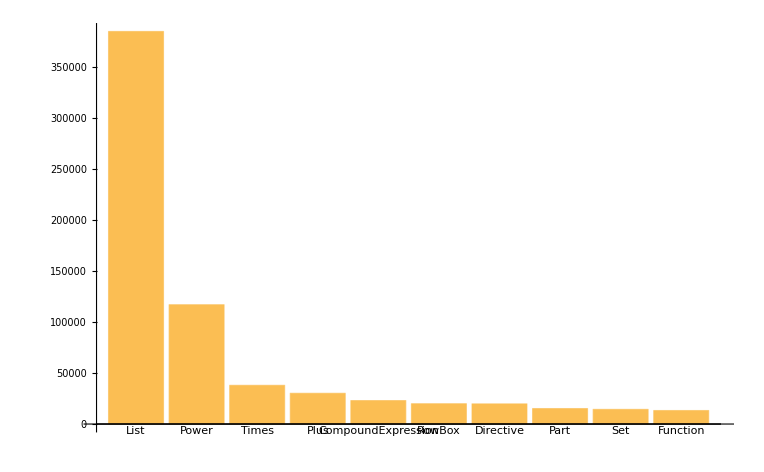

```mathematica
sorted=Reverse[SortBy[tally,Last]][[1;;10]];
BarChart[sorted[[;;,2]],ChartLabels->sorted[[;;,1]]  ]
```

## Graph of Symbol interactions

```mathematica
edges=DeleteDuplicates[ToString[#[[1]]]->ToString[#[[2]]]&/@data];
```

```mathematica
m=Max[tally[[;;,2]]] ;
cf=ColorData["DeepSeaColors"];

(* scale for vertex size *)
s=10; 

assoc=Association[ToString[#[[1]]]->N[#[[2]]/m*s]&/@tally];
cfs=Map[cf[#/s]&,assoc];ef1[el_,___]:={Arrowheads[.01],Arrow[el,0.1]};
```

```mathematica
g=Graph[edges,GraphLayout->"SpringElectricalEmbedding",VertexStyle->Normal@cfs,VertexLabels->None,VertexSize->Normal@assoc, ImageSize->{1000,1000},EdgeShapeFunction->ef1 ];
```

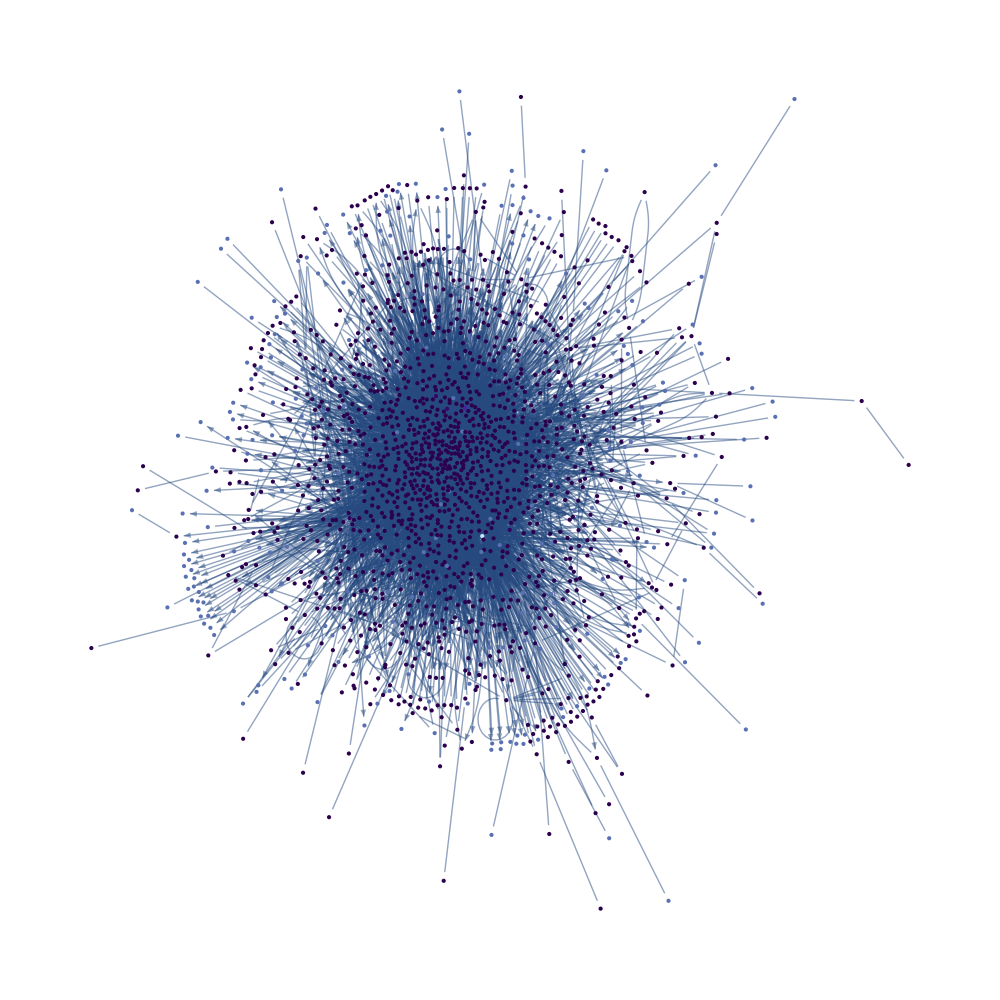

```mathematica
g
```

### Export Graph

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"data","github_symbol_graph.pdf"}],g ];
```

## Probabilities of Symbols

```mathematica
NormalizeAssociation[assoc_]:=With[{tots=Total[assoc]}, Reverse[Sort[Map[N[#/tots]&,assoc]]]]
(* Occurances of symbols *)
symOccur=Association@@Rule@@@tally;
(* Probability of symbols *)
symProb=NormalizeAssociation[symOccur];
```

## Conditional probabilities

```mathematica
(* Conditional occurances of symbols *)
symCondOccur=Map[Association@@Rule@@@Tally[#[[;;,2]]]&,GroupBy[Rule@@@data,First]];
(* Conditional probability of symbols *)
symCondProb=Map[NormalizeAssociation,symCondOccur];
```

```mathematica
symCondProb[Range]
```

<|Length→0.435606,Plus→0.174242,Times→0.113636,If→0.0681818,Slot→0.0568182,Part→0.0530303,Power→0.0246212,NonWolfram→0.0170455,Ceiling→0.0132576,PrimePi→0.00757576,Log→0.00568182,Min→0.00568182,Floor→0.00568182,Max→0.00378788,First→0.00378788,StringLength→0.00378788,VertexCount→0.00189394,IntegerPart→0.00189394,ReplaceAll→0.00189394,Sqrt→0.00189394|>

```mathematica
Length@fileNames
```

3525

```mathematica
nextSymbol[symbol_]:=Module[
{

dist,max,sel,key
},
If[symbol==Nothing,Return[Nothing]];

dist=symCondProb[symbol];

(* Maybe we never saw this symbol as head in our data *)
If[MissingQ@dist,Return[Nothing]];
max=Max[symCondProb[symbol]];
sel=Select[dist, max==#&];

(* Likewise perhaps selection failed as it was not connected to anything *)
If[sel==<||>,Return[Nothing]];
key=First@Keys[sel];

(* Since we always take max, if key==symbol we will go in circles *)
If[key==symbol,Return[Nothing]];
Return[key];
]
First@Keys[Select[symCondProb[Thread], Max[symCondProb[Thread]]==#&]]
```

Rule

```mathematica
nextSymbol[Thread]
```

Rule

```mathematica
NestList[nextSymbol[#]&,URLBuild,5]
```

{URLBuild,List,List,List,List,List}

```mathematica
n=100;
keys=Keys[symProb[[n;;n+10]]];
AssociationThread[keys,NestList[nextSymbol[#]&,#,5]&/@keys]
```

<|Range→{Range,Length,Part},Round→{Round,Times},Import→{Import,StringJoin,NotebookDirectory,EvaluationNotebook},ReplaceRepeated→{ReplaceRepeated,List},LessEqual→{LessEqual,Plus,Times},Position→{Position,Part},AbsoluteThickness→{AbsoluteThickness,Times},ArrowBox→{ArrowBox,List},Unequal→{Unequal,Part},GreaterEqual→{GreaterEqual,Slot},Sort→{Sort,NonWolfram}|>